# Form factor studies and projector studies at tree level

```mathematica
InitializeCells;
```

```mathematica
NotebookEvaluate["TTH_Head.nb"]
```

MultivariateApart -- Multivariate partial fractions. By Matthias Heller (maheller@students.uni-mainz.de) and Andreas von Manteuffel (vmante@msu.edu). Version 2021-01-18. Please see ?MultivariateApart and ?MultivariateApart`* for help.

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FFExtensionTTH is not available.

# Tree Level Stuff

```mathematica
Phy
```

## Computation of Projector and Form Factors using FiniteFlow in standard basis (correct)

## Load files which were computed with form

```mathematica
SetDirectory["/home/philipp/Programs/FORM"];
Import["/home/philipp/Programs/FORM/Output_Files/M_Matrix_Component.m"]//ToExpression
MMatrixFiniteFlowFormat=MMatrixForm//Together//FullSimplify;

Import["/home/philipp/Programs/FORM/Output_Files/K_Matrix_Component.m"]//ToExpression
KMatrixFiniteFlowFormat=KMatrixForm[[1;;16,17;;36]]//Together;

KMatrixFiniteFlowFormat=FullSimplify[Numerator[KMatrixFiniteFlowFormat]]/FullSimplify[Denominator[KMatrixFiniteFlowFormat]];

Import["/home/philipp/Programs/FORM/Output_Files/Kinematic_Prefactors_ColFactor1.m"]//ToExpression
KinematicPrefactorsFiniteFlowFormatColFact1=KinematicPrefactorsColFactor1//Together;

Import["/home/philipp/Programs/FORM/Output_Files/Kinematic_Prefactors_ColFactor2.m"]//ToExpression
KinematicPrefactorsFiniteFlowFormatColFact2=KinematicPrefactorsColFactor2//Together;


Clear[ MMatrixForm, KMatrixForm, KinematicPrefactorsColFactor1, KinematicPrefactorsColFactor2]
```

### Test of FiniteFlow algorithm for one evaluation in Mathematica

```mathematica
KinematicTestPoint=Join[{RandomKinematicReplacement[]}]//Flatten;

MMatrixNum=MMatrixFiniteFlowFormat/.FormToFeynCalcMasses/.KinematicTestPoint;
KMatrixNum=KMatrixFiniteFlowFormat/.FormToFeynCalcMasses/.KinematicTestPoint;
KinematicPrefactorsColFact1Num=KinematicPrefactorsFiniteFlowFormatColFact1/.FormToFeynCalcMasses/.KinematicTestPoint;
KinematicPrefactorsColFact2Num=KinematicPrefactorsFiniteFlowFormatColFact2/.FormToFeynCalcMasses/.KinematicTestPoint;

FVectorICol1Num=KinematicPrefactorsColFact1Num[[1;;16]]/.FormToFeynCalcMasses;
FVectorICol2Num=KinematicPrefactorsColFact2Num[[1;;16]]/.FormToFeynCalcMasses;

FVectorJCol1Num=KinematicPrefactorsColFact1Num[[17;;36]]/.FormToFeynCalcMasses;
FVectorJCol2Num=KinematicPrefactorsColFact2Num[[17;;36]]/.FormToFeynCalcMasses;

MMatrixINum = Inverse[MMatrixNum];


FormFactorsCol1=(MMatrixINum.KMatrixNum).FVectorJCol1Num+FVectorICol1Num;
FormFactorsCol2=(MMatrixINum.KMatrixNum).FVectorJCol2Num+FVectorICol2Num;
LMatrixColStructure1 = Table[Fi*Fj,{Fi,FormFactorsCol1},{Fj,FormFactorsCol1}]+Table[Fi*Fj,{Fi,FormFactorsCol2},{Fj,FormFactorsCol2}];
LMatrixColStructure2 = Table[Fi*Fj,{Fi,FormFactorsCol2},{Fj,FormFactorsCol1}]+Table[Fi*Fj,{Fi,FormFactorsCol1},{Fj,FormFactorsCol2}];



ColFactor1=Tr[LMatrixColStructure1.MMatrixNum]*CF^2*CA;
ColFactor2=Tr[LMatrixColStructure2.MMatrixNum]*(-1/2CF);


NumericAmplitudeFormFactor=SUNSimplify[ColFactor1+ColFactor2,SUNNToCACF->True]//Expand;

Import["/home/philipp/Programs/FORM/Output_Files/AmplitudeWithKinematicIdentities_S12_S13_S14_S23_S24.txt"]//ToExpression;
NumericAmplitude=SUNSimplify[AmplitudeWithKinemticIdentities/.FormToFeynCalcMasses/.KinematicTestPoint/.{SUN-> SUNN},SUNNToCACF->True]/.{gs->1,gw->1,mw->1}//Expand;

Print["Coefficients CA^2, CA^0 Traceformalism:"]
ColFactor1Trace=Coefficient[NumericAmplitude,CA,2]
ColFactor2Trace=Coefficient[NumericAmplitude,CA,0]

Print["Coefficients CA^2, CA^0 form factor method:"]
ColFactor1FormFactor=Coefficient[NumericAmplitudeFormFactor,CA,2]
ColFactor2FormFactor=Coefficient[NumericAmplitudeFormFactor,CA,0]


Print["SUNN expanded color factrs traceformalism:"]
SUNSimplify[ColFactor1Trace*CA^2,SUNNToCACF-> False]//Expand;
SUNSimplify[ColFactor2Trace,SUNNToCACF-> False]//Expand;

Print["Color Factors before SUNSimplify (FormFactorMethod):"]
SUNSimplify[ColFactor1,SUNNToCACF-> False]//Expand;
SUNSimplify[ColFactor2,SUNNToCACF-> False]//Expand;


Print["Color Factor after SUNSimplify (FormFactorMethod):"]
SUNSimplify[ColFactor1FormFactor*CA^2,SUNNToCACF-> False]//Expand;
SUNSimplify[ColFactor2FormFactor,SUNNToCACF-> False]//Expand;

SUNSimplify[CA*CF^2,SUNNToCACF-> False]//Expand;
SUNSimplify[CF*CA^2,SUNNToCACF-> False]//Expand;
SUNSimplify[CF,SUNNToCACF-> False]//Expand;
```

```mathematica
DumpGet["Output_Files/SquaredAmplitudeColStructure1.mx"]
DumpGet["Output_Files/SquaredAmplitudeColStructure2.mx"]
```

```mathematica
(SquaredAmplitudeColStructure1/.FormToFeynCalcMasses/.KinematicTestPoint)-ColFactor1/.{Ca->CA,Cf->CF}
(SquaredAmplitudeColStructure2/.FormToFeynCalcMasses/.KinematicTestPoint)-ColFactor2/.{Ca->CA,Cf->CF}
```

0

0

## FiniteFlow implementation of squared matrix element

### Set up graph (correct)

```mathematica
VariablesForFiniteFlow={s[1,2],s[1,3],s[1,4],s[2,3],s[2,4], mh, mt};
SizeOfMatrix=Length[MMatrixFiniteFlowFormat];
DiagonalElementsIndices= Range[1,SizeOfMatrix^2,SizeOfMatrix+1];

FFNewGraph[FindFormFactors, input, VariablesForFiniteFlow]

Print["Evaluate Rational Functions..."];

(*FFAlgRatFunEval[FindFormFactors, MMatrixNode, {input}, VariablesForFiniteFlow, Join@@MMatrixFiniteFlowFormat]*)
FFAlgRatFunEval[FindFormFactors, KMatrixNode  , {input}, VariablesForFiniteFlow, Join@@KMatrixFiniteFlowFormat];
FFAlgRatFunEval[FindFormFactors, MMatrixNode, {input}, VariablesForFiniteFlow, Join@@MMatrixFiniteFlowFormat];

FFAlgRatFunEval[FindFormFactors, FVectorICol1Node, {input}, VariablesForFiniteFlow, KinematicPrefactorsFiniteFlowFormatColFact1[[1;;16]]];
FFAlgRatFunEval[FindFormFactors, FVectorICol2Node, {input}, VariablesForFiniteFlow, KinematicPrefactorsFiniteFlowFormatColFact2[[1;;16]]];

FFAlgRatFunEval[FindFormFactors, FVectorJNodeCol1, {input}, VariablesForFiniteFlow,KinematicPrefactorsFiniteFlowFormatColFact1[[17;;All]]];
FFAlgRatFunEval[FindFormFactors, FVectorJNodeCol2, {input}, VariablesForFiniteFlow,KinematicPrefactorsFiniteFlowFormatColFact2[[17;;All]]]



AuxVec1 = x/@Range[16];
AuxVec2 = t/@Range[16];


Print["Invert matrix..."];
FFAlgDenseSolver[FindFormFactors,InverseMMatrixNode ,{input},VariablesForFiniteFlow,
                 Table[MMatrixFiniteFlowFormat[[i]].AuxVec1 - t[i] == 0 , {i, 1, 16}],
                 Flatten[{AuxVec1, AuxVec2}]]

FFSolverOnlyHomogeneous[FindFormFactors,InverseMMatrixNode]
FFGraphOutput[FindFormFactors,InverseMMatrixNode];
solverlearn = FFDenseSolverLearn[FindFormFactors,Flatten[{AuxVec1, AuxVec2}] ];


Print["Matrix multiplications..."]
FFAlgMatMul[FindFormFactors, InternSumMatrixMultiplication1, {InverseMMatrixNode, KMatrixNode}, 16, 16, 20];


(*From this point on I have to split the two independent color structures. *)
FFAlgMatMul[FindFormFactors, InternSumMatrixMultiplication2Col1, { InternSumMatrixMultiplication1,FVectorJNodeCol1}, 16,20,1];
FFAlgMatMul[FindFormFactors, InternSumMatrixMultiplication2Col2, { InternSumMatrixMultiplication1,FVectorJNodeCol2}, 16,20,1];

FFAlgAdd[FindFormFactors, FormFactorsCol1Node, {InternSumMatrixMultiplication2Col1, FVectorICol1Node} ];
FFAlgAdd[FindFormFactors, FormFactorsCol2Node, {InternSumMatrixMultiplication2Col2, FVectorICol2Node} ];



(*This will give the first color structure. *)
FFAlgMatMul[FindFormFactors, LMatrixColStructure1PartA, {FormFactorsCol1Node,FormFactorsCol1Node}, 16,1,16];
FFAlgMatMul[FindFormFactors, LMatrixColStructure1PartB, {FormFactorsCol2Node,FormFactorsCol2Node}, 16,1,16];

FFAlgAdd[FindFormFactors, LMatrixColStructure1Node, {LMatrixColStructure1PartA, LMatrixColStructure1PartB}];

FFAlgMatMul[FindFormFactors, SquaredAmplitudeColStructure1Matrix, {MMatrixNode, LMatrixColStructure1Node} ,16,16,16 ]



Print["Take the trace..."];



FFAlgSlice[FindFormFactors, ToExpression[StringJoin[{"DiagElem",ToString[#]}]], { SquaredAmplitudeColStructure1Matrix}, #,# ]&/@DiagonalElementsIndices;

FFAlgAdd[FindFormFactors, TraceOfMatrixColStructure1,Table[ToExpression[StringJoin[{"DiagElem",ToString[i]}]],{i,DiagonalElementsIndices}]]



(*This will give the second color structure. *)
FFAlgMatMul[FindFormFactors, LMatrixColStructure2PartA, {FormFactorsCol1Node,FormFactorsCol2Node}, 16,1,16];
FFAlgMatMul[FindFormFactors, LMatrixColStructure2PartB, {FormFactorsCol2Node,FormFactorsCol1Node}, 16,1,16];

FFAlgAdd[FindFormFactors, LMatrixColStructure2Node, {LMatrixColStructure2PartA, LMatrixColStructure2PartB}];

FFAlgMatMul[FindFormFactors, SquaredAmplitudeColStructure2Matrix, {MMatrixNode, LMatrixColStructure2Node} ,16,16,16 ]



Print["Take the trace..."];


FFAlgSlice[FindFormFactors, ToExpression[StringJoin[{"DiagCol2Elem",ToString[#]}]], { SquaredAmplitudeColStructure2Matrix}, #,# ]&/@DiagonalElementsIndices;

FFAlgAdd[FindFormFactors, TraceOfMatrixColStructure2,Table[ToExpression[StringJoin[{"DiagCol2Elem",ToString[i]}]],{i,DiagonalElementsIndices}]]


(*FFGraphDraw[FindFormFactors]*)
```

True

Evaluate Rational Functions...

True

Invert matrix...

True

Matrix multiplications...

True

Take the trace...

True

True

Take the trace...

True

### Evaluate Graph (can take long/ correct)

Reconstruction of squared amplitude

```mathematica
FFGraphOutput[FindFormFactors, TraceOfMatrixColStructure1];
SquaredAmplitudeColStructure1= FFReconstructFunction[FindFormFactors, VariablesForFiniteFlow] ;
```

```mathematica
FFGraphOutput[FindFormFactors, TraceOfMatrixColStructure2];
SquaredAmplitudeColStructure2= FFReconstructFunction[FindFormFactors, VariablesForFiniteFlow] ;
```

```mathematica
SquaredAmplitudeColStructure1=Ca*Cf^2*SquaredAmplitudeColStructure1[[1]];
SquaredAmplitudeColStructure2=-Cf/2*SquaredAmplitudeColStructure2[[1]];
```

```mathematica
DumpSave["Output_Files/SquaredAmplitudeColStructure1.mx",SquaredAmplitudeColStructure1];
DumpSave["Output_Files/SquaredAmplitudeColStructure2.mx",SquaredAmplitudeColStructure2];
```

Reconstruction of form factors

```mathematica
FFGraphOutput[FindFormFactors,  FormFactorsCol1Node];
(*ColStructure1 = T^a.T^b*)
FormFactorsColStructure1= FFReconstructFunction[FindFormFactors, VariablesForFiniteFlow] ;
```

```mathematica
FFGraphOutput[FindFormFactors,  FormFactorsCol2Node];
(*ColStructure1 = T^b.T^a*)
FormFactorsColStructure2= FFReconstructFunction[FindFormFactors, VariablesForFiniteFlow] ;
```

```mathematica
DumpSave["FormFactorsColStructure1RandomBasis.mx",FormFactorsColStructure1];
DumpSave["FormFactorsColStructure2RandomBasis.mx",FormFactorsColStructure2];
```

## Computation of tree level matrix element with symmetric tensor structures in the exchange of gluon 1 <-> 2 (correct)

## Definition of 36 tensor structures

```mathematica
eps1=ChangeDimension[PolarizationVector[p1,μ,Transversality-> True],D];
eps2=ChangeDimension[PolarizationVector[p2,ν,Transversality-> True],D];
TopSpinor=SpinorUD[Momentum[p3,D],SMP["m_t"]];
AntiTopSpinor=SpinorVBarD[Momentum[p4,D],SMP["m_t"]];


FermionP1MinusP2=(AntiTopSpinor.(GSD[p1]-GSD[p2]).TopSpinor)*SMP["m_t"];
FermionP1PlusP2=(AntiTopSpinor.(GSD[p1]+GSD[p2]).TopSpinor)*SMP["m_t"];
FermionVU=AntiTopSpinor.TopSpinor*s[1,2];
FermionP1P2MinusP2P1=AntiTopSpinor.(GSD[p1].GSD[p2]-GSD[p2].GSD[p1]).TopSpinor;
```

### Symmetric tensor structures

```mathematica
(*Group 1:*)
T1S=(eps1 FVD[p3,μ]eps2 FVD[p4,ν]-eps1 FVD[p4,μ]eps2 FVD[p3,ν])(AntiTopSpinor.(GSD[p1]-GSD[p2]).TopSpinor)*SMP["m_t"];
T2S=eps1 eps2 (FVD[p3,μ]FVD[p4,ν]-FVD[p4,μ]FVD[p3,ν])AntiTopSpinor.(GSD[p1].GSD[p2]-GSD[p2].GSD[p1]).TopSpinor;

(*Group 2:*)
T3S=eps1 eps2 (FVD[p3,μ]*FVD[p4,ν]+FVD[p4,μ]*FVD[p3,ν])AntiTopSpinor.TopSpinor*SMP["m_t"]^2;

T4S=eps1 FVD[p3,μ]eps2 FVD[p3,ν](AntiTopSpinor.(GSD[p1]+GSD[p2]).TopSpinor)*SMP["m_t"];
T5S=eps1 FVD[p4,μ]eps2 FVD[p4,ν](AntiTopSpinor.(GSD[p1]+GSD[p2]).TopSpinor)*SMP["m_t"];
T6S=(eps1 FVD[p3,μ]eps2 FVD[p4,ν]+eps1 FVD[p4,μ]eps2 FVD[p3,ν])(AntiTopSpinor.(GSD[p1]+GSD[p2]).TopSpinor)*SMP["m_t"];

T7S=s[1,2]eps1 FVD[p3,μ]eps2 FVD[p3,ν]AntiTopSpinor.TopSpinor;  (*= eps1 FVD[p3,μ]eps2 FVD[p3,ν]AntiTopSpinor.(GSD[p1].GSD[p2]+GSD[p2].GSD[p1]).TopSpinor;*)
T8S=s[1,2]eps1 FVD[p4,μ]eps2 FVD[p4,ν]AntiTopSpinor.TopSpinor; (*= eps1 FVD[p4,μ]eps2 FVD[p4,ν]AntiTopSpinor.(GSD[p1].GSD[p2]+GSD[p2].GSD[p1]).TopSpinor*)




(* Non-projector tensor structures:*)
(*0 γ structures :*)


T9S=eps1 FVD[p4,μ]eps2 FVD[p4,ν]AntiTopSpinor.TopSpinor*SMP["m_t"]^2;
T10S=eps1 MTD[μ,ν]eps2 AntiTopSpinor.TopSpinor*SMP["m_t"]^4;

(*1 γ structures:*)


T11S=eps1 MTD[μ,ν]eps2 *AntiTopSpinor.(GSD[p1]+GSD[p2]).TopSpinor*SMP["m_t"]^3;
T12S=eps1 eps2( FVD[p3,ν]AntiTopSpinor.GAD[μ].TopSpinor+ FVD[p3,μ]AntiTopSpinor.GAD[ν].TopSpinor)*SMP["m_t"]^3;
T13S=eps1 eps2( FVD[p4,ν]AntiTopSpinor.GAD[μ].TopSpinor+ FVD[p4,μ]AntiTopSpinor.GAD[ν].TopSpinor)*SMP["m_t"]^3;

(*2 γ structures:*)

T14S=eps1 MTD[μ,ν]eps2 AntiTopSpinor.(GSD[p1].GSD[p2]+GSD[p2].GSD[p1]).TopSpinor*SMP["m_t"]^2;
T15S=eps1 eps2 AntiTopSpinor.(GAD[μ].GAD[ν]+GAD[ν].GAD[μ]).TopSpinor*SMP["m_t"]^4;

T16S=eps1 eps2 (FVD[p3,ν]AntiTopSpinor.GAD[μ].GSD[p1].TopSpinor+FVD[p3,μ]AntiTopSpinor.GAD[ν].GSD[p2].TopSpinor)*SMP["m_t"]^2;
T17S=eps1 eps2 (FVD[p3,ν]AntiTopSpinor.GAD[μ].GSD[p2].TopSpinor+FVD[p3,μ]AntiTopSpinor.GAD[ν].GSD[p1].TopSpinor)*SMP["m_t"]^2;
T18S=eps1 eps2 (FVD[p4,ν]AntiTopSpinor.GAD[μ].GSD[p1].TopSpinor+FVD[p4,μ]AntiTopSpinor.GAD[ν].GSD[p2].TopSpinor)*SMP["m_t"]^2;
T19S=eps1 eps2(FVD[p4,ν]AntiTopSpinor.GAD[μ].GSD[p2].TopSpinor+FVD[p4,μ]AntiTopSpinor.GAD[ν].GSD[p1].TopSpinor)*SMP["m_t"]^2;
T20S=eps1 eps2 (FVD[p3,μ]FVD[p4,ν]+FVD[p4,μ]FVD[p3,ν])AntiTopSpinor.(GSD[p1].GSD[p2]+GSD[p2].GSD[p1]).TopSpinor;

(*3 γ structures:*)
T21S=eps1 eps2 AntiTopSpinor.(GAD[μ].GAD[ν].GSD[p1]+GAD[ν].GAD[μ].GSD[p2]).TopSpinor*SMP["m_t"]^3;

(*4 γ structures:*)
T22S=eps1 eps2 AntiTopSpinor.(GAD[μ].GAD[ν].GSD[p1].GSD[p2]+GAD[ν].GAD[μ].GSD[p2].GSD[p1]).TopSpinor*SMP["m_t"]^2;
T23S=eps1 FVD[p3,μ]eps2 FVD[p3,ν]AntiTopSpinor.TopSpinor*SMP["m_t"]^2;


TensorStructuresggTotthSymmetricBasis={T1S,T2S,T3S,T4S,T5S,T6S,T7S,T8S,T9S,T10S,T11S,T12S,T13S,T14S,T15S,T16S,T17S,T18S,T19S,T20S,T21S,T22S,T23S}//Contract;
ComplexConjugatedTensorStructuresggTotthSymmetricBasis=ComplexConjugate[#]&/@TensorStructuresggTotthSymmetricBasis;
```

### Antisymmetric

```mathematica
(*group 1:*)
T3A=eps1 eps2 (FVD[p3,μ]*FVD[p4,ν]-FVD[p4,μ]*FVD[p3,ν])AntiTopSpinor.TopSpinor*SMP["m_t"]^2;
T1A=(eps1 FVD[p3,μ]eps2 FVD[p4,ν]-eps1 FVD[p4,μ]eps2 FVD[p3,ν])(AntiTopSpinor.(GSD[p1]+GSD[p2]).TopSpinor)*SMP["m_t"];

(*group 2:*)
T4A=eps1 FVD[p3,μ]eps2 FVD[p3,ν](AntiTopSpinor.(GSD[p1]-GSD[p2]).TopSpinor)*SMP["m_t"];
T5A=eps1 FVD[p4,μ]eps2 FVD[p4,ν](AntiTopSpinor.(GSD[p1]-GSD[p2]).TopSpinor)*SMP["m_t"];
T6A=(eps1 FVD[p3,μ]eps2 FVD[p4,ν]+eps1 FVD[p4,μ]eps2 FVD[p3,ν])(AntiTopSpinor.(GSD[p1]-GSD[p2]).TopSpinor)*SMP["m_t"];
T7A=eps1 FVD[p3,μ]eps2 FVD[p3,ν]AntiTopSpinor.(GSD[p1].GSD[p2]-GSD[p2].GSD[p1]).TopSpinor;
T8A=eps1 FVD[p4,μ]eps2 FVD[p4,ν]AntiTopSpinor.(GSD[p1].GSD[p2]-GSD[p2].GSD[p1]).TopSpinor;
T2A=eps1 eps2 (FVD[p3,μ]FVD[p4,ν]+FVD[p4,μ]FVD[p3,ν])AntiTopSpinor.(GSD[p1].GSD[p2]-GSD[p2].GSD[p1]).TopSpinor;





(* Non-projector tensor structures, the naming does not mathc their symmetric counterpart.:*)
(*1 γ structures :*)
T9A=eps1 MTD[μ,ν]eps2 *AntiTopSpinor.(GSD[p1]-GSD[p2]).TopSpinor*SMP["m_t"]^3;
T10A=eps1 eps2( FVD[p3,ν]AntiTopSpinor.GAD[μ].TopSpinor- FVD[p3,μ]AntiTopSpinor.GAD[ν].TopSpinor)*SMP["m_t"]^3;
T11A=eps1 eps2( FVD[p4,ν]AntiTopSpinor.GAD[μ].TopSpinor- FVD[p4,μ]AntiTopSpinor.GAD[ν].TopSpinor)*SMP["m_t"]^3;




(*2 γ structures :*)
T12A=eps1 MTD[μ,ν]eps2 AntiTopSpinor.(GSD[p1].GSD[p2]-GSD[p2].GSD[p1]).TopSpinor*SMP["m_t"]^2;
T13A=eps1 eps2 AntiTopSpinor.(GAD[μ].GAD[ν]-GAD[ν].GAD[μ]).TopSpinor*SMP["m_t"]^2;


T14A=eps1 eps2 (FVD[p3,ν]AntiTopSpinor.GAD[μ].GSD[p1].TopSpinor-FVD[p3,μ]AntiTopSpinor.GAD[ν].GSD[p2].TopSpinor)*SMP["m_t"]^2;
T15A=eps1 eps2 (FVD[p3,ν]AntiTopSpinor.GAD[μ].GSD[p2].TopSpinor-FVD[p3,μ]AntiTopSpinor.GAD[ν].GSD[p1].TopSpinor)*SMP["m_t"]^2;
T16A=eps1 eps2 (FVD[p4,ν]AntiTopSpinor.GAD[μ].GSD[p1].TopSpinor-FVD[p4,μ]AntiTopSpinor.GAD[ν].GSD[p2].TopSpinor)*SMP["m_t"]^2;
T17A=eps1 eps2(FVD[p4,ν]AntiTopSpinor.GAD[μ].GSD[p2].TopSpinor-FVD[p4,μ]AntiTopSpinor.GAD[ν].GSD[p1].TopSpinor)*SMP["m_t"]^2;


T18A=eps1 eps2 (FVD[p3,μ]FVD[p4,ν]-FVD[p4,μ]FVD[p3,ν])AntiTopSpinor.(GSD[p1].GSD[p2]+GSD[p2].GSD[p1]).TopSpinor;
T19A=eps1 eps2 (FVD[p3,μ]FVD[p4,ν]+FVD[p4,μ]FVD[p3,ν])AntiTopSpinor.(GSD[p1].GSD[p2]-GSD[p2].GSD[p1]).TopSpinor;


(*3 γ structures:*)
T20A=eps1 eps2 AntiTopSpinor.(GAD[μ].GAD[ν].GSD[p1]-GAD[ν].GAD[μ].GSD[p2]).TopSpinor*SMP["m_t"]^3;


(*4 γ structures:*)
T21A=eps1 eps2 AntiTopSpinor.(GAD[μ].GAD[ν].GSD[p1].GSD[p2]-GAD[ν].GAD[μ].GSD[p2].GSD[p1]).TopSpinor*SMP["m_t"]^2;

TensorStructuresggTotthAntiSymmetricBasis={T1A,T2A,T3A,T4A,T5A,T6A,T7A,T8A,T9A,T10A,T11A,T12A,T13A,T14A,T15A,T16A,T17A,T18A,T19A,T20A,T21A}//Contract;
ComplexConjugatedTensorStructuresggTotthAntiSymmetricBasis=ComplexConjugate[#]&/@TensorStructuresggTotthAntiSymmetricBasis;
```

## Computation of matrix M for symmetric and antisymmetric tensor structures

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,{p1,p2,p3,p4,p5},{0,0,SMP["m_t"],SMP["m_t"],SMP["m_H"]}];
```

The steps leading to this basis choice of tensor structures are :
  1. Compute M matrix for all found tensor structures in general dimension D
  2. Remove all tensor structures which give raise to the variable D in the matrix M.
  3. The rank of the matrix M is 36 in general dimension D and 16 in D = 4 (as expected)
  4. I observed that there are 5 tensor structures which decouple from the rest. 
  5. Analyse them in more detail -> only 4 independent. 
  6. By trial and error I found the two tensor structures which depend on each other.
  7. At this point there are only 8 antisymmetric tensor structures left. 
  8. Choose the 8 symmetric tensor structures, which correspond to the antisymmetric ones. Aka T2A -> T2S is a symmetric tensor structure.
  9. Order the position such that the block diagonal structure becomes manifest.

```mathematica
AntiAndSymmetricTensorStructuresDecoupled={T1S,T2S,T3A,T1A,T3S,T4S,T5S,T6S,T7S,T8S,T4A,T5A,T6A,T7A,T8A,T2A}//Contract;
ComplexConjugatedAntiAndSymmetricTensorStructuresDecoupled=ComplexConjugate[#]&/@AntiAndSymmetricTensorStructuresDecoupled;
```

```mathematica
MMatrixProjectorAntiAndSymmetricTensorStructuresDecoupled=ComputeMMatrixForProjector[AntiAndSymmetricTensorStructuresDecoupled,ComplexConjugatedAntiAndSymmetricTensorStructuresDecoupled, {ReplacementRulesForKinematicVariablesOfMMatrix->FivePointMandelstamReplacementsLorenzo}];
```

```mathematica
DumpSave[MathematicaInputPath<>"MMatrixProjectorAntiAndSymmetricTensorStructuresDecoupled.mx",MMatrixProjectorAntiAndSymmetricTensorStructuresDecoupled];
```

```mathematica
DumpGet["Output_Files/MMatrixProjectorAntiAndSymmetricTensorStructuresDecoupled.mx"];
```

Check rank of M matrix (should be 16)

16

Check determinant of M matrix (should be non zero)

52978301886001595367646319787440204141370604172431626852828799454747735829428435992924218271259176644175914838702334434359561411756712880245943979997978182923028620097717542872608830789990696854789359561100487124749834546167805356478937793551981377170189640503355254847504288679240695715841373689942141241900288630000242456415993252967400307326350464997270198521600871172571957466347055686526111881955572563008775210122580260307275261389267100716631353158719302977161765896788702570399298519456592781005301681809267555717312732772994300655836551322728910337713698380819224302248178220535844971036894563247256207584806052604548876029759329518076372801/17152851575827060280082869784850701732457206787397726371902697340849466616668539755107382708470016

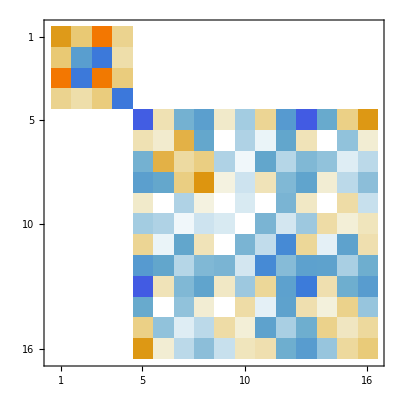

```mathematica
TestPoint=RandomKinematicReplacement[];

Print["Check rank of M matrix (should be 16)"]
MMatrixProjectorAntiAndSymmetricTensorStructuresDecoupled/.FormToFeynCalcMasses/.TestPoint//MatrixRank
Print["Check determinant of M matrix (should be non zero)"]
MMatrixProjectorAntiAndSymmetricTensorStructuresDecoupled/.FormToFeynCalcMasses/.TestPoint//Det
MMatrixProjectorAntiAndSymmetricTensorStructuresDecoupled/.FormToFeynCalcMasses/.TestPoint//MatrixPlot
```

```mathematica
Import["/home/philipp/Programs/FORM/Output_Files/M_Matrix_Component_Anti_Symmetric.m"]//ToExpression;
```

```mathematica
TestPoint=RandomKinematicReplacement[];
test1=MMatrixForm[[1;;16,1;;16]]/.FivePointMandelstamReplacementsLorenzo/.FormToFeynCalcMasses/.TestPoint;
test2=MMatrixProjectorAntiAndSymmetricTensorStructuresDecoupled/.FivePointMandelstamReplacementsLorenzo/.FormToFeynCalcMasses/.TestPoint;

test1-test2//MatrixPlot
Clear[test1,test2]
```

-Graphics-

## Computation of projector matrix

### Take the inverse of the matrix M

```mathematica
DumpGet["Output_Files/MMatrixProjectorAntiAndSymmetricTensorStructuresDecoupled.mx"];
ProjectorMatrixAntiAndSymmetricTensorStructuresDecoupled=FFInverse[MMatrixProjectorAntiAndSymmetricTensorStructuresDecoupled];
```

### Extract the Gram determinant of the matrix and give a replacement rule to replace with a name .

```mathematica
(* The index of the Gram determinant in the list should be verified. *)
GramDeterminantOfProjector=Level[Factor[Denominator[ProjectorMatrixAntiAndSymmetricTensorStructuresDecoupled[[1,1]]]][[-1]],1][[1]];

Print["Check wether the two diffenitions of the Gram determinant are the same (should give 0)"]
GramDeterminantOfProjector-GramSymmetricBasis/.InverseReplacementGramSymmetrizedBasis


ReplaceGramDeterminantInProjectorWithSymbol         ={GramDeterminantOfProjector->GramSymmetricBasis};
ReplaceGramDeterminantInProjectorWithExpression={GRAMProjector->GramSymmetricBasis};

DumpSave["Output_Files/ReplaceGramDeterminantInProjector.mx",ReplaceGramDeterminantInProjectorWithSymbol];
```

0

### Simplify result of projector

```mathematica
ProjectorMatrixAntiAndSymmetricTensorStructuresDecoupled=Factor[ProjectorMatrixAntiAndSymmetricTensorStructuresDecoupled]/.ReplaceGramDeterminantInProjectorWithSymbol;
DumpSave["Output_Files/ProjectorMatrixAntiAndSymmetricTensorStructuresDecoupled.mx",ProjectorMatrixAntiAndSymmetricTensorStructuresDecoupled];
```

### Load Projector matrix of symmetrized basis .

```mathematica
DumpGet["Output_Files/ProjectorMatrixAntiAndSymmetricTensorStructuresDecoupled.mx"]
```

### Save coefficients of projector matrix in FORM format

```mathematica
DeleteFile["Modules_Tree_Level_Computation/Definition_ProjectorCoefficient_as_ID.h"]

FileForProjectorCoefficients=OpenWrite["Output_Files/Definition_ProjectorCoefficient_as_ID.m",PageWidth->Infinity,FormatType->InputForm];

For[FormFactorNumber=1,FormFactorNumber<=16,FormFactorNumber++,
For[ProjectorNumber=1,ProjectorNumber<=16,ProjectorNumber++,
WriteString[FileForProjectorCoefficients,StringJoin[{"id ProjectorCoefficientF",ToString[FormFactorNumber],"P",ToString[ProjectorNumber] ," = "}] ];
Write[FileForProjectorCoefficients,ProjectorMatrixAntiAndSymmetricTensorStructuresDecoupled[[FormFactorNumber,ProjectorNumber]]/.ConvertMandelstamMathematicaToForm];
WriteString[FileForProjectorCoefficients,";\n"]
]
]

Close[FileForProjectorCoefficients];
```

```mathematica
Export["Test_Projector_Coefficients.txt",ProjectorMatrixAntiAndSymmetricTensorStructuresDecoupled]
```

Test_Projector_Coefficients.txt

## Computation of K matrix

```mathematica
KMatrixDecoupledBasisToStandardBasis=ComputeKMatrix[TensorStructuresggTotth,ComplexConjugatedAntiAndSymmetricTensorStructuresDecoupled,{ReplacementRulesForKinematicVariablesOfMMatrix->FivePointMandelstamReplacementsLorenzo}];
```

```mathematica
DumpSave["Output_Files/KMatrixDecoupledBasisToStandardBasis.mx",KMatrixDecoupledBasisToStandardBasis];
```

#### Comparison with Form result for K matrix (correct)

```mathematica
DumpGet["Output_Files/KMatrixDecoupledBasisToStandardBasis.mx"];
```

```mathematica
Import["/home/philipp/Programs/FORM/Output_Files/K_Matrix_Component_Anti_Symmetric.m"]//ToExpression;
```

```mathematica
TestPoint=RandomKinematicReplacement[];
test1=KMatrixForm/.FivePointMandelstamReplacementsLorenzo/.FormToFeynCalcMasses/.TestPoint;
test2=KMatrixDecoupledBasisToStandardBasis/.FivePointMandelstamReplacementsLorenzo/.FormToFeynCalcMasses/.TestPoint;

test1-test2//MatrixPlot

Clear[test1,test2]
```

-Graphics-

## Computation of form factors and squared matrix element in FiniteFlow (correct)

### Load FiniteFlow quantities

```mathematica
DumpGet["Output_Files/KMatrixDecoupledBasisToStandardBasis.mx"];
KMatrixFiniteFlowFormat=KMatrixDecoupledBasisToStandardBasis;

(*KMatrixFiniteFlowFormat=KMatrixDecoupledBasisToRLBasis/.{Eps[Momentum[p1],Momentum[p2],Momentum[p3],Momentum[p4]]->Gram/I/4}//Together;*)

DumpGet["Output_Files/MMatrixProjectorAntiAndSymmetricTensorStructuresDecoupled.mx"];
MMatrixFiniteFlowFormat=MMatrixProjectorAntiAndSymmetricTensorStructuresDecoupled;

Import["/home/philipp/Programs/FORM/Output_Files/Kinematic_Prefactors_ColFactor1.m"]//ToExpression
KinematicPrefactorsFiniteFlowFormatColFact1=KinematicPrefactorsColFactor1/.FivePointMandelstamReplacementsLorenzo//Together;

Import["/home/philipp/Programs/FORM/Output_Files/Kinematic_Prefactors_ColFactor2.m"]//ToExpression
KinematicPrefactorsFiniteFlowFormatColFact2=KinematicPrefactorsColFactor2/.FivePointMandelstamReplacementsLorenzo//Together;


Clear[ MMatrixProjectorAntiAndSymmetricTensorStructuresDecoupled,KMatrixDecoupledBasisToStandardBasis, KinematicPrefactorsColFactor1, KinematicPrefactorsColFactor2]
```

Import::nffil: File /home/philipp/Programs/FORM/Output_Files/Kinematic_Prefactors_ColFactor1.m not found during Import.

$Aborted

Import::nffil: File /home/philipp/Programs/FORM/Output_Files/Kinematic_Prefactors_ColFactor2.m not found during Import.

$Aborted

### Setting up graph

{mh,mt,s(1,2),s(1,4),s(2,3),s(3,5),s(4,5)}

True

Evaluate Rational Functions...

True

Invert matrix...

True

Matrix multiplications...

True

Take the trace...

True

True

Take the trace...

True

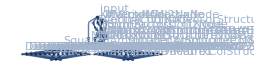

```mathematica
VariablesForFiniteFlow=Union@@Variables/@{KinematicPrefactorsFiniteFlowFormatColFact1,KinematicPrefactorsFiniteFlowFormatColFact2,MMatrixFiniteFlowFormat,KMatrixFiniteFlowFormat}

(*Check if number of kinematic variables is 7 (5 Mandelstams + 2 masses )*)
ErrorMessageInconsistentKinematics=StringJoin[{"Inconsitency in the number of kinmatic variables. Number of variables = ",ToString[Length[VariablesForFiniteFlow]]," should be 7."}];
If[Length[VariablesForFiniteFlow]!=7,Print[ErrorMessageInconsistentKinematics]; Abort[]]


(*These information are needed to compute the trace at the end of th ecomputation*)
SizeOfMMatrix=NumberOfIndependentProjectorStructures=Length[MMatrixFiniteFlowFormat];
DiagonalElementsIndices= Range[1,SizeOfMMatrix^2,SizeOfMMatrix+1];

FFNewGraph[FindFormFactorsSymmetrizedBasis, input, VariablesForFiniteFlow]

Print["Evaluate Rational Functions..."];

(*FFAlgRatFunEval[FindFormFactors, MMatrixNode, {input}, VariablesForFiniteFlow, Join@@MMatrixFiniteFlowFormat]*)
FFAlgRatFunEval[FindFormFactorsSymmetrizedBasis, KMatrixNode  , {input}, VariablesForFiniteFlow, Join@@KMatrixFiniteFlowFormat];
FFAlgRatFunEval[FindFormFactorsSymmetrizedBasis, MMatrixNode, {input}, VariablesForFiniteFlow, Join@@MMatrixFiniteFlowFormat];

(*opposed to the standard basis above all the tensor structures are changed.*)
FFAlgRatFunEval[FindFormFactorsSymmetrizedBasis, FVectorCol1Node, {input}, VariablesForFiniteFlow, KinematicPrefactorsFiniteFlowFormatColFact1];
FFAlgRatFunEval[FindFormFactorsSymmetrizedBasis, FVectorCol2Node, {input}, VariablesForFiniteFlow, KinematicPrefactorsFiniteFlowFormatColFact2]


AuxVec1 = x/@Range[16];
AuxVec2 = t/@Range[16];


Print["Invert matrix..."];
FFAlgDenseSolver[FindFormFactorsSymmetrizedBasis,InverseMMatrixNode ,{input},VariablesForFiniteFlow,
                 Table[MMatrixFiniteFlowFormat[[i]].AuxVec1 - t[i] == 0 , {i, 1, NumberOfIndependentProjectorStructures}],
                 Flatten[{AuxVec1, AuxVec2}]]

FFSolverOnlyHomogeneous[FindFormFactorsSymmetrizedBasis,InverseMMatrixNode]
FFGraphOutput[FindFormFactorsSymmetrizedBasis,InverseMMatrixNode];
solverlearn = FFDenseSolverLearn[FindFormFactorsSymmetrizedBasis,Flatten[{AuxVec1, AuxVec2}] ];


Print["Matrix multiplications..."]
FFAlgMatMul[FindFormFactorsSymmetrizedBasis, ContractionOfTensorStructures, {InverseMMatrixNode, KMatrixNode}, 16, 16,36];


(*From this point on I have to split the two independent color structures. *)
FFAlgMatMul[FindFormFactorsSymmetrizedBasis, FormFactorsCol1Node, {ContractionOfTensorStructures,FVectorCol1Node}, 16,36,1];
FFAlgMatMul[FindFormFactorsSymmetrizedBasis, FormFactorsCol2Node, {ContractionOfTensorStructures,FVectorCol2Node}, 16,36,1];


(*This will give the first color structure. *)
FFAlgMatMul[FindFormFactorsSymmetrizedBasis, LMatrixColStructure1PartA, {FormFactorsCol1Node,FormFactorsCol1Node}, 16,1,16];
FFAlgMatMul[FindFormFactorsSymmetrizedBasis, LMatrixColStructure1PartB, {FormFactorsCol2Node,FormFactorsCol2Node}, 16,1,16];

FFAlgAdd[FindFormFactorsSymmetrizedBasis, LMatrixColStructure1Node, {LMatrixColStructure1PartA, LMatrixColStructure1PartB}];

FFAlgMatMul[FindFormFactorsSymmetrizedBasis, SquaredAmplitudeColStructure1Matrix, {MMatrixNode, LMatrixColStructure1Node} ,16,16,16 ]


Print["Take the trace..."];

FFAlgSlice[FindFormFactorsSymmetrizedBasis, ToExpression[StringJoin[{"DiagElem",ToString[#]}]], { SquaredAmplitudeColStructure1Matrix}, #,# ]&/@DiagonalElementsIndices;
FFAlgAdd[FindFormFactorsSymmetrizedBasis, TraceOfMatrixColStructure1,Table[ToExpression[StringJoin[{"DiagElem",ToString[i]}]],{i,DiagonalElementsIndices}]]



(*This will give the second color structure. *)
FFAlgMatMul[FindFormFactorsSymmetrizedBasis, LMatrixColStructure2PartA, {FormFactorsCol1Node,FormFactorsCol2Node}, 16,1,16];
FFAlgMatMul[FindFormFactorsSymmetrizedBasis, LMatrixColStructure2PartB, {FormFactorsCol2Node,FormFactorsCol1Node}, 16,1,16];

FFAlgAdd[FindFormFactorsSymmetrizedBasis, LMatrixColStructure2Node, {LMatrixColStructure2PartA, LMatrixColStructure2PartB}];

FFAlgMatMul[FindFormFactorsSymmetrizedBasis, SquaredAmplitudeColStructure2Matrix, {MMatrixNode, LMatrixColStructure2Node} ,16,16,16 ]



Print["Take the trace..."];


FFAlgSlice[FindFormFactorsSymmetrizedBasis, ToExpression[StringJoin[{"DiagCol2Elem",ToString[#]}]], { SquaredAmplitudeColStructure2Matrix}, #,# ]&/@DiagonalElementsIndices;

FFAlgAdd[FindFormFactorsSymmetrizedBasis, TraceOfMatrixColStructure2,Table[ToExpression[StringJoin[{"DiagCol2Elem",ToString[i]}]],{i,DiagonalElementsIndices}]]

FFGraphDraw[FindFormFactorsSymmetrizedBasis]
```

### Evaluate Graph

```mathematica
FFGraphOutput[FindFormFactorsSymmetrizedBasis, TraceOfMatrixColStructure1];
SquaredAmplitudeColStructure1SymmetrizedBasis= FFReconstructFunction[FindFormFactorsSymmetrizedBasis, VariablesForFiniteFlow] ;
SquaredAmplitudeColStructure1SymmetrizedBasis=Ca*Cf^2*SquaredAmplitudeColStructure1SymmetrizedBasis[[1]];
```

```mathematica
FFGraphOutput[FindFormFactorsSymmetrizedBasis, TraceOfMatrixColStructure2];
SquaredAmplitudeColStructure2SymmetrizedBasis= FFReconstructFunction[FindFormFactorsSymmetrizedBasis, VariablesForFiniteFlow] ;
SquaredAmplitudeColStructure2SymmetrizedBasis=-Cf/2*SquaredAmplitudeColStructure2SymmetrizedBasis[[1]];
```

```mathematica
FFGraphOutput[ FindFormFactorsSymmetrizedBasis,FormFactorsCol1Node]
FormFactorsColStructure1SymmetrizedBasis= FFReconstructFunction[FindFormFactorsSymmetrizedBasis, VariablesForFiniteFlow] ;
```

```mathematica
FFGraphOutput[ FindFormFactorsSymmetrizedBasis,FormFactorsCol2Node]
FormFactorsColStructure2SymmetrizedBasis= FFReconstructFunction[FindFormFactorsSymmetrizedBasis, VariablesForFiniteFlow] ;
```

#### Save results into files

```mathematica
DumpSave["Output_Files/FormFactorsColStructure1SymmetrizedBasis.mx",FormFactorsColStructure1SymmetrizedBasis];
DumpSave["Output_Files/FormFactorsColStructure2SymmetrizedBasis.mx",FormFactorsColStructure2SymmetrizedBasis];
```

### Check symmetry properties of form factors (correct)

```mathematica
DumpGet["Output_Files/FormFactorsColStructure1SymmetrizedBasis.mx"]
DumpGet["Output_Files/FormFactorsColStructure2SymmetrizedBasis.mx"]

FormFactorsColStructure1SymmetrizedBasis*2/mt//Cancel;
FormFactorsColStructure1SymmetrizedBasis=%/.{mt->√mt2,mh->√mH2}/.mt2->1/.ConvertMandelstamMathematicaToForm/.RKinematicLorenzoSymmetricVars/.mt2->1;

FormFactorsColStructure2SymmetrizedBasis*2/mt//Cancel;
FormFactorsColStructure2SymmetrizedBasis=%/.{mt->√mt2,mh->√mH2}/.mt2->1/.ConvertMandelstamMathematicaToForm/.RKinematicLorenzoSymmetricVars/.mt2->1;

KinematicTestPoint=NRandomEvaluation[KinematicVarsSymmetric,OutputStyle->"Rules"];
```

```mathematica
FormFactorsColStructure1SymmetrizedBasis/.{s12->49/5,s13->-7/4,s14->-17/3,s23->-1/7,s24->2/3,s34->19/5,mt2->1}//N
```

{-0.523877,-0.179512,0.116173,0.339095,-0.365991,0.164596,0.0167306,0.0692803,0.13468,0.100136,-0.130927,-0.0910888,-0.111008,0.00520998,-0.00903797,-0.0120419}

```mathematica
CorrectCrossingQ=CrossXIJ[FormFactorsColStructure1SymmetrizedBasis[[{1,2,5,6,7,8,9,10}]],"x12"]-FormFactorsColStructure2SymmetrizedBasis[[{1,2,5,6,7,8,9,10}]]/.KinematicTestPoint;

CorrectCrossingQ=0==Total[CorrectCrossingQ];

Print["Symmetric tensor formfactors have right symmetry property: ", CorrectCrossingQ]


CorrectCrossingQ=CrossXIJ[FormFactorsColStructure1SymmetrizedBasis[[{3,4,11,12,13,14,15,16}]],"x12"]+FormFactorsColStructure2SymmetrizedBasis[[{3,4,11,12,13,14,15,16}]]/.KinematicTestPoint;

CorrectCrossingQ=0==Total[CorrectCrossingQ];
Print["Anti Symmetric tensor formfactors have right symmetry property: ", CorrectCrossingQ]
```

Symmetric tensor formfactors have right symmetry property: True

Anti Symmetric tensor formfactors have right symmetry property: True

### Compare with previous correct results (correct)

```mathematica
DumpGet["Output_Files/SquaredAmplitudeColStructure1.mx"];
DumpGet["Output_Files/SquaredAmplitudeColStructure2.mx"];
```

```mathematica
SquaredAmplitudeColStructure1/.{Ca->1,Cf->1}//Factor//MultivariateApart
```

```mathematica
%//Variables
```

{mt,s(1,3),mh,s(1,2),s(2,3),s(1,4),s(2,4)}

```mathematica
TestPoint=RandomKinematicReplacement[];

Print["Comparision with previous result (should give 0)"]
SquaredAmplitudeColStructure1SymmetrizedBasis-SquaredAmplitudeColStructure1/.FivePointMandelstamReplacementsLorenzo/.FormToFeynCalcMasses/.TestPoint

Print["Comparision with previous result (should give 0)"]
SquaredAmplitudeColStructure2SymmetrizedBasis-SquaredAmplitudeColStructure2/.FivePointMandelstamReplacementsLorenzo/.FormToFeynCalcMasses/.TestPoint
```

Comparision with previous result (should give 0)

(13895036940732395858028965703932673607388736967990536757309085 Ca Cf^2)/15421995172479981654472917820011000435881798344832+SquaredAmplitudeColStructure1SymmetrizedBasis

Comparision with previous result (should give 0)

0

```mathematica
(SquaredAmplitudeColStructure1SymmetrizedBasis/.DummyReplacementSwap1And2/.ReplacementSwap1And2)/.FormToFeynCalcMasses/.KinematicTestPoint
SquaredAmplitudeColStructure1SymmetrizedBasis/.FormToFeynCalcMasses/.KinematicTestPoint

(SquaredAmplitudeColStructure2SymmetrizedBasis/.DummyReplacementSwap1And2/.ReplacementSwap1And2)/.FormToFeynCalcMasses/.KinematicTestPoint
SquaredAmplitudeColStructure2SymmetrizedBasis/.FormToFeynCalcMasses/.KinematicTestPoint
```

-(140462799331243061941491351224843804705468042140138165732082085398563 Ca Cf^2)/5457395605319360898994595079268034610802799228135431680

-(140462799331243061941491351224843804705468042140138165732082085398563 Ca Cf^2)/5457395605319360898994595079268034610802799228135431680

-(6074374401312293772633874039391318095947968520064417 Cf)/258392813027798080329730842493313666820000

-(6074374401312293772633874039391318095947968520064417 Cf)/258392813027798080329730842493313666820000

### Comparison with Form results

```mathematica
Import["/home/philipp/Programs/FORM/Output_Files/FormFactorFORM.m"]//ToExpression
```

$Aborted

```mathematica
Import["/home/philipp/Programs/FORM/Output_Files/Form_Factors_One_Loop_code.m"]//ToExpression
```

```mathematica
FormFactorFORM2[[1]]/.FivePointMandelstamReplacementsLorenzo//Together//Denominator
FormFactorOneLoop[[1]]/.FivePointMandelstamReplacementsLorenzo//Together//Denominator
```

GRAMProjector^2 mw (s(1,2)+s(1,4)-s(3,5)) (s(1,2)+s(2,3)-s(4,5))

GRAMProjector^2 mw (s(1,2)+s(1,4)-s(3,5)) (s(1,2)+s(2,3)-s(4,5))

```mathematica
TestPoint=RandomKinematicReplacement[];

FormResultColFactor1=FormFactorFORM/.Iunit->1/.SetGlobalConstantPrefactorsTo1/.{colFactor1->1,colFactor2->0}/.GRAMProjector->GramSymmetricBasis/.InverseReplacementGramSymmetrizedBasis/.FivePointMandelstamReplacementsLorenzo;
FormResultColFactor2=FormFactorFORM/.Iunit->1/.SetGlobalConstantPrefactorsTo1/.{colFactor1->0,colFactor2->1}/.GRAMProjector->GramSymmetricBasis/.InverseReplacementGramSymmetrizedBasis/.FivePointMandelstamReplacementsLorenzo;

VerifyColFactor1=FormFactorsColStructure1SymmetrizedBasis-FormResultColFactor1/.FormToFeynCalcMasses/.TestPoint
VerifyColFactor2=FormFactorsColStructure2SymmetrizedBasis-FormResultColFactor2/.FormToFeynCalcMasses/.TestPoint
```

```mathematica
TestPoint=RandomKinematicReplacement[];

FormResultColFactor1=FormFactorFORM2/.Iunit->1/.SetGlobalConstantPrefactorsTo1/.{colFactor1->1,colFactor2->0}/.GRAMProjector->GramSymmetricBasis/.InverseReplacementGramSymmetrizedBasis/.FivePointMandelstamReplacementsLorenzo;
FormResultColFactor2=FormFactorFORM2/.Iunit->1/.SetGlobalConstantPrefactorsTo1/.{colFactor1->0,colFactor2->1}/.GRAMProjector->GramSymmetricBasis/.InverseReplacementGramSymmetrizedBasis/.FivePointMandelstamReplacementsLorenzo;

VerifyColFactor1=FormFactorsColStructure1SymmetrizedBasis-FormResultColFactor1/.FormToFeynCalcMasses/.TestPoint
VerifyColFactor2=FormFactorsColStructure2SymmetrizedBasis-FormResultColFactor2/.FormToFeynCalcMasses/.TestPoint
```

```mathematica
Test=FormFactorOneLoop/.colFactor2->0/.colFactor1->1/.SetGlobalConstantPrefactorsTo1/.Iunit->1/.GRAMProjector->GramSymmetricBasis/.InverseReplacementGramSymmetrizedBasis/.FivePointMandelstamReplacementsLorenzo;
Test-FormFactorsColStructure1SymmetrizedBasis/.FormToFeynCalcMasses/.TestPoint
```

{0,-3773151538867485171187018501397133/54937320536070055565994460668063290930229253553000,372301787253221537306920846616406179/5416608507469830286285646150868471011524718903196750,207693474336968372197449443/7013274962051496455233335404433611608114372794000,154485877962630977624872888375533184183/2253309139107449399094828798761283940794283063729848000,-1847147881370430380872999/21499427525783031497080015277337960434948000,77604076531738401401212587/903366338936265589600987612524472834055139500,-45443869958779628640496742357/1318495692865681333583867056033518982325502085272000,20344017142338862353646334136551863768931/61715740700674391652752546430492023134236001452924000,528755729653906741582861092784198461860353/1604609258217534182971566207192792601490136037776024000,-2530643471846751981/88381900244117437995691844301221595500,-17720508043052727251/618673301708822065969842910108551168500,-17717506172989995559/618673301708822065969842910108551168500,-11322511090161450575146266838892987/82405980804105083348991691002094936395343880329500,-25870797982524144247696941701989853/188356527552240190511981008004788426046500297896000,-30199039913103293504372442840339143/439498564288560444527955685344506327441834028424000}

```mathematica
Test/.FormToFeynCalcMasses/.TestPoint
```

{22794016731107595414652089833/3707965391477252349375377092234340354907345600,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

## Diagonalize first block

```mathematica
T1D=eps1 eps2 (FVD[p3,μ]*FVD[p4,ν]-FVD[p4,μ]*FVD[p3,ν])AntiTopSpinor.TopSpinor*SMP["m_t"]^2;
T2D=(eps1 FVD[p3,μ]eps2 FVD[p4,ν]-eps1 FVD[p4,μ]eps2 FVD[p3,ν])(AntiTopSpinor.(GSD[q1]).TopSpinor)*SMP["m_t"];
T3D=(eps1 FVD[p3,μ]eps2 FVD[p4,ν]-eps1 FVD[p4,μ]eps2 FVD[p3,ν])(AntiTopSpinor.(GSD[q2]).TopSpinor)*SMP["m_t"];
T4D=eps1 eps2 (FVD[p3,μ]FVD[p4,ν]-FVD[p4,μ]FVD[p3,ν])AntiTopSpinor.(GSD[q1].GSD[q2]).TopSpinor;

DiagonalFirstBlock={T1D,T2D,T3D,T4D}//Contract;
DiagonalFirstBlockC=ComplexConjugate/@DiagonalFirstBlock;
```

```mathematica
MMatrixDiagonalization=ComputeMMatrixForProjector[DiagonalFirstBlock,DiagonalFirstBlockC, {ReplacementRulesForKinematicVariablesOfMMatrix->FivePointMandelstamReplacementsLorenzo}];
```

```mathematica
MMatrixDiagonalization/.{Pair[Momentum[q1,D],Momentum[p3,D]]->0,Pair[Momentum[q1,D],Momentum[p4,D]]->0,Pair[Momentum[q2,D],Momentum[p3,D]]->0,Pair[Momentum[q2,D],Momentum[p4,D]]->0,Pair[Momentum[q2,D],Momentum[q1,D]]->0}
```

((mt^4 (-s(1,2)+s(3,5)+s(4,5)-mh^2+2 mt^2) (mh^4 (s(1,2))^2+mt^4 (-2 mh^2 s(1,2)+(s(1,4))^2+(s(2,3))^2+2 s(1,4) s(2,3)+2 s(1,2) (s(1,4)+s(2,3))+2 s(2,3) s(3,5)+2 (s(1,4)-s(3,5)) s(4,5))+2 mt^2 (mh^2 s(1,2) (s(1,4)+s(2,3))-(s(1,4)+s(2,3)) (s(2,3) s(3,5)+(s(1,4)-s(3,5)) s(4,5))-s(1,2) ((s(1,4))^2+2 (s(4,5)-s(2,3)) s(1,4)+s(2,3) (s(2,3)+2 s(3,5))))-2 mh^2 s(1,2) (s(1,2) (s(1,4)+s(2,3))+s(1,4) (2 s(2,3)-s(4,5))+s(3,5) (s(4,5)-s(2,3)))-2 mt^6 (s(1,4)+s(2,3))+(s(1,2) (s(1,4)-s(2,3))+s(2,3) s(3,5))^2+(s(1,4)-s(3,5))^2 (s(4,5))^2+2 (s(2,3) (s(1,4)-s(3,5)) s(3,5)+s(1,2) (s(1,4) (s(2,3)-s(1,4))+(s(1,4)+s(2,3)) s(3,5))) s(4,5)+mt^8))/(s(1,2))^2 | 0 | 0 | 0
0 | (mt^2 q1^2 (s(1,2)-s(3,5)-s(4,5)+mh^2+2 mt^2) (mh^4 (s(1,2))^2+mt^4 (-2 mh^2 s(1,2)+(s(1,4))^2+(s(2,3))^2+2 s(1,4) s(2,3)+2 s(1,2) (s(1,4)+s(2,3))+2 s(2,3) s(3,5)+2 (s(1,4)-s(3,5)) s(4,5))+2 mt^2 (mh^2 s(1,2) (s(1,4)+s(2,3))-(s(1,4)+s(2,3)) (s(2,3) s(3,5)+(s(1,4)-s(3,5)) s(4,5))-s(1,2) ((s(1,4))^2+2 (s(4,5)-s(2,3)) s(1,4)+s(2,3) (s(2,3)+2 s(3,5))))-2 mh^2 s(1,2) (s(1,2) (s(1,4)+s(2,3))+s(1,4) (2 s(2,3)-s(4,5))+s(3,5) (s(4,5)-s(2,3)))-2 mt^6 (s(1,4)+s(2,3))+(s(1,2) (s(1,4)-s(2,3))+s(2,3) s(3,5))^2+(s(1,4)-s(3,5))^2 (s(4,5))^2+2 (s(2,3) (s(1,4)-s(3,5)) s(3,5)+s(1,2) (s(1,4) (s(2,3)-s(1,4))+(s(1,4)+s(2,3)) s(3,5))) s(4,5)+mt^8))/(s(1,2))^2 | 0 | 0
0 | 0 | (mt^2 q2^2 (s(1,2)-s(3,5)-s(4,5)+mh^2+2 mt^2) (mh^4 (s(1,2))^2+mt^4 (-2 mh^2 s(1,2)+(s(1,4))^2+(s(2,3))^2+2 s(1,4) s(2,3)+2 s(1,2) (s(1,4)+s(2,3))+2 s(2,3) s(3,5)+2 (s(1,4)-s(3,5)) s(4,5))+2 mt^2 (mh^2 s(1,2) (s(1,4)+s(2,3))-(s(1,4)+s(2,3)) (s(2,3) s(3,5)+(s(1,4)-s(3,5)) s(4,5))-s(1,2) ((s(1,4))^2+2 (s(4,5)-s(2,3)) s(1,4)+s(2,3) (s(2,3)+2 s(3,5))))-2 mh^2 s(1,2) (s(1,2) (s(1,4)+s(2,3))+s(1,4) (2 s(2,3)-s(4,5))+s(3,5) (s(4,5)-s(2,3)))-2 mt^6 (s(1,4)+s(2,3))+(s(1,2) (s(1,4)-s(2,3))+s(2,3) s(3,5))^2+(s(1,4)-s(3,5))^2 (s(4,5))^2+2 (s(2,3) (s(1,4)-s(3,5)) s(3,5)+s(1,2) (s(1,4) (s(2,3)-s(1,4))+(s(1,4)+s(2,3)) s(3,5))) s(4,5)+mt^8))/(s(1,2))^2 | 0
0 | 0 | 0 | (q1^2 q2^2 (-s(1,2)+s(3,5)+s(4,5)-mh^2+2 mt^2) (mh^4 (s(1,2))^2+mt^4 (-2 mh^2 s(1,2)+(s(1,4))^2+(s(2,3))^2+2 s(1,4) s(2,3)+2 s(1,2) (s(1,4)+s(2,3))+2 s(2,3) s(3,5)+2 (s(1,4)-s(3,5)) s(4,5))+2 mt^2 (mh^2 s(1,2) (s(1,4)+s(2,3))-(s(1,4)+s(2,3)) (s(2,3) s(3,5)+(s(1,4)-s(3,5)) s(4,5))-s(1,2) ((s(1,4))^2+2 (s(4,5)-s(2,3)) s(1,4)+s(2,3) (s(2,3)+2 s(3,5))))-2 mh^2 s(1,2) (s(1,2) (s(1,4)+s(2,3))+s(1,4) (2 s(2,3)-s(4,5))+s(3,5) (s(4,5)-s(2,3)))-2 mt^6 (s(1,4)+s(2,3))+(s(1,2) (s(1,4)-s(2,3))+s(2,3) s(3,5))^2+(s(1,4)-s(3,5))^2 (s(4,5))^2+2 (s(2,3) (s(1,4)-s(3,5)) s(3,5)+s(1,2) (s(1,4) (s(2,3)-s(1,4))+(s(1,4)+s(2,3)) s(3,5))) s(4,5)+mt^8))/(s(1,2))^2)

## Analysis of structure of amplitude and form factors

## Compute tree level amplitude for from helicity/chirality configurations

### Helicity/Chirality Definitions

```mathematica
IndicesContributingToRL={2,3,5,9,10,14,15,16};
IndicesContributingToLL={1,4,6,7,8,11,12,13};

DumpGet[MathematicaInputPath<>"HelicityDecompositionsPPAndPM.mx"]
{cPlusPlusCoeffs,cPlusMinusCoeffs}=HelicityDecompositionsPPAndPM;

{cPlusPlus[3,3],cPlusPlus[4,4],cPlusPlus[3,4,S],cPlusPlus[3,4,A]}=cPlusPlusCoeffs;
{cPlusMinus[3,3],cPlusMinus[4,4],cPlusMinus[3,4,S],cPlusMinus[3,4,A]}=cPlusMinusCoeffs;

Clear[HelicityDecompositionsPPAndPM,cPlusMinusCoeffs,cPlusPlusCoeffs]
```

### Definition PhysicalCombinationFormFactors Matrix

```mathematica
(*The definitions of the spinor structures (see pdf) are,

SpinorP1PlusP2 = mt*v.(p1 + p2).u,
SpinorP1MinusP2 = mt*v.(p1 - p2).u,
SpinorP1P2MinusP2P1 = v.(p1.p2 - p2.p1).u,
SpinorVU = s12*v.u

*)
```

```mathematica
(*There are 4 independent helicity configurations (see Zettlr) and independent form factors -> 4x16 matrix  *)
```

```mathematica
PhysicalCombinationFormFactors=ConstantArray[0,{8,16}];
```

(+, +, R, L)

```mathematica
PhysicalCombinationFormFactors[[1;;2,IndicesContributingToRL]]=
{
cPlusPlus[3,4,A]*SpinorP1P2MinusP2P1,
cPlusPlus[3,4,A]*SpinorVU*SMP["m_t"]^2/s[1,2],
cPlusPlus[3,4,S]*SpinorVU*SMP["m_t"]^2/s[1,2],
cPlusPlus[3,3]*SpinorVU(*s[1,2]*),
cPlusPlus[4,4]*SpinorVU(*s[1,2]*),
cPlusPlus[3,3]*SpinorP1P2MinusP2P1,
cPlusPlus[4,4]*SpinorP1P2MinusP2P1,
cPlusPlus[3,4,S]*SpinorP1P2MinusP2P1
}/.FeynCalcToFormMasses/.ConvertMandelstamMathematicaToForm;

PhysicalCombinationFormFactors[[1]]=PhysicalCombinationFormFactors[[1]]/.{SpinorVU->1,SpinorP1P2MinusP2P1->0};
PhysicalCombinationFormFactors[[2]]=PhysicalCombinationFormFactors[[2]]/.{SpinorVU->0,SpinorP1P2MinusP2P1->1};
```

(+, +, L, L)

```mathematica
PhysicalCombinationFormFactors[[3;;4,IndicesContributingToLL]]=(*SMP["m_t"]*)
{
cPlusPlus[3,4,A]*SpinorP1MinusP2,
cPlusPlus[3,4,A]*SpinorP1PlusP2,
cPlusPlus[3,3]*SpinorP1PlusP2,
cPlusPlus[4,4]*SpinorP1PlusP2,
cPlusPlus[3,4,S]*SpinorP1PlusP2,
cPlusPlus[3,3]*SpinorP1MinusP2,
cPlusPlus[4,4]*SpinorP1MinusP2,
cPlusPlus[3,4,S]*SpinorP1MinusP2
}/.FeynCalcToFormMasses/.ConvertMandelstamMathematicaToForm;

PhysicalCombinationFormFactors[[3]]=PhysicalCombinationFormFactors[[3]]/.{SpinorP1PlusP2->1,SpinorP1MinusP2->0};
PhysicalCombinationFormFactors[[4]]=PhysicalCombinationFormFactors[[4]]/.{SpinorP1PlusP2->0,SpinorP1MinusP2->1};
```

(+, -, R, L)

```mathematica
PhysicalCombinationFormFactors[[5;;6,IndicesContributingToRL]]=
{
cPlusMinus[3,4,A]*SpinorP1P2MinusP2P1,
cPlusMinus[3,4,A]*SpinorVU*SMP["m_t"]^2/s[1,2],
cPlusMinus[3,4,S]*SpinorVU*SMP["m_t"]^2/s[1,2],
cPlusMinus[3,3]*SpinorVU(*s[1,2]*),
cPlusMinus[4,4]*SpinorVU(*s[1,2]*),
cPlusMinus[3,3]*SpinorP1P2MinusP2P1,
cPlusMinus[4,4]*SpinorP1P2MinusP2P1,
cPlusMinus[3,4,S]*SpinorP1P2MinusP2P1
}/.FeynCalcToFormMasses/.ConvertMandelstamMathematicaToForm;

PhysicalCombinationFormFactors[[5]]=PhysicalCombinationFormFactors[[5]]/.{SpinorVU->1,SpinorP1P2MinusP2P1->0};
PhysicalCombinationFormFactors[[6]]=PhysicalCombinationFormFactors[[6]]/.{SpinorVU->0,SpinorP1P2MinusP2P1->1};
```

(+, -, L, L)

```mathematica
PhysicalCombinationFormFactors[[7;;8,IndicesContributingToLL]]=(*SMP["m_t"]*)
{
cPlusMinus[3,4,A]*SpinorP1MinusP2,
cPlusMinus[3,4,A]*SpinorP1PlusP2,
cPlusMinus[3,3]*SpinorP1PlusP2,
cPlusMinus[4,4]*SpinorP1PlusP2,
cPlusMinus[3,4,S]*SpinorP1PlusP2,
cPlusMinus[3,3]*SpinorP1MinusP2,
cPlusMinus[4,4]*SpinorP1MinusP2,
cPlusMinus[3,4,S]*SpinorP1MinusP2
}/.FeynCalcToFormMasses/.ConvertMandelstamMathematicaToForm;


PhysicalCombinationFormFactors[[7]]=PhysicalCombinationFormFactors[[7]]/.{SpinorP1PlusP2->1,SpinorP1MinusP2->0};
PhysicalCombinationFormFactors[[8]]=PhysicalCombinationFormFactors[[8]]/.{SpinorP1PlusP2->0,SpinorP1MinusP2->1};
```

Unit check + visualisation

3.+4.69711×10^15 MeV^4-(5.75925×10^-8 tr5)/MeV^2+3.95104×10^7 (-9.52243×10^7 MeV^2-1.) MeV^2+1.58509×10^8 (1.35567×10^7 MeV^2+2.) MeV^2-5.25378×10^8 (2.40048×10^7 MeV^2+1.) MeV^2+1.16282×10^8 (5.28362×10^7 MeV^2-1.) MeV^2-1.69553×10^8 (5.4422×10^7 MeV^2-1.) MeV^2-7.67713×10^7 MeV^2+(1.43981×10^-8 (9.25299×10^15 MeV^4+1.31701×10^7 (-9.52243×10^7 MeV^2-1.) MeV^2+5.28362×10^7 (1.35567×10^7 MeV^2+2.) MeV^2-1.75126×10^8 (2.40048×10^7 MeV^2+1.) MeV^2+3.87608×10^7 (5.28362×10^7 MeV^2-1.) MeV^2+1.41262×10^7 MeV^2+1.))/MeV^2-12. tr5

-(1.43981×10^-8 (3.96661×10^7 MeV^2-5.76546×10^15 MeV^4) (3.87608×10^7 MeV^2 (1.-5.28362×10^7 MeV^2)-7.86127×10^15 MeV^4-3.96661×10^7 (1.35567×10^7 MeV^2+2.) MeV^2+1.61956×10^8 (2.40048×10^7 MeV^2+1.) MeV^2-1.41262×10^7 MeV^2-4. tr5-1.))/MeV^2-3. (3.96661×10^7 MeV^2-5.76546×10^15 MeV^4) (3.87608×10^7 MeV^2 (1.-5.28362×10^7 MeV^2)-7.86127×10^15 MeV^4-3.96661×10^7 (1.35567×10^7 MeV^2+2.) MeV^2+1.61956×10^8 (2.40048×10^7 MeV^2+1.) MeV^2-1.41262×10^7 MeV^2-4. tr5-1.)+2. (-7.75215×10^7 MeV^2 (5.28362×10^7 MeV^2 (5.28362×10^7 MeV^2 (1.-1.56613×10^7 MeV^2)+6.94535×10^7 (1.35567×10^7 MeV^2+2.) MeV^2-2. tr5)-1.05672×10^8 MeV^2 (1.-1.56613×10^7 MeV^2)-6.94535×10^7 (7.6841×10^7 MeV^2+1.) MeV^2+5.37923×10^7 MeV^2+2. tr5+1.)+1.38907×10^8 MeV^2 (1.-1.56613×10^7 MeV^2)+1.5024×10^15 MeV^4 (1.-5.28362×10^7 MeV^2)^2+3.7633×10^31 MeV^8+7.97059×10^15 MeV^4+4. (1.41262×10^7 MeV^2+1.) tr5+4. (-9.25022×10^7 (2.40048×10^7 MeV^2+1.) MeV^2+6.94535×10^7 (2.88314×10^7 MeV^2-1.) MeV^2+3.96661×10^7 (1.19229×10^8 MeV^2+2.) MeV^2) tr5-7.93321×10^7 (2.40048×10^7 MeV^2+1.) MeV^2+(2.40048×10^7 MeV^2+1.)^2+1.66265×10^23 (1.35567×10^7 MeV^2+2.) MeV^6-1.47972×10^24 (2.40048×10^7 MeV^2+1.) MeV^6+1.5734×10^15 (1.35567×10^7 MeV^2+2.)^2 MeV^4+1.46987×10^16 (2.40048×10^7 MeV^2+1.)^2 MeV^4-1.31737×10^15 (1.35567×10^7 MeV^2+2.) (2.40048×10^7 MeV^2+1.) MeV^4-2. (5.28362×10^7 (2.40048×10^7 MeV^2+1.)^2 MeV^2+6.94535×10^7 (-5.28362×10^7 (1.35567×10^7 MeV^2+2.) MeV^2+1.31701×10^7 (3.75615×10^7 MeV^2+3.) MeV^2+(2.40048×10^7 MeV^2+1.)^2) MeV^2-9.41208×10^14 (2.40048×10^7 MeV^2+1.) MeV^4+1.5734×10^15 (1.19229×10^8 MeV^2+2.) MeV^4))+4 (3.96661×10^7 MeV^2-5.76546×10^15 MeV^4)^2+0.

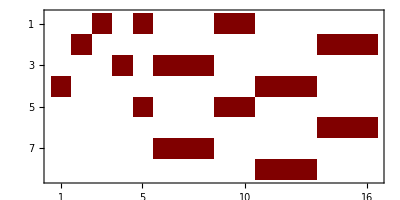

{mH2,s12,s14,s23,s35,s45,tr5}

Part::partd: Part specification AntiAndSymmetricTensorStructuresDecoupled⟦{2,3,5,9,10,14,15,16}⟧ is longer than depth of object.

$Aborted

Part::partd: Part specification AntiAndSymmetricTensorStructuresDecoupled⟦{1,4,6,7,8,11,12,13}⟧ is longer than depth of object.

$Aborted

```mathematica
(*Make some checks on the units: (+,+) should have MeV^4, (+,-) MeV^8*)
Refine[TTHUnitCheck[PhysicalCombinationFormFactors],Assumptions->{MeV>0}]//N;
%[[1;;4]]//Total//Total
%%[[5;;8]]//Total//Total

PhysicalCombinationFormFactors//MatrixPlot
PhysicalCombinationFormFactors//Variables

AntiAndSymmetricTensorStructuresDecoupled[[IndicesContributingToRL]]//TableForm;
AntiAndSymmetricTensorStructuresDecoupled[[IndicesContributingToLL]]//TableForm;
```

Save PhysicalCombinationFormFactors

```mathematica
PhysicalCombinationFormFactors=PhysicalCombinationFormFactors/.FivePointMandelstamReplacementsLorenzoForm/.{mt2->1,mt->1}/.RKinematicLorenzoSymmetricVars//EchoVars;
TTHDumpSafe["PhysicalCombinationFormFactors"]
```

Variables  {s12,s13,s14,s23,s24,s34,tr5}

#### One can ask whether the two remaining structures are independent from each other? -> Here I argue that they are independent

We can define a projector between the two objects in D = 4 in analogy to the projector which gave us the 16 from factors . The difference is only that we have only two different structures .

```mathematica
AntiTopSpinor4D=SpinorVBar[p4,SMP["m_t"]];
TopSpinor4D=SpinorU[p3,SMP["m_t"]];

SeperatedMinusAndPlusStructure1=AntiTopSpinor4D.(GS[p1].GS[p2]-GS[p2].GS[p1]).PL.TopSpinor4D;
SeperatedMinusAndPlusStructure2=AntiTopSpinor4D.(GS[p1].GS[p2]+GS[p2].GS[p1]).PL.TopSpinor4D;

SeperatedMinusAndPlusStructureBasis={SeperatedMinusAndPlusStructure1,SeperatedMinusAndPlusStructure2}//Contract;
SeperatedMinusAndPlusStructureBasisConjugated=ComplexConjugate@SeperatedMinusAndPlusStructureBasis;
```

Compute analogue of matrix M for two tensor structures

```mathematica
MMatrixAnalogueForTwoStructures=Table[DiracSimplify[FermionSpinSum[TensorI*TensorJ]],{TensorI,SeperatedMinusAndPlusStructureBasisConjugated},{TensorJ,SeperatedMinusAndPlusStructureBasis}]/.FivePointMandelstamReplacementsLorenzo/.FormToFeynCalcMasses;

(MMatrixAnalogueForTwoStructures//Det//Factor)/.{Eps[Momentum[p1],Momentum[p2],Momentum[p3],Momentum[p4]]-> GramSymmetricBasis/4}/.InverseReplacementGramSymmetrizedBasis/.FivePointMandelstamReplacementsLorenzo/.FeynCalcToFormMasses//FullSimplify
```

-(s(1,2))^2 (mt^8-2 s(1,4) mt^6-2 s(2,3) mt^6-4 (s(1,2))^2 mt^4+(s(1,4))^2 mt^4+(s(2,3))^2 mt^4-2 mh^2 s(1,2) mt^4-2 s(1,2) s(1,4) mt^4-2 s(1,2) s(2,3) mt^4+2 s(1,4) s(2,3) mt^4+4 s(1,2) s(3,5) mt^4+2 s(2,3) s(3,5) mt^4+4 s(1,2) s(4,5) mt^4+2 s(1,4) s(4,5) mt^4-2 s(3,5) s(4,5) mt^4+2 s(1,2) (s(1,4))^2 mt^2+2 s(1,2) (s(2,3))^2 mt^2+4 (s(1,2))^2 s(1,4) mt^2+2 mh^2 s(1,2) s(1,4) mt^2+4 (s(1,2))^2 s(2,3) mt^2+2 mh^2 s(1,2) s(2,3) mt^2+4 s(1,2) s(1,4) s(2,3) mt^2-2 (s(2,3))^2 s(3,5) mt^2-4 s(1,2) s(1,4) s(3,5) mt^2-4 s(1,2) s(2,3) s(3,5) mt^2-2 s(1,4) s(2,3) s(3,5) mt^2-2 (s(1,4))^2 s(4,5) mt^2-4 s(1,2) s(1,4) s(4,5) mt^2-4 s(1,2) s(2,3) s(4,5) mt^2-2 s(1,4) s(2,3) s(4,5) mt^2+2 s(1,4) s(3,5) s(4,5) mt^2+2 s(2,3) s(3,5) s(4,5) mt^2+mh^4 (s(1,2))^2+(s(1,2))^2 (s(1,4))^2+(s(1,2))^2 (s(2,3))^2+(s(2,3))^2 (s(3,5))^2+(s(1,4))^2 (s(4,5))^2+(s(3,5))^2 (s(4,5))^2-2 s(1,4) s(3,5) (s(4,5))^2+(mt^8-2 (s(1,4)+s(2,3)) mt^6+(-2 s(1,2) mh^2+(s(1,4))^2+(s(2,3))^2+2 s(1,4) s(2,3)+2 s(1,2) (s(1,4)+s(2,3))+2 s(2,3) s(3,5)+2 (s(1,4)-s(3,5)) s(4,5)) mt^4+2 (s(1,2) (s(1,4)+s(2,3)) mh^2-(s(1,4)+s(2,3)) (s(2,3) s(3,5)+(s(1,4)-s(3,5)) s(4,5))-s(1,2) ((s(1,4))^2+2 (s(4,5)-s(2,3)) s(1,4)+s(2,3) (s(2,3)+2 s(3,5)))) mt^2+mh^4 (s(1,2))^2+(s(1,2) (s(1,4)-s(2,3))+s(2,3) s(3,5))^2+(s(1,4)-s(3,5))^2 (s(4,5))^2+2 (s(2,3) (s(1,4)-s(3,5)) s(3,5)+s(1,2) (s(1,4) (s(2,3)-s(1,4))+(s(1,4)+s(2,3)) s(3,5))) s(4,5)-2 mh^2 s(1,2) (s(1,2) (s(1,4)+s(2,3))+s(1,4) (2 s(2,3)-s(4,5))+s(3,5) (s(4,5)-s(2,3))))^2-2 mh^2 (s(1,2))^2 s(1,4)-2 mh^2 (s(1,2))^2 s(2,3)-2 (s(1,2))^2 s(1,4) s(2,3)-4 mh^2 s(1,2) s(1,4) s(2,3)-2 s(1,2) (s(2,3))^2 s(3,5)+2 mh^2 s(1,2) s(2,3) s(3,5)+2 s(1,2) s(1,4) s(2,3) s(3,5)-2 s(1,2) (s(1,4))^2 s(4,5)-2 s(2,3) (s(3,5))^2 s(4,5)+2 mh^2 s(1,2) s(1,4) s(4,5)+2 s(1,2) s(1,4) s(2,3) s(4,5)-2 mh^2 s(1,2) s(3,5) s(4,5)+2 s(1,2) s(1,4) s(3,5) s(4,5)+2 s(1,2) s(2,3) s(3,5) s(4,5)+2 s(1,4) s(2,3) s(3,5) s(4,5))

```mathematica
SeperatedMinusAndPlusStructure2OrthogonalTo1=SeperatedMinusAndPlusStructureBasis[[2]]-DiracSimplify[FermionSpinSum[SeperatedMinusAndPlusStructureBasis[[2]]*SeperatedMinusAndPlusStructureBasisConjugated[[1]]]]/DiracSimplify[FermionSpinSum[SeperatedMinusAndPlusStructureBasis[[1]]SeperatedMinusAndPlusStructureBasisConjugated[[1]]]]*SeperatedMinusAndPlusStructureBasis[[1]]//FullSimplify
```

(φ(-OverBar[p4],m_t)).((γ̄·OverBar[p1]).(γ̄·OverBar[p2])+(γ̄·OverBar[p2]).(γ̄·OverBar[p1])).(γ̄)^7.(φ(OverBar[p3],m_t))+((-4 ⅈ (ϵ̄)^(OverBar[p1]OverBar[p2]OverBar[p3]OverBar[p4])+m_H^2 (s(2,3)-m_t^2)+(s(1,2)+s(1,5)) m_t^2+s(1,2) (s(1,5)-s(2,3)-s(3,4))-s(2,3) s(3,4)+(s(3,4)-s(1,5)) s(4,5)) (φ(-OverBar[p4],m_t)).((γ̄·OverBar[p1]).(γ̄·OverBar[p2])-(γ̄·OverBar[p2]).(γ̄·OverBar[p1])).(γ̄)^7.(φ(OverBar[p3],m_t)))/(2 m_H^2 (m_t^2-s(2,3))-2 (s(1,5)-2 s(2,3)+2 s(4,5)) m_t^2-(s(1,2)+2 s(2,3)) (-2 s(1,5)+2 s(2,3)+s(3,4))+2 (-s(1,5)+2 s(2,3)+s(3,4)) s(4,5))

```mathematica
CheckMyOrthogonalTensorStructureWithLorenzoDenominator=SeperatedMinusAndPlusStructure2OrthogonalTo1/.FivePointMandelstamReplacementsLorenzo/.FormToFeynCalcMasses//Together//Denominator
CheckMyOrthogonalTensorStructureWithLorenzoNumerator=((SeperatedMinusAndPlusStructure2OrthogonalTo1/.FivePointMandelstamReplacementsLorenzo/.FormToFeynCalcMasses//Together//Numerator//Simplify//Level[#,1]&)[[1]]//Level[#,1]&)[[2]]
```

s(1,2) m_H^2+2 s(1,4) m_t^2+2 s(2,3) m_t^2-(s(1,2))^2-2 s(1,2) s(1,4)-2 s(1,2) s(2,3)-4 s(1,4) s(2,3)+s(1,2) s(3,5)+2 s(2,3) s(3,5)+s(1,2) s(4,5)+2 s(1,4) s(4,5)-2 s(3,5) s(4,5)-2 m_t^4

s(1,2) m_H^2+2 (s(1,4)+s(2,3)) m_t^2-(s(1,2))^2-2 s(1,2) s(1,4)-2 s(1,2) s(2,3)-4 s(1,4) s(2,3)+s(1,2) s(3,5)+2 s(2,3) s(3,5)+s(1,2) s(4,5)+2 s(1,4) s(4,5)-2 s(3,5) s(4,5)-2 m_t^4

```mathematica
LorenzosResultDenominator=2*s23*s35-4*s23*s14-s45*s35+2*s45*s14+s12*mh^2-2*s12*s14-2*s12*s23-mt^2*s35+2*mt^2*s14+2*mt^2*s23-mt^2*s45+2*mt^2*s12-mt^4/.FormToFeynCalcMasses/.ConvertMandelstamFormToMathematica
LorenzosResultNumerator=-s23*s35+s45*s14-s12*s14+s12*s23+mt^2*s35-mt^2*s14+mt^2*s23-mt^2*s45+4*Eps[Momentum[p1],Momentum[p2],Momentum[p3],Momentum[p4]]/.FormToFeynCalcMasses/.ConvertMandelstamFormToMathematica
```

s(1,2) m_H^2+2 s(1,2) m_t^2+2 s(1,4) m_t^2+2 s(2,3) m_t^2-s(3,5) m_t^2-s(4,5) m_t^2-2 s(1,2) s(1,4)-2 s(1,2) s(2,3)-4 s(1,4) s(2,3)+2 s(2,3) s(3,5)+2 s(1,4) s(4,5)-s(3,5) s(4,5)-m_t^4

4 (ϵ̄)^(OverBar[p1]OverBar[p2]OverBar[p3]OverBar[p4])-s(1,4) m_t^2+s(2,3) m_t^2+s(3,5) m_t^2-s(4,5) m_t^2-s(1,2) s(1,4)+s(1,2) s(2,3)-s(2,3) s(3,5)+s(1,4) s(4,5)

```mathematica
LorenzosResultDenominator+CheckMyOrthogonalTensorStructureWithLorenzoDenominator
LorenzosResultNumerator-CheckMyOrthogonalTensorStructureWithLorenzoNumerator//Simplify
(*The difference in the Levi-Civita symbol is related to a form convention (which I did not yet understand)*)
```

0

(4+4 ⅈ) (ϵ̄)^(OverBar[p1]OverBar[p2]OverBar[p3]OverBar[p4])

```mathematica
SeperatedMinusAndPlusStructureOrthogonalBasis={SeperatedMinusAndPlusStructure1,SeperatedMinusAndPlusStructure2OrthogonalTo1}//Contract;
SeperatedMinusAndPlusStructureOrthogonalBasisConjugated=ComplexConjugate@SeperatedMinusAndPlusStructureOrthogonalBasis;

MMatrixAnalogueForTwoStructures=Table[DiracSimplify[FermionSpinSum[TensorI*TensorJ]],{TensorI,SeperatedMinusAndPlusStructureOrthogonalBasisConjugated},{TensorJ,SeperatedMinusAndPlusStructureOrthogonalBasis}]/.FivePointMandelstamReplacementsLorenzo/.FormToFeynCalcMasses;

MMatrixAnalogueForTwoStructures[[2]]/.FivePointMandelstamReplacementsLorenzo//FullSimplify
```

{0,(16 ((ϵ̄)^(OverBar[p1]OverBar[p2]OverBar[p3]OverBar[p4]))^2-2 s(1,2) m_H^2 (-(s(1,4)+s(2,3)) m_t^2+s(1,2) (s(1,4)+s(2,3))+s(2,3) (2 s(1,4)-s(3,5))+(s(3,5)-s(1,4)) s(4,5)+m_t^4)+(s(1,2))^2 m_H^4+m_t^2 (s(1,4)+s(2,3)-m_t^2) ((s(1,4)+s(2,3)) m_t^2+4 (s(1,2))^2-2 s(2,3) s(3,5)+2 (s(3,5)-s(1,4)) s(4,5)+2 s(1,2) (s(1,4)+s(2,3)-2 (s(3,5)+s(4,5)))-m_t^4)+(s(1,2) (s(1,4)-s(2,3))+s(2,3) s(3,5))^2+(s(1,4)-s(3,5))^2 (s(4,5))^2+2 (s(2,3) (s(1,4)-s(3,5)) s(3,5)+s(1,2) (s(1,4) (s(2,3)-s(1,4))+(s(1,4)+s(2,3)) s(3,5))) s(4,5))/(-s(1,2) m_H^2+m_t^2 (-2 s(1,2)-2 s(1,4)-2 s(2,3)+s(3,5)+s(4,5)+m_t^2)+2 s(1,2) (s(1,4)+s(2,3))+(2 s(1,4)-s(3,5)) (2 s(2,3)-s(4,5)))}

The two structures depend on each other in D = 4 if the matrix has rank 1 or equivalently a zero determinant

```mathematica
-(MMatrixAnalogueForTwoStructures//Det)/.{Eps[Momentum[p1],Momentum[p2],Momentum[p3],Momentum[p4]]-> I*√GramSymmetricBasis/4}/.InverseReplacementGramSymmetrizedBasis/.FivePointMandelstamReplacementsLorenzo/.FormToFeynCalcMasses//FullSimplify
```

4 s(1,2) m_t^2 (-(s(1,2)+s(1,4)+s(2,3)-s(3,5)-s(4,5)) m_t^2+(s(1,4))^2-s(3,5) s(1,4)+(s(2,3))^2+s(1,2) (s(1,4)+s(2,3))-s(2,3) s(4,5))

#### One can ask whether the two remaining structures are independent from each other? -> Here I argue that they are independent

We can define a projector between the two objects in D = 4 in analogy to the projector which gave us the 16 from factors . The difference is only that we have only two different structures .

```mathematica
AntiTopSpinor4D=SpinorVBar[p4,SMP["m_t"]];
TopSpinor4D=SpinorU[p3,SMP["m_t"]];

SeperatedMinusAndPlusStructure1=AntiTopSpinor4D.(GS[p1]-GS[p2]).PL.TopSpinor4D;
SeperatedMinusAndPlusStructure2=AntiTopSpinor4D.(GS[p1]+GS[p2]).PL.TopSpinor4D;

SeperatedMinusAndPlusStructureBasis={SeperatedMinusAndPlusStructure1,SeperatedMinusAndPlusStructure2}//Contract;
SeperatedMinusAndPlusStructureBasisConjugated=ComplexConjugate@SeperatedMinusAndPlusStructureBasis;
```

Compute analogue of matrix M for two tensor structures

```mathematica
MMatrixAnalogueForTwoStructures = Table[DiracSimplify[FermionSpinSum[TensorI*TensorJ]], {TensorI, SeperatedMinusAndPlusStructureBasisConjugated}, {TensorJ, SeperatedMinusAndPlusStructureBasis}] /. FivePointMandelstamReplacementsLorenzo /. FormToFeynCalcMasses;
```

```mathematica
SeperatedMinusAndPlusStructure2OrthogonalTo1=SeperatedMinusAndPlusStructureBasis[[1]]-DiracSimplify[FermionSpinSum[SeperatedMinusAndPlusStructureBasis[[1]]*SeperatedMinusAndPlusStructureBasisConjugated[[2]]]]/DiracSimplify[FermionSpinSum[SeperatedMinusAndPlusStructureBasis[[2]]SeperatedMinusAndPlusStructureBasisConjugated[[2]]]]*SeperatedMinusAndPlusStructureBasis[[2]]//FullSimplify
```

(φ(-OverBar[p4],m_t)).(γ̄·OverBar[p1]-γ̄·OverBar[p2]).(γ̄)^7.(φ(OverBar[p3],m_t))+((4 ⅈ (ϵ̄)^(OverBar[p1]OverBar[p2]OverBar[p3]OverBar[p4])-(s(1,2)+s(2,3)-s(4,5)) m_H^2+s(1,5) m_t^2-(2 s(2,3)+s(3,4)) m_t^2-s(4,5) (s(1,5)+s(4,5))+s(1,2) (s(1,5)-s(2,3)+s(4,5))+s(2,3) (s(3,4)+2 s(4,5))+m_t^4) (φ(-OverBar[p4],m_t)).(γ̄·OverBar[p1]+γ̄·OverBar[p2]).(γ̄)^7.(φ(OverBar[p3],m_t)))/(m_H^2 (s(1,2)-s(4,5)+m_t^2)-(s(1,2)+s(3,4)+2 s(4,5)) m_t^2+s(4,5) (-s(1,2)+s(3,4)+s(4,5))+m_t^4)

```mathematica
CheckMyOrthogonalTensorStructureWithLorenzoDenominator=SeperatedMinusAndPlusStructure2OrthogonalTo1/.FivePointMandelstamReplacementsLorenzo/.FormToFeynCalcMasses//Together//Denominator
CheckMyOrthogonalTensorStructureWithLorenzoNumerator=((SeperatedMinusAndPlusStructure2OrthogonalTo1/.FivePointMandelstamReplacementsLorenzo/.FormToFeynCalcMasses//Together//Numerator//Simplify//Level[#,1]&)[[1]]//Level[#,1]&)[[2]]
```

s(1,2) m_H^2-2 s(1,2) m_t^2+s(3,5) m_t^2+s(4,5) m_t^2-s(3,5) s(4,5)-m_t^4

4 ⅈ (ϵ̄)^(OverBar[p1]OverBar[p2]OverBar[p3]OverBar[p4])+(-s(1,4)+s(2,3)+s(3,5)-s(4,5)) m_t^2-s(1,2) s(1,4)+s(1,2) s(2,3)-s(2,3) s(3,5)+s(1,4) s(4,5)

```mathematica
LorenzosResultDenominator=-s45*s35+s12*mH^2+mt^2*s35+mt^2*s45-2*mt^2*s12-mt^4/.FormToFeynCalcMasses/.ConvertMandelstamFormToMathematica
LorenzosResultNumerator=-s23*s35+s45*s14-s12*s14+s12*s23+mt^2*s35-mt^2*s14+mt^2*s23-mt^2*s45+4*Eps[Momentum[p1],Momentum[p2],Momentum[p3],Momentum[p4]]/.FormToFeynCalcMasses/.ConvertMandelstamFormToMathematica
```

-2 s(1,2) m_t^2+s(3,5) m_t^2+s(4,5) m_t^2+mH^2 s(1,2)-s(3,5) s(4,5)-m_t^4

4 (ϵ̄)^(OverBar[p1]OverBar[p2]OverBar[p3]OverBar[p4])-s(1,4) m_t^2+s(2,3) m_t^2+s(3,5) m_t^2-s(4,5) m_t^2-s(1,2) s(1,4)+s(1,2) s(2,3)-s(2,3) s(3,5)+s(1,4) s(4,5)

```mathematica
LorenzosResultDenominator-CheckMyOrthogonalTensorStructureWithLorenzoDenominator
LorenzosResultNumerator-CheckMyOrthogonalTensorStructureWithLorenzoNumerator//Simplify
(*The difference in the Levi-Civita symbol is related to a form convention (which I did not yet understand)*)
```

mH^2 s(1,2)-s(1,2) m_H^2

(4-4 ⅈ) (ϵ̄)^(OverBar[p1]OverBar[p2]OverBar[p3]OverBar[p4])

(φ(-OverBar[p4],m_t)).(γ̄·OverBar[p1]-γ̄·OverBar[p2]).(γ̄)^7.(φ(OverBar[p3],m_t))+((4 ⅈ (ϵ̄)^(OverBar[p1]OverBar[p2]OverBar[p3]OverBar[p4])-(s(1,2)+s(2,3)-s(4,5)) m_H^2+s(1,5) m_t^2-(2 s(2,3)+s(3,4)) m_t^2-s(4,5) (s(1,5)+s(4,5))+s(1,2) (s(1,5)-s(2,3)+s(4,5))+s(2,3) (s(3,4)+2 s(4,5))+m_t^4) (φ(-OverBar[p4],m_t)).(γ̄·OverBar[p1]+γ̄·OverBar[p2]).(γ̄)^7.(φ(OverBar[p3],m_t)))/(m_H^2 (s(1,2)-s(4,5)+m_t^2)-(s(1,2)+s(3,4)+2 s(4,5)) m_t^2+s(4,5) (-s(1,2)+s(3,4)+s(4,5))+m_t^4)

```mathematica
SeperatedMinusAndPlusStructureOrthogonalBasis={SeperatedMinusAndPlusStructure1,SeperatedMinusAndPlusStructure2OrthogonalTo1}//Contract;
SeperatedMinusAndPlusStructureOrthogonalBasisConjugated=ComplexConjugate@SeperatedMinusAndPlusStructureOrthogonalBasis;

MMatrixAnalogueForTwoStructures=Table[DiracSimplify[FermionSpinSum[TensorI*TensorJ]],{TensorI,SeperatedMinusAndPlusStructureOrthogonalBasisConjugated},{TensorJ,SeperatedMinusAndPlusStructureOrthogonalBasis}]/.FivePointMandelstamReplacementsLorenzo/.FormToFeynCalcMasses;

MMatrixAnalogueForTwoStructures[[2]]/.FivePointMandelstamReplacementsLorenzo//FullSimplify
```

{0,(16 ((ϵ̄)^(OverBar[p1]OverBar[p2]OverBar[p3]OverBar[p4]))^2-2 s(1,2) m_H^2 (-(s(1,4)+s(2,3)) m_t^2+s(1,2) (s(1,4)+s(2,3))+s(2,3) (2 s(1,4)-s(3,5))+(s(3,5)-s(1,4)) s(4,5)+m_t^4)+(s(1,2))^2 m_H^4+m_t^2 (s(1,4)+s(2,3)-m_t^2) ((s(1,4)+s(2,3)) m_t^2+4 (s(1,2))^2-2 s(2,3) s(3,5)+2 (s(3,5)-s(1,4)) s(4,5)+2 s(1,2) (s(1,4)+s(2,3)-2 (s(3,5)+s(4,5)))-m_t^4)+(s(1,2) (s(1,4)-s(2,3))+s(2,3) s(3,5))^2+(s(1,4)-s(3,5))^2 (s(4,5))^2+2 (s(2,3) (s(1,4)-s(3,5)) s(3,5)+s(1,2) (s(1,4) (s(2,3)-s(1,4))+(s(1,4)+s(2,3)) s(3,5))) s(4,5))/(-s(1,2) m_H^2+m_t^2 (-2 s(1,2)-2 s(1,4)-2 s(2,3)+s(3,5)+s(4,5)+m_t^2)+2 s(1,2) (s(1,4)+s(2,3))+(2 s(1,4)-s(3,5)) (2 s(2,3)-s(4,5)))}

The two structures depend on each other in D = 4 if the matrix has rank 1 or equivalently a zero determinant

```mathematica
-(MMatrixAnalogueForTwoStructures//Det)/.{Eps[Momentum[p1],Momentum[p2],Momentum[p3],Momentum[p4]]-> I*√GramSymmetricBasis/4}/.InverseReplacementGramSymmetrizedBasis/.FivePointMandelstamReplacementsLorenzo/.FormToFeynCalcMasses//FullSimplify
```

4 s(1,2) m_t^2 (-(s(1,2)+s(1,4)+s(2,3)-s(3,5)-s(4,5)) m_t^2+(s(1,4))^2-s(3,5) s(1,4)+(s(2,3))^2+s(1,2) (s(1,4)+s(2,3))-s(2,3) s(4,5))

### Check + Safe Result

```mathematica
DumpGet["Output_Files/FormFactorsColStructure1SymmetrizedBasis.mx"]
DumpGet["Output_Files/FormFactorsColStructure2SymmetrizedBasis.mx"]
DumpGet[MathematicaInputPath<>"PhysicalCombinationFormFactors.mx"];
PhysicalCombinationFormFactors=PhysicalCombinationFormFactors/.{mh->√mH2,mt->√mt2}/.RKinematicLorenzoSymmetricVars/.mt2->1;
```

```mathematica
PhysicalTreeLevelAmplitude=PhysicalCombinationFormFactors.FormFactorsColStructure1SymmetrizedBasis(*/.FeynCalcToFormMasses/.ConvertMandelstamMathematicaToForm/.FivePointMandelstamReplacementsLorenzoForm/.mt->1*);
PhysicalTreeLevelAmplitudeParityEven=PhysicalTreeLevelAmplitude/.tr5->0//Factor;
PhysicalTreeLevelAmplitudeParityOdd=Coefficient[PhysicalTreeLevelAmplitude,tr5]//Factor;

Print["Even part free of Gram determinant: ", Not[MemberQ[Variables[PhysicalTreeLevelAmplitudeParityEven],GramSymmetricBasis]]]
```

Even part free of Gram determinant: True

```mathematica
Part1=(PhysicalTreeLevelAmplitudeParityEven+tr5*PhysicalTreeLevelAmplitudeParityOdd)*TATB;
```

```mathematica
PhysicalTreeLevelAmplitude=PhysicalCombinationFormFactors.FormFactorsColStructure2SymmetrizedBasis(*/.FeynCalcToFormMasses/.ConvertMandelstamMathematicaToForm/.FivePointMandelstamReplacementsLorenzoForm/.mt->1*);
PhysicalTreeLevelAmplitudeParityEven=PhysicalTreeLevelAmplitude/.tr5->0//Factor;
PhysicalTreeLevelAmplitudeParityOdd=Coefficient[PhysicalTreeLevelAmplitude,tr5]//Factor;

Print["Even part free of Gram determinant: ", Not[MemberQ[Variables[PhysicalTreeLevelAmplitudeParityEven],GramSymmetricBasis]]]
```

Even part free of Gram determinant: True

```mathematica
Part2=(PhysicalTreeLevelAmplitudeParityEven+tr5*PhysicalTreeLevelAmplitudeParityOdd)*TBTA;
```

```mathematica
TTHTreeLevelAmplitude=Part1+Part2/.ConvertMandelstamMathematicaToForm/.FivePointMandelstamReplacementsLorenzoForm/.{mt->1,mh->√mH2}/.RKinematicLorenzoSymmetricVars//EchoVars;
TTHTreeLevelAmplitude=Collect[TTHTreeLevelAmplitude,{TATB,TBTA},Factor];
TTHTreeLevelAmplitude//Dimensions
```

Variables  {s12,s13,s14,s23,s24,s34,TATB,TBTA,tr5}

```mathematica
DumpGet[MathematicaInputPath<>"TTHTreeLevelAmplitude.mx"]
```

```mathematica
SameVariablesQ[{TTHTreeLevelAmplitude,TTHTreeLevelAmplitude2},DebugModus->True]
TTHTreeLevelAmplitude/TTHTreeLevelAmplitude2//Together//Factor
```

True

{2 s12,2,2,2,2 s12,2,2,2}

```mathematica
TTHDumpSafe["TTHTreeLevelAmplitude"]
```

```mathematica
Print["Save matrix in FiniteFlow format"]
PhysicalCombinationFormFactors=PhysicalCombinationFormFactors/.ConvertMandelstamFormToMathematica/.FivePointMandelstamReplacementsLorenzo/.ConvertMandelstamMathematicaToForm//Together;
DumpSave[MathematicaInputPath<>"PhysicalCombinationFormFactors.mx",PhysicalCombinationFormFactors];
PhysicalCombinationFormFactors//MatrixPlot
```

Save matrix in FiniteFlow format

-Graphics-

## Compute matrix element squared from helicity amplitudes

### Definition of helicity amplitudes

The basis amplitudes are the (+, +, L, L), (+, -, L, L), (+, -, R, L) and the (+, +, R, L) configuration. The other ones can be obtained from parity transformations.

```mathematica
(*!!!!!!!!!!!!!!!I have to restore the other color structure!!!!!!!!!!*)
(*I have to be careful about the factor of the complex I which becomes important when I take the squared. It is hidden in the tr5 object.*)
TreeLevelAmplitudeGGToTTHPPRR=TreeLevelAmplitudeGGToTTHPPLL/.ReplacementPlaceHolderForSpinorStructures[PR];
TreeLevelAmplitudeGGToTTHMMRR=TreeLevelAmplitudeGGToTTHPPLL/.ReplacementPlaceHolderForSpinorStructures[PR]/.tr5->-tr5;
TreeLevelAmplitudeGGToTTHMMLL=TreeLevelAmplitudeGGToTTHPPLL/.ReplacementPlaceHolderForSpinorStructures[PL]/.tr5->-tr5;
TreeLevelAmplitudeGGToTTHPPLL=TreeLevelAmplitudeGGToTTHPPLL/.ReplacementPlaceHolderForSpinorStructures[PL];


TreeLevelAmplitudeGGToTTHPMRR=TreeLevelAmplitudeGGToTTHPMLL/.ReplacementPlaceHolderForSpinorStructures[PR];
TreeLevelAmplitudeGGToTTHMPRR=TreeLevelAmplitudeGGToTTHPMLL/.ReplacementPlaceHolderForSpinorStructures[PR]/.tr5->-tr5;
TreeLevelAmplitudeGGToTTHMPLL=TreeLevelAmplitudeGGToTTHPMLL/.ReplacementPlaceHolderForSpinorStructures[PL]/.tr5->-tr5;
TreeLevelAmplitudeGGToTTHPMLL=TreeLevelAmplitudeGGToTTHPMLL/.ReplacementPlaceHolderForSpinorStructures[PL];


TreeLevelAmplitudeGGToTTHPPLR=TreeLevelAmplitudeGGToTTHPPRL/.ReplacementPlaceHolderForSpinorStructures[PR];
TreeLevelAmplitudeGGToTTHMMLR=TreeLevelAmplitudeGGToTTHPPRL/.ReplacementPlaceHolderForSpinorStructures[PR]/.tr5->-tr5;
TreeLevelAmplitudeGGToTTHMMRL=TreeLevelAmplitudeGGToTTHPPRL/.ReplacementPlaceHolderForSpinorStructures[PL]/.tr5->-tr5;
TreeLevelAmplitudeGGToTTHPPRL=TreeLevelAmplitudeGGToTTHPPRL/.ReplacementPlaceHolderForSpinorStructures[PL];


TreeLevelAmplitudeGGToTTHPMLR=TreeLevelAmplitudeGGToTTHPMRL/.ReplacementPlaceHolderForSpinorStructures[PR];
TreeLevelAmplitudeGGToTTHMPLR=TreeLevelAmplitudeGGToTTHPMRL/.ReplacementPlaceHolderForSpinorStructures[PR]/.tr5->-tr5;
TreeLevelAmplitudeGGToTTHMPRL=TreeLevelAmplitudeGGToTTHPMRL/.ReplacementPlaceHolderForSpinorStructures[PL];/.tr5->-tr5;
TreeLevelAmplitudeGGToTTHPMRL=TreeLevelAmplitudeGGToTTHPMRL/.ReplacementPlaceHolderForSpinorStructures[PL];


HelicityConfigurations={
TreeLevelAmplitudeGGToTTHPPRR,TreeLevelAmplitudeGGToTTHPPRL,TreeLevelAmplitudeGGToTTHPPLR,TreeLevelAmplitudeGGToTTHPPLL,
TreeLevelAmplitudeGGToTTHMPRR,TreeLevelAmplitudeGGToTTHMPRL,TreeLevelAmplitudeGGToTTHMPLR,TreeLevelAmplitudeGGToTTHMPLL,
TreeLevelAmplitudeGGToTTHPMRR,TreeLevelAmplitudeGGToTTHPMRL,TreeLevelAmplitudeGGToTTHPMLR,TreeLevelAmplitudeGGToTTHPMLL,
TreeLevelAmplitudeGGToTTHMMRR,TreeLevelAmplitudeGGToTTHMMRL,TreeLevelAmplitudeGGToTTHMMLR,TreeLevelAmplitudeGGToTTHMMLL
}//Contract;
```

### Computation of squared helicity amplitude

```mathematica
Collect[DiracSimplify[FermionSpinSum[ComplexConjugate[HelicityConfigurations[[1]]]HelicityConfigurations[[1]]]]/.tr5^2->GramSymmetricBasis,{tr5},Factor]
```

1/(GramSymmetricBasis (mt^2-s(1,4))^2 (mt^2-s(2,3))^2 (mt^2-s(3,5))^2 (mt^2-s(4,5))^2)2 tr5 (s(1,2))^2 (-m_t^4 mt^12-4 (s(2,3))^2 mt^12-(s(4,5))^2 mt^12-s(1,2) m_H^2 mt^12-2 s(2,3) m_H^2 mt^12+s(4,5) m_H^2 mt^12+3267+2 mh^2 s(1,2) (s(1,4))^2 s(2,3) (s(3,5))^2 s(4,5)-3 mh^2 (s(1,2))^2 s(1,4) s(2,3) (s(3,5))^2 s(4,5)+4 mh^2 s(1,2) s(1,4) s(1,5) s(2,3) (s(3,5))^2 s(4,5)+s(1,2) (s(1,4))^3 s(3,4) (s(3,5))^2 s(4,5)-3 s(1,2) (s(1,4))^2 s(2,3) s(3,4) (s(3,5))^2 s(4,5)-mh^2 s(1,2) s(1,4) s(2,3) s(3,4) (s(3,5))^2 s(4,5)) mt^4+((s(1,2))^2 (13255+4 mh^2 5 s(4,5)-4 mh^2 (s(1,2))^2 (s(1,4))^2 (s(2,3))^2 s(3,4) s(3,5) s(4,5)-4 mh^4 (s(1,2))^2 s(1,4) (s(2,3))^2 s(3,4) s(3,5) s(4,5)) mt^4)/(GramSymmetricBasis (mt^2-s(1,4))^2 (mt^2-s(2,3))^2 (mt^2-s(3,5))^2 (mt^2-s(4,5))^2)
 |  |  |  |

## Checks and Code Attempts

## Analysis of color structures

```mathematica
ColMatrix=IdentityMatrix[3];

ColMatrix[[1,1]]=SUNSimplify[ SUNTrace[SUNT[a,b,b,a]],Explicit->True];
ColMatrix[[2,2]]=SUNSimplify[ SUNTrace[SUNT[b,a,a,b]],Explicit->True];
ColMatrix[[1,2]]=SUNSimplify[ SUNTrace[SUNT[a,b,a,b]],Explicit->True];
ColMatrix[[2,1]]=SUNSimplify[ SUNTrace[SUNT[b,a,b,a]],Explicit->True];

ColMatrix[[3,3]]=SUNSimplify[ SUNTrace[SUNT[c,e]SUNF[a,b,c]SUNF[a,b,e]],Explicit->True];
ColMatrix[[1,3]]=SUNSimplify[ SUNTrace[SUNT[a,b,c]SUNF[a,b,c]],Explicit->True];
ColMatrix[[3,1]]=SUNSimplify[ SUNTrace[SUNT[c,b,a]SUNF[a,b,c]],Explicit->True];
ColMatrix[[2,3]]=SUNSimplify[ SUNTrace[SUNT[b,a,c]SUNF[b,a,c]],Explicit->True];
ColMatrix[[3,2]]=SUNSimplify[ SUNTrace[SUNT[c,a,b]SUNF[b,a,c]],Explicit->True];

ColMatrix//MatrixForm

I*SUNSimplify[ColMatrix[[2,1]]-ColMatrix[[1,1]]]
```

(C_A C_F^2 | -C_F/2 | 1/2 ⅈ C_A^2 C_F
-C_F/2 | C_A C_F^2 | 1/2 ⅈ C_A^2 C_F
-1/2 ⅈ C_A^2 C_F | -1/2 ⅈ C_A^2 C_F | C_A^2 C_F)

-1/2 ⅈ C_A^2 C_F

## Reproducing Lorenzo' s projector (correct)

#### Lorenzo has a different choice of tensor structures for the projector . For simplicity I take his 16 :

```mathematica
(*The masses are there to bring each tensorstructure on the same dimension. In contrast to the previous definitions these tensor structures are defined in D = 4. *)
(*0 γ structures Projector:*)

eps1=ChangeDimension[PolarizationVector[p1,μ,Transversality-> True],4];
eps2=ChangeDimension[PolarizationVector[p2,ν,Transversality-> True],4];
TopSpinor=SpinorU[Momentum[p3,4],SMP["m_t"]];
AntiTopSpinor=SpinorVBar[Momentum[p4,4],SMP["m_t"]];

(*0 γ structures Projector:*)

T1D4=eps1 FV[p3,μ]eps2 FV[p3,ν]AntiTopSpinor.TopSpinor;
T2D4=eps1 FV[p3,μ]eps2 FV[p4,ν]AntiTopSpinor.TopSpinor;
T3D4=eps1 FV[p4,μ]eps2 FV[p3,ν]AntiTopSpinor.TopSpinor;
T4D4=eps1 FV[p4,μ]eps2 FV[p4,ν]AntiTopSpinor.TopSpinor;

(*1 γ structures Projector:*)

T5D4=eps1 FV[p3,μ]eps2 FV[p3,ν]AntiTopSpinor.GS[p1].TopSpinor;
T6D4=eps1 FV[p3,μ]eps2 FV[p4,ν]AntiTopSpinor.GS[p1].TopSpinor;
T7D4=eps1 FV[p4,μ]eps2 FV[p3,ν]AntiTopSpinor.GS[p1].TopSpinor;
T8D4=eps1 FV[p4,μ]eps2 FV[p4,ν]AntiTopSpinor.GS[p1].TopSpinor;

T9D4 =eps1 FV[p3,μ]eps2 FV[p3,ν]AntiTopSpinor.GS[p2].TopSpinor;
T10D4=eps1 FV[p3,μ]eps2 FV[p4,ν]AntiTopSpinor.GS[p2].TopSpinor;
T11D4=eps1 FV[p4,μ]eps2 FV[p3,ν]AntiTopSpinor.GS[p2].TopSpinor;
T12D4=eps1 FV[p4,μ]eps2 FV[p4,ν]AntiTopSpinor.GS[p2].TopSpinor;

(*2 γ structures Projector:*)

T13D4=eps1 FV[p3,μ]eps2 FV[p3,ν]AntiTopSpinor.GS[p1].GS[p2].TopSpinor;
T14D4=eps1 FV[p3,μ]eps2 FV[p4,ν]AntiTopSpinor.GS[p1].GS[p2].TopSpinor;
T15D4=eps1 FV[p4,μ]eps2 FV[p3,ν]AntiTopSpinor.GS[p1].GS[p2].TopSpinor;
T16D4=eps1 FV[p4,μ]eps2 FV[p4,ν]AntiTopSpinor.GS[p1].GS[p2].TopSpinor;



T1Lorenzo=SMP["m_t"]^2T1D4;
T2Lorenzo=SMP["m_t"]^2T2D4;
T3Lorenzo=SMP["m_t"]^2T3D4;
T4Lorenzo=SMP["m_t"]^2T4D4;

(*1 γ structures Projector:*)

T5Lorenzo=SMP["m_t"]T5D4;
T6Lorenzo=SMP["m_t"]T6D4;
T7Lorenzo=SMP["m_t"]T7D4;
T8Lorenzo=SMP["m_t"]T8D4;

T9Lorenzo  =SMP["m_t"]T9D4;
T10Lorenzo=SMP["m_t"]T10D4;
T11Lorenzo=SMP["m_t"]T11D4;
T12Lorenzo=SMP["m_t"]T12D4;

(*2 γ structures Projector:*)

(*The position of GSD[p1] and GSD[p2] are swapped compared to my choice*)
T13Lorenzo=eps1 FV[p3,μ]eps2 FV[p3,ν]AntiTopSpinor.GS[p2].GS[p1].TopSpinor;
T14Lorenzo=eps1 FV[p3,μ]eps2 FV[p4,ν]AntiTopSpinor.GS[p2].GS[p1].TopSpinor;
T15Lorenzo=eps1 FV[p4,μ]eps2 FV[p3,ν]AntiTopSpinor.GS[p2].GS[p1].TopSpinor;
T16Lorenzo=eps1 FV[p4,μ]eps2 FV[p4,ν]AntiTopSpinor.GS[p2].GS[p1].TopSpinor;

ProjectorTensorsLorenzo={T1Lorenzo,T2Lorenzo,T3Lorenzo,T4Lorenzo,T5Lorenzo,T6Lorenzo,T7Lorenzo,T8Lorenzo,T9Lorenzo,T10Lorenzo,T11Lorenzo,T12Lorenzo,T13Lorenzo,T14Lorenzo,T15Lorenzo, T16Lorenzo}//Contract;

ConjugatedProjectorTensorsLorenzo=ComplexConjugate[#]&/@ProjectorTensorsLorenzo;
```

#### Computing M matrix with Lorenzo' s tensor structures and choice of kinematic variables

```mathematica
(* We first set the 5 particle kinematics*)

FCClearScalarProducts[];
SetMandelstam[s,{p1,p2,p3,p4,p5},{0,0,SMP["m_t"],SMP["m_t"],SMP["m_H"]}];

MMatrixLorenzo=ComputeMMatrixForProjector[ProjectorTensorsLorenzo,ConjugatedProjectorTensorsLorenzo,{ReplacementRulesForKinematicVariablesOfMMatrix->FivePointMandelstamReplacementsLorenzo}];
```

#### Invert matrix with finite flow (takes some time)

```mathematica
VariablesForFiniteFlow={s[1,2],s[1,4],s[2,3],s[3,5],s[4,5], mh, mt};

FFNewGraph[ProjectorMatrixLorenzo, input, VariablesForFiniteFlow]

AuxVec1 = x/@Range[16];
AuxVec2 = t/@Range[16];


Print["Invert matrix..."];
FFAlgDenseSolver[ProjectorMatrixLorenzo,InverseMMatrixLorenzoNode ,{input},VariablesForFiniteFlow,
                 Table[MMatrixLorenzo[[i]].AuxVec1 - t[i] == 0 , {i, 1, 16}],
                 Flatten[{AuxVec1, AuxVec2}]]

FFSolverOnlyHomogeneous[ProjectorMatrixLorenzo,InverseMMatrixLorenzoNode]
FFGraphOutput[ProjectorMatrixLorenzo,InverseMMatrixLorenzoNode];
solverlearn = FFDenseSolverLearn[ProjectorMatrixLorenzo,Flatten[{AuxVec1, AuxVec2}] ];
```

True

Invert matrix...

True

```mathematica
GramDeterminatReplacementInverse={((mt^2)^4-2*s[3,5]*s[4,5]*(mt^2)^2+s[3,5]^2*s[4,5]^2-2*s[1,4]*(mt^2)^3+2*s[1,4]*s[4,5]*(mt^2)^2+2*s[1,4]*s[3,5]*s[4,5]*(mt^2)-2*s[1,4]*s[3,5]*s[4,5]^2+s[1,4]^2*(mt^2)^2-2*s[1,4]^2*s[4,5]*(mt^2)+s[1,4]^2*s[4,5]^2-2*s[2,3]*(mt^2)^3+2*s[2,3]*s[3,5]*(mt^2)^2+2*s[2,3]*s[3,5]*s[4,5]*(mt^2)-2*s[2,3]*s[3,5]^2*s[4,5]+2*s[2,3]*s[1,4]*(mt^2)^2-2*s[2,3]*s[1,4]*s[4,5]*(mt^2)-2*s[2,3]*s[1,4]*s[3,5]*(mt^2)+2*s[2,3]*s[1,4]*s[3,5]*s[4,5]+s[2,3]^2*(mt^2)^2-2*s[2,3]^2*s[3,5]*(mt^2)+s[2,3]^2*s[3,5]^2-2*s[1,2]*(mt^2)^2*(mh^2)-2*s[1,2]*s[3,5]*s[4,5]*(mh^2)+2*s[1,2]*s[1,4]*(mt^2)*(mh^2)+2*s[1,2]*s[1,4]*(mt^2)^2+2*s[1,2]*s[1,4]*s[4,5]*(mh^2)-4*s[1,2]*s[1,4]*s[4,5]*(mt^2)+2*s[1,2]*s[1,4]*s[3,5]*s[4,5]-2*s[1,2]*s[1,4]^2*(mt^2)-2*s[1,2]*s[1,4]^2*s[4,5]+2*s[1,2]*s[2,3]*(mt^2)*(mh^2)+2*s[1,2]*s[2,3]*(mt^2)^2+2*s[1,2]*s[2,3]*s[3,5]*(mh^2)-4*s[1,2]*s[2,3]*s[3,5]*(mt^2)+2*s[1,2]*s[2,3]*s[3,5]*s[4,5]-4*s[1,2]*s[2,3]*s[1,4]*(mh^2)+4*s[1,2]*s[2,3]*s[1,4]*(mt^2)+2*s[1,2]*s[2,3]*s[1,4]*s[4,5]+2*s[1,2]*s[2,3]*s[1,4]*s[3,5]-2*s[1,2]*s[2,3]^2*(mt^2)-2*s[1,2]*s[2,3]^2*s[3,5]+s[1,2]^2*(mh^2)^2-2*s[1,2]^2*s[1,4]*(mh^2)+s[1,2]^2*s[1,4]^2-2*s[1,2]^2*s[2,3]*(mh^2)-2*s[1,2]^2*s[2,3]*s[1,4]+s[1,2]^2*s[2,3]^2)->GRAM}
ProjectorMatrixLorenzosTensors=Factor[ArrayReshape[FFReconstructFunction[ProjectorMatrixLorenzo,VariablesForFiniteFlow],{16,16}]]/.GramDeterminatReplacementInverse;

SetDirectory[NotebookDirectory[]];
DumpSave["Output_Files/ProjectorMatrixLorenzosTensors.mx",ProjectorMatrixLorenzosTensors];
```

#### Comparison with Lorenzo' s result (correct)

```mathematica
Import["/home/philipp/Programs/FORM/Output_Files/Projector_Matrix_Lorenzos_Result.txt"]//ToExpression;
GramDeterminatReplacement=Import["/home/philipp/Programs/FORM/Output_Files/GRAM_determinant.txt"]//ToExpression;
DumpGet["/home/philipp/Programs/FORM/Output_Files/ProjectorMatrixLorenzosTensors.mx"];
```

Numeric test if equivalence (fast)

```mathematica
TestPoint=RandomKinematicReplacement[];
ProjectorMatrixOwnCalculationNumeric=ProjectorMatrixLorenzosTensors/.FormToFeynCalcMasses/.TestPoint;
ProjectorMatrixLorenzosResultNumeric=ProjectorMatrixLorenzosResult/.GramDeterminatReplacement/.FormToFeynCalcMasses/.TestPoint;
ProjectorMatrixOwnCalculationNumeric-ProjectorMatrixLorenzosResultNumeric//MatrixPlot
```

-Graphics-

Analytic test if equivalence (slower)

```mathematica
AnalyticTestOfEquivalence=(ProjectorMatrixLorenzosResult/.FormToFeynCalcMasses)-(ProjectorMatrixLorenzosTensors/.FormToFeynCalcMasses)//Simplify;
AnalyticTestOfEquivalence//MatrixPlot
```

-Graphics-

## Compare Lorenzo’s form factors with mine (correct)

### Comparison Lorenzo' s definition of the Gram determinant with mine (correct)

```mathematica
GRAMLorenzo=(mt2^4-2*s35*s45*mt2^2+s35^2*s45^2-2*s14*mt2^3+2*s14*s45*mt2^2+2*s14*s35*s45*mt2-2*s14*s35*s45^2+s14^2*mt2^2-2*s14^2*s45*mt2+s14^2*s45^2-2*s23*mt2^3+2*s23*s35*mt2^2+2*s23*s35*s45*mt2-2*s23*s35^2*s45+2*s23*s14*mt2^2-2*s23*s14*s45*mt2-2*s23*s14*s35*mt2+2*s23*s14*s35*s45+s23^2*mt2^2-2*s23^2*s35*mt2+s23^2*s35^2-2*s12*mt2^2*mh2-2*s12*s35*s45*mh2+2*s12*s14*mt2*mh2+2*s12*s14*mt2^2+2*s12*s14*s45*mh2-4*s12*s14*s45*mt2+2*s12*s14*s35*s45-2*s12*s14^2*mt2-2*s12*s14^2*s45+2*s12*s23*mt2*mh2+2*s12*s23*mt2^2+2*s12*s23*s35*mh2-4*s12*s23*s35*mt2+2*s12*s23*s35*s45-4*s12*s23*s14*mh2+4*s12*s23*s14*mt2+2*s12*s23*s14*s45+2*s12*s23*s14*s35-2*s12*s23^2*mt2-2*s12*s23^2*s35+s12^2*mh2^2-2*s12^2*s14*mh2+s12^2*s14^2-2*s12^2*s23*mh2-2*s12^2*s23*s14+s12^2*s23^2)/.ConvertMandelstamFormToMathematica/.FormToFeynCalcMasses;
```

```mathematica
Print["This should be 0 :"]
GRAMLorenzo-GramSymmetricBasis/.InverseReplacementGramSymmetrizedBasis/.FormToFeynCalcMasses
GRAM =GramSymmetricBasis;
```

This should be 0 :

0

```mathematica
Get["/home/philipp/Programs/FORM/Output_Files/Form_Factors_Tree_Level_GG_To_TTH_Lorenzo.m"]
```

```mathematica
(*Lorenzo uses the Yukawa coupling for the Higgs coupling to the top quark. I used the replacement yt -> -i_*1/2*gw/mw*mt. Later I have put i_ = 1, gw, mw = 1. That means to compare Lorenzo's result with mine I have to replace the Yukawa coupling with mt/2.*)
ReplacementFormFactorsTreeLevelLorenzosResult=FjtreeLorenzo/.FormToFeynCalcMasses/.ConvertMandelstamFormToMathematica/.{Den[x_]->1/x, Num[x_]->x}/.{yf->mt/2,g->1};
```

### Lorenzo uses a different ordering of the projector tensors

The first 8 tensors contribute to the LL or RR chirality configuration of the amplitude

LorenzosTensor1  -> MyTensor1
LorenzosTensor2  -> MyTensor6
LorenzosTensor3  -> MyTensor7
LorenzosTensor4  -> MyTensor8
LorenzosTensor5  -> MyTensor4
LorenzosTensor6  -> MyTensor11
LorenzosTensor7  -> MyTensor12
LorenzosTensor8  -> MyTensor13

The last 8 tensors contribute to the LR or RL chirality configuration of the amplitude

LorenzosTensor9  -> MyTensor2
LorenzosTensor10 -> MyTensor5
LorenzosTensor11 -> MyTensor9
LorenzosTensor12 -> MyTensor10
LorenzosTensor13 -> MyTensor3
LorenzosTensor14 -> MyTensor14
LorenzosTensor15 -> MyTensor15
LorenzosTensor16 -> MyTensor16

```mathematica
(*I divide by the global factor of I to make the comparision easier*)
FormFactorVectorLorenzosResult={F1,F9,F13,F5,F10,F2,F3,F4,F11,F12,F6,F7,F8,F14,F15,F16}/I;
```

### Extract form factors for color structure 1 and 2 and compare to my result (correct)

```mathematica
FormFactorsColStructure1SymmetrizedBasisLorenzosResult=Table[Coefficient[FormFactorLorenzo/.ReplacementFormFactorsTreeLevelLorenzosResult,T[a99,a97,j93,j95]],{FormFactorLorenzo,FormFactorVectorLorenzosResult }];

FormFactorsColStructure2SymmetrizedBasisLorenzosResult=Table[Coefficient[FormFactorLorenzo/.ReplacementFormFactorsTreeLevelLorenzosResult,T[a97,a99,j93,j95]],{FormFactorLorenzo,FormFactorVectorLorenzosResult }];
```

```mathematica
FormFactorsColStructure1SymmetrizedBasis-FormFactorsColStructure1SymmetrizedBasisLorenzosResult/.InverseReplacementGramSymmetrizedBasis/.FormToFeynCalcMasses//Factor
FormFactorsColStructure2SymmetrizedBasis-FormFactorsColStructure2SymmetrizedBasisLorenzosResult/.InverseReplacementGramSymmetrizedBasis/.FormToFeynCalcMasses//Factor
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

## Compare Lorenzo' s helicity amplitude with mine

### Load Lorenzo' s results

```mathematica
Get["/home/philipp/Programs/FORM/Output_Files/Helicity_Amplitudes_Lorenzo.m"]
GRAM=GramSymmetricBasis;

ReplaceBiVUs={BiVU[p4,p1,p2,p3]-BiVU[p4,p2,p1,p3]->SpinorP1P2MinusP2P1,BiVU[p4,p3]->SpinorVU,BiVU[p4,p1-p2,p3]->SpinorP1MinusP2,BiVU[p4,p1+p2,p3]->SpinorP1PlusP2};
ConversionLorenzosNotationToMine={yf->mt/2,g->1,Den[x_]->1/x,Num[x_]->x,e_[p4,p3,p1,p2]->-tr5};
```

### Comparison (+, +, R, L) helicity configuration

```mathematica
TreeLevelAmplitudeGGToTTHPPLLLorenzosResult=AmplPPLL/I/.ConversionLorenzosNotationToMine/.FormToFeynCalcMasses/.ConvertMandelstamFormToMathematica/.FeynCalcToFormMasses;

{TreeLevelAmplitudeGGToTTHPPLLColStructure1LorenzosResult,TreeLevelAmplitudeGGToTTHPPLLColStructure2LorenzosResult}=Coefficient[TreeLevelAmplitudeGGToTTHPPLLLorenzosResult,{T[a99,a97,j93,j95],T[a97,a99,j93,j95]}];

TreeLevelAmplitudeGGToTTHPPLLColStructure1LorenzosResult=TreeLevelAmplitudeGGToTTHPPLLColStructure1LorenzosResult/.ReplaceBiVUs;
```

```mathematica
(*I checked the variables are the same*)
test1=Coefficient[TreeLevelAmplitudeGGToTTHPPLLColStructure1LorenzosResult,{tr5*SpinorP1P2MinusP2P1,tr5*SpinorVU,SpinorP1P2MinusP2P1,SpinorVU}]/.tr5->0;
test2=Coefficient[TreeLevelAmplitudeGGToTTHPPRL,{tr5*SpinorP1P2MinusP2P1,tr5*SpinorVU,SpinorP1P2MinusP2P1,SpinorVU}]/.tr5->0;

test1/test2//Factor
(*/.{SpinorP1P2MinusP2P1->BiVU[p4,p1,p2,p3]-BiVU[p4,p2,p1,p3],SpinorVU->BiVU[p4,p3]};*)
```

{1/(s(1,2)),1/(s(1,2)),1/(s(1,2)),1/(s(1,2))}

### Comparison (+, +, L, L) helicity configuration

```mathematica
TreeLevelAmplitudeGGToTTHPPLRLorenzosResult=AmplPPLR/I/.ConversionLorenzosNotationToMine/.FormToFeynCalcMasses/.ConvertMandelstamFormToMathematica/.FeynCalcToFormMasses;

{TreeLevelAmplitudeGGToTTHPPLRColStructure1LorenzosResult,TreeLevelAmplitudeGGToTTHPPLRColStructure2LorenzosResult}=Coefficient[TreeLevelAmplitudeGGToTTHPPLRLorenzosResult,{T[a99,a97,j93,j95],T[a97,a99,j93,j95]}];
```

```mathematica
TreeLevelAmplitudeGGToTTHPPLRColStructure1LorenzosResult=TreeLevelAmplitudeGGToTTHPPLRColStructure1LorenzosResult/.ReplaceBiVUs;


test1=Coefficient[TreeLevelAmplitudeGGToTTHPPLRColStructure1LorenzosResult,{tr5*SpinorP1MinusP2,tr5*SpinorP1PlusP2,SpinorP1MinusP2,SpinorP1PlusP2}]/.tr5->0;
test2=Coefficient[TreeLevelAmplitudeGGToTTHPPLL,{tr5*SpinorP1MinusP2,tr5*SpinorP1PlusP2,SpinorP1MinusP2,SpinorP1PlusP2}]/.tr5->0;

test1/test2//Factor
```

{1/(s(1,2)),1/(s(1,2)),1/(s(1,2)),1/(s(1,2))}

### Comparison (+, -, L, L) helicity configuration

```mathematica
TreeLevelAmplitudeGGToTTHPMLRLorenzosResult=AmplPMLR/I/.ConversionLorenzosNotationToMine/.FormToFeynCalcMasses/.ConvertMandelstamFormToMathematica/.FeynCalcToFormMasses;

{TreeLevelAmplitudeGGToTTHPMLRColStructure1LorenzosResult,TreeLevelAmplitudeGGToTTHPMLRColStructure2LorenzosResult}=Coefficient[TreeLevelAmplitudeGGToTTHPMLRLorenzosResult,{T[a99,a97,j93,j95],T[a97,a99,j93,j95]}]/.ReplaceBiVUs;
```

```mathematica
test1=Coefficient[TreeLevelAmplitudeGGToTTHPMLRColStructure1LorenzosResult,{tr5*SpinorP1MinusP2,tr5*SpinorP1PlusP2,SpinorP1MinusP2,SpinorP1PlusP2}]/.tr5->0;
test2=Coefficient[TreeLevelAmplitudeGGToTTHPMLL,{tr5*SpinorP1MinusP2,tr5*SpinorP1PlusP2,SpinorP1MinusP2,SpinorP1PlusP2}]/.tr5->0;

test1/test2//Factor
```

{1,1,1,1}

### Comparison (+, -, R, L) helicity configuration

```mathematica
TreeLevelAmplitudeGGToTTHPMLLLorenzosResult=AmplPMLL/I/.ConversionLorenzosNotationToMine/.FormToFeynCalcMasses/.ConvertMandelstamFormToMathematica/.FeynCalcToFormMasses;

{TreeLevelAmplitudeGGToTTHPMLLColStructure1LorenzosResult,TreeLevelAmplitudeGGToTTHPMLLColStructure2LorenzosResult}=Coefficient[TreeLevelAmplitudeGGToTTHPMLLLorenzosResult,{T[a99,a97,j93,j95],T[a97,a99,j93,j95]}]/.ReplaceBiVUs;
```

```mathematica
test1=Coefficient[TreeLevelAmplitudeGGToTTHPMLLColStructure1LorenzosResult,{tr5*SpinorP1P2MinusP2P1,tr5*SpinorVU,SpinorP1P2MinusP2P1,SpinorVU}]/.tr5->0;
test2=Coefficient[TreeLevelAmplitudeGGToTTHPMRL,{tr5*SpinorP1P2MinusP2P1,tr5*SpinorVU,SpinorP1P2MinusP2P1,SpinorVU}]/.tr5->0;
test1/test2//Factor
```

{1,1,1,1}

```mathematica
DiracEquation
```

# One Loop Computation

## Form part

## Replacement of scalar products involving loop momenta

### Definition of integral families

```mathematica
LoopMomentaGGToTTH={k1};
ExternalMomentaGGToTTH={p1,p2,p3,p4};
MassesOfExternalMomentaGGToTTH={0,0,mt,mt,mh};

InversePropagatorsIntegralFamilyA=
{
k1^2-mt^2,
(k1+p4)^2,
(k1+p2+p4)^2,
(k1+p1+p2+p4)^2,
(k1+p1+p2+p3+p4)^2-mt^2
};

InversePropagatorsIntegralFamilyB=
{
k1^2-mt^2,
(k1+p2)^2-mt^2,
(k1+p2+p4)^2,
(k1+p1+p2+p4)^2,
(k1+p1+p2+p3+p4)^2-mt^2
};

InversePropagatorsIntegralFamilyC=
{
k1^2-mt^2,
(k1+p1)^2-mt^2,
(k1+p1+p2)^2-mt^2,
(k1+p1+p2+p4)^2,
(k1+p1+p2+p3+p4)^2-mt^2
};

InversePropagatorsIntegralFamilyD=
{
k1^2-mt^2,
(k1+p2)^2-mt^2,
(k1+p2+p4)^2,
(k1+p2+p3+p4)^2-mt^2,
(k1+p1+p2+p3+p4)^2-mt^2
};

DefinitionInversePropagatorFamiliesAndNames=
{
{InversePropagatorsIntegralFamilyA,"PentaboxGGtoTTHTopologyA"},
{InversePropagatorsIntegralFamilyA/.{p1->p1Dummy,p2->p2Dummy}/.{p1Dummy->p2,p2Dummy->p1},"PentaboxGGtoTTHTopologyAx12"},

{InversePropagatorsIntegralFamilyB,"PentaboxGGtoTTHTopologyB"},
{InversePropagatorsIntegralFamilyB/.{p1->p1Dummy,p2->p2Dummy}/.{p1Dummy->p2,p2Dummy->p1},"PentaboxGGtoTTHTopologyBx12"},
{InversePropagatorsIntegralFamilyB/.{p3->p3Dummy,p4->p4Dummy}/.{p3Dummy->p4,p4Dummy->p3},"PentaboxGGtoTTHTopologyBx34"},
{InversePropagatorsIntegralFamilyB/.{p1->p1Dummy,p2->p2Dummy,p3->p3Dummy,p4->p4Dummy}/.{p1Dummy->p2,p2Dummy->p1,p3Dummy->p4,p4Dummy->p3},"PentaboxGGtoTTHTopologyBx12x34"},

{InversePropagatorsIntegralFamilyC,"PentaboxGGtoTTHTopologyC"},
{InversePropagatorsIntegralFamilyC/.{p1->p1Dummy,p2->p2Dummy}/.{p1Dummy->p2,p2Dummy->p1},"PentaboxGGtoTTHTopologyCx12"},
{InversePropagatorsIntegralFamilyC/.{p3->p3Dummy,p4->p4Dummy}/.{p3Dummy->p4,p4Dummy->p3},"PentaboxGGtoTTHTopologyCx34"},
{InversePropagatorsIntegralFamilyC/.{p1->p1Dummy,p2->p2Dummy,p3->p3Dummy,p4->p4Dummy}/.{p1Dummy->p2,p2Dummy->p1,p3Dummy->p4,p4Dummy->p3},"PentaboxGGtoTTHTopologyCx12x34"},

{InversePropagatorsIntegralFamilyD,"PentaboxGGtoTTHTopologyD"},
{InversePropagatorsIntegralFamilyD/.{p1->p1Dummy,p2->p2Dummy}/.{p1Dummy->p2,p2Dummy->p1},"PentaboxGGtoTTHTopologyDx12"}

};

PreventFoldOutput[]
```

### Write Form code

```mathematica
SetDirectory[NotebookDirectory[]<>"Modules_One_Loop_Calculation/"];

ExternalMomentaGGToTTHFormNames=ExternalMomentaGGToTTH/.{k1->veck1,p1->vecp1,p2-> vecp2,p3-> vecp3,p4-> vecp4};
LoopMomentaFormNames=LoopMomentaGGToTTH/.{k1->veck1,p1->vecp1,p2-> vecp2,p3-> vecp3,p4-> vecp4};
DefinitionInversePropagatorFamiliesAndNamesFormNames=DefinitionInversePropagatorFamiliesAndNames/.{k1->veck1,p1->vecp1,p2-> vecp2,p3-> vecp3,p4-> vecp4};

ReplacementMomentaWithMandelstams=ReplaceExternalMomentaScalarProductsWithMandelstams[ExternalMomentaGGToTTHFormNames,MassesOfExternalMomentaGGToTTH]/.FivePointMandelstamReplacementsLorenzo/.ConvertMandelstamMathematicaToForm;

WriteFormCodeReplacementScalarProductsWithInversePropagators[LoopMomentaFormNames,ExternalMomentaGGToTTHFormNames[[1;;4]],DefinitionInversePropagatorFamiliesAndNamesFormNames[[All,1]],DefinitionInversePropagatorFamiliesAndNamesFormNames[[All,2]],"Replace_Loop_Momenta_with_Inverse_Propagators.h",KineamticReplacementOfMomenta->ReplacementMomentaWithMandelstams];
SetDirectory[NotebookDirectory[]];
```

Number of topopologies: 12

Write Form module into: /home/philipp/Programs/FORM/Modules_One_Loop_CalculationReplace_Loop_Momenta_with_Inverse_Propagators.h

## Create Form File for replacements of integral topologies with Integral and powers of propagators

```mathematica
RewriteSectorsAsIntegralFunctionsForm[5, NotebookDirectory[]<>"OneLoopCalculation/Modules_One_Loop_Calculation/"<>"Replace_Sector_IDs_with_Integral_Powers_413232.h"]
```

## Finite Flow part

## Definitions

```mathematica
(*This section takes place entirely in this directory*)
SetDirectory[NotebookDirectory[]<>"Mathematica_Modules/Input_Files"];
```

### Kinematic coefficients (sum)/ Vector of Integrals (kinematic variables are not correct yet)

Form is able to sum all diagrams and simplify the result . The cancellations are large and do not take too long -> use Sum of all diagrams

#### Functions

```mathematica
GetSUNCoefficients[expression_]:=Module[

{NumSplittedInSUN,DenomSplittedInSUN},

NumSplittedInSUN=CoefficientList[Numerator[expression],SUN,5];
DenomSplittedInSUN=CoefficientList[Denominator[expression],SUN];

If[Length[DenomSplittedInSUN]==2&&DenomSplittedInSUN[[1]]==0, Return[Flatten[{(NumSplittedInSUN*{1/SUN,1,SUN,SUN^2,SUN^3})/DenomSplittedInSUN[[2]] ,0}]]];
If[Length[DenomSplittedInSUN]==1,  Return[Flatten[{0,(NumSplittedInSUN(*{1,SUN,SUN^2,SUN^3,SUN^4}*))/DenomSplittedInSUN[[1]] }]]];


Print["Error: Denominator structure is not of uniform degree 0 or 1 in SUN."];
Abort[]
]
```

#### Get kinematic matrix for Finite Flow

```mathematica
SetDirectory[NotebookDirectory[]<>"Mathematica_Modules/Input_Files"];
```

Load and convert form file

```mathematica
Get[MathematicaInputPath<>"Full_Simplified_Sum_Of_All_Diagrams.m"];
(*This only works if FeynCalc is not loaded.*)
SumOfAllDiagramsConverted=ConvertFormExpression[#/.{gs->1,gY->1},ReduzeToKira->True]&/@SumOfAllDiagrams;
Clear[SumOfAllDiagrams];
```

Extract integral coefficients

```mathematica
VectorOfIntegrals=SelectIntegrals[Variables[SumOfAllDiagramsConverted],IntegralSymbol->"Pentabox"];
NbOfIntegrals=VectorOfIntegrals//Length;

(*This is a list of all 1 loop integrals*)
DumpSave["VectorOfIntegrals.mx", VectorOfIntegrals];

KinematicCoefficientMatrix=Coefficient[#,VectorOfIntegrals]&/@SumOfAllDiagramsConverted;
Clear[SumOfAllDiagramsConverted];
```

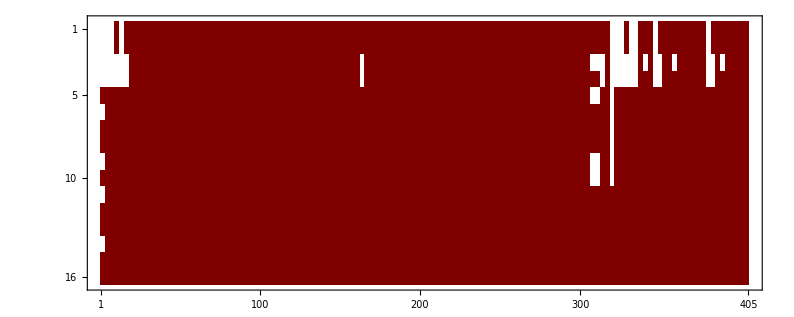

```mathematica
KinematicCoefficientMatrix//MatrixPlot
```

Extract matrix for ColFactor1, split Nf, SUN

```mathematica
(*There can be maximal 1 closed massless quark loop -> degree(Nf)<= 1 *)

KinematicCoefficientMatrixColFactor1SplitNf=CoefficientList[KinematicCoefficientMatrix/.{ColFactor1->1,ColFactor2->0,ColFactor3->0},Nf,2]//Together;
```

```mathematica
KinematicCoefficientMatrixColFactor1SplitNfSUNFiniteFlow=Table[GetSUNCoefficients[KinematicCoefficientMatrixColFactor1SplitNf[[FormFactorNb,IntegralNb,NfPower]]],{FormFactorNb,16},{IntegralNb,NbOfIntegrals},{NfPower,2}];
DumpSave[MathematicaInputPath<>"KinematicCoefficientMatrixColFactor1SplitNfSUNFiniteFlow.mx",KinematicCoefficientMatrixColFactor1SplitNfSUNFiniteFlow];

(*Clear[KinematicCoefficientMatrixColFactor1FiniteFlow,KinematicCoefficientMatrixColFactor1FiniteFlowSUNSplit]*)
```

```mathematica
Options[MaxDegreeOfSymbolInExpression]={FullPolynomalDegree->False, OnlyMaxDegree->False};
MaxDegreeOfSymbolInExpression[RegularExpression_, NameOfSymbol_ ,optn:OptionsPattern[{FullPolynomalDegree->False,OnlyMaxDegree->False}]]:=Module[

{DegreesOfSymbol},

If[OptionValue[FullPolynomalDegree],Return[Max[Total@*First/@CoefficientRules[RegularExpression]]]];

DegreesOfSymbol=Total@*First/@CoefficientRules[RegularExpression,NameOfSymbol];
If[OptionValue[OnlyMaxDegree],Return[Max[DegreesOfSymbol]]];
Return[DegreesOfSymbol]
];
```

Extract matrix for ColFactor2, split Nf, SUN

```mathematica
(*There can be maximal 1 closed massless quark loop -> degree(Nf)<= 1 *)

KinematicCoefficientMatrixColFactor2SplitNf=CoefficientList[KinematicCoefficientMatrix/.{ColFactor1->0,ColFactor2->1,ColFactor3->0},Nf,2]//Together;
(*DumpSave["KinematicCoefficientMatrixColFactor1SplitNf.mx",KinematicCoefficientMatrixColFactor1SplitNf];*)

KinematicCoefficientMatrixColFactor2SplitNfSUNFiniteFlow=Table[GetSUNCoefficients[KinematicCoefficientMatrixColFactor2SplitNf[[FormFactorNb,IntegralNb,NfPower]]],{FormFactorNb,16},{IntegralNb,NbOfIntegrals},{NfPower,2}];
DumpSave[MathematicaInputPath<>"KinematicCoefficientMatrixColFactor2SplitNfSUNFiniteFlow.mx",KinematicCoefficientMatrixColFactor2SplitNfSUNFiniteFlow];

(*Clear[KinematicCoefficientMatrixColFactor1FiniteFlow,KinematicCoefficientMatrixColFactor1FiniteFlowSUNSplit]*)
```

Extract matrix for ColFactor3, split Nf, SUN

```mathematica
(*There can be maximal 1 closed massless quark loop -> degree(Nf)<= 1 *)

KinematicCoefficientMatrixColFactor3SplitNf=CoefficientList[KinematicCoefficientMatrix/.{ColFactor1->0,ColFactor2->0,ColFactor3->1},Nf,2]//Together;
(*DumpSave["KinematicCoefficientMatrixColFactor1SplitNf.mx",KinematicCoefficientMatrixColFactor1SplitNf];*)

KinematicCoefficientMatrixColFactor3SplitNfSUNFiniteFlow=Table[GetSUNCoefficients[KinematicCoefficientMatrixColFactor3SplitNf[[FormFactorNb,IntegralNb,NfPower]]],{FormFactorNb,16},{IntegralNb,NbOfIntegrals},{NfPower,2}];
DumpSave[MathematicaInputPath<>"KinematicCoefficientMatrixColFactor3SplitNfSUNFiniteFlow.mx",KinematicCoefficientMatrixColFactor3SplitNfSUNFiniteFlow];
```

MatrixPlot of coefficients

ColFactor1: N_f^0, SUN^-1:

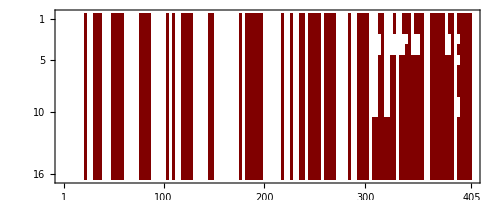

ColFactor1: N_f^0, SUN^0:

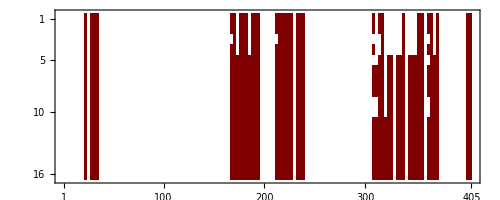

ColFactor1: N_f^0, SUN^1:

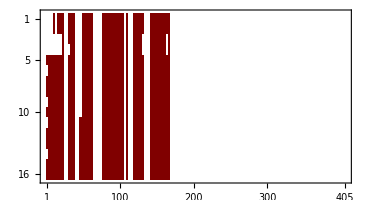

ColFactor1: N_f^0, SUN^2:

-Graphics-

ColFactor1: N_f^0, SUN^3:

-Graphics-

ColFactor1: N_f^0, SUN^4:

-Graphics-

ColFactor2: N_f^1, SUN^-1:

-Graphics-

ColFactor2: N_f^1, SUN^0:

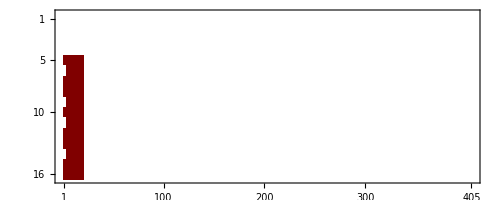

ColFactor2: N_f^1, SUN^1:

-Graphics-

ColFactor2: N_f^1, SUN^2:

-Graphics-

ColFactor2: N_f^1, SUN^3:

-Graphics-

ColFactor2: N_f^1, SUN^4:

-Graphics-

ColFactor2: N_f^0, SUN^-1:

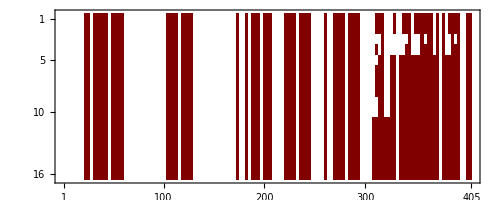

ColFactor2: N_f^0, SUN^0:

-Graphics-

ColFactor2: N_f^0, SUN^1:

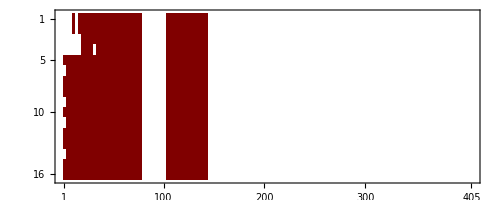

ColFactor2: N_f^0, SUN^2:

-Graphics-

ColFactor2: N_f^0, SUN^3:

-Graphics-

ColFactor2: N_f^0, SUN^4:

-Graphics-

ColFactor2: N_f^1, SUN^-1:

-Graphics-

ColFactor2: N_f^1, SUN^0:

-Graphics-

ColFactor2: N_f^1, SUN^1:

-Graphics-

ColFactor2: N_f^1, SUN^2:

-Graphics-

ColFactor2: N_f^1, SUN^3:

-Graphics-

ColFactor2: N_f^1, SUN^4:

-Graphics-

ColFactor3: N_f^0, SUN^-1:

-Graphics-

ColFactor3: N_f^0, SUN^0:

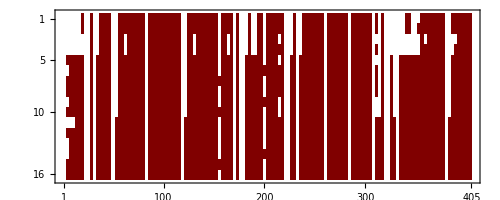

ColFactor3: N_f^0, SUN^1:

-Graphics-

ColFactor3: N_f^0, SUN^2:

-Graphics-

ColFactor3: N_f^0, SUN^3:

-Graphics-

ColFactor3: N_f^0, SUN^4:

-Graphics-

ColFactor3: N_f^1, SUN^-1:

-Graphics-

ColFactor3: N_f^1, SUN^0:

-Graphics-

ColFactor3: N_f^1, SUN^1:

-Graphics-

ColFactor3: N_f^1, SUN^2:

-Graphics-

ColFactor3: N_f^1, SUN^3:

-Graphics-

ColFactor3: N_f^1, SUN^4:

-Graphics-

```mathematica
Print["ColFactor1: N_f^0, SUN^-1: "]
KinematicCoefficientMatrixColFactor1SplitNfSUNFiniteFlow[[;;,;;,1,1]]//MatrixPlot
Print["ColFactor1: N_f^0, SUN^0: "]
KinematicCoefficientMatrixColFactor1SplitNfSUNFiniteFlow[[;;,;;,1,2]]//MatrixPlot
Print["ColFactor1: N_f^0, SUN^1: "]
KinematicCoefficientMatrixColFactor1SplitNfSUNFiniteFlow[[;;,;;,1,3]]//MatrixPlot
Print["ColFactor1: N_f^0, SUN^2: "]
KinematicCoefficientMatrixColFactor1SplitNfSUNFiniteFlow[[;;,;;,1,4]]//MatrixPlot
Print["ColFactor1: N_f^0, SUN^3: "]
KinematicCoefficientMatrixColFactor1SplitNfSUNFiniteFlow[[;;,;;,1,5]]//MatrixPlot
Print["ColFactor1: N_f^0, SUN^4: "]
KinematicCoefficientMatrixColFactor1SplitNfSUNFiniteFlow[[;;,;;,1,6]]//MatrixPlot

Print["ColFactor1: N_f^1, SUN^-1: "]
KinematicCoefficientMatrixColFactor1SplitNfSUNFiniteFlow[[;;,;;,2,1]]//MatrixPlot
Print["ColFactor1: N_f^1, SUN^0: "]
KinematicCoefficientMatrixColFactor1SplitNfSUNFiniteFlow[[;;,;;,2,2]]//MatrixPlot
Print["ColFactor1: N_f^1, SUN^1: "]
KinematicCoefficientMatrixColFactor1SplitNfSUNFiniteFlow[[;;,;;,2,3]]//MatrixPlot
Print["ColFactor1: N_f^1, SUN^2: "]
KinematicCoefficientMatrixColFactor1SplitNfSUNFiniteFlow[[;;,;;,2,4]]//MatrixPlot
Print["ColFactor1: N_f^1, SUN^3: "]
KinematicCoefficientMatrixColFactor1SplitNfSUNFiniteFlow[[;;,;;,2,5]]//MatrixPlot
Print["ColFactor1: N_f^1, SUN^4: "]
KinematicCoefficientMatrixColFactor1SplitNfSUNFiniteFlow[[;;,;;,2,6]]//MatrixPlot

Print["ColFactor2: N_f^0, SUN^-1: "]
KinematicCoefficientMatrixColFactor2SplitNfSUNFiniteFlow[[;;,;;,1,1]]//MatrixPlot
Print["ColFactor2: N_f^0, SUN^0: "]
KinematicCoefficientMatrixColFactor2SplitNfSUNFiniteFlow[[;;,;;,1,2]]//MatrixPlot
Print["ColFactor2: N_f^0, SUN^1: "]
KinematicCoefficientMatrixColFactor2SplitNfSUNFiniteFlow[[;;,;;,1,3]]//MatrixPlot
Print["ColFactor2: N_f^0, SUN^2: "]
KinematicCoefficientMatrixColFactor2SplitNfSUNFiniteFlow[[;;,;;,1,4]]//MatrixPlot
Print["ColFactor2: N_f^0, SUN^3: "]
KinematicCoefficientMatrixColFactor2SplitNfSUNFiniteFlow[[;;,;;,1,5]]//MatrixPlot
Print["ColFactor2: N_f^0, SUN^4: "]
KinematicCoefficientMatrixColFactor2SplitNfSUNFiniteFlow[[;;,;;,1,6]]//MatrixPlot

Print["ColFactor2: N_f^1, SUN^-1: "]
KinematicCoefficientMatrixColFactor2SplitNfSUNFiniteFlow[[;;,;;,2,1]]//MatrixPlot
Print["ColFactor2: N_f^1, SUN^0: "]
KinematicCoefficientMatrixColFactor2SplitNfSUNFiniteFlow[[;;,;;,2,2]]//MatrixPlot
Print["ColFactor2: N_f^1, SUN^1: "]
KinematicCoefficientMatrixColFactor2SplitNfSUNFiniteFlow[[;;,;;,2,3]]//MatrixPlot
Print["ColFactor2: N_f^1, SUN^2: "]
KinematicCoefficientMatrixColFactor2SplitNfSUNFiniteFlow[[;;,;;,2,4]]//MatrixPlot
Print["ColFactor2: N_f^1, SUN^3: "]
KinematicCoefficientMatrixColFactor2SplitNfSUNFiniteFlow[[;;,;;,2,5]]//MatrixPlot
Print["ColFactor2: N_f^1, SUN^4: "]
KinematicCoefficientMatrixColFactor2SplitNfSUNFiniteFlow[[;;,;;,2,6]]//MatrixPlot

Print["ColFactor3: N_f^0, SUN^-1: "]
KinematicCoefficientMatrixColFactor3SplitNfSUNFiniteFlow[[;;,;;,1,1]]//MatrixPlot
Print["ColFactor3: N_f^0, SUN^0: "]
KinematicCoefficientMatrixColFactor3SplitNfSUNFiniteFlow[[;;,;;,1,2]]//MatrixPlot
Print["ColFactor3: N_f^0, SUN^1: "]
KinematicCoefficientMatrixColFactor3SplitNfSUNFiniteFlow[[;;,;;,1,3]]//MatrixPlot
Print["ColFactor3: N_f^0, SUN^2: "]
KinematicCoefficientMatrixColFactor3SplitNfSUNFiniteFlow[[;;,;;,1,4]]//MatrixPlot
Print["ColFactor3: N_f^0, SUN^3: "]
KinematicCoefficientMatrixColFactor3SplitNfSUNFiniteFlow[[;;,;;,1,5]]//MatrixPlot
Print["ColFactor3: N_f^0, SUN^4: "]
KinematicCoefficientMatrixColFactor3SplitNfSUNFiniteFlow[[;;,;;,1,6]]//MatrixPlot

Print["ColFactor3: N_f^1, SUN^-1: "]
KinematicCoefficientMatrixColFactor3SplitNfSUNFiniteFlow[[;;,;;,2,1]]//MatrixPlot
Print["ColFactor3: N_f^1, SUN^0: "]
KinematicCoefficientMatrixColFactor3SplitNfSUNFiniteFlow[[;;,;;,2,2]]//MatrixPlot
Print["ColFactor3: N_f^1, SUN^1: "]
KinematicCoefficientMatrixColFactor3SplitNfSUNFiniteFlow[[;;,;;,2,3]]//MatrixPlot
Print["ColFactor3: N_f^1, SUN^2: "]
KinematicCoefficientMatrixColFactor3SplitNfSUNFiniteFlow[[;;,;;,2,4]]//MatrixPlot
Print["ColFactor3: N_f^1, SUN^3: "]
KinematicCoefficientMatrixColFactor3SplitNfSUNFiniteFlow[[;;,;;,2,5]]//MatrixPlot
Print["ColFactor3: N_f^1, SUN^4: "]
KinematicCoefficientMatrixColFactor3SplitNfSUNFiniteFlow[[;;,;;,2,6]]//MatrixPlot
```

```mathematica
.b4
```

### Inverse of projector matrix M

```mathematica
DumpGet["ProjectorMatrixAntiAndSymmetricTensorStructuresDecoupled.mx"]

InverseProjectorMatrixM=FFInverse[ProjectorMatrixAntiAndSymmetricTensorStructuresDecoupled]//Factor;
```

```mathematica
DumpSave["InverseProjectorMatrixM.m",InverseProjectorMatrixM]
```

### Integration by parts matrix

```mathematica
DumpGet[MathematicaInputPath<>"VectorOfIntegrals.mx"]
Print["Number of integrals ", Length[VectorOfIntegrals]]

(*The integrals are in reduze format. *)
VectorOfIntegralsKiraNotation=VectorOfIntegrals/.{INT[x1_,y1_,y2_,y3_,y4_,z__]->x1[z]};
```

Number of integrals 405

#### Preparation of Kira files

```mathematica
ReplaceCrossedTopologies={
PentaboxGGtoTTHTopologyAx12[x__]->PentaboxGGtoTTHTopologyA[x],
PentaboxGGtoTTHTopologyAx34[x__]->PentaboxGGtoTTHTopologyA[x],
PentaboxGGtoTTHTopologyAx12x34[x__]->PentaboxGGtoTTHTopologyA[x],

PentaboxGGtoTTHTopologyBx12[x__]->PentaboxGGtoTTHTopologyB[x],
PentaboxGGtoTTHTopologyBx34[x__]->PentaboxGGtoTTHTopologyB[x],
PentaboxGGtoTTHTopologyBx12x34[x__]->PentaboxGGtoTTHTopologyB[x],

PentaboxGGtoTTHTopologyCx12[x__]->PentaboxGGtoTTHTopologyC[x],
PentaboxGGtoTTHTopologyCx34[x__]->PentaboxGGtoTTHTopologyC[x],
PentaboxGGtoTTHTopologyCx12x34[x__]->PentaboxGGtoTTHTopologyC[x],

PentaboxGGtoTTHTopologyDx12[x__]->PentaboxGGtoTTHTopologyD[x],
PentaboxGGtoTTHTopologyDx34[x__]->PentaboxGGtoTTHTopologyD[x],
PentaboxGGtoTTHTopologyDx12x34[x__]->PentaboxGGtoTTHTopologyD[x]
};
```

```mathematica
(*The resulting list will serve as input list to Kira. The crossings can be reproduced by swapping the corresponding labels. *)
VectorOfIntegralsWithoutCrossesKiraNotation=VectorOfIntegralsKiraNotation/.ReplaceCrossedTopologies//DeleteDuplicates;

KiraModulePath=FileNameJoin[{NotebookDirectory[],"Mathematica_Modules/Output_Files","List_of_1_Loop_integrals_GG_to_TTH.kira"}];
KiraFile=OpenWrite[KiraModulePath];

Do[
WriteLine[KiraFile,ToString[IntegralKiraNotation,InputForm]],{IntegralKiraNotation,VectorOfIntegralsWithoutCrossesKiraNotation}
]

Close[KiraFile];
```

#### Get Kira IBPs for crossed topologies

```mathematica
KiraIBPS=Get[NotebookDirectory[]<>"Mathematica_Modules/Kira_Output/"<>"kira_List_of_1_Loop_integrals_GG_to_TTH_kira.m"];
KiraIBPS=KiraIBPS/.{mt2->mt^2,mh2->mh^2,d->D}/.ConvertMandelstamFormToMathematica;
```

```mathematica
KiraIBPS[[;;,2]]//Variables
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

{}

```mathematica
IntegralsX12X34=Select[VectorOfIntegralsKiraNotation,StringContainsQ[ToString[#],"x12x34"]&];
IntegralsX12=Complement[Select[VectorOfIntegralsKiraNotation,StringContainsQ[ToString[#],"x12"]&],IntegralsX12X34];
IntegralsX34=Complement[Select[VectorOfIntegralsKiraNotation,StringContainsQ[ToString[#],"x34"]&],IntegralsX12X34];
IntegralsX0=Complement[VectorOfIntegralsKiraNotation,Flatten[{IntegralsX12,IntegralsX12X34,IntegralsX34}]];


Swap12Help={s14->s24Help,s23->s13Help}/.ConvertMandelstamFormToMathematica;
Swap12={s24Help->s24,s13Help->s13}/.ConvertMandelstamFormToMathematica/.FivePointMandelstamReplacementsLorenzo;

Swap34Help={s14->s13Help,s23->s24Help,s35->s45Help,s45->s35Help}/.ConvertMandelstamFormToMathematica;
Swap34={s13Help->s13,s24Help->s24,s45Help->s45,s35Help->s35}/.ConvertMandelstamFormToMathematica/.FivePointMandelstamReplacementsLorenzo;

Swap12x34Help={s14->s23Help,s23->s14Help,s35->s45Help,s45->s35Help}/.ConvertMandelstamFormToMathematica;
Swap12x34={s23Help->s23,s14Help->s14,s45Help->s45,s35Help->s35}/.ConvertMandelstamFormToMathematica/.FivePointMandelstamReplacementsLorenzo;


IntegralSwapping12=Rule[#,ToExpression[ToString[#]<>"x12"]]&/@{PentaboxGGtoTTHTopologyA,PentaboxGGtoTTHTopologyB,PentaboxGGtoTTHTopologyC,PentaboxGGtoTTHTopologyD};
IntegralSwapping34=Rule[#,ToExpression[ToString[#]<>"x34"]]&/@{PentaboxGGtoTTHTopologyA,PentaboxGGtoTTHTopologyB,PentaboxGGtoTTHTopologyC,PentaboxGGtoTTHTopologyD};
IntegralSwapping12x34=Rule[#,ToExpression[ToString[#]<>"x12x34"]]&/@{PentaboxGGtoTTHTopologyA,PentaboxGGtoTTHTopologyB,PentaboxGGtoTTHTopologyC,PentaboxGGtoTTHTopologyD};

IBPx0=#->(#/.ReplaceCrossedTopologies/.KiraIBPS)&/@IntegralsX0;
IBPx12=#->(#/.ReplaceCrossedTopologies/.KiraIBPS/.Swap12Help/.Swap12/.IntegralSwapping12)&/@IntegralsX12;
IBPx34=#->(#/.ReplaceCrossedTopologies/.KiraIBPS/.Swap34Help/.Swap34/.IntegralSwapping34)&/@IntegralsX34;
IBPx12x34=#->(#/.ReplaceCrossedTopologies/.KiraIBPS/.Swap12x34Help/.Swap12x34/.IntegralSwapping12x34)&/@IntegralsX12X34;

KiraIBPSInclCrossings={IBPx0,IBPx12,IBPx34,IBPx12x34}//Flatten;


DumpSave["KiraIBPSInclCrossings.mx",KiraIBPSInclCrossings];
```

```mathematica
IBPsReduzeBasis[[1;;2,1]]
```

{PentaboxGGtoTTHTopologyA(1,0,0,0,0),PentaboxGGtoTTHTopologyA(1,-1,0,0,0)}

#### Convert Kira masters into Reduze notation

```mathematica
DumpGet["KiraIBPSInclCrossings.mx"];
MasterIntegralsKira=Select[Variables[KiraIBPSInclCrossings[[;;,2]]],StringContainsQ[ToString[#],"Penta"]&];

DumpSave["MasterIntegralsKira.mx",MasterIntegralsKira];
Print["Number of master integrals: ", Length[MasterIntegralsKira]]

(*Convert into Reduze notation*)
MasterIntegralsKiraToReduze=StringSplit[StringReplace[ToString[#],"]"->""],"["]&/@MasterIntegralsKira;
MasterIntegralsKiraToReduze=Table[ConvertIntoReduzeNotation[crossing[[1]],crossing[[2]]],{crossing,MasterIntegralsKiraToReduze}];


(*Save into File*)
ReduzeFilePath=NotebookDirectory[]<>"reduze_jobs/mytmp/"<>"ListOfAllKiraMasters.reduze";
DeleteFile[NotebookDirectory[]<>"reduze_jobs/mytmp/"<>"ListOfAllKiraMasters.reduze"];

ReduzeFile=OpenWrite[ReduzeFilePath];
	Do[WriteLine[ReduzeFile,IntegralReduzeFormat],{IntegralReduzeFormat, MasterIntegralsKiraToReduze}]
Close[ReduzeFile];
```

Number of master integrals: 157

#### Extract shifts and symmetries in Reduze

Done in Reduze

#### Apply Reduze shifts and symmetries on Kira masters

```mathematica
DumpGet["KiraIBPSInclCrossings.mx"]
ReduzeShiftsCrossings=Get["Masters_Shifts_and_Symmetries.m"]/.{INT[x_,y1_,y2_,y3_,y4_,{z__}]->x[z]};

(*The topology name is saved as a string in reduze so I have to convert it into a symbol*)
ReduzeShiftsCrossings=ToExpression[ToString[#]]&/@ReduzeShiftsCrossings;
```

```mathematica
IBPsReduzeBasis=(Rule[#,(#/.KiraIBPSInclCrossings/.ReduzeShiftsCrossings)]&/@VectorOfIntegralsKiraNotation)/.ConvertMandelstamMathematicaToForm;
MasterIntegralsReduze=Select[Variables[VectorOfIntegralsKiraNotation/.IBPsReduzeBasis],StringContainsQ[ToString[#],"Topology"]&];
```

```mathematica
DumpSave["IBPsReduzeBasis.mx",IBPsReduzeBasis];
DumpSave["MasterIntegralsReduze.mx",MasterIntegralsReduze];

Print["Number of Kira master integrals: ",Length[MasterIntegralsKira]]
Print["Number of Reduze master integrals: ",Length[MasterIntegralsReduze]]
```

Number of Kira master integrals: 0

Number of Reduze master integrals: 87

```mathematica
IBPMatrix=Coefficient[#/.IBPsReduzeBasis,MasterIntegralsReduze]&/@VectorOfIntegralsKiraNotation//Together;
DumpSave[MathematicaInputPath<>"IBPMatrix.mx",IBPMatrix];
```

```mathematica
SetDirectory[NotebookDirectory[]<>"Mathematica_Modules/Input_Files"];
DumpGet["IBPsReduzeBasis.mx"]
DumpGet["MasterIntegralsReduze.mx"]
SetDirectory[NotebookDirectory[]];
```

## Cross check with Lorenzo' s results

### Functions to automatize comparison

```mathematica
LoadAndConvertDiagrams[DiagramNb_,ProjectorNb_]:=Module[
{LorenzosTensorOrdering,ProjectorNbLorenzo,CouplingsAndMasses,LorenzosResult,MyResult},

LorenzosTensorOrdering={1,9,13,5,10,2,3,4,11,12,6,7,8,14,15,16};
ProjectorNbLorenzo=LorenzosTensorOrdering[[ProjectorNb]];

CouplingsAndMasses={mh2-> mh^2,mH->mh,mt2->1,mt->1 ,yf->gY,g->1,d->D};

(*Lorenzos result: *)
Get[NotebookDirectory[]<>"Lorenzos_Results/Diagram_Expressions/diag"<>ToString[DiagramNb]<>".m"];
(*My result: *)
Get[NotebookDirectory[]<>"tmp_Form_Files/Projector_Tensors_Applied_on_Diagrams_Mathematica/"<>"Projector_Tensors_Applied_on_Diagram_"<>ToString[DiagramNb]<>".m"];

LorenzosResult=ToExpression["diag"<>ToString[DiagramNb]<>"T"<>ToString[ProjectorNbLorenzo]];
LorenzosResult=LorenzosResult/.{Num[x_]->x,Den[x_]->1/x}/.CouplingsAndMasses/.ConversionReduzeToKira/.ConvertMandelstamMathematicaToForm/.FeynCalcToFormMasses//Cancel;

MyResult=ProjectorTensorAppliedOnDiagram[[DiagramNb,ProjectorNb]]/.{denom[x_]->1/x,num[x_]->x}/.{CA->SUN,CF->(SUN^2-1)/SUN/2,gs->1,gw->1,mw->1,mt->1}/.FivePointMandelstamReplacementsLorenzo/.ConversionReduzeToKira/.ConvertMandelstamMathematicaToForm/.FeynCalcToFormMasses/.mt->1//Cancel;


Return[{MyResult,LorenzosResult}];
]

Options[CompareMyResultWithLorenzos]={DebugModus->False};
CompareMyResultWithLorenzos[DiagramNb_,ProjectorNb_,optn:OptionsPattern[{DebugModus->False}]]:=Module[

{MyResult,LorenzosResult,AgreeOnVariables,FeynmanIntegrals,DiagramIsTheSame},

Print["Check Diag: ",DiagramNb," ProjectorNb: ", ProjectorNb];

{MyResult,LorenzosResult}=LoadAndConvertDiagrams[DiagramNb,ProjectorNb];

AgreeOnVariables=SameVariablesQ[{MyResult,LorenzosResult}];

If[Not[AgreeOnVariables]&&OptionValue[DebugModus],Return[{"Wrong variables in Diag:" <>ToString[DiagramNb]<>" Projector: "<>ToString[ProjectorNb],MyResult,LorenzosResult}]];
If[Not[AgreeOnVariables], Return[False]];

FeynmanIntegrals=SelectIntegrals[Variables[MyResult],IntegralSymbol->Penta];
DiagramIsTheSame=SameCoefficientsQ[MyResult,LorenzosResult,FeynmanIntegrals];

If[Not[DiagramIsTheSame]&&OptionValue[DebugModus],Return[SameCoefficientsQ[MyResult,LorenzosResult,FeynmanIntegrals,DebugModus->OptionValue[DebugModus]]]];
Return[DiagramIsTheSame];

]
```

### Comparison

#### Individual diagrams (correct)

```mathematica
ComparisionTable=Table[CompareMyResultWithLorenzos[DiagNb,ProjectorNb],{ProjectorNb,16},{DiagNb,1,140}];
ComparisionTable/.{True->1,"Sign"->-1,False->0}//MatrixPlot
SignalProgramIsFinished[];
```

#### Sum of all diagrams

```mathematica
(*Load my result: *)
Get[MathematicaInputPath<>"Full_Simplified_Sum_Of_All_Diagrams.m"];
(*Load Lorenzos result: *)
Get[NotebookDirectory[]<>"Lorenzos_Results/sum.m"]
LorenzosTensorOrdering={1,9,13,5,10,2,3,4,11,12,6,7,8,14,15,16};
LorenzosSumList=ConvertFormExpression@ToExpression["sumT"<>ToString[#]]&/@LorenzosTensorOrdering;
MySumList=ConvertFormExpression[SumOfAllDiagrams[[#]],ReduzeToKira->True]/.mt->1&/@Range[16];
```

```mathematica
For[TensorStructureI=1,TensorStructureI<=16,TensorStructureI++,
If[SameVariablesQ[{MySumList[[TensorStructureI]],LorenzosSumList[[TensorStructureI]]},DebugModus->False],

FeynmanIntegrals=SelectIntegrals[Variables[MySumList[[TensorStructureI]]],IntegralSymbol->"Pentabox"];
AgreementQ=SameCoefficientsQ[MySumList[[TensorStructureI]],LorenzosSumList[[TensorStructureI]],FeynmanIntegrals];

Print["Agreement for Projectortensor Nb. ", TensorStructureI, AgreementQ ]

, Print["Check variables for TensorNb ",TensorStructureI ];]

]

SignalProgramIsFinished[];
```

Agreement for Projectortensor Nb. 1True

Agreement for Projectortensor Nb. 2True

Agreement for Projectortensor Nb. 3True

Agreement for Projectortensor Nb. 4True

Agreement for Projectortensor Nb. 5True

Agreement for Projectortensor Nb. 6True

Agreement for Projectortensor Nb. 7True

Agreement for Projectortensor Nb. 8True

Agreement for Projectortensor Nb. 9True

Agreement for Projectortensor Nb. 10True

Agreement for Projectortensor Nb. 11True

Agreement for Projectortensor Nb. 12True

Agreement for Projectortensor Nb. 13True

Agreement for Projectortensor Nb. 14True

Agreement for Projectortensor Nb. 15True

Agreement for Projectortensor Nb. 16True

### Comparison Lorenzo' s IBP insertion numerically (agreement)

```mathematica
ReduzeShiftRelations=Get[MathematicaInputPath<>"Lorenzos_One_Loop_Masters_GGtoTTh_Shifts_and_Symmetries.m"]//ToKira;
LorenzosKinematicPoint={s12->3,s14->7,s23->11,s35->13,s45->17,mh2->19,mH2->19};
Get["Lorenzos_Results/NumericInsertionIBP/sumT3.m"]
LorenzosNumericResult=ConvertFormExpression/@{sumT1,sumT9,sumT13,sumT5,sumT10,sumT2,sumT3,sumT4,sumT11,sumT12,sumT6,sumT7,sumT8,sumT14,sumT15,sumT16};
LorenzosMI=SelectIntegrals[LorenzosNumericResult,IntegralSymbol->Penta];

Length[LorenzosMI]
```

87

```mathematica
SetDirectory[NotebookDirectory[]<>"/reduze_jobs/mytmp/"];
LorenzosMIReduze=LorenzosMI//ToReduze;
Do[WriteLine["Lorenzos_One_Loop_Masters_GGtoTTh.reduze",LorenzosMINbi],{LorenzosMINbi,LorenzosMIReduze}]
SetDirectory[NotebookDirectory[]];
```

```mathematica
SameVariablesQ[{MasterIntegralsReduze,LorenzosMI/.ReduzeShiftRelations},DebugModus->True];
```

The following variables are in Expression1 but not in Expression2: {PentaboxGGtoTTHTopologyC(1,0,1,0,0),PentaboxGGtoTTHTopologyC(1,0,1,0,1)}

The following variables are in Expression2 but not in Expression1: {}

The following variables are in Expression2 but not in Expression1: {}

```mathematica
MyNumericResultAll=((KinematicMatrix/.LorenzosKinematicPoint).(IBPMatrix/.LorenzosKinematicPoint))//Simplify;
```

```mathematica
For[ProjectorNb=1,ProjectorNb<=16,ProjectorNb++,
MyNumericResult=MyNumericResultAll[[ProjectorNb]];
Lo=LorenzosNumericResult[[ProjectorNb]]/.{ColFactor1->1,ColFactor2->0,ColFactor3->0}/.ReduzeShiftRelations;
MIResult=Coefficient[Lo,MasterIntegralsReduze]//Simplify;
LoNumResult=Table[GetSUNCoefficients[MIResult[[i]]],{i,Length[MIResult]}][[;;,1]]//Simplify;

My0=Position[MyNumericResult,0][[;;,1]];
Lo0=Position[LoNumResult,0][[;;,1]];

Print["Same Nb of 0 positions: ", Length[My0]==Length[Lo0]];

LoNumResult[[Complement[Range[87],Lo0]]]/MyNumericResult[[Complement[Range[87],Lo0]]]//Factor//Simplify//Print
]
```

### Comparison Helicity Amplitudes

```mathematica
{ColFactorNb, NfPower, SUNPower, ParityOdd}={2,1,2,True};
```

```mathematica
PhysicalFormFactorsDecomposed={0,0,0,0,0,0};

For[IBPDenomD=1, IBPDenomD<=6, IBPDenomD++, 

PhysicalFormFactorsFileName="PhysicalFormFactors_ColFactorNb_"<>ToString[ColFactorNb]<>"_Nf_"<>ToString[NfPower]<>"_SUN_"<>ToString[SUNPower]<>"_Parity_"<>ToString[ParityOdd]<>"_IBPDenomD_"<>ToString[IBPDenomD]<>".mx";
DumpGet[MathematicaOutputPath<>"Form_Factor_Matrices/"<>PhysicalFormFactorsFileName];
PhysicalFormFactorsDecomposed[[IBPDenomD]] = PhysicalFormFactors; 

]

PhysicalFormFactors = PhysicalFormFactorsDecomposed*{1,D,1/(D-1),1/(D-2),1/(D-3),1/(D-4)}//Total;

(*PhysicalFormFactorsFileName="PhysicalFormFactors_ColFactorNb_"<>ToString[ColFactorNb]<>"_Nf_"<>ToString[NfPower]<>"_SUN_"<>ToString[SUNPower]<>"_Parity_"<>ToString[ParityOdd]<>".mx";
DumpGet[MathematicaOutputPath<>"Form_Factor_Matrices/"<>PhysicalFormFactorsFileName];*)
```

DumpGet::noopen: Cannot open /home/philipp/Programs/FORMCluster/Mathematica_Modules/Output_Files/Form_Factor_Matrices/PhysicalFormFactors_ColFactorNb_2_Nf_1_SUN_2_Parity_True_IBPDenomD_1.mx.

DumpGet::noopen: Cannot open /home/philipp/Programs/FORMCluster/Mathematica_Modules/Output_Files/Form_Factor_Matrices/PhysicalFormFactors_ColFactorNb_2_Nf_1_SUN_2_Parity_True_IBPDenomD_2.mx.

DumpGet::noopen: Cannot open /home/philipp/Programs/FORMCluster/Mathematica_Modules/Output_Files/Form_Factor_Matrices/PhysicalFormFactors_ColFactorNb_2_Nf_1_SUN_2_Parity_True_IBPDenomD_3.mx.

General::stop: Further output of DumpGet::noopen will be suppressed during this calculation.

```mathematica
GramDeterminant=ArrayReshape[Times@@@Tuples[{p1,p2,p3,p4},2],{4,4}]/.ReplaceScalarProductsExternalMomentaForm/.FivePointMandelstamReplacementsLorenzoForm/.FeynCalcToFormMasses/.mt->1/.mh->√mH2//Det//Factor//Times[#,16]&;
PolynomialToGramVariable={GramDeterminant->GRAM};
GramVariableToPolynomial={GRAM->GramDeterminant};

ReduzeShiftRelations=Get[MathematicaInputPath<>"Lorenzos_One_Loop_Masters_GGtoTTh_Shifts_and_Symmetries.m"]//ToKira;
ReplacementsD6IntegralsLorenzosNaming={INT[x_,5]->-x[1,1,1,1,1],INT[x_,4,#]->-x@@ReplacePart[ConstantArray[1,5],#->0]&/@Range[5]}//Flatten;

CrossingP1P2Integrals=
{
PentaboxGGtoTTHTopologyA[x__]->PentaboxGGtoTTHTopologyAx12[x],PentaboxGGtoTTHTopologyAx12[x__]->PentaboxGGtoTTHTopologyA[x],
PentaboxGGtoTTHTopologyB[x__]->PentaboxGGtoTTHTopologyBx12[x],PentaboxGGtoTTHTopologyBx12[x__]->PentaboxGGtoTTHTopologyB[x],
PentaboxGGtoTTHTopologyC[x__]->PentaboxGGtoTTHTopologyCx12[x],PentaboxGGtoTTHTopologyCx12[x__]->PentaboxGGtoTTHTopologyC[x],
PentaboxGGtoTTHTopologyD[x__]->PentaboxGGtoTTHTopologyDx12[x],PentaboxGGtoTTHTopologyDx12[x__]->PentaboxGGtoTTHTopologyD[x],

PentaboxGGtoTTHTopologyAx34[x__]->PentaboxGGtoTTHTopologyAx12x34[x],PentaboxGGtoTTHTopologyAx12x34[x__]->PentaboxGGtoTTHTopologyAx34[x],
PentaboxGGtoTTHTopologyBx34[x__]->PentaboxGGtoTTHTopologyBx12x34[x],PentaboxGGtoTTHTopologyBx12x34[x__]->PentaboxGGtoTTHTopologyBx34[x],
PentaboxGGtoTTHTopologyCx34[x__]->PentaboxGGtoTTHTopologyCx12x34[x],PentaboxGGtoTTHTopologyCx12x34[x__]->PentaboxGGtoTTHTopologyCx34[x],
PentaboxGGtoTTHTopologyDx34[x__]->PentaboxGGtoTTHTopologyDx12x34[x],PentaboxGGtoTTHTopologyDx12x34[x__]->PentaboxGGtoTTHTopologyDx34[x]
};

(*Looking up the definition of the topologies I find teh following identity: PentaboxGGtoTTHTopologyCx12(1,0,1,0,0) -> PentaboxGGtoTTHTopologyC(1,0,1,0,0). This identity is missing in the reduzue replacemetns as it was not needed till now. *)
AdditionalIntegralSymmetry={PentaboxGGtoTTHTopologyCx12[1,0,1,0,0]-> PentaboxGGtoTTHTopologyC[1,0,1,0,0]};
CrossedMasterIntegralsReduze=MasterIntegralsReduze/.CrossingP1P2Integrals/.ReduzeShiftRelations/.AdditionalIntegralSymmetry;

(*Changing 1 <-> 2 changes the ordering of the entries of the vector of master integrals. To get the ordering back we define a permutation matrix:*)
IntegralOrderMatrixCrossingP1P2=Table[Coefficient[CrossedMasterIntegralsReduze,MIReduze],{MIReduze,MasterIntegralsReduze}];

Print["Reordered vector of master integrals matches original vector of master integrals: ", Total[MasterIntegralsReduze-IntegralOrderMatrixCrossingP1P2.CrossedMasterIntegralsReduze]==0]
```

Reordered vector of master integrals matches original vector of master integrals: True

```mathematica
(*Load Lorenzos result: *)
If[ParityOdd,ParityString="O",ParityString="E"];

(*
Lorenzo computed his result for my color factor 2. And I computed everything for the color factor 1. Exchange 1 <-> 2 to get his result.
CF1 = Nf;
CF2 = Nf^0*Nc^0;
CF3 = Nc;
CF4 = 1/Nc
*)

ColFactorLorenzo=ConstantArray[0,{3,4,2}];
ColFactorLorenzo[[1;;2,2,2]]="CF1";
ColFactorLorenzo[[1;;2,1;;3,1]]={"CF4","CF2","CF3"};

ColCombination=ColFactorLorenzo[[ColFactorNb,SUNPower,NfPower]];

Clear[LorenzosHelicityAmplitudeVars];
LorenzosFileName=FileNames["*Ampl"<>ParityString<>"*"<>ColCombination<>"*.m",LorenzosPath<>"HelicityAmplitudes/"][[1]];
Get[LorenzosFileName]

LorenzosHelicityAmplitudeVars="H"<>ParityString<>ToString[#]<>ColCombination&/@Range[8]//ToExpression;
PhysicalFormFactorsLorenzo=Coefficient[ConvertFormExpression[#,MassSq->True]/.ReplacementsD6IntegralsLorenzosNaming/.ReduzeShiftRelations,MasterIntegralsReduze]/.{gs->1,gY->1, d->D, mh2->mH2}&/@LorenzosHelicityAmplitudeVars;

PhysicalFormFactorsLorenzo=PhysicalFormFactorsLorenzo/.GramVariableToPolynomial;

{NbIndependentCombinations,NbMasterIntegrals}=PhysicalFormFactorsLorenzo//Dimensions;
```

```mathematica
ExchangeP1P2=False;

(*In front of the ++ helicity configurations there is a global factor of s12*)
ConstantPrefactor=ConstantArray[1,{NbIndependentCombinations,NbMasterIntegrals}];
ConstantPrefactor[[1;;4]]=ConstantPrefactor[[1;;4]]/s12;

(*tr5 convention, Lorenzo has a - in front of the tr5. *)
If[ParityOdd,ConstantPrefactor=-ConstantPrefactor];

(*The - sign comes from the anisymmetry of the form factors under the exchange 1 <-> 2. *)
If[ParityOdd&&ExchangeP1P2,
ConstantPrefactor[[{1,3,6,8}]]=-ConstantPrefactor[[{1,3,6,8}]],
ConstantPrefactor[[{2,4,6,8}]]=-ConstantPrefactor[[{2,4,6,8}]]];

If[ExchangeP1P2, 
PhysicalFormFactorsForComparision=((PhysicalFormFactors/.CrossingP1P2/.FivePointMandelstamReplacementsLorenzoForm/.mt->1).IntegralOrderMatrixCrossingP1P2)*ConstantPrefactor;,
PhysicalFormFactorsForComparision=PhysicalFormFactors*ConstantPrefactor;
]
```

```mathematica
SameVariablesQ[{PhysicalFormFactorsForComparision,PhysicalFormFactorsLorenzo},DebugModus->True]
SameZeroQ[PhysicalFormFactorsForComparision,PhysicalFormFactorsLorenzo]
```

True

False

```mathematica
NonZeroCoordinates=NonZeroPostions[PhysicalFormFactorsLorenzo];
CheckEntries=Table[NRandomEvaluation[PhysicalFormFactorsForComparision[[NonZeroEntry[[1]],NonZeroEntry[[2]]]]/PhysicalFormFactorsLorenzo[[NonZeroEntry[[1]],NonZeroEntry[[2]]]]],{NonZeroEntry,NonZeroCoordinates}];

Print["Agreement: ", Total[CheckEntries]==Length[CheckEntries]&&SameZeroQ[PhysicalFormFactorsForComparision,PhysicalFormFactorsLorenzo]]
```

Agreement: False

```mathematica
CheckEntries
```

{1,1,1,1,1,1,1,1,-1,-1,-1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,-1,-1,-1,-1,-1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1}

```mathematica
KinematicReplacement=NRandomEvaluation[PhysicalFormFactors[[{1,5}]],OutputStyle->"Rules"];
NonZeroCoordinates=NonZeroPostions[PhysicalFormFactorsLorenzo];
CheckEntries=Table[PhysicalFormFactors[[NonZeroEntry[[1]],NonZeroEntry[[2]]]]/PhysicalFormFactorsLorenzo[[NonZeroEntry[[1]],NonZeroEntry[[2]]]]/.KinematicReplacement,{NonZeroEntry,NonZeroCoordinates}];
```

```mathematica
CheckEntries
```

{1498,1498,1498,1498,1498,1498,1498,1498,1498,1498,1498,1498,1498,1498,1498,1498,1498,1498,1498,1498,1498,1498,1498,1498,1498,1498,1498,1498,1498,1498,1498,1498,1498,1498,1498,1498,1498,1498,1498,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
KinematicReplacement
```

{D→4753,mH2→5688,s12→1498,s14→2350,s23→7717,s35→2707,s45→1079}

## Partial fraction in dimension D

```mathematica
InitializeIBPMatrix[dummy, NoApart->True]
IBPDimShift=IBPMatrix.DimensionalShiftMatrix;
DumpSave[MathematicaInputPath<>"IBPDimShift.mx",IBPDimShift];
```

From now on I treat the IBPs + dimensional shift in one matrix (IBPMatrix) . I partial fraction this composite matrix in ParallelDimDecomposition.wls

```mathematica
(*!!!!! Only on cluster !!!!!!!*)
Run["math -script Mathematica_Scripts/ParallelDimDecomposition.wls"]
```

## Finite Flow Diagram

### Load input matrices

```mathematica
(*{ColFactorNb, SUNPower, NfPower, ParityOdd}*)
{ColFactorNb,SUNPower,NfPower, ParityOdd}={2,2,2,False};

InitializeInputInDependentMatrices[]
(*1: no d in denominator,2: 1/(d-1),3: 1/(d-2),4: 1/(d-3),5: 1/(d-4) *)
InitializeIBPMatrix[DUMMY,NoApart->True];
InitializeKinematicMatrix[{ColFactorNb,SUNPower,NfPower}]
InitializePhysicalCombinationFormFactors[ParityOdd]

{NbIndependentCombinations,NbFormFactors}=PhysicalCombinationFormFactors//Dimensions
{NbIntegrals,NbMasterIntegrals}=IBPMatrix//Dimensions
```

True

True

True

{8,16}

{405,87}

```mathematica
KinematicMatrixEps=KinematicMatrix/.D->4-2eps;
IBPMatrixEps=IBPMatrix/.D->4-2eps;
```

#### Tree Level

```mathematica
Get[MathematicaInputPath<>"Full_Simplified_Loop_0_Sum_Of_All_Diagrams.m"]
KinematicMatrixTree=ConvertFormExpression[SumOfAllDiagrams/i_];
KinematicMatrixTree={KinematicMatrixTree/.{ColFactor1->1,ColFactor2->0},KinematicMatrixTree/.{ColFactor1->0,ColFactor2->1}}//Factor;
KinematicMatrixTreeColFactor1={KinematicMatrixTree[[1]]}//Transpose;
KinematicMatrixTreeColFactor2={KinematicMatrixTree[[2]]}//Transpose;

IBPMatrixTree={{1}};
```

### Set up flow diagram

#### Evaluate input functions

```mathematica
Print["Set up diagram for ColFactorNb: ", ColFactorNb, " Nf: ", NfPower, " Nc: ", SUNPower];
FiniteFlowVariables={DenominatorGuessPhysicalFormFactors,PhysicalCombinationFormFactors,MMatrixI,KinematicMatrixEps,IBPMatrixEps}//Variables;
Print["The variables for Finite Flow are: ",FiniteFlowVariables ]

FFNewGraph[PhysicalFormFactorsOneLoop, input, FiniteFlowVariables];

Print["Evaluate Rational Functions..."];

FFAlgRatFunEval[PhysicalFormFactorsOneLoop,InverseMMatrixNode, {input},FiniteFlowVariables, Join@@MMatrixI]
FFAlgRatFunEval[PhysicalFormFactorsOneLoop,PhysicalCombinationFormFactorsNode , {input},FiniteFlowVariables, Join@@PhysicalCombinationFormFactors]
FFAlgRatFunEval[PhysicalFormFactorsOneLoop,KinematicCoefficientMatrixNode, {input},FiniteFlowVariables, Join@@KinematicMatrixEps]
FFAlgRatFunEval[PhysicalFormFactorsOneLoop,IBPDimShiftNode, {input}, FiniteFlowVariables, Join@@IBPMatrixEps]

(*The matrix here is still the denominator from the IBP insertion -> Guess deno,imator of final result, instead of IBP insertion.*)
(*FFAlgRatFunEval[PhysicalFormFactorsOneLoop,DenominatorGuessNode,{input},FiniteFlowVariables,Join@@DenominatorGuessPhysicalFormFactors]
FFAlgRatFunEval[PhysicalFormFactorsOneLoop,DimShiftNode,{input}, FiniteFlowVariables,Join@@DimensionalShiftMatrix];*)
```

Set up diagram for ColFactorNb: 2 Nf: 2 Nc: 2

The variables for Finite Flow are: {DenominatorGuessPhysicalFormFactors,eps,mH2,s12,s14,s23,s35,s45}

Evaluate Rational Functions...

True

True

True

«1 more identical outputs»

#### Assemble matrix multiplications (see Zettlr)

```mathematica
FFAlgMatMul[PhysicalFormFactorsOneLoop,PhysicalProjector , {PhysicalCombinationFormFactorsNode,InverseMMatrixNode },NbIndependentCombinations, NbFormFactors, NbFormFactors]
FFAlgMatMul[PhysicalFormFactorsOneLoop,PhysicalProjectorKinematics,{PhysicalProjector,KinematicCoefficientMatrixNode},NbIndependentCombinations,NbFormFactors,NbIntegrals]
FFAlgMatMul[PhysicalFormFactorsOneLoop,PhysicalProjectorKinematicsIBP,{PhysicalProjectorKinematics, IBPDimShiftNode},NbIndependentCombinations,NbIntegrals,NbMasterIntegrals]
(*FFAlgMatMul[PhysicalFormFactorsOneLoop,ApplyDimShift, {PhysicalProjectorKinematicsIBP,DimShiftNode},NbIndependentCombinations,NbMasterIntegrals,NbMasterIntegrals]
FFAlgMul[PhysicalFormFactorsOneLoop,FinalResult,{DenominatorGuessNode,ApplyDimShift }]
*)
FFGraphOutput[PhysicalFormFactorsOneLoop,PhysicalProjectorKinematicsIBP]
```

True

True

True

Flow diagram

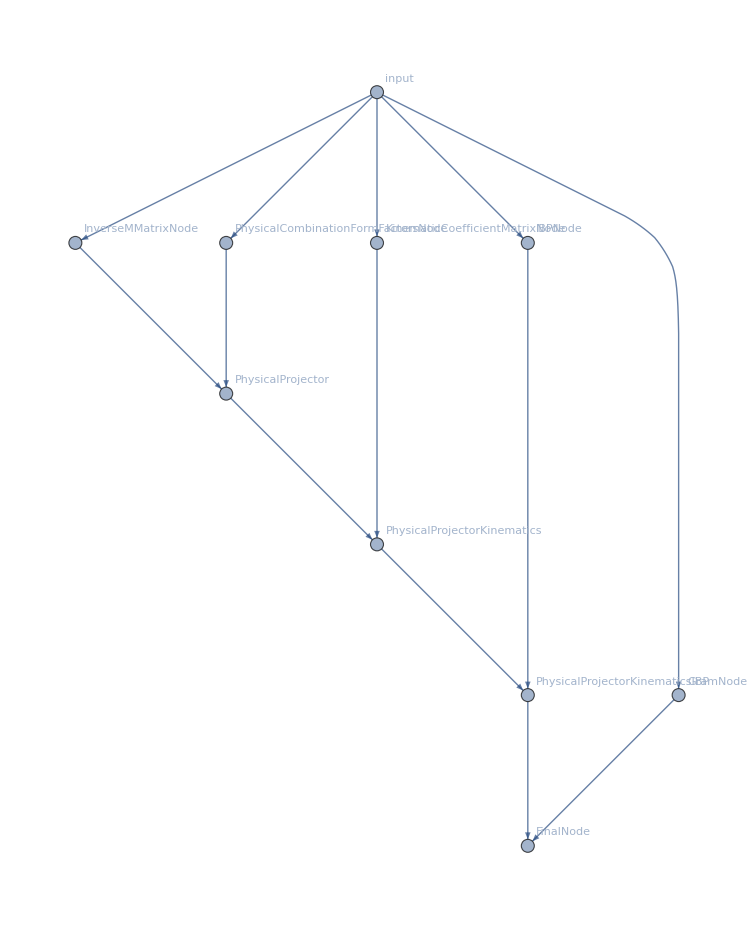

```mathematica
FFGraphDraw[PhysicalFormFactorsOneLoop]
```

#### Reconstruction + Save final result

```mathematica
{ComputationTime,PhysicalFormFactorsWithoutDenomFactors}=FFReconstructFunction[PhysicalFormFactorsOneLoop,FiniteFlowVariables,"PrintDebugInfo"->1,NThreads->10]//AbsoluteTiming;
Print["Total computation time: ", ComputationTime]
```

Generated 100 sample points

Approximate time per evaluation (single core): 0.57522 sec.

Total computation time: 3.43829

```mathematica
PhysicalFormFactorsFileName="PhysicalFormFactors_ColFactorNb_"<>ToString[ColFactorNb]<>"_Nf_"<>ToString[NfPower]<>"_SUN_"<>ToString[SUNPower]<>"_Parity_"<>ToString[ParityOdd]<>".mx";
PhysicalFormFactors=ArrayReshape[PhysicalFormFactorsWithoutDenomFactors,{NbIndependentCombinations,NbMasterIntegrals}]/DenominatorGuessPhysicalFormFactors;
(*DumpSave[MathematicaOutputPath<>PhysicalFormFactorsFileName,PhysicalFormFactors];*)
```

```mathematica
SimplestComponent=PhysicalFormFactors[[1,1]]*DenominatorGuessPhysicalFormFactors//Factor//Series[#,{eps,0,3}]&
```

-(2 eps (s12 s35+s12 s45-2 s12+2 s14 s45-2 s14+2 s23 s35-2 s23-2 s35 s45+2))/(3 ((s35-1) (s45-1)))-(10 eps^2 (s12 s35+s12 s45-2 s12+2 s14 s45-2 s14+2 s23 s35-2 s23-2 s35 s45+2))/(9 ((s35-1) (s45-1)))-(38 eps^3 (s12 s35+s12 s45-2 s12+2 s14 s45-2 s14+2 s23 s35-2 s23-2 s35 s45+2))/(27 ((s35-1) (s45-1)))+O(eps^4)

```mathematica
PhysicalFormFactors[[1;;2,1]]*DenominatorGuessPhysicalFormFactors//Together
```

{-((2 (eps s12 s35+eps s12 s45-2 eps s12+2 eps s14 s45-2 eps s14+2 eps s23 s35-2 eps s23-2 eps s35 s45+2 eps))/((2 eps^2-5 eps+3) (s35-1) (s45-1))),-(2 (eps s35+eps s45-2 eps))/((2 eps^2-5 eps+3) (s35-1) (s45-1))}

```mathematica
Collect[SimplestComponent,eps,Factor]
```

(130 eps^4 (s12 (-s35)-s12 s45+2 s12-2 s14 s45+2 s14-2 s23 s35+2 s23+2 s35 s45-2))/(81 (s35-1) (s45-1))+(38 eps^3 (s12 (-s35)-s12 s45+2 s12-2 s14 s45+2 s14-2 s23 s35+2 s23+2 s35 s45-2))/(27 (s35-1) (s45-1))+(10 eps^2 (s12 (-s35)-s12 s45+2 s12-2 s14 s45+2 s14-2 s23 s35+2 s23+2 s35 s45-2))/(9 (s35-1) (s45-1))+(2 eps (s12 (-s35)-s12 s45+2 s12-2 s14 s45+2 s14-2 s23 s35+2 s23+2 s35 s45-2))/(3 (s35-1) (s45-1))

```mathematica
order=3;
FFNewGraph[LaurentExpandEps, input,FiniteFlowVariables[[2;;]]]
FFAlgLaurent[LaurentExpandEps, laurent, {input}, PhysicalFormFactorsOneLoop,order]
FFGraphOutput[LaurentExpandEps,laurent]
```

True

True

```mathematica
laurentlearn=FFLaurentLearn[LaurentExpandEps];
coefficients=coeff/@Range[FFNParsOut[LaurentExpandEps,laurent]];
```

```mathematica
FFLaurentSol[coefficients,eps,laurentlearn];
```

```mathematica
reconstructed=FFReconstructFunction[LaurentExpandEps,FiniteFlowVariables[[2;;]]];
Series[ArrayReshape[reconstructed,{8,87}][[1;;2,1]],{eps,0,4}]
ArrayReshape[reconstructed,{8,87}][[1;;2,1;;2]]
```

{-(2 (s35 s12+s45 s12-2 s12-2 s14-2 s23+2 s23 s35+2 s14 s45-2 s35 s45+2) eps)/(3 ((s35-1) (s45-1)))-(10 (s35 s12+s45 s12-2 s12-2 s14-2 s23+2 s23 s35+2 s14 s45-2 s35 s45+2) eps^2)/(9 ((s35-1) (s45-1)))-(38 (s35 s12+s45 s12-2 s12-2 s14-2 s23+2 s23 s35+2 s14 s45-2 s35 s45+2) eps^3)/(27 ((s35-1) (s45-1)))-(130 (s35 s12+s45 s12-2 s12-2 s14-2 s23+2 s23 s35+2 s14 s45-2 s35 s45+2) eps^4)/(81 ((s35-1) (s45-1)))+O(eps^5),0}

((-(2 eps s12 s35)/3-(2 eps s12 s45)/3+(4 eps s12)/3-(4 eps s14 s45)/3+(4 eps s14)/3-(4 eps s23 s35)/3+(4 eps s23)/3+(4 eps s35 s45)/3-(4 eps)/3)/(2/3 eps^2 s35 s45-(2 eps^2 s35)/3-(2 eps^2 s45)/3+(2 eps^2)/3-(5 eps s35 s45)/3+(5 eps s35)/3+(5 eps s45)/3-(5 eps)/3+s35 s45-s35-s45+1) | 0
0 | 0)

```mathematica
FFReconstructFunction[LaurentExpandEps,FiniteFlowVariables[[2;;]]]
```

{(-(2 eps s12 s35)/3-(2 eps s12 s45)/3+(4 eps s12)/3-(4 eps s14 s45)/3+(4 eps s14)/3-(4 eps s23 s35)/3+(4 eps s23)/3+(4 eps s35 s45)/3-(4 eps)/3)/(2/3 eps^2 s35 s45-(2 eps^2 s35)/3-(2 eps^2 s45)/3+(2 eps^2)/3-(5 eps s35 s45)/3+(5 eps s35)/3+(5 eps s45)/3-(5 eps)/3+s35 s45-s35-s45+1),0,0,0,(-(2 eps s35)/3-(2 eps s45)/3+(4 eps)/3)/(2/3 eps^2 s35 s45-(2 eps^2 s35)/3-(2 eps^2 s45)/3+(2 eps^2)/3-(5 eps s35 s45)/3+(5 eps s35)/3+(5 eps s45)/3-(5 eps)/3+s35 s45-s35-s45+1),0,0,0}

#### Check if tree level result match

```mathematica
GramR=ReplacementGramSymmetrizedBasis/.mt->1/.mh->√mH2/.ConvertMandelstamMathematicaToForm;
FFResult=Factor[PhysicalFormFactors]/.GramR;
OldResult=Factor[FormFactorsColStructure1SymmetrizedBasis/.mt->1/.mh->√mH2/.ConvertMandelstamMathematicaToForm]/.GramR;
Ratio=FFResult/OldResult//Factor;

(*The factor 2 is explained by the fact that previously I did not use the yukawa constant in the Higgs coupling but an equal expression. After setting all coefficients to 1 that translates to gY -> 1/2 (previous) compared to the actual gY->1 *)
Print["The old and new result match: ", Total[Union[Ratio]]==2]
```

The old and new result match: True

## Partial Fractioning

### Functions

```mathematica
Protect[MinGuessNumber,MaxGuessNumber];
Options[DenomsToPrime]={MinGuessNumber->10^4, MaxGuessNumber->10^5};

Protect[RelativeCertainty];
Options[CombineDenominatorSamples]={RelativeCertainty->0.9};


DenomsToPrime[DenominatorList_,optn:{MinGuessNumber->10^4, MaxGuessNumber->10^5}]:=Module[

{Iter,MaxIter,HighestMultiplicity,UniqueLargestPrime,PrimeFactorsToDenoms,LargestPrimeFactors,NumericInsertionRules},

{Iter,MaxIter,HighestMultiplicity,UniqueLargestPrime}={1,10,0,False};

While[Iter<=MaxIter&&HighestMultiplicity!=1&&Not[UniqueLargestPrime],

NumericInsertionRules=NRandomEvaluation[DenominatorList,OutputStyle->"Rules",OptionValue[MinGuessNumber],OptionValue[MaxGuessNumber]];

LargestPrimeFactors=FactorInteger[DenominatorList/.NumericInsertionRules][[;;,-1,1]];
UniqueLargestPrime=Length[DeleteDuplicates[LargestPrimeFactors]]==Length[DenominatorList];
HighestMultiplicity=FactorInteger[DenominatorList/.NumericInsertionRules][[;;,-1,2]]//Max;

Iter++
];

PrimeFactorsToDenoms=MapThread[Rule,{LargestPrimeFactors,DenominatorList}];

If[Iter<MaxIter,Return[{NumericInsertionRules,PrimeFactorsToDenoms}],Print["Reached maximal Nb of iterations.", MaxIter],Abort[]]

]

GetDenominatorFromNumericSample[ListOfMatrices_,NumericSamplePoint_,PrimeNbToFactorRules_]:=Module[

{NumericSampleMatrices,FactorizedDenominator,NbRows,NbColumns,RemovedPureNumeric},

NumericSampleMatrices=ListOfMatrices/.NumericSamplePoint;
(*The order of matrices in the list is important.*)
FactorizedDenominator=(Dot@@NumericSampleMatrices//Denominator//FactorInteger)//.PrimeNbToFactorRules;

{NbRows,NbColumns}=Dimensions[FactorizedDenominator][[1;;2]];
(*Print["Nb. of rows: ", NbRows, "Nb of columns: ", NbColumns];*)

(*If an entry is 0, the Factorization creates empty lists. These we replace such that the factor becomes 1.*)
RemovedPureNumeric=Table[Select[FactorizedDenominator[[RowI,ColumnJ]],Not[NumericQ[#[[1]]]]&],{RowI,NbRows},{ColumnJ,NbColumns}]/.{}->{{1,0}};

(*Rows, Columns, NbOfFactors, 1=Symbolic factor, 2=Power*)
Return[RemovedPureNumeric[[;;,;;,;;,1]]^RemovedPureNumeric[[;;,;;,;;,2]]]

]



CombineDenominatorSamples[ListOfDenominatorsFromNumericalSample_,optn:OptionsPattern[{RelativeCertainty->0.9}]]:=Module[
(*This function takes a list of guesses based on several numerical evaluations and counts the occurences of each factor. If it appears in more then "RelativeCertainty" (default= 90%) of the cases it is selected as a valid candidate. *)
{NbOfSamples,PossibleCandidates,SelectedCandidates},

NbOfSamples=ListOfDenominatorsFromNumericalSample//Length;
PossibleCandidates={#,Count[Flatten[ListOfDenominatorsFromNumericalSample],#]}&/@(Union@@ListOfDenominatorsFromNumericalSample);

SelectedCandidates=Select[PossibleCandidates,#[[2]]>=OptionValue[RelativeCertainty]*NbOfSamples&][[;;,1]];
Return[SelectedCandidates]
]

Options[MakeDenominatorGuess]={NSamples->30, NThreads->1};
MakeDenominatorGuess[AnalyticMatrices_,optn:OptionsPattern[{NSamples->30, NThreads->1}]]:=Module[

{ListOfDenominators,SampleReplacements,DenominatorGuesses,NbRows,NbColumns,FinalDenominatorGuess},

If[Not[ListQ[AnalyticMatrices]],Print["Input must be a ordered list of matrices {M1, M2,..., Mn} -> M1.M2.M3. ... .Mn"]; Abort[]];

ListOfDenominators=Denominator/@AnalyticMatrices//Flatten//Union//Factor;
ListOfDenominators=AbbreviateDenominators[ 1/ListOfDenominators][[2]];

SampleReplacements=DenomsToPrime[ListOfDenominators]&/@Range[OptionValue[NSamples]];

(*Generate denominator samples: *)
If[OptionValue[NThreads]==1, 

(*If: *)
DenominatorGuesses=Monitor[Table[GetDenominatorFromNumericSample[AnalyticMatrices,SampleReplacements[[SampleI,1]],SampleReplacements[[SampleI,2]]],{SampleI,OptionValue[NSamples]}],SampleI],

(*Else: *)
LaunchKernels[OptionValue[NThreads]];
DenominatorGuesses=ParallelTable[GetDenominatorFromNumericSample[AnalyticMatrices,SampleReplacements[[SampleI,1]],SampleReplacements[[SampleI,2]]],{SampleI,OptionValue[NSamples]}];
CloseKernels[];

];

(*Combine samples: *)
{NbRows,NbColumns}={Length[AnalyticMatrices[[1]]],Length[AnalyticMatrices[[-1,1]]]};
FinalDenominatorGuess=Table[Times@@CombineDenominatorSamples[DenominatorGuesses[[;;,RowI,ColumnJ]]],{RowI,NbRows},{ColumnJ,NbColumns}];

Return[FinalDenominatorGuess];

]
```

### Guess denominators component wise (IBP insertion)

```mathematica
(*MMatrixI contains the Gram determinant in the denominator which is spurious as it should cancel once we compute the physical combination of form factors.-> Remove it (checked by observation that it only adds the Gram determinant to the list)*)
ListOfDenominators={Denominator[KinematicMatrix],Denominator[IBPMatrix]}//Flatten//Union//Factor;
Print["Naive number of denominators: ", Length[ListOfDenominators]]

{expr,ListOfDenominators,qis}=AbbreviateDenominators[ 1/ListOfDenominators];
Print["Number of denominators found by MultivariateApart: ", Length[qis]]

AnalyticResultInsertionIBP=KinematicMatrix.IBPMatrix;
```

Naive number of denominators: 567

Number of denominators found by MultivariateApart: 47

#### Numeric Sampling

```mathematica
MaxEvaluations=5;
SampleReplacements=DenomsToPrime[ListOfDenominators]&/@Range[MaxEvaluations];
```

Single core execution

```mathematica
DenominatorGuess=Table[FactorInteger[Denominator[AnalyticResultInsertionIBP/.SampleReplacements[[EvaluationI,1]]]]/.SampleReplacements[[EvaluationI,2]],{EvaluationI, MaxEvaluations}];
```

Parallel execution

```mathematica
LaunchKernels[Min[MaxEvaluations,IntegerPart[$ProcessorCount/2]]];
DenominatorGuess=ParallelTable[FactorInteger[Denominator[AnalyticResultInsertionIBP/.SampleReplacements[[EvaluationI,1]]]]/.SampleReplacements[[EvaluationI,2]],{EvaluationI, MaxEvaluations}];
CloseKernels[]
```

#### Reconstruct denominators

```mathematica
{NbNumericEvaluations,NbFormFactors,NbMasterIntegrals}=DenominatorGuess//Dimensions

DenominatorGuessesWithPowers=
Table[
Select[DenominatorGuess[[NumericEval,FormFactor,MasterIntegral]],Not[NumericQ[#[[1]]]]&]
,{FormFactor,NbFormFactors},{MasterIntegral,NbMasterIntegrals},{NumericEval,NbNumericEvaluations}]/.{}->{{1,0}};

DenominatorGuessesWithPowers=DenominatorGuessesWithPowers[[;;,;;,;;,;;,1]]^DenominatorGuessesWithPowers[[;;,;;,;;,;;,2]];

DenominatorGuessIBPInsertion=Table[Times@@GuessDenominator[DenominatorGuessesWithPowers[[FormFactor,MasterIntegral]]],{FormFactor,NbFormFactors},{MasterIntegral,NbMasterIntegrals}];
```

{30,16,87}

```mathematica
DumpSave[MathematicaInputPath<>"DenominatorGuessIBPInsertion.mx",DenominatorGuessIBPInsertion];
```

### Generate Groebner basis

```mathematica
Options[ApartOwnOrder]={DebugModus->False};
ApartOwnOrder[WantedDenominators_,ApartDenominators_,ApartPlaceholder_,optn:OptionsPattern[{DebugModus->False}]]:=Module[
{NbApartDenominators,WantedApartDenominators,UnWantedApartDenominators,OrderedWantedDenominators,OrderedUnWantedDenominators,FinalOrdering},

NbApartDenominators=ApartDenominators//Length;
If[OptionValue[DebugModus],Print["Apart denominators: ",ApartDenominators ];];

(*Label denominators which are in the list of wanted denominators.*)
WantedApartDenominators=Select[Thread[List[ApartDenominators, ApartPlaceholder]],MemberQ[WantedDenominators,#[[1]]]&];
UnWantedApartDenominators=Select[Thread[List[ApartDenominators, ApartPlaceholder]],Not[MemberQ[WantedDenominators,#[[1]]]]&];

If[OptionValue[DebugModus],Print["Wanted apart denominators: ",WantedApartDenominators]];
If[OptionValue[DebugModus],Print["UnWanted apart denominators: ",UnWantedApartDenominators ]];

(*Apart order puts the variables at last place. To avoid double counting (they can appear in both lists), I add the variables by hand. *)
OrderedWantedDenominators=ApartOrder[WantedApartDenominators[[;;,1]],WantedApartDenominators[[;;,2]]][[;;-2]];
OrderedUnWantedDenominators=ApartOrder[UnWantedApartDenominators[[;;,1]],UnWantedApartDenominators[[;;,2]]][[;;-2]];

If[OptionValue[DebugModus],Print["Ordering wanted apart denominators: ",OrderedWantedDenominators]];
If[OptionValue[DebugModus],Print["Ordering unwanted apart denominators: ",OrderedUnWantedDenominators ]];


FinalOrdering=Flatten[{OrderedWantedDenominators,OrderedUnWantedDenominators,{Variables[ApartDenominators]}},1];

Return[FinalOrdering];

]
```

```mathematica
{IComponent,JComponent}={1,3};
{expr,ApartDenoms,InverseSymbols}=AbbreviateDenominators[AnalyticResultInsertionIBP[[IComponent,JComponent]],InverseSymbol->q];
{dummy,WantedDenominators,dummy2}=AbbreviateDenominators[1/DenominatorGuessIBPInsertion[[IComponent,JComponent]]];
ordering=ApartOwnOrder[WantedDenominators,ApartDenoms,InverseSymbols,DebugModus->False]
```

{{q15},{q9},{q4},{q14},{q8},{q12},{q7},{q3},{q2},{q1},{q11},{q10},{q6},{q13},{q5},{mH2,s12,s14,s23,s35,s45}}

```mathematica
testbasis=ApartBasis[ApartDenoms,InverseSymbols,ordering];
```

```mathematica
testsimplify=ApartReduce[expr,testbasis,ordering]//Expand//Variables
```

{mH2,D,q1,s12,s14,s23,s35,s45}

### Denominator Guess Physical form factors

```mathematica
A={{s,1+s},{1/s,1}};
FFNewGraph[TestGraph,input, {s}];
FFAlgRatFunEval[TestGraph,MatrixANode,{input}, {s},Join@@A];
FFAlgRatFunEval[TestGraph,MatrixBNode,{input}, {s},Join@@IdentityMatrix[2]];
FFAlgMatMul[TestGraph, MatMulAB, {MatrixANode, MatrixBNode},2,2,2]
FFAlgMul[TestGraph, MulAB,{MatMulAB,5}]
FFGraphOutput[TestGraph,MatMulAB]
```

True

FF::noalg: No algorithm with identifier TestGraph→5.

$Failed

```mathematica
FFReconstructFunction[TestGraph,{s}]
```

{s,s+1,1/s,-s}

```mathematica
FFGraphEvaluate[TestGraph,{13},PrimeNo->17]
FFGraphEvaluate[TestGraph,{13},"PrimeNo"->17]
```

{13,14,8513881880173638529,9223372036854775060}

{13,14,8513881880173638529,9223372036854775060}

```mathematica
A/.s->1354
```

(1354 | 1355
1/1354 | 1)

```mathematica
NumericPoint={s->10};
A={{s,1+s},{1/s,1}}/.NumericPoint;
B={{s,1+s},{s,1/s}}/.NumericPoint;
Seed=6;
Print["PrimeNumber: "]
PrimeField=Prime[Seed]

ADenomMod=ExtendedGCD[Denominator[A],PrimeField][[;;,;;,2,1]];
AMod=Mod[Numerator[A]*ADenomMod,PrimeField];

BDenomMod=ExtendedGCD[Denominator[B],PrimeField][[;;,;;,2,1]];
BMod=Mod[Numerator[B]*BDenomMod,PrimeField];

AMod.BMod//Mod[#,PrimeField]&
```

PrimeNumber:

13

(2 | 11
11 | 9)

```mathematica
{{s,1+s},{1/s,1}}.{{s,1+s},{s,1/s}}//Together
```

(2 s^2+s | (s^3+s^2+s+1)/s
s+1 | (s+2)/s)

### Denominator Guess Partial Fractioned D Physical Form Factors

#### Finite Flow Graph implemented in Mathematica

```mathematica
FFGraphApartDMathematica[KinematicTestPoint_,DimComponentFinal_]:=Module[
{IBPTensorN,DLinearKinematicMatrixN,DFreeKinematicMatrixN, RecombinedKinematicIBP, PhysicalFormFactorN},

IBPTensorN = IBPTensor/.KinematicTestPoint;
{DLinearKinematicMatrixN,DFreeKinematicMatrixN}={DLinearKinematicMatrix,DFreeKinematicMatrix}/.KinematicTestPoint;
(*D^0 contribution in the final result (-> DimComponentFinal=1)*)
If[DimComponentFinal==1, 
RecombinedKinematicIBP =DLinearKinematicMatrixN.Total[IBPTensorN[[2;;5]]]+DFreeKinematicMatrixN.IBPTensorN[[1]];
];

(*D^1 contribution in the final result (-> DimComponentFinal = 2)*)
If[DimComponentFinal==2,
RecombinedKinematicIBP = DLinearKinematicMatrixN.IBPTensorN[[1]]+DFreeKinematicMatrixN.IBPTensorN[[2]];
];

(*D^2 contribution in the final result (-> DimComponentFinal = 3)*)
If[DimComponentFinal==3,
RecombinedKinematicIBP=DLinearKinematicMatrixN.IBPTensorN[[1]];
];

If[DimComponentFinal!=1 && DimComponentFinal != 2 && DimComponentFinal != 3,
RecombinedKinematicIBP = (DLinearKinematicMatrixN+DFreeKinematicMatrixN).IBPTensorN[[1]];
];

PhysicalFormFactorN=(PhysicalCombinationFormFactors/.KinematicTestPoint).(MMatrixI/.KinematicTestPoint).RecombinedKinematicIBP;
Return[PhysicalFormFactorN];

]
```

#### Denominator Guess

```mathematica
{ColFactorNb,SUNPower,NfPower}={2,1,1}
ColorConfiguration={ColFactorNb,SUNPower,NfPower};
ParityOdd=False;
DimComponentFinal=1;

Print["Initialize matrices: "]
InitializeInputInDependentMatrices[];
InitializePhysicalCombinationFormFactors[ParityOdd];

For[DimComponentFinal=1, DimComponentFinal<=7,DimComponentFinal++,
Print["Initialize kinematic matrix: "];
InitializeKinematicDSplitIBPTensor[ColorConfiguration, DimComponentFinal];

Print["Collect denominators: "];
ListOfDenominators=AbbreviateDenominatorsList[{IBPTensor,DLinearKinematicMatrix,DFreeKinematicMatrix,MMatrixI,PhysicalCombinationFormFactors}];

Print["Denominator guess iteration nb: "];
DenominatorGuessPhysicalFormFactors=GuessDenominator[FFGraphApartDMathematica,ListOfDenominators,NFunctionArgs->DimComponentFinal];

DenominatorGuessName="DenominatorGuess_ColFactorNb_"<>ToString[ColFactorNb]<>"_Nf_"<>ToString[NfPower]<>"_SUN_"<>ToString[SUNPower]<>"_Parity_"<>ToString[ParityOdd]<>"_DimComponent_"<>ToString[DimComponentFinal]<>".mx";
DumpSave[MathematicaInputPath<>"Denominator_Guesses/"<>DenominatorGuessName,DenominatorGuessPhysicalFormFactors];

]
```

{2,1,1}

Initialize matrices:

Initialize kinematic matrix:

Collect denominators:

Denominator guess iteration nb:

{30,8,87}

Initialize kinematic matrix:

Collect denominators:

Denominator guess iteration nb:

{30,8,87}

Initialize kinematic matrix:

Collect denominators:

Denominator guess iteration nb:

{30,8,87}

Initialize kinematic matrix:

Collect denominators:

Denominator guess iteration nb:

{30,8,87,1}

Initialize kinematic matrix:

Collect denominators:

Denominator guess iteration nb:

{30,8,87,1}

Initialize kinematic matrix:

Collect denominators:

Denominator guess iteration nb:

{30,8,87}

Initialize kinematic matrix:

Collect denominators:

Denominator guess iteration nb:

{30,8,87}

### Decomposition Kinematic Matrix

```mathematica
{ColFactorNb, SUNPower, NfPower}={2,1,1};
InitializeKinematicMatrix[{ColFactorNb, SUNPower, NfPower}];

DenomContainsDQ=MemberQ[Variables[Denominator[KinematicMatrix]],D];
Print["Kinematic matrix contains D in denominator: ", DenomContainsDQ]

DLinearKinematicMatrix=Coefficient[KinematicMatrix,D,1];
DFreeKinematicMatrix=KinematicMatrix/.D->0;
KinematicMatrixDecomposedD={DFreeKinematicMatrix,DLinearKinematicMatrix};

CaughtAllDTermsQ=Total[Total[NRandomEvaluation[KinematicMatrix-DFreeKinematicMatrix-D*DLinearKinematicMatrix]]]==0;
Print["Got all D dependence: ", CaughtAllDTermsQ]

If[CaughtAllDTermsQ&&Not[DenomContainsDQ],
KinematicMatrixFileName="KinematicMatrixDecomposedD_ColFactor_"<>ToString[ColFactorNb]<>"_SUN_"<>ToString[SUNPower]<>"_Nf_"<>ToString[NfPower]<>".mx";
DumpSave[MathematicaInputPath<>"KinematicMatrixDecomposedD/"<>KinematicMatrixFileName,KinematicMatrixDecomposedD];
]
```

Kinematic matrix contains D in denominator: False

Got all D dependence: True

## Compute dimensional shift matrix for master integrals

```mathematica
(*The U polynomial is the same for all the topologies. *)
GraphPolynomialsForTopologies=GetGraphpolynomialsUF[LoopMomentaGGToTTH,ExternalMomentaGGToTTH,InversePropagatorsIntegralFamilyA][[1]];
PowerOfPropagators={Delete[#,0]}&/@MasterIntegralsReduze;
UPolynomials=Table[GraphPolynomialsForTopologies/.(αF[#]->PropagatorPower[[#]]*αF[#]&/@Range[Length[PropagatorPower]]),{PropagatorPower,PowerOfPropagators}];
```

### Get list of integrals for reduction in Kira

```mathematica
ListOfIntegralsNeededForDimensionalShift=DimensionalShiftIntegral[MasterIntegralsKira, UPolynomials,{},ExtractKiraList->True]/.ReplaceCrossedTopologies//Union;
SetDirectory[NotebookDirectory[]<>"Mathematica_Modules/Output_Files/"];
Do[WriteLine["DimensionalShiftIntergals.txt",ToString[KiraIntegral]],{KiraIntegral,ListOfIntegralsNeededForDimensionalShift}];
SetDirectory[NotebookDirectory[]];
```

### Get rules for dimensionally shifted integrals

#### Load reductions and Reduze master integrals

```mathematica
ReduzeShiftsCrossings=Get["Mathematica_Modules/Input_Files/Masters_Shifts_and_Symmetries.m"]/.{INT[x_,y1_,y2_,y3_,y4_,{z__}]->x[z]};

(*The topology name is saved as a string in reduze so I have to convert it into a symbol*)
ReduzeShiftsCrossings=ToExpression[ToString[#]]&/@ReduzeShiftsCrossings;

(*Lists must be loaded. Reductions lie on Newton1 *)
DimShiftReductionRulesUncrossed=Get["Mathematica_Modules/Input_Files/Dimensional_Shift_Reductions.m"]/.{mt2->mt^2, mh2->mh^2};

DimShiftReductionRulesX12=DimShiftReductionRulesUncrossed/.{s14:>s24,s23:>s13,PentaboxGGtoTTHTopologyA[z__]->PentaboxGGtoTTHTopologyAx12[z],PentaboxGGtoTTHTopologyB[z__]->PentaboxGGtoTTHTopologyBx12[z],PentaboxGGtoTTHTopologyC[z__]->PentaboxGGtoTTHTopologyCx12[z],PentaboxGGtoTTHTopologyD[z__]->PentaboxGGtoTTHTopologyDx12[z]}/.FivePointMandelstamReplacementsLorenzoForm;

DimShiftReductionRulesX34=DimShiftReductionRulesUncrossed/.{s14:>s13,s23:>s24,s35:>s45,s45:>s35,PentaboxGGtoTTHTopologyA[z__]->PentaboxGGtoTTHTopologyAx34[z],PentaboxGGtoTTHTopologyB[z__]->PentaboxGGtoTTHTopologyBx34[z],PentaboxGGtoTTHTopologyC[z__]->PentaboxGGtoTTHTopologyCx34[z],PentaboxGGtoTTHTopologyD[z__]->PentaboxGGtoTTHTopologyDx34[z]}/.FivePointMandelstamReplacementsLorenzoForm;

DimShiftReductionRulesX12X34=DimShiftReductionRulesUncrossed/.{s14:>s23,s23:>s14,s35:>s45,s45:>s35,PentaboxGGtoTTHTopologyA[z__]->PentaboxGGtoTTHTopologyAx12x34[z],PentaboxGGtoTTHTopologyB[z__]->PentaboxGGtoTTHTopologyBx12x34[z],PentaboxGGtoTTHTopologyC[z__]->PentaboxGGtoTTHTopologyCx12x34[z],PentaboxGGtoTTHTopologyD[z__]->PentaboxGGtoTTHTopologyDx12x34[z]}/.FivePointMandelstamReplacementsLorenzoForm;

DimShiftReductionRules=Union[DimShiftReductionRulesUncrossed,DimShiftReductionRulesX12,DimShiftReductionRulesX34,DimShiftReductionRulesX12X34]/.ReduzeShiftsCrossings;
```

```mathematica
DumpSave["Mathematica_Modules/Input_Files/DimShiftReductionRules.mx",DimShiftReductionRules];
```

```mathematica
DumpGet["Mathematica_Modules/Input_Files/MasterIntegralsReduze.mx"]
DumpGet["Mathematica_Modules/Input_Files/DimShiftReductionRules.mx"]
```

```mathematica
PowerOfPropagators={Delete[#,0]}&/@MasterIntegralsReduze;
UPolynomials=Table[GraphPolynomialsForTopologies/.(αF[#]->PropagatorPower[[#]]*αF[#]&/@Range[Length[PropagatorPower]]),{PropagatorPower,PowerOfPropagators}];
DimensionalShiftRules=DimensionalShiftIntegral[MasterIntegralsReduze, UPolynomials,DimShiftReductionRules];

KiraMastersInDimShiftRelationConverted=ToReduze[SelectIntegrals[DimensionalShiftRules[[;;,2]],IntegralSymbol->"Pentabox"]];
Print["Nb of masters in dimensional shift relations: ", Length[KiraMastersInDimShiftRelationConverted]];
```

Nb of masters in dimensional shift relations: 103

```mathematica
SetDirectory[NotebookDirectory[]<>"reduze_jobs/mytmp/"];
DeleteFile["DimensionalShiftMasterIntergals.txt"];
Do[WriteLine["DimensionalShiftMasterIntergals.txt",ToString[ConvertedMaster]],{ConvertedMaster,KiraMastersInDimShiftRelationConverted}];
SetDirectory[NotebookDirectory[]];
```

```mathematica
CrossingRelationsDimShift=Get["Mathematica_Modules/Input_Files/Dim_Shift_Masters_Shifts_and_Symmetries.m"];
IntegralConversions=ToKira[SelectIntegrals[Union[CrossingRelationsDimShift[[;;,1]],CrossingRelationsDimShift[[;;,2]]]],OutputStyle->"Rules"];
CrossingRelationsDimShift=CrossingRelationsDimShift/.IntegralConversions;
DimensionalShiftRules=DimensionalShiftRules/.CrossingRelationsDimShift;

(*Only for cross checks: *)
MasterIntegralsReduzeDimShift=SelectIntegrals[DimensionalShiftRules[[;;,2]],IntegralSymbol->"Pentabox"];
Print["Nb. of master integrals in dimensional shift relations: ", Length[MasterIntegralsReduzeDimShift], ". Should be 87." ]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Nb. of master integrals in dimensional shift relations: 0. Should be 87.

```mathematica
DimensionalShiftMatrix=
Coefficient[#,MasterIntegralsReduze]&/@(MasterIntegralsReduze/.DimensionalShiftRules);
DumpSave[MathematicaInputPath<>"DimensionalShiftMatrix.mx",DimensionalShiftMatrix];
```

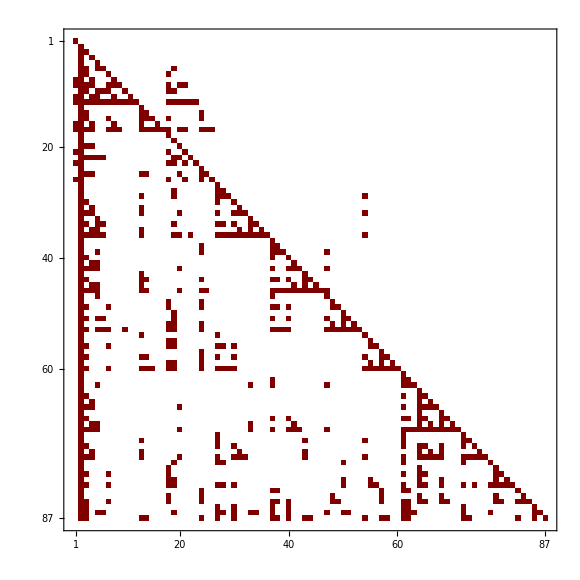

```mathematica
DimensionalShiftMatrix//MatrixPlot
```

### Dimensional Shift for Boxes + Pentagons

```mathematica
DumpGet["Mathematica_Modules/Input_Files/MasterIntegralsReduze.mx"];
DumpGet["Mathematica_Modules/Input_Files/DimensionalShiftMatrix.mx"];
Dimensions[DimensionalShiftMatrix]
```

{87,87}

```mathematica
PentaboxPositions=Position[MasterIntegralsReduze,#]&/@(x_@@@Select[Tuples[{1,0},5],Total[#]==5&])//Flatten;
BoxPositions=Position[MasterIntegralsReduze,#]&/@(x_@@@Select[Tuples[{1,0},5],Total[#]==4&])//Flatten;
TrianglePositions=Position[MasterIntegralsReduze,#]&/@(x_@@@Select[Tuples[{1,0},5],Total[#]==3&])//Flatten;
BubblePositions=Position[MasterIntegralsReduze,#]&/@(x_@@@Select[Tuples[{1,0},5],Total[#]==2&])//Flatten;
TadPolePositions=Position[MasterIntegralsReduze,#]&/@(x_@@@Select[Tuples[{1,0},5],Total[#]==1&])//Flatten;

DontShift=Union[TadPolePositions,BubblePositions,TrianglePositions];
DontShiftMatrix=DimensionalShiftMatrix[[DontShift,DontShift]]//Factor//Inverse//Factor;
DontShiftMatrixFull=IdentityMatrix[87];
DontShiftMatrixFull[[DontShift,DontShift]]=DontShiftMatrix;
```

```mathematica
DimShiftBoxesAndPentagons=DimensionalShiftMatrix.DontShiftMatrixFull;
DimShiftBoxesAndPentagons[[DontShift,DontShift]]=DimShiftBoxesAndPentagons[[DontShift,DontShift]]//Factor;
```

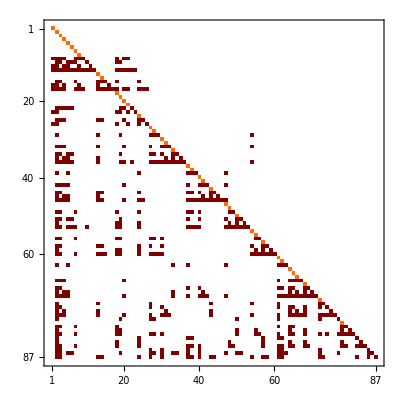

```mathematica
DimShiftBoxesAndPentagons//MatrixPlot
```

```mathematica
DumpSave["DimShiftBoxesAndPentagons.mx",DimShiftBoxesAndPentagons];
```

```mathematica
DumpGet["Mathematica_Modules/Input_Files/MasterIntegralsReduze.mx"];
```

### Comparison with Lorenzos Result

```mathematica
(*The Pentaboxes and boxes are in D+6 dimensions whereas the others are in D=4 dimensions.*)
DumpGet[MathematicaInputPath<>"DimShiftBoxesAndPentagons.mx"];
DimShiftBoxesAndPentagons=DimShiftBoxesAndPentagons/.mt->1;
```

```mathematica
ReduzeShiftRelations=Get[MathematicaInputPath<>"Lorenzos_One_Loop_Masters_GGtoTTh_Shifts_and_Symmetries.m"]//ToKira;
ReplacementsD6IntegralsLorenzosNaming={INT[x_,5]->-x[1,1,1,1,1],INT[x_,4,#]->-x@@ReplacePart[ConstantArray[1,5],#->0]&/@Range[5]}//Flatten;
LorenzosDimShiftRules=Get["Lorenzos_Results/Dimensional_Shifts_Lorenzo.m"]/.ReplacementsD6IntegralsLorenzosNaming/.ReduzeShiftRelations;
```

```mathematica
DimShiftedIntegralsLorenzo=MasterIntegralsReduze/.LorenzosDimShiftRules//ConvertFormExpression;
DimShiftMatrixLorenzo=Coefficient[#,MasterIntegralsReduze]&/@ DimShiftedIntegralsLorenzo;
```

```mathematica
SameVariablesQ[{DimShiftMatrixLorenzo,DimShiftBoxesAndPentagons},DebugModus->True]
```

The following variables are in Expression1 but not in Expression2: {}

The following variables are in Expression2 but not in Expression1: {mt}

{{{d,mh,s12,s14,s23,s35,s45},{d,mh,mt,s12,s14,s23,s35,s45}},{d,mh,s12,s14,s23,s35,s45},{mt}}

### Simplify DimShift with Fermat

```mathematica
DumpGet[MathematicaInputPath<>"DimensionalShiftMatrix.mx"];

VarsForFermat=StringDelete[ToString[{KinematicVariables,d}],{"}" ,"{" }];


Install[$FLinkPath];
FInit[$FermatPath, VarsForFermat];

RatsString = ToString[#,InputForm]&/@rats;
GCDRats = FEval/@RatsString//ToExpression;

FClose[]
```

FLink created! You can read information on FInit, FEval, FAddVars and FClose

```mathematica
DumpSave[MathematicaInputPath<>"DimShiftSimplified.mx",DimShiftSimplified];
```

```mathematica
Options[WriteFile]={PathToFile->Directory[], StandardPath->{" "}};
WriteFile[NewFileName_,StringForFile_,optn:OptionsPattern[{PathToFile->Directory[]<>"/", StandardPath->{" "}}]]:=Module[

{FilePath},

FilePath="DummyPath";
If[OptionValue[StandardPath]==="Kira",FilePath=KiraReductionsPath<>NewFileName];
If[OptionValue[StandardPath]==="reduze",FilePath=ReduzePath<>NewFileName];
If[OptionValue[StandardPath]==="MathematicaInput",FilePath=MathematicaInputPath<>NewFileName];
If[FilePath==="DummyPath",FilePath=OptionValue[PathToFile]<>NewFileName];

Print["Write files to: ", FilePath];
CreateFile[FilePath,OverwriteTarget->True];
If[ListQ[StringForFile],WriteLine[FilePath,#]&/@StringForFile, WriteLine[ FilePath,StringForFile]];
Close[ FilePath];
]
```

```mathematica
StringMasterIntegralsReduze=ToString/@ToReduze[MasterIntegralsReduze];
WriteFile["MastersForDETTH.reduze",StringMasterIntegralsReduze,StandardPath->"reduze"];
```

Write files to: /space/ge45leb/TTHProject/reduze_jobs/MastersForDETTH.reduze

## Compute Differential Equation for Master Integrals

## Failed derivation attempts

### Function definitions

```mathematica
Options[IterativeShiftOperatorOnIntegral]={FeynmanParameterSymbol->Global`αF,IntegralList->False,IntegralSymbol->INT};
IterativeShiftOperatorOnIntegral[UorFPolynomial_, FeynmanIntegral_,IBPReductions_,RPropagatorPowerShifts_, optn:OptionsPattern[{FeynmanParameterSymbol->Global`αF,IntegralList->False,IntegralSymbol->INT}]]:=Module[
(*The shift operator is defined in Eq. 6.25 of arXiv:2201.03593*)
{ ShiftedIntegral,UnShiftedIntegral, ReduceOneFeynmanParameter,IntegralsForReduction,ShiftedIntegralPreInsertion,MasterIntegrals},

ShiftedIntegral=Expand[UorFPolynomial*FeynmanIntegral];
If[OptionValue[IntegralList],IntegralsForReduction={}];

(*Apply shift iteratively for ^2 Feynman parameters*)
While[InvolvesVarQ[ShiftedIntegral,OptionValue[FeynmanParameterSymbol]],
 
ShiftedIntegral=SingleInsertionShiftOperator[ShiftedIntegral,RPropagatorPowerShifts];

If[
OptionValue[IntegralList],AppendTo[IntegralsForReduction,SelectIntegrals[ShiftedIntegral,IntegralSymbol->OptionValue[IntegralSymbol]]]
];

(*Print["Before InsertionIBP: ", ShiftedIntegral];*)
(*Print[InvolvesVarQ[ShiftedIntegral,OptionValue[FeynmanParameterSymbol]]];*)

ShiftedIntegral=ShiftedIntegral/.IBPReductions//Expand;

];

If[OptionValue[IntegralList],Return[Union[Flatten[IntegralsForReduction]]]];
Return[ShiftedIntegral]

]

PropagatorShiftRules[FeynmanIntegral_]:=Module[
{TopoName, NbPropagators, RPropagatorPowerShifts},

(*Feynman integral must be in KIRA notation. *)
TopoName=FeynmanIntegral//TopologyName;
NbPropagators=FeynmanIntegral//PowersOfPropagator//Length;
RPropagatorPowerShifts=FeynmanParemeterInducedPropagatorShift[TopoName,NbPropagators];

Return[RPropagatorPowerShifts];

]
Options[SingleInsertionShiftOperator]={FeynmanParameterSymbol->Global`αF};
SingleInsertionShiftOperator[ExpandedExprWithFI_,RShiftOnIntegral_,optn:OptionsPattern[{FeynmanParameterSymbol->Global`αF}]]:=Module[
{ShiftedIntegral,ReduceOneFeynmanParameter,DummyParameter},

ReduceOneFeynmanParameter={(Power[OptionValue[FeynmanParameterSymbol][z_],n_])->DummyParameter[z]^(n-1)*OptionValue[FeynmanParameterSymbol][z]};
ShiftedIntegral=ExpandedExprWithFI/.ReduceOneFeynmanParameter/.RShiftOnIntegral/.{DummyParameter->OptionValue[FeynmanParameterSymbol]};

Return[ShiftedIntegral]

]
```

### Computation Graph polynomials

```mathematica
IntegralFamilyDefinitions={InversePropagatorsIntegralFamilyA,InversePropagatorsIntegralFamilyB,InversePropagatorsIntegralFamilyC,InversePropagatorsIntegralFamilyD}/.{mt->√mt2,mh->√mH2};

GraphPolynomialsTopTopologies=Table[GetGraphpolynomialsUF[LoopMomentaGGToTTH,ExternalMomentaGGToTTH,IntegralFamilyI,KineamticReplacementOfMomenta->ReplaceScalarProductsExternalMomentaForm],{IntegralFamilyI,IntegralFamilyDefinitions}]//Together;
NbMasterIntegrals=MasterIntegralsReduze//Length;
GraphPolynomialsMasterIntegrals={};

For[MasterIntegralI =1,MasterIntegralI <=NbMasterIntegrals,MasterIntegralI ++,

MasterIntegral=MasterIntegralsReduze[[MasterIntegralI]];

CrossingString==" ";
(*Use momentum crossing for crossed topologies.*)
If[InvolvesVarQ[MasterIntegral,x12],CrossingString="x12"];
If[InvolvesVarQ[MasterIntegral,x34],CrossingString="x34"];
(*Must come at the end to evtl. overwright x12 or x34*)
If[InvolvesVarQ[MasterIntegral,x12x34],CrossingString="x12x34"];
 

(*Set toptopology: TopologyIndex = {1,2,3,4} ^= Topo {A,B,C,D}*)
TopologyIndex=1;
If[InvolvesVarQ[MasterIntegral,TopoB],TopologyIndex=2];
If[InvolvesVarQ[MasterIntegral,TopoC],TopologyIndex=2];
If[InvolvesVarQ[MasterIntegral,TopoD],TopologyIndex=2];

(*Cross only momenta*)
If[CrossingString=="x12x34",

GraphPolynomialsOfMasterIntegral=CrossXIJ[CrossXIJ[GraphPolynomialsSubTopology[GraphPolynomialsTopTopologies[[TopologyIndex]],MasterIntegral],"x12",IntegralSymbol->Dummy],"x34",IntegralSymbol->Dummy]//Together,

GraphPolynomialsOfMasterIntegral=CrossXIJ[GraphPolynomialsSubTopology[GraphPolynomialsTopTopologies[[TopologyIndex]],MasterIntegral],CrossingString,IntegralSymbol->Dummy]//Together

];


AppendTo[GraphPolynomialsMasterIntegrals, GraphPolynomialsOfMasterIntegral];

]
Clear[MasterIntegralI,MasterIntegral,TopologyIndex,CrossingMomenta,GraphPolynomialsOfMasterIntegral]

SecondGraphPolynomials=GraphPolynomialsMasterIntegrals[[;;,2]];

(*Lines = integral, column= derivaive with respect to kinematic variable*)
FPolynomialDerivatives=Table[D[FPolynomial,DerivativeVar],{FPolynomial,SecondGraphPolynomials},{DerivativeVar,KinematicVarsSymmetric}];
```

### Non iterative approach (reduction of integrals does not run through)

```mathematica
InterestedIntegrals={18,19,24};
ShiftedIntegrals=Table[ShiftOperatorOnIntegral[FPolynomialDerivatives[[MasterIntegralI]],MasterIntegralsReduze[[MasterIntegralI]]],{MasterIntegralI,InterestedIntegrals}];


ShiftedIntegralsString=ToString/@(SelectIntegrals[ShiftedIntegrals,IntegralSymbol->Penta]/.ReplaceCrossedTopologies);

WriteFile["ReductionsDEBubbles.kira",ShiftedIntegralsString,PathToFile->KiraReductionsPath<>"RequestedReductions/"]

(*Clear[ShiftedIntegrals]*)
```

Write files to: /scratch/ge45leb/Cluster_Scratch/TTHProject/Kira_Reductions/RequestedReductions/ReductionsDEBubbles.kira

```mathematica
RDEBubbles=Get[$KiraReductionsFolder<>"DEBubbles.m"];
RDEBubblesX12=CrossRuleXIJ[RDEBubbles,"x12",IntegralSymbol->Penta,RMandelstams->RKinematicLorenzoSymmetricVars];
RDEBubblesX34=CrossRuleXIJ[RDEBubbles,"x34",IntegralSymbol->Penta,RMandelstams->RKinematicLorenzoSymmetricVars];
RDEBubblesX12X34=CrossRuleXIJ[RDEBubblesX12,"x34",IntegralSymbol->Penta,RMandelstams->RKinematicLorenzoSymmetricVars];

RDEBubbles={RDEBubbles,RDEBubblesX12,RDEBubblesX34,RDEBubblesX12X34}/.ReduzeShiftsCrossings//Flatten;
DEq=ShiftedIntegrals/.RDEBubbles/.(RDimShiftI)//Simplify;
```

(ϵ PentaboxGGtoTTHTopologyA(1,0,0,0,0)-PentaboxGGtoTTHTopologyAx12x34(1,0,0,1,0) (ϵ (s12+s13+s23)+s12+s13+s23-1))/((s12+s13+s23-2) (s12+s13+s23-1))

```mathematica
DEq[[1,5]]/.mt2->1/.mt->1//Simplify
```

(PentaboxGGtoTTHTopologyAx12x34(1,0,0,1,0) ((d-6) s12+(d-6) s13+d s23-6 s23+2)-(d-4) PentaboxGGtoTTHTopologyA(1,0,0,0,0))/(2 (s12+s13+s23-2) (s12+s13+s23-1))

```mathematica
DumpGet[MathematicaInputPath<>"DimensionalShiftMatrix.mx"]
DimShiftBubblesTadPole=DimensionalShiftMatrix[[{2,18,19,24}]].MasterIntegralsReduze/.RKinematicLorenzoSymmetricVars;
DimShiftBubblesTadPole=Coefficient[#,MasterIntegralsReduze[[{2,18,19,24}]]]&/@DimShiftBubblesTadPole;
```

```mathematica
DimShiftBubblesTadPoleI=Inverse[DimShiftBubblesTadPole].MasterIntegralsReduze[[{2,18,19,24}]];
```

```mathematica
RDimShiftI=MapThread[Rule,{MasterIntegralsReduze[[{2,18,19,24}]],DimShiftBubblesTadPoleI}];
```

### Test Algorithm on Box diagram (works)

#### Definitions + UF Polynomials

```mathematica
BoxInversePropagators={
k1^2-mt2,
(k1+p1)^2,
(k1+p1+p2)^2-mt2,
(k1+p1+p2+p3)^2
};

RBoxScalarProducts={p1^2->mt2,p2^2->mt2,p3^2->mt2,p4^2->mt2,p1 p2->(s-2mt2)/2,p1 p3->(t-2mt2)/2,p2 p3->(-s-t+2mt2)/2};

UFPolynomialsBox=GetGraphpolynomialsUF[{k1},{p1,p2,p3},BoxInversePropagators,KineamticReplacementOfMomenta->RBoxScalarProducts]//Together;
 MasterIntegralsBox={
{1,0,0,0},
{1,0,1,0},
{0,1,0,1},
{1,1,0,1},
{1,1,1,1}};

MasterIntegralsBox=box@@@MasterIntegralsBox;
NbMasterIntegrals=MasterIntegralsBox//Length;

UFPolynomialsBoxTopology=GraphPolynomialsSubTopology[UFPolynomialsBox,#]&/@MasterIntegralsBox;
Clear[UFPolynomialsBox];

FPolynomialDerivatives=Table[D[FPolynomial,DerivativeVar],{FPolynomial,UFPolynomialsBoxTopology[[;;,2]]},{DerivativeVar,{mt2,s,t}}];
```

#### Standard approach

```mathematica
ShiftedIntegralsDE=MapThread[ShiftOperatorOnIntegral,{FPolynomialDerivatives,MasterIntegralsBox}];
ShiftedIntegralsDimShift=MapThread[ShiftOperatorOnIntegral,{UFPolynomialsBoxTopology[[;;,1]],MasterIntegralsBox}];

IntegralsForReduction=ToString/@Variables[{ShiftedIntegralsDE,ShiftedIntegralsDimShift}];
WriteFile["BoxReductionsDeAndDimShift.kira",IntegralsForReduction,PathToFile->"~/Downloads/kira-master-examples-box/examples/box/"]
```

Write files to: ~/Downloads/kira-master-examples-box/examples/box/BoxReductionsDeAndDimShift.kira

```mathematica
RKiraReductions=Get[MathematicaInputPath<>"Kira_Reductions/"<>"BoxReductionsDeAndDimShift.m"]/.m2->mt2;

ReducedShiftedIntegrals=ShiftedIntegralsDE/.RKiraReductions//Transpose;
DerivativeMatrixStandard=Table[Coefficient[#,MasterIntegralsBox]&/@MasterIntegralI,{MasterIntegralI,ReducedShiftedIntegrals}];

ReducedShiftedIntegrals=ShiftedIntegralsDimShift/.RKiraReductions;
DimShiftMatrixIBox=Coefficient[#,MasterIntegralsBox]&/@ReducedShiftedIntegrals//Inverse//Together;

DifferentialEquations=DerivativeMatrixStandard.DimShiftMatrixIBox//Together//Simplify;

(*Clear[ReducedShiftedIntegrals,DimShiftMatrixIBox,RKiraReductions]*)
```

```mathematica
ScalingRelation=(DifferentialEquations*{mt2,s,t})//Total//Together;
IntegrabilityConditionQ[DifferentialEquations[[{1,2}]],{mt2,s}];
IntegrabilityConditionQ[DifferentialEquations[[{1,3}]],{mt2,t}];
IntegrabilityConditionQ[DifferentialEquations[[{2,3}]],{s,t}];

Print["Integrability condition is satisfied for all vars: ", And[%,%%,%%%]]
```

Integrability condition is satisfied for all vars: True

## Reduce DEs

#### List for Reduze to compute the unreduced derivatives .

```mathematica
(*I can try to reduce the masters of the amplitude: 87 integrals -> Use Lorenzos files in the first run*)
MastersString=ToString/@ToReduze[MasterIntegralsReduze];
WriteFile["MastersForDETTH.reduze",MastersString,StandardPath->"reduze"]
Clear[MastersString];
```

Write files to: /scratch/ge45leb/Cluster_Scratch/TTHProject/reduze_jobs/MastersForDETTH.reduze

#### Get integrals for IBP reduction in Kira

Load known IBPs (only integrals on LHS of reduction rule)

```mathematica
(*The known reductions are for integrals with cross topologies. I want to skip the crossings for ther differential equations of the canonical basis. *)
ReductionFiles=FileNames["*.m",MathematicaInputPath<>"Kira_Reductions/"];
KnownReductions={};
Do[
ReductionI=Get[ReductionFile];
AppendTo[KnownReductions,SelectIntegrals[ReductionI[[;;,1]],IntegralSymbol->Penta]],
{ReductionFile,ReductionFiles}
];

Clear[ReductionI]
DumpGet[MathematicaInputPath<>"Kira_Reductions/"<>"ReductionsDE.mx"];
AppendTo[KnownReductions,SelectIntegrals[ ReductionsDE[[;;,1]],IntegralSymbol->Penta]];

Clear[ReductionsDE];

DumpGet[MathematicaInputPath<>"Kira_Reductions/"<>"DimShiftReductionRules.mx"];
AppendTo[KnownReductions,SelectIntegrals[ DimShiftReductionRules[[;;,1]],IntegralSymbol->Penta]];

KnownReductions= KnownReductions//Flatten//Union;
Clear[ReductionI]
```

Extract and write lists to Kira

```mathematica
DEqReduze=Get[MathematicaInputPath<>"DEq_Masters_Crossed_unreduced.m"];
MastersForKiraReduction=DEqReduze[[;;,2]]//SelectIntegrals//ToKira;
Print["Nb of required reductions: ", Length[MastersForKiraReduction]]
(*MastersForKiraReduction=Complement[MastersForKiraReduction,KnownReductions];*)
Print["Nb of required reductions: ", Length[MastersForKiraReduction]]
MastersForKiraReduction=ToString/@(Union[MastersForKiraReduction/.ReplaceCrossedTopologies]);
Print["Nb of required reductions: ", Length[MastersForKiraReduction]]
WriteFile["ReductionsDEReduze_Crossed.kira",MastersForKiraReduction,PathToFile->"Kira_Reductions/RequestedReductions/"];
```

Nb of required reductions: 651

Nb of required reductions: 651

Nb of required reductions: 262

Write files to: Kira_Reductions/RequestedReductions/ReductionsDEReduze_Crossed.kira

```mathematica
KnownReductions={};
```

```mathematica
DEqReduze=Get[MathematicaInputPath<>"DEq_Masters_Uncrossed_unreduced_2.m"]/.{mt->1,mh2->mH2};
IntegralList=ToKira[SelectIntegrals[DEqReduze[[;;,2]]]]//Union;

IntegralListString=ToString/@IntegralList;
WriteFile["ReduzeDEq_uncrossed.kira",IntegralListString,PathToFile->KiraReductionsPath<>"RequestedReductions/"];
Clear[IntegraListString]
```

```mathematica
ReduzeShiftsCrossings=Get["Mathematica_Modules/Input_Files/Masters_Shifts_and_Symmetries.m"]//ToKira;

RCrossedToUncrossedSymmetires=If[
Not[(InvolvesVarQ[#[[1]],x12]||InvolvesVarQ[#[[1]],x34])]&&(InvolvesVarQ[#[[2]],x12]||InvolvesVarQ[#[[2]],x34]),
Reverse[#],#]&/@ReduzeShiftsCrossings;
```

#### Preparation of DEQ Files

DEQ unreduced file

```mathematica
DEqReduze=Get[MathematicaInputPath<>"DEq_Masters_Crossed_unreduced.m"];

RConvToKira=ToKira[Flatten[{SelectIntegrals[DEqReduze[[;;,1]]],SelectIntegrals[DEqReduze[[;;,2]]]}],OutputStyle->"Rules"]//Dispatch;
DEqReduze=DEqReduze/.RConvToKira;

DumpSave[MathematicaInputPath<>"DEqReduze_Crossed.mx",DEqReduze];
```

Compute crossings of IBPs

```mathematica
RReductionDEq=Get[$KiraReductionsFolder<>"ReductionsDEReduze_Crossed.m"]/.mh2->mH2/.RKinematicLorenzoSymmetricVars;

IBPCrossingsX12=CrossXIJ[#[[1]],"x12",IntegralSymbol->"Penta"]->CrossXIJ[#[[2]],"x12",IntegralSymbol->"Penta",RMandelstams->FivePointMandelstamReplacementsLorenzoForm]&/@RReductionDEq;
IBPCrossingsX34=CrossXIJ[#[[1]],"x34",IntegralSymbol->"Penta"]->CrossXIJ[#[[2]],"x34",IntegralSymbol->"Penta",RMandelstams->FivePointMandelstamReplacementsLorenzoForm]&/@RReductionDEq;
IBPCrossingsX12X34=CrossXIJ[CrossXIJ[#[[1]],"x12",IntegralSymbol->"Penta"],"x34",IntegralSymbol->"Penta"]->CrossXIJ[CrossXIJ[#[[2]],"x12",IntegralSymbol->"Penta"],"x34",IntegralSymbol->"Penta",RMandelstams->FivePointMandelstamReplacementsLorenzoForm]&/@RReductionDEq;

ReduzeShiftsCrossings=Get["Mathematica_Modules/Input_Files/Masters_Shifts_and_Symmetries.m"]//ToKira;

RReductionDEq={RReductionDEq,IBPCrossingsX12,IBPCrossingsX34,IBPCrossingsX12X34}/.ReduzeShiftsCrossings//Flatten;
```

```mathematica
CheckMI=SelectIntegrals[RReductionDEq[[;;,2]],IntegralSymbol->Penta];
Print["CorrectNb of MI: ", Length[CheckMI]==Length[MasterIntegralsReduze]];
```

CorrectNb of MI: True

```mathematica
(*Clear[IBPCrossingsX12,IBPCrossingsX34,IBPCrossingsX12X34];*)
DumpSave[$KiraReductionsFolder<>"RReductionDEq_Crossed.mx",RReductionDEq];
```

Check kinematic variables

```mathematica
Vars=DEqReduze[[;;,2]]//Variables;
KinVars=Complement[Vars, SelectIntegrals[Vars,IntegralSymbol->Penta]]

Vars=(RReductionDEq[[;;10]]/.mh2->mH2/.RKinematicLorenzoSymmetricVars)[[;;,2]]//Variables;
KinVars=Complement[Vars, SelectIntegrals[Vars,IntegralSymbol->Penta]]
```

{mt2,s12,s13,s14,s23,s24,s34}

{d,mt2,s12,s13,s14,s23,s24,s34}

```mathematica
RReductionDEq=RReductionDEq/.mh2->mH2/.RKinematicLorenzoSymmetricVars;
```

{s12→s12,s14→s14,s23→s23,mH2→-4 mt2+s12+s13+s14+s23+s24+s34,s35→-mt2+s12+s14+s24,s45→-mt2+s12+s13+s23}

```mathematica
DumpSave[$KiraReductionsFolder<>"RReductionDEq_Crossed.mx",RReductionDEq];
```

### Get DEq with Fermat

```mathematica
(*Load IBPs*)
DumpGet[$KiraReductionsFolder<>"RReductionDEq_Crossed.mx"];
(*Load DEq*)
DumpGet[MathematicaInputPath<>"DEqReduze_Crossed.mx"];
```

```mathematica
DEqMatrix={};
VarsForFermat=StringDelete[ToString[{KinematicVarsSymmetric,d}],{"}" ,"{" }];

Install[$FLinkPath];
FInit[$FermatPath, VarsForFermat];

Monitor[
Do[
Do[
DerivativeRHS=der[Master,KinVar]/.DEqReduze/.RReductionDEq/.{mt->√mt2};
DEqMatrixLine=ToString[#,InputForm]&/@Coefficient[DerivativeRHS,MasterIntegralsReduze];

(*Together in fermat: *)
DEqMatrixLine=FEval/@ DEqMatrixLine//ToExpression;
AppendTo[DEqMatrix,{DEqMatrixLine}];

,{Master,MasterIntegralsReduze[[1;;2]]}],{KinVar,KinematicVarsSymmetric}
],
{Master}]

FClose[];

DumpSave[MathematicaInputPath<>"DEqMatrix.mx",DEqMatrix];
```

FLink created! You can read information on FInit, FEval, FAddVars and FClose

## Transformation Pre Canonical To Canonical

### square root definitions:

Square roots in canonical basis

```mathematica
CanonicalBasisSquareRoots={
√((-mH2+4) mH2)->R1,
√(-((s12-4) s12))->R2,
√((mH2-s35+1)^2-4 mH2)->R3,
√((s12-s35+1)^2-4s12)->R4,
√((s45+s35)^2-4(s35+s45-1)-4mH2 s12)->R5,

√((s23+s35-mH2)^2-4 s14)->R6,
√((s14-s23+mH2)^2-4mH2 s14)->R7,
√((s14-1) (mH2^2 (s14-1)-2 mH2 (s14-1) (s14-s23+s45+1)+(s14-s23+s45-1) (s14 (s14-s23+s45+2)-3 s23-s45+1)))->R8,
(*Square roots which factorize into 2 factors*)

√((mH2-s14+s23-s45+1) (-mH2+s14-s23+s45+3))->R9,
√((mH2+s12-s35-s45+2) (-mH2-s12+s35+s45+2))->R10,

√((mH2 s12-s35 s45+s35+s45-1) (mH2 s12-4 s12-s35 s45+s35+s45-1))->R11,
√((mH2 s14-mH2 s35-s14 s35+s14+s23 s35-s23+s35^2-2 s35+1) (mH2 s14-mH2 s35-s14 s35-3 s14+s23 s35-s23+s35^2+2 s35+1))->R12,

 
√(((mH2-4) s12+(s14-s23-s35+1) (s14-s23+s45-1))(mH2 s12+(s14-s23-s35+1) (s14-s23+s45-1)))->R13,

√((s23-1) (mH2^2 (s23-1)-2 mH2 (s23-1) (-s14+s23+s35+1)+(s14-s23-s35+1) (s14 (s23+3)-s23 (s23+s35+2)+s35-1)))->R14,
√(s12 (s12 (mH2^2-2 mH2 (s14-s23+s45+1)+(s14-s23+s45-1)^2)-4 (s14-s23-s35+1) (s14-s23+s45-1)))->R15,
√(s12 (s14-1) (s12 s14-s12-4 s14+4 s35))->R16,
√((s14-1) (s12 s14-s12-4 s14+4 s35))->R17,

(*tr5 in integeral???? Check for consitency of tr5...*)
√(16(mH2^2 s12^2+s14^2 s12^2+s23^2 s12^2-2 mH2 s14 s12^2-2 mH2 s23 s12^2-2 s14 s23 s12^2-2 s14^2 s12-2 s23^2 s12-2 mH2 s12+2 mH2 s14 s12+2 s14 s12+2 mH2 s23 s12-4 mH2 s14 s23 s12+4 s14 s23 s12+2 s23 s12-2 s23^2 s35 s12+2 mH2 s23 s35 s12+2 s14 s23 s35 s12-4 s23 s35 s12-2 s14^2 s45 s12+2 mH2 s14 s45 s12-4 s14 s45 s12+2 s14 s23 s45 s12-2 mH2 s35 s45 s12+2 s14 s35 s45 s12+2 s23 s35 s45 s12+s14^2+s23^2+s23^2 s35^2+s14^2 s45^2+s35^2 s45^2-2 s14 s35 s45^2-2 s14+2 s14 s23-2 s23-2 s23^2 s35-2 s14 s23 s35+2 s23 s35-2 s14^2 s45-2 s23 s35^2 s45+2 s14 s45-2 s14 s23 s45+2 s14 s35 s45+2 s14 s23 s35 s45+2 s23 s35 s45-2 s35 s45+1))->tr5

};


TestPoint=NRandomEvaluation[CanonicalBasisSquareRoots[[;;,1]],OutputStyle->"Rules"];
NumericalSquareRoots=CanonicalBasisSquareRoots[[;;,1]]/.TestPoint;
RedundantSquareRootsQ=Total[Count[NumericalSquareRoots,#]&/@NumericalSquareRoots]!=Length[NumericalSquareRoots];
If[RedundantSquareRootsQ, Print["Some square roots map to the same numeric value, check for redundancies..."], Clear[NumericalSquareRoots,RedundantSquareRootsQ,TestPoint]]

Count[NumericalSquareRoots,#]&/@NumericalSquareRoots
(*The -1 is because one of the square roots is tr5*)
NbSquareRoots=Length[CanonicalBasisSquareRoots]-1
CanonicalBasisSquareRootsI=MapThread[Rule,{CanonicalBasisSquareRoots[[;;,2]],CanonicalBasisSquareRoots[[;;,1]]}];
```

NumericalSquareRoots

17

Define replacements of crossed square roots

```mathematica
{CanonicalBasisSquareRootsX12,CanonicalBasisSquareRootsX34}=CrossRuleXIJ[CanonicalBasisSquareRoots[[;;-2]],#,RMandelstams->FivePointMandelstamReplacementsLorenzoForm]&/@{"x12","x34"}/.mt->1/.mh->√mH2;
      
CanonicalBasisSquareRootsX12X34=CrossRuleXIJ[CanonicalBasisSquareRootsX12,"x34",RMandelstams->FivePointMandelstamReplacementsLorenzoForm]/.mt->1/.mh->√mH2;


CanonicalBasisSquareRootsCrossed={CanonicalBasisSquareRoots,CanonicalBasisSquareRootsX12   ,CanonicalBasisSquareRootsX34, CanonicalBasisSquareRootsX12X34   }//Flatten;
CanonicalBasisSquareRootsCrossedI=Reverse/@CanonicalBasisSquareRootsCrossed;


Clear[CanonicalBasisSquareRootsX12,CanonicalBasisSquareRootsX34,CanonicalBasisSquareRootsX12X34];
```

Definition Euclidean set of square roots (not always good sign!)

```mathematica
CanonicalBasisSquareRootsCrossedISym=CanonicalBasisSquareRootsCrossedI/.RKinematicLorenzoSymmetricVars/.mt2->1;

CanonicalBasisSquareRootEuclideanCrossedISym=CanonicalBasisSquareRootsCrossedISym[[1;;17]]/.mt2->1;

CanonicalBasisSquareRootEuclideanCrossedISym[[1]]=R1->√((8-s12-s13-s14-s23-s24-s34) (4-s12-s13-s14-s23-s24-s34));
CanonicalBasisSquareRootEuclideanCrossedISym[[2]]=R2->√(-((4-s12) s12));
CanonicalBasisSquareRootEuclideanCrossedISym[[9]]=R9->√((6-s23-s24-s34) (2-s23-s24-s34));
CanonicalBasisSquareRootEuclideanCrossedISym[[10]]=R10->√(-(4-s34) s34);

CrossX12=CrossRuleXIJ[CanonicalBasisSquareRootEuclideanCrossedISym,"x12"];
CrossX34=CrossRuleXIJ[CanonicalBasisSquareRootEuclideanCrossedISym,"x34"];
CrossX12X34=CrossRuleXIJ[CrossX12,"x34"];

CanonicalBasisSquareRootEuclideanCrossedISym={CanonicalBasisSquareRootEuclideanCrossedISym,CrossX12,CrossX34,CrossX12X34}//Flatten;
AppendTo[CanonicalBasisSquareRootEuclideanCrossedISym,tr5->4 √(-(1-2 s14+2 s12 s14+s14^2-2 s12 s14^2+s12^2 s14^2-2 s23+2 s12 s23+2 s14 s23+4 s12 s14 s23-2 s12^2 s14 s23+s23^2-2 s12 s23^2+s12^2 s23^2+2 s14 (-1+s12+s13+s23)-4 s12 s14 (-1+s12+s13+s23)-2 s14^2 (-1+s12+s13+s23)-2 s12 s14^2 (-1+s12+s13+s23)-2 s14 s23 (-1+s12+s13+s23)+2 s12 s14 s23 (-1+s12+s13+s23)+s14^2 (-1+s12+s13+s23)^2+2 s23 (-1+s12+s14+s24)-4 s12 s23 (-1+s12+s14+s24)-2 s14 s23 (-1+s12+s14+s24)+2 s12 s14 s23 (-1+s12+s14+s24)-2 s23^2 (-1+s12+s14+s24)-2 s12 s23^2 (-1+s12+s14+s24)-2 (-1+s12+s13+s23) (-1+s12+s14+s24)+2 s14 (-1+s12+s13+s23) (-1+s12+s14+s24)+2 s12 s14 (-1+s12+s13+s23) (-1+s12+s14+s24)+2 s23 (-1+s12+s13+s23) (-1+s12+s14+s24)+2 s12 s23 (-1+s12+s13+s23) (-1+s12+s14+s24)+2 s14 s23 (-1+s12+s13+s23) (-1+s12+s14+s24)-2 s14 (-1+s12+s13+s23)^2 (-1+s12+s14+s24)+s23^2 (-1+s12+s14+s24)^2-2 s23 (-1+s12+s13+s23) (-1+s12+s14+s24)^2+(-1+s12+s13+s23)^2 (-1+s12+s14+s24)^2-2 s12 (-4+s12+s13+s14+s23+s24+s34)+2 s12 s14 (-4+s12+s13+s14+s23+s24+s34)-2 s12^2 s14 (-4+s12+s13+s14+s23+s24+s34)+2 s12 s23 (-4+s12+s13+s14+s23+s24+s34)-2 s12^2 s23 (-4+s12+s13+s14+s23+s24+s34)-4 s12 s14 s23 (-4+s12+s13+s14+s23+s24+s34)+2 s12 s14 (-1+s12+s13+s23) (-4+s12+s13+s14+s23+s24+s34)+2 s12 s23 (-1+s12+s14+s24) (-4+s12+s13+s14+s23+s24+s34)-2 s12 (-1+s12+s13+s23) (-1+s12+s14+s24) (-4+s12+s13+s14+s23+s24+s34)+s12^2 (-4+s12+s13+s14+s23+s24+s34)^2))];


Clear[CrossX12,CrossX12X34,CrossX34];
```

Find square root symmetries

```mathematica
CanonicalBasisSquareRootEuclideanCrossedSym=Reverse/@CanonicalBasisSquareRootEuclideanCrossedISym;
{RootSymbols,RootExpressions}={CanonicalBasisSquareRootEuclideanCrossedISym[[;;,1]],CanonicalBasisSquareRootEuclideanCrossedISym[[;;,2]]};

OverCompleteSymmetryRelations=Table[MapThread[RootToSymbolRule[RootExpressions[[i]],#1,#2]&,{RootSymbols[[i+1;;]],RootExpressions[[i+1;;]]}],{i,Length[RootExpressions]}]/.CanonicalBasisSquareRootEuclideanCrossedSym//Flatten//Union//EchoLength;

(*Canonical order: high number of crossings -> low number of crossings*)
OverCompleteSymmetryRelations=Reverse/@OverCompleteSymmetryRelations;

(*R14 and R8 are same up to crossings. Remove redundancy.*)
R14RHSPosition=Position[%,#]&/@Select[%,InvolvesVarQ[#[[2]],R14]&]//Flatten;
OverCompleteSymmetryRelations[[R14RHSPosition]]=Reverse/@OverCompleteSymmetryRelations[[R14RHSPosition]];

(*Simplify symmetries of type r1x12 -> r1, r1x12x34 -> r1x12 --> r1x12x34 -> r1*)
LHSRootSymbols=OverCompleteSymmetryRelations[[;;,1]];
RHSRootSymbols=OverCompleteSymmetryRelations[[;;,2]]/.OverCompleteSymmetryRelations;

SymmetryRelationsCanonicalSquareRoots=MapThread[Rule,{LHSRootSymbols,RHSRootSymbols}]//Union//EchoLength;

Clear[OverCompleteSymmetryRelations,RootSymbols,RootExpressions,R14RHSPosition,OverCompleteSymmetryRelations,LHSRootSymbols,RHSRootSymbols]

CanonicalBasisSquareRootEuclideanCrossedSym=CanonicalBasisSquareRootEuclideanCrossedSym/.SymmetryRelationsCanonicalSquareRoots//Union;
CanonicalBasisSquareRootEuclideanCrossedISym=CanonicalBasisSquareRootEuclideanCrossedISym/.SymmetryRelationsCanonicalSquareRoots//Union;
```

Length:   34

Length:   32

Mathematica rubbish (don’t look at it, it is horrible!)

```mathematica
MathematicaRubbishSquareRoots={

1/√(mH2^2 s12^2+s14^2 s12^2+s23^2 s12^2-2 mH2 s14 s12^2-2 mH2 s23 s12^2-2 s14 s23 s12^2-2 s14^2 s12-2 s23^2 s12-2 mH2 s12+2 mH2 s14 s12+2 s14 s12+2 mH2 s23 s12-4 mH2 s14 s23 s12+4 s14 s23 s12+2 s23 s12-2 s23^2 s35 s12+2 mH2 s23 s35 s12+2 s14 s23 s35 s12-4 s23 s35 s12-2 s14^2 s45 s12+2 mH2 s14 s45 s12-4 s14 s45 s12+2 s14 s23 s45 s12-2 mH2 s35 s45 s12+2 s14 s35 s45 s12+2 s23 s35 s45 s12+s14^2+s23^2+s23^2 s35^2+s14^2 s45^2+s35^2 s45^2-2 s14 s35 s45^2-2 s14+2 s14 s23-2 s23-2 s23^2 s35-2 s14 s23 s35+2 s23 s35-2 s14^2 s45-2 s23 s35^2 s45+2 s14 s45-2 s14 s23 s45+2 s14 s35 s45+2 s14 s23 s35 s45+2 s23 s35 s45-2 s35 s45+1)->4/tr5,
√((-mH2+s35-1)^2-4 mH2)->R3,
√(-((mH2-4) mH2))->R1,
√(-((s12-4) s12))->R2,
(*This one is already there but in factorized form. Stupid Mathematica is not able to detect this polynomial ...*)
√(s12 (s12+s14-s35) (s12^2+s12 s14-s12 s35-4 s12-4 s14+4))->R16x12,
√((s23+s35+mH2)^2-4mH2(s23+s35)-4s14)->R6,
√(mH2^2+2 mH2 (2 s12+s14+s23-s35-s45-2)+(s14-s23-s35+s45)^2)->R7x12,
√(mH2^2+2 mH2 (s12+s23-s35-s45-1)+(s12+s23-s35-s45)^2+2 s12+4 s14-2 s23-2 s35+2 s45-3)->R6x12,
√(s12^2-2 s12 s45-2 s12+s45^2-2 s45+1)->R4x34,
√(mH2^2-2 mH2 s45-2 mH2+s45^2-2 s45+1)->R3x34,
√(-((mH2+s14-s23-s35-3) (mH2+s14-s23-s35+1)))->R9x12,
√((s12+s14-s35) (s12^2+s12 s14-s12 s35-4 s12-4 s14+4))->R17x12,
√(mH2^2-2 mH2 s35-2 mH2+s35^2-2 s35+1)->R3,
√(s12 (s12^3+2 s14 s12^2-2 s35 s12^2-4 s12^2+s14^2 s12+s35^2 s12-8 s14 s12-2 s14 s35 s12+4 s35 s12+4 s12-4 s14^2+4 s14+4 s14 s35-4 s35))->R16x12,
√(mH2^2 s12^2-4 mH2 s12^2-2 mH2 s12+2 mH2 s35 s12-4 s35 s12+2 mH2 s45 s12-2 mH2 s35 s45 s12+4 s35 s45 s12-4 s45 s12+4 s12+s35^2+s35^2 s45^2-2 s35 s45^2+s45^2-2 s35-2 s35^2 s45+4 s35 s45-2 s45+1)
->R11,
√((s12+s14-s35) (s14^3+2 mH2 s14^2+s12 s14^2-2 s23 s14^2-3 s35 s14^2-2 s14^2+mH2^2 s14+s23^2 s14+3 s35^2 s14-2 mH2 s14+2 mH2 s12 s14+2 s12 s14-2 mH2 s23 s14-2 s12 s23 s14+6 s23 s14-4 mH2 s35 s14-2 s12 s35 s14+4 s23 s35 s14+4 s35 s14-4 s45 s14-3 s14-s35^3+s12 s23^2-4 s23^2+2 mH2 s35^2+s12 s35^2-2 s23 s35^2-2 s35^2+mH2^2 s12-2 mH2 s12+s12-2 mH2 s12 s23-2 s12 s23+4 s23-mH2^2 s35-s23^2 s35+2 mH2 s35-2 mH2 s12 s35-2 s12 s35+2 mH2 s23 s35+2 s12 s23 s35-6 s23 s35+3 s35+4 s23 s45+4 s35 s45-4 s45))->R8x12,
√(s12 (s12 mH2^2-2 s12 mH2-2 s12 s14 mH2+2 s12 s23 mH2-2 s12 s45 mH2+s12 s14^2-4 s14^2+s12 s23^2-4 s23^2+s12 s45^2+s12-2 s12 s14+2 s12 s23-2 s12 s14 s23+8 s14 s23+4 s14 s35-4 s23 s35-4 s35-2 s12 s45+2 s12 s14 s45-4 s14 s45-2 s12 s23 s45+4 s23 s45+4 s35 s45-4 s45+4)) ->R15,

(*Strictly spoken there is a factor of -I in front of the R17, but for the canonical basis thsi does not matter.*)
√(-(s35-1)^2 (mH2+s12-s35-s45+2) (-mH2-s12+s35+s45+2))->(s35-1)*R10,
√(-(-s12-s14+s35)^2 (mH2+s12-s35-s45+2) (-mH2-s12+s35+s45+2))->(-s12-s14+s35)*R10,
√(-(s12+s23-s45)^2 (mH2+s12-s35-s45+2) (-mH2-s12+s35+s45+2))->(s12+s23-s45)R10,
√((s12+s23-s45) (s12 (mH2^2-2 mH2 (s14-s23+s45+1)+(s14-s23+s45-1)^2)+(s23-s45) (mH2^2+2 mH2 (s23-s45-1)+s23^2-2 s23 (s45+1)-4 s35+s45 (s45+2))-2 s14 (s23 (mH2-2 s45-3)+s45 (-mH2+s45+3)+s23^2-2 s35)+s14^2 (s23-s45-4)+4 s14-3 s23-4 s35+3 s45))->R8x34,

√(mH2^2+2 mH2 s12+2 mH2 s14-2 mH2 s35-2 mH2 s45-2 mH2+s12^2+2 s12 s14-2 s12 s35-2 s12 s45+2 s12+s14^2-2 s14 s35-2 s14 s45-2 s14+4 s23+s35^2+2 s35 s45+2 s35+s45^2-2 s45-3)->R6x34,

√(mH2^2 s14^2-2 mH2^2 s14 s35+mH2^2 s35^2-2 mH2 s14^2 s35-2 mH2 s14^2+2 mH2 s14 s23 s35-2 mH2 s14 s23+4 mH2 s14 s35^2+2 mH2 s14 s35+2 mH2 s14-2 mH2 s23 s35^2+2 mH2 s23 s35-2 mH2 s35^3-2 mH2 s35+s14^2 s35^2+2 s14^2 s35-3 s14^2-2 s14 s23 s35^2+2 s14 s23-2 s14 s35^3-2 s14 s35^2+6 s14 s35-2 s14+s23^2 s35^2-2 s23^2 s35+s23^2+2 s23 s35^3-2 s23 s35^2+2 s23 s35-2 s23+s35^4-2 s35^2+1)->R12,

√(mH2^2+2 mH2 s12+2 mH2 s23-2 mH2 s35-2 mH2 s45-2 mH2+s12^2+2 s12 s23-2 s12 s35-2 s12 s45+2 s12+4 s14+s23^2-2 s23 s35-2 s23 s45-2 s23+s35^2+2 s35 s45-2 s35+s45^2+2 s45-3)->R6x12,

√(mH2^2+4 s12 mH2+2 s14 mH2+2 s23 mH2-2 s35 mH2-2 s45 mH2-4 mH2+s14^2+s23^2+s35^2+s45^2-2 s14 s23-2 s14 s35+2 s23 s35+2 s14 s45-2 s23 s45-2 s35 s45)->R7x12,

√(s12^2 mH2^2+s14^2 mH2^2-2 s12 mH2^2+2 s12 s14 mH2^2-2 s14 mH2^2+mH2^2-4 s12^2 mH2-2 s14^2 mH2+6 s12 mH2-6 s12 s14 mH2+4 s14 mH2-2 s12 s23 mH2-2 s14 s23 mH2+2 s23 mH2-2 s14^2 s35 mH2+2 s12 s35 mH2-2 s12 s14 s35 mH2+4 s14 s35 mH2+2 s12 s23 s35 mH2+2 s14 s23 s35 mH2-2 s23 s35 mH2-2 s35 mH2+2 s12 s45 mH2+2 s14 s45 mH2-2 s12 s35 s45 mH2-2 s14 s35 s45 mH2+2 s35 s45 mH2-2 s45 mH2-2 mH2-3 s14^2+s23^2+s14^2 s35^2+s23^2 s35^2-2 s14 s35^2-2 s14 s23 s35^2+2 s23 s35^2+s35^2+s35^2 s45^2-2 s35 s45^2+s45^2+4 s12-4 s12 s14+6 s14+4 s12 s23+2 s14 s23-2 s23+2 s14^2 s35-2 s23^2 s35-4 s12 s35+4 s12 s14 s35-4 s14 s35-4 s12 s23 s35+2 s35+2 s14 s35^2 s45-2 s23 s35^2 s45-2 s35^2 s45-4 s12 s45-2 s14 s45-2 s23 s45+4 s12 s35 s45+4 s23 s35 s45+2 s45-3)->R12x12,


√((s12+s23-s45) (s12 (mH2-s14+s23-s45+1)^2+s23 (mH2-s14+s23-s45+1)^2-s45 (mH2-s14+s23-s45+1)^2-4 (mH2-s14+s23-s45+1)^2+4 mH2 (mH2-s14+s23-s45+1)-4 s12 (mH2-s14+s23-s45+1)+4 (mH2+s12-s35-s45+2) (mH2-s14+s23-s45+1)+4 s45 (mH2-s14+s23-s45+1)-4 (mH2-s14+s23-s45+1)+4 mH2-4 mH2 s23-4 mH2 (mH2+s12-s35-s45+2))) ->R8x34,


√((-(mH2-s14+s23-s45+1)^2+mH2 (mH2-s14+s23-s45+1)-s12 (mH2-s14+s23-s45+1)+(mH2+s12-s35-s45+2) (mH2-s14+s23-s45+1)-mH2 (mH2+s12-s35-s45+2)) (-(mH2-s14+s23-s45+1)^2+mH2 (mH2-s14+s23-s45+1)-s12 (mH2-s14+s23-s45+1)+(mH2+s12-s35-s45+2) (mH2-s14+s23-s45+1)+4 s12-mH2 (mH2+s12-s35-s45+2))) ->R13,
1/(√(mH2^2 s12^2-2 mH2 s12^2 s14-2 mH2 s12^2 s23-4 mH2 s12 s14 s23+2 mH2 s12 s14 s45+2 mH2 s12 s14+2 mH2 s12 s23 s35+2 mH2 s12 s23-2 mH2 s12 s35 s45-2 mH2 s12+s12^2 s14^2-2 s12^2 s14 s23+s12^2 s23^2-2 s12 s14^2 s45-2 s12 s14^2+2 s12 s14 s23 s35+2 s12 s14 s23 s45+4 s12 s14 s23+2 s12 s14 s35 s45-4 s12 s14 s45+2 s12 s14-2 s12 s23^2 s35-2 s12 s23^2+2 s12 s23 s35 s45-4 s12 s23 s35+2 s12 s23+s14^2 s45^2-2 s14^2 s45+s14^2+2 s14 s23 s35 s45-2 s14 s23 s35-2 s14 s23 s45+2 s14 s23-2 s14 s35 s45^2+2 s14 s35 s45+2 s14 s45-2 s14+s23^2 s35^2-2 s23^2 s35+s23^2-2 s23 s35^2 s45+2 s23 s35 s45+2 s23 s35-2 s23+s35^2 s45^2-2 s35 s45+1))->4/tr5
};

MathematicaRubbishSquareRoots2={
√((s12+s14-s35) (s12 (mH2+s14-s23-s35+1)^2+s14 (mH2+s14-s23-s35+1)^2-s35 (mH2+s14-s23-s35+1)^2-4 (mH2+s14-s23-s35+1)^2+4 mH2 (mH2+s14-s23-s35+1)-4 s12 (mH2+s14-s23-s35+1)+4 s35 (mH2+s14-s23-s35+1)+4 (mH2+s12-s35-s45+2) (mH2+s14-s23-s35+1)-4 (mH2+s14-s23-s35+1)+4 mH2-4 mH2 s14-4 mH2 (mH2+s12-s35-s45+2))) ->R8x12,


√(-(1-s23)^2 (mH2+s12-s35-s45+2) (-mH2-s12+s35+s45+2))->R10(1-s23),
√(- (s35-1)^2(mH2+s12-s35-s45+2) (-mH2-s12+s35+s45+2))->R10(s35-1),
√(-(1-s14)^2 (mH2+s12-s35-s45+2) (-mH2-s12+s35+s45+2))->(1-s14)R10,
√(-(s12+s14-s35)^2 (mH2+s12-s35-s45+2) (-mH2-s12+s35+s45+2))->(s12+s14-s35)R10,
√(-((mH2+s12-s35-s45+2) (s45-1)^2 (-mH2-s12+s35+s45+2)))->(s45-1)R10,
√(mH2^2-2 s14 mH2-2 s45 mH2+s14^2+s45^2-4 s23+2 s14 s45)->R6x12x34,

√(-((mH2+s14-s23-s35-3) (mH2+s14-s23-s35+1)))->R9x12,

√(s12 (s14-1) (s14 s12-s12-4 s14+4 s35))->R16,

√(s12 (s12 mH2^2-2 s12 mH2+2 s12 s14 mH2-2 s12 s23 mH2-2 s12 s35 mH2+s12 s14^2-4 s14^2+s12 s23^2-4 s23^2+s12 s35^2+s12+2 s12 s14-2 s12 s23-2 s12 s14 s23+8 s14 s23-2 s12 s35-2 s12 s14 s35+4 s14 s35+2 s12 s23 s35-4 s23 s35-4 s35-4 s14 s45+4 s23 s45+4 s35 s45-4 s45+4)) ->R15x12,
√(s12 (s12^3+2 s23 s12^2-2 s45 s12^2-4 s12^2+s23^2 s12+s45^2 s12-8 s23 s12-2 s23 s45 s12+4 s45 s12+4 s12-4 s23^2+4 s23+4 s23 s45-4 s45))->R16x34,
√((s14-1) (s14^3-2 mH2 s14^2-2 s23 s14^2+2 s45 s14^2+s14^2+mH2^2 s14+s23^2 s14+s45^2 s14+2 mH2 s23 s14-4 s23 s14-2 mH2 s45 s14-2 s23 s45 s14-s14-mH2^2+3 s23^2-s45^2+2 mH2-2 mH2 s23+2 s23+2 mH2 s45-2 s23 s45+2 s45-1))->R8,
√((-(mH2+s14-s23-s35+1)^2+mH2 (mH2+s14-s23-s35+1)-s12 (mH2+s14-s23-s35+1)+(mH2+s12-s35-s45+2) (mH2+s14-s23-s35+1)-mH2 (mH2+s12-s35-s45+2)) (-(mH2+s14-s23-s35+1)^2+mH2 (mH2+s14-s23-s35+1)-s12 (mH2+s14-s23-s35+1)+(mH2+s12-s35-s45+2) (mH2+s14-s23-s35+1)+4 s12-mH2 (mH2+s12-s35-s45+2)))->R13,
√((s23-1) (s23^3-2 mH2 s23^2-2 s14 s23^2+2 s35 s23^2+s23^2+mH2^2 s23+s14^2 s23+s35^2 s23+2 mH2 s14 s23-4 s14 s23-2 mH2 s35 s23-2 s14 s35 s23-s23-mH2^2+3 s14^2-s35^2+2 mH2-2 mH2 s14+2 s14+2 mH2 s35-2 s14 s35+2 s35-1))->R8x12x34,
√(-((mH2-s14+s23-s45-3) (mH2-s14+s23-s45+1)))->R9,


√(mH2^2-2 s14 mH2-2 s23 mH2+s14^2+s23^2-2 s14 s23)->R7,
√(s12 (s23-1) (s23 s12-s12-4 s23+4 s45))->R16x12x34,
√(s12^2 mH2^2+s23^2 mH2^2-2 s12 mH2^2+2 s12 s23 mH2^2-2 s23 mH2^2+mH2^2-4 s12^2 mH2-2 s23^2 mH2+6 s12 mH2-2 s12 s14 mH2+2 s14 mH2-6 s12 s23 mH2-2 s14 s23 mH2+4 s23 mH2+2 s12 s35 mH2+2 s23 s35 mH2-2 s35 mH2-2 s23^2 s45 mH2+2 s12 s45 mH2+2 s12 s14 s45 mH2-2 s14 s45 mH2-2 s12 s23 s45 mH2+2 s14 s23 s45 mH2+4 s23 s45 mH2-2 s12 s35 s45 mH2-2 s23 s35 s45 mH2+2 s35 s45 mH2-2 s45 mH2-2 mH2+s14^2-3 s23^2+s35^2+s14^2 s45^2+s23^2 s45^2+s35^2 s45^2+2 s14 s45^2-2 s14 s23 s45^2-2 s23 s45^2-2 s14 s35 s45^2+2 s23 s35 s45^2-2 s35 s45^2+s45^2+4 s12+4 s12 s14-2 s14-4 s12 s23+2 s14 s23+6 s23-4 s12 s35-2 s14 s35-2 s23 s35+2 s35-2 s14^2 s45+2 s23^2 s45-2 s35^2 s45-4 s12 s45-4 s12 s14 s45+4 s12 s23 s45-4 s23 s45+4 s12 s35 s45+4 s14 s35 s45+2 s45-3)->R12x34,
√(s45^4-2 mH2 s45^3+2 s14 s45^3-2 s23 s45^3+mH2^2 s45^2+s14^2 s45^2+s23^2 s45^2-2 mH2 s14 s45^2-2 s14 s45^2+4 mH2 s23 s45^2-2 s14 s23 s45^2-2 s23 s45^2-2 s45^2-2 s14^2 s45-2 mH2 s23^2 s45+2 s23^2 s45-2 mH2 s45+2 mH2 s14 s45+2 s14 s45-2 mH2^2 s23 s45+2 mH2 s23 s45+2 mH2 s14 s23 s45+6 s23 s45+s14^2+mH2^2 s23^2-2 mH2 s23^2-3 s23^2-2 s14+2 mH2 s23-2 mH2 s14 s23+2 s14 s23-2 s23+1)->R12x12x34,
√(s12^2-2 s12 s35-2 s12+s35^2-2 s35+1)->R4,
√(mH2^2-2 mH2 s23-2 mH2 s35-4 s14+s23^2+2 s23 s35+s35^2)->R6,
√(s35^2+2 s45 s35-4 s35+s45^2-4 mH2 s12-4 s45+4)->R5,
√Gram->tr5
};

MathematicaRubbishSquareRoots={MathematicaRubbishSquareRoots,MathematicaRubbishSquareRoots2}/.SymmetryRelationsCanonicalSquareRoots//Flatten;
Clear[MathematicaRubbishSquareRoots2];
```

```mathematica
(*Quick cross check. Does not check tr5 and √(x^2*y)->x √y type of simplifications*)
```

```mathematica
AnalyticRoots=MathematicaRubbishSquareRoots[[;;,1]]/.RKinematicLorenzoSymmetricVars/.mt2->1;
{RootSymbols,RootExpressions}={CanonicalBasisSquareRootEuclideanCrossedISym[[;;,1]],CanonicalBasisSquareRootEuclideanCrossedISym[[;;,2]]};
MappingsRubbishSquareRoots=Table[MapThread[RootToSymbolRule[root,#1,#2]&,{RootSymbols,RootExpressions}],{root,AnalyticRoots[[;;]]}];

MatchedRoots=(First/@DeleteCases[MappingsRubbishSquareRoots,{}])[[;;,2]];
UnmatchedRootsPos=Flatten[Position[MappingsRubbishSquareRoots,{}]];
MatchedRootsPos=Complement[Range[Length[MappingsRubbishSquareRoots]],UnmatchedRootsPos];

RootRatios=MathematicaRubbishSquareRoots[[MatchedRootsPos,2]]/MatchedRoots/.SymmetryRelationsCanonicalSquareRoots;
RootRatios
```

{1,-ⅈ,-ⅈ,1,1,1,1,1,1,-ⅈ,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,-ⅈ,1,1,1,1,1,1,-ⅈ,1,1,1,1,1,1,1}

### Canonical Basis

#### Load canonical candidate base (candidate base from Nikolaos)

Nikolaos gave me a list of canonical master integrals . The differential equation is not yet in canonical form so it is not masoned in stone yet .

```mathematica
(*Load Reduze shifts + symmetry relations. *)
KiraSymmetries=Get[$KiraReductionsFolder<>"PreCanonicalSymmetriesUncrossed.m"];
ReduzeShiftsCrossings=Get["Mathematica_Modules/Input_Files/Masters_Shifts_and_Symmetries.m"]//ToKira;

CanonicalBasisMIs=Get[MathematicaInputPath<>"Canonical_Integrals/"<>"P"<>#<>"CandidateBasis.m"]&/@{"A","B","C","D"}//Flatten;
CanonicalBasisMIs=CanonicalBasisMIs/.{PA[x___]->PentaboxGGtoTTHTopologyA[x],PB[x__]->PentaboxGGtoTTHTopologyB[x],PC[x__]->PentaboxGGtoTTHTopologyC[x],PD[x__]->PentaboxGGtoTTHTopologyD[x],ep->ϵ,mt2->1}/.FivePointMandelstamReplacementsLorenzoForm/.{mt->1,mh->√mH2};
Print["Combined masters without symmetries: ", Length[CanonicalBasisMIs]]

(*The cancel is important to apply the Mathematica ordering on each term -> eliminates some redundancies like -(1-x) , (x-1) which are formally different but in fact the same.*)

ReduzeShiftsCrossingsWithoutX=If[InvolvesVarQ[#,x12]||InvolvesVarQ[#,x34],Nothing[],#]&/@ReduzeShiftsCrossings;
ShiftHand={PentaboxGGtoTTHTopologyB[0,0,1,0,1]->PentaboxGGtoTTHTopologyA[0,0,1,0,1],PentaboxGGtoTTHTopologyA[1,0,0,1,1]->PentaboxGGtoTTHTopologyB[1,0,0,1,1]};

CanonicalBasisMIs=CanonicalBasisMIs/.ReduzeShiftsCrossingsWithoutX/.KiraSymmetries//Cancel//Union;
CanonicalBasisMIs=CanonicalBasisMIs//Factor//Union;
Print["Combined masters with symmetries: ", Length[CanonicalBasisMIs]]

SameUpToConstantPrefactor=Table[If[NumericQ[Cancel[CanonicalBasisMIs[[i]]/CanonicalBasisMIs[[j]]]/.{ϵ->Prime[42]}],{i,j},Nothing[]],{i,Length[CanonicalBasisMIs]},{j,i+1,Length[CanonicalBasisMIs]}];

RemovedRedundantEntries=Complement[Range[Length[CanonicalBasisMIs]],Flatten[SameUpToConstantPrefactor,1][[;;,2]]];
CanonicalBasisMIs=CanonicalBasisMIs[[RemovedRedundantEntries]](*/.MathematicaRubbishSquareRoots/.CanonicalBasisSquareRoots*);

CanonicalBasisRootSymbol=CanonicalBasisMIs/.MathematicaRubbishSquareRoots/.CanonicalBasisSquareRoots//Simplify;

Clear[ReduzeShiftsCrossingsWithoutX,RemovedRedundantEntries,SameUpToConstantPrefactor]

Print["Removed entries differing by constant prefactor: ", Length[CanonicalBasisMIs]]
DumpSave[MathematicaInputPath<>"CanonicalBasisRootSymbol.mx",CanonicalBasisRootSymbol];
```

Combined masters without symmetries: 82

Combined masters with symmetries: 55

Removed entries differing by constant prefactor: 52

```mathematica
T1=Coefficient[#,MasterIntegralsReduze]&/@RedefinedCanonicalBasisCrossed;
T2=Coefficient[#/.RReductionLorenzosMI,MasterIntegralsReduze]&/@LorenzosPreCanonicalMI;
T2I=T2//Inverse;

T3=T1.T2I//FullSimplify;

CanonicalBasisDottedBubblesTadPoles=T3.LorenzosPreCanonicalMI/.RKinematicLorenzoSymmetricVars/.mt2->1/.d->4-2ϵ//Simplify;
TTHDumpSafe["CanonicalBasisDottedBubblesTadPoles"];
```

This basis is for the uncrossed topologies so it is not the canonical basis for the amplitude . I need to generate all crossings

#### Cross canonical integrals

```mathematica
{CanonicalBasisMIsX12,CanonicalBasisMIsX34}=CrossXIJ[CanonicalBasisRootSymbol,#,IntegralSymbol->Penta,RMandelstams->FivePointMandelstamReplacementsLorenzoForm]/.{mt->1,mh->√mH2}&/@{"x12","x34"};
CanonicalBasisMIsX12X34=CrossXIJ[CanonicalBasisMIsX12,"x34",IntegralSymbol->Penta,RMandelstams->FivePointMandelstamReplacementsLorenzoForm]/.{mt->1,mh->√mH2};

OverCompleteCanonicalBasis={CanonicalBasisRootSymbol,CanonicalBasisMIsX12,CanonicalBasisMIsX34,CanonicalBasisMIsX12X34}/.ReduzeShiftsCrossings/.SymmetryRelationsCanonicalSquareRoots/.SymmetryRelationsCanonicalSquareRoots/.SymmetryRelationsCanonicalSquareRoots/.SymmetryRelationsCanonicalSquareRoots//Flatten//Cancel//Union;

Print["Number of canonical masters crossings + symmetries: ",Length[OverCompleteCanonicalBasis]];
```

Number of canonical masters crossings + symmetries: 97

#### Eliminate integrals which differ by a constant :

```mathematica
SameUpToConstantPrefactor=Table[If[NumericQ[Cancel[OverCompleteCanonicalBasis[[i]]/OverCompleteCanonicalBasis[[j]]]/.{ϵ->Prime[42]}],{i,j},Nothing[]],{i,Length[OverCompleteCanonicalBasis]},{j,i+1,Length[OverCompleteCanonicalBasis]}];
RemovedRedundantEntries=Complement[Range[Length[OverCompleteCanonicalBasis]],Flatten[SameUpToConstantPrefactor,1][[;;,2]]];

OverCompleteCanonicalBasis=OverCompleteCanonicalBasis[[RemovedRedundantEntries]];

Print["Nb of canonical integrals: ", Length[OverCompleteCanonicalBasis]]
If[Length[OverCompleteCanonicalBasis]==87,

CanonicalBasisMICrossed=OverCompleteCanonicalBasis;
Clear[OverCompleteCanonicalBasis,SameUpToConstantPrefactor,RemovedRedundantEntries];
DumpSave[MathematicaInputPath<>"CanonicalBasisMICrossed.mx",CanonicalBasisMICrossed];

]
```

Nb of canonical integrals: 87

```mathematica
DumpGet[MathematicaInputPath<>"DimShiftMatrixLorenzo.mx"]
CanonicalIntegralsExpressedThroughPreCanonical=Table[Coefficient[CanonicalI/.ReduzeShiftsCrossings,MasterIntegralsReduze],{CanonicalI,OverCompleteCanonicalBasis}];
CanonicalBasisDimShiftedPentaAndBoxes=Cancel[(CanonicalIntegralsExpressedThroughPreCanonical.(DimShiftMatrixLorenzo/.{d->4-2ϵ,mh->√mH2}))]/.CanonicalBasisSquareRoots/.GramReplacement/.MathematicaRubbishSquareRoots//Together;
Clear[CanonicalIntegralsExpressedThroughPreCanonical,DimShiftMatrixLorenzo];
```

```mathematica
CanonicalIntegrals=CanonicalBasisDimShiftedPentaAndBoxes.MasterIntegralsReduze;

IntegralsTadPolesAndBubbles={TA[2,0,0,0,0],TA[0,2,0,0,0],TA[0,2,0,0,0],TA[0,0,2,0,0],TA[0,0,0,2,0],
TA[1,0,0,0,2],TA[0,1,0,0,2],TA[0,0,1,0,2],TA[0,0,0,1,2],
TA[2,1,0,0,0],TA[2,0,1,0,0],TA[2,0,0,1,0],TA[2,0,0,0,1],
TA[1,2,0,0,0],TA[0,2,1,0,0],TA[0,2,0,1,0],TA[0,2,0,0,1],
TA[1,0,2,0,0],TA[0,1,2,0,0],TA[0,0,2,0,0],TA[0,0,2,1,0],
TA[1,0,0,2,0],TA[0,1,0,2,0],TA[0,0,1,2,0],TA[0,0,0,2,0],
TA[1,0,0,0,2],TA[0,1,0,0,2],TA[0,0,1,0,2],TA[0,0,0,1,2]};

IntegralsTadPolesAndBubbles=IntegralsTadPolesAndBubbles/.{TA[x___]->#}&/@{PentaboxGGtoTTHTopologyA[x],PentaboxGGtoTTHTopologyB[x],PentaboxGGtoTTHTopologyC[x],PentaboxGGtoTTHTopologyD[x]}//Flatten;
IntegralsTadPolesAndBubblesX12=IntegralsTadPolesAndBubbles/.IntegralCrossingP1P2;
IntegralsTadPolesAndBubblesX34=IntegralsTadPolesAndBubbles/.IntegralCrossingP3P4;
IntegralsTadPolesAndBubblesX12X34=IntegralsTadPolesAndBubbles/.IntegralCrossingP1P2xP3P4;

IntegralsTadPolesAndBubbles={IntegralsTadPolesAndBubbles,IntegralsTadPolesAndBubblesX12,IntegralsTadPolesAndBubblesX34,IntegralsTadPolesAndBubblesX12X34}//Flatten;
Clear[IntegralsTadPolesAndBubblesX12,IntegralsTadPolesAndBubblesX34,IntegralsTadPolesAndBubblesX12X34];
```

```mathematica
ReduzeFileName="reduze_jobs/mytmp/"<>"Tad_Poles_And_Bubbles.reduze";

CreateFile[ReduzeFileName, OverwriteTarget->True];
WriteLine[ReduzeFileName,#]&/@ToReduze[IntegralsTadPolesAndBubbles];
Close[ReduzeFileName];

Clear[ReduzeFileName];
```

```mathematica
RReductionTadpolesAndBubbles=Get[$KiraReductionsFolder<>"Tad_Poles_And_Bubbles.m"]/.{d->4-2ϵ,mt->1,mh->√mH2,mh2->mH2}/.FivePointMandelstamReplacementsLorenzoForm;
ReduzeInts={RReductionTadpolesAndBubbles[[;;,1]],RReductionTadpolesAndBubbles[[;;,2]]}//Flatten//SelectIntegrals;
KiraInts=ReduzeInts//ToKira;
RConversionReduzeToKira=MapThread[Rule,{ReduzeInts,KiraInts}];

RReductionTadpolesAndBubbles=RReductionTadpolesAndBubbles/.RConversionReduzeToKira;
Clear[ReduzeInts,KiraInts,RConversionReduzeToKira];
```

```mathematica
(*Integrals I want to replace:*)
TadpolesAndBubblesToBeReplaced=Select[SelectIntegrals[CanonicalIntegrals,IntegralSymbol->Penta],Total[List@@#]<=2&];

(*New integrals. The ordering is not that important Any other ordering corresponds to a reordering of the integrals.*)
DottedTadpolesBubbles={
PentaboxGGtoTTHTopologyA[0,2,0,1,0],
PentaboxGGtoTTHTopologyA[2,0,0,0,0],
PentaboxGGtoTTHTopologyA[2,0,0,0,1],
PentaboxGGtoTTHTopologyA[2,0,0,1,0],
PentaboxGGtoTTHTopologyA[2,0,1,0,0],
PentaboxGGtoTTHTopologyAx12[2,0,1,0,0],
PentaboxGGtoTTHTopologyAx12x34[2,0,0,1,0],
PentaboxGGtoTTHTopologyAx12x34[2,0,1,0,0],
PentaboxGGtoTTHTopologyAx34[2,0,1,0,0],
PentaboxGGtoTTHTopologyB[0,1,0,0,2],
PentaboxGGtoTTHTopologyBx12[0,1,0,0,2],
PentaboxGGtoTTHTopologyC[0,0,1,0,2],
PentaboxGGtoTTHTopologyC[2,0,1,0,0]
};

MasterIntegralsReduzeNew=MasterIntegralsReduze;

For[ReplaceMI=1,ReplaceMI<=Length[TadpolesAndBubblesToBeReplaced],ReplaceMI++,

PositionOldIntegral=Position[MasterIntegralsReduze,TadpolesAndBubblesToBeReplaced[[ReplaceMI]]][[1,1]];
MasterIntegralsReduzeNew[[PositionOldIntegral]]=DottedTadpolesBubbles[[ReplaceMI]];

];

Clear[PositionOldIntegral,ReplaceMI,TadpolesAndBubblesToBeReplaced,DottedTadpolesBubbles];

(*Integrals with dots = TransformationDottedToUnDotted* Integrals without dot*)
TransformationDottedToUnDotted=Coefficient[#/.RReductionTadpolesAndBubbles,MasterIntegralsReduze]&/@MasterIntegralsReduzeNew;
TransformationUnDottedToDotted=TransformationDottedToUnDotted//Inverse//Together//Factor;

CanonicalBasisDimShiftedPentasAndBoxesDottedTadPolesAndBubbles=CanonicalBasisDimShiftedPentaAndBoxes.TransformationUnDottedToDotted//Together//FullSimplify;

CanonicalMasterIntegrals=CanonicalBasisDimShiftedPentasAndBoxesDottedTadPolesAndBubbles.MasterIntegralsReduzeNew;

Clear[TransformationDottedToUnDotted,TransformationUnDottedToDotted];
```

```mathematica
CanonicalBasisDottedBubblesTadPoles[[1]]//TeXForm
TeXFormVarToLaTeXVar[MathematicaVar_,LaTeXVar_]:=Rule["\\text{"<>ToString[MathematicaVar]<>"}",ToString[LaTeXVar]]//Return;
TransFormMandelstams=TeXFormVarToLaTeXVar@@@{{mH2,"x_h"},{s12,"x_{12}"},{s35,"x_{35}"},{s45,"x_{45}"},{s23,"x_{23}"},{s14,"x_{14}"}};
```

\text{s12} \epsilon  \text{PentaboxGGtoTTHTopologyA}(0,2,0,1,0)

```mathematica
CanonicalBasisDottedBubblesTadPoles=Collect[#,{_PentaboxGGtoTTHTopologyA,_PentaboxGGtoTTHTopologyB,_PentaboxGGtoTTHTopologyC,_PentaboxGGtoTTHTopologyD},FullSimplify]&/@CanonicalBasisDottedBubblesTadPoles;
```

```mathematica
testT=T3/.d->4-2ϵ/.RKinematicLorenzoSymmetricVars/.mt2->1//FullSimplify;
```

```mathematica
testT[[22;;22]]//NonZeroPostions;
CrossXIJ[CrossXIJ[testT[[22,12]],"x12"],"x34"]-testT[[22,8]]//Simplify
CrossXIJ[CrossXIJ[testT[[22,13]],"x12"],"x34"]-testT[[22,4]]//Simplify

LorenzosPreCanonicalMI[[22]]/.ReduzeShiftsCrossings;
LorenzosPreCanonicalMI[[22]];
MasterIntegralsReduze[[{4,13}]]
MasterIntegralsReduze[[{8,12}]]

testT[[22,{11,14}]]//TableForm
testT[[22,11]]//Expand
testT[[22,14]]//Expand
```

0

0

{PentaboxGGtoTTHTopologyA(1,0,0,1,0),PentaboxGGtoTTHTopologyAx12(1,0,1,0,0)}

{PentaboxGGtoTTHTopologyA(1,1,0,1,0),PentaboxGGtoTTHTopologyA(1,1,1,1,1)}

(ϵ^2 (s12^2 (s34-4) s34+2 s12 (s13^2+s13 (s14+s23-4)+s24 (s14+s23-4)+2 (s14-2) (s23-2)+s24^2)+s12 s34 (s13 (-s14)+s13-s23 (2 s14+s24)+3 s14+3 s23+s24-4)-(s13+s23-2) (s14+s24-2) (s13 (s24-1)+s14 (-s23)+s14+s23-s24)))/(2 tr5)
(s12 ϵ^2 (s13^2 (s12-(s24-1) (s14+s24-2))-s13 (s24 (-s12 s34+s23 (s24-3)-3 s24)+2 s12 s24+s12 s34+s14 (s23-3) (s24-1)+2 s23+9 s24-6)+s24 (s24 (s12+s23-2)-3 s23)-s12 (s24-1) s34+s14 (s23-2) (s24-1)+2 (s23+3 s24-2)))/tr5

(s12^2 s34^2 ϵ^2)/(2 tr5)-(2 s12^2 s34 ϵ^2)/tr5+(s12 s13^2 ϵ^2)/tr5-(s12 s13 s14 s34 ϵ^2)/(2 tr5)+(s12 s13 s14 ϵ^2)/tr5+(s12 s13 s23 ϵ^2)/tr5+(s12 s13 s34 ϵ^2)/(2 tr5)-(4 s12 s13 ϵ^2)/tr5-(s12 s14 s23 s34 ϵ^2)/tr5+(2 s12 s14 s23 ϵ^2)/tr5+(s12 s14 s24 ϵ^2)/tr5+(3 s12 s14 s34 ϵ^2)/(2 tr5)-(4 s12 s14 ϵ^2)/tr5-(s12 s23 s24 s34 ϵ^2)/(2 tr5)+(s12 s23 s24 ϵ^2)/tr5+(3 s12 s23 s34 ϵ^2)/(2 tr5)-(4 s12 s23 ϵ^2)/tr5+(s12 s24^2 ϵ^2)/tr5+(s12 s24 s34 ϵ^2)/(2 tr5)-(4 s12 s24 ϵ^2)/tr5-(2 s12 s34 ϵ^2)/tr5+(8 s12 ϵ^2)/tr5-(s13^2 s14 s24 ϵ^2)/(2 tr5)+(s13^2 s14 ϵ^2)/(2 tr5)-(s13^2 s24^2 ϵ^2)/(2 tr5)+(3 s13^2 s24 ϵ^2)/(2 tr5)-(s13^2 ϵ^2)/tr5+(s13 s14^2 s23 ϵ^2)/(2 tr5)-(s13 s14^2 ϵ^2)/(2 tr5)-(s13 s14 s23 ϵ^2)/tr5+(s13 s14 s24 ϵ^2)/tr5-(s13 s23 s24^2 ϵ^2)/(2 tr5)+(s13 s23 s24 ϵ^2)/tr5+(3 s13 s24^2 ϵ^2)/(2 tr5)-(4 s13 s24 ϵ^2)/tr5+(2 s13 ϵ^2)/tr5+(s14^2 s23^2 ϵ^2)/(2 tr5)-(3 s14^2 s23 ϵ^2)/(2 tr5)+(s14^2 ϵ^2)/tr5+(s14 s23^2 s24 ϵ^2)/(2 tr5)-(3 s14 s23^2 ϵ^2)/(2 tr5)-(s14 s23 s24 ϵ^2)/tr5+(4 s14 s23 ϵ^2)/tr5-(2 s14 ϵ^2)/tr5-(s23^2 s24 ϵ^2)/(2 tr5)+(s23^2 ϵ^2)/tr5+(s23 s24^2 ϵ^2)/(2 tr5)-(2 s23 ϵ^2)/tr5-(s24^2 ϵ^2)/tr5+(2 s24 ϵ^2)/tr5

(s12^2 s13^2 ϵ^2)/tr5+(s12^2 s13 s24 s34 ϵ^2)/tr5-(2 s12^2 s13 s24 ϵ^2)/tr5-(s12^2 s13 s34 ϵ^2)/tr5+(s12^2 s24^2 ϵ^2)/tr5-(s12^2 s24 s34 ϵ^2)/tr5+(s12^2 s34 ϵ^2)/tr5-(s12 s13^2 s14 s24 ϵ^2)/tr5+(s12 s13^2 s14 ϵ^2)/tr5-(s12 s13^2 s24^2 ϵ^2)/tr5+(3 s12 s13^2 s24 ϵ^2)/tr5-(2 s12 s13^2 ϵ^2)/tr5-(s12 s13 s14 s23 s24 ϵ^2)/tr5+(s12 s13 s14 s23 ϵ^2)/tr5+(3 s12 s13 s14 s24 ϵ^2)/tr5-(3 s12 s13 s14 ϵ^2)/tr5-(s12 s13 s23 s24^2 ϵ^2)/tr5+(3 s12 s13 s23 s24 ϵ^2)/tr5-(2 s12 s13 s23 ϵ^2)/tr5+(3 s12 s13 s24^2 ϵ^2)/tr5-(9 s12 s13 s24 ϵ^2)/tr5+(6 s12 s13 ϵ^2)/tr5+(s12 s14 s23 s24 ϵ^2)/tr5-(s12 s14 s23 ϵ^2)/tr5-(2 s12 s14 s24 ϵ^2)/tr5+(2 s12 s14 ϵ^2)/tr5+(s12 s23 s24^2 ϵ^2)/tr5-(3 s12 s23 s24 ϵ^2)/tr5+(2 s12 s23 ϵ^2)/tr5-(2 s12 s24^2 ϵ^2)/tr5+(6 s12 s24 ϵ^2)/tr5-(4 s12 ϵ^2)/tr5

```mathematica
CanonicalBasisDottedBubblesTadPoles=testT.LorenzosPreCanonicalMI;
```

```mathematica
TTHDumpSafe["CanonicalBasisDottedBubblesTadPoles"]
```

```mathematica
MandelstamsToString={"mH2"->"x_h",
"s12"->"x_{12}","s13"->"x_{13}","s14"->"x_{14}","s15"->"x_{15}",
"s23"->"x_{23}","s24"->"x_{24}","s25"->"x_{25}",
"s34"->"x_{34}","s35"->"x_{35}",
"s45"->"x_{45}"
};

TeXFormToLaTeXVars=StringReplace[ToString[#,TeXForm],{"\\text{"~~z:Except["{"|"}"]..~~"}":> z}]&/@CanonicalBasisDottedBubblesTadPoles;
RenamedIntegrals=StringReplace[TeXFormToLaTeXVars,{"PentaboxGGtoTTHTopology"~~TopoName:Except[")"|"("]..~~"("~~Propagator:Except[")"|"("]..~~")":>"I^{"<>TopoName<>"}_{"<>Propagator<>"}"}];
RenamedMandelstamsAndMasses=StringReplace[RenamedIntegrals,MandelstamsToString];
RenamedSquareRoots=StringReplace[RenamedMandelstamsAndMasses,{"R"~~Crossing:Characters["x123456789"]..:>"R_{"<>Crossing<>"}"}];
CanonicalDef=MapThread["J_{"<>ToString[#1]<>"} &="<>#2 &,{Range[87],RenamedSquareRoots}];
CreateFile["Dummy.tex",OverwriteTarget->True];
WriteLine["Dummy.tex",#<>"\\\\"]&/@CanonicalDef;
Close["Dummy.tex"];
```

{J_{1} &=x_{12} \epsilon  I^{A}_{0,2,0,1,0},J_{2} &=-\epsilon  I^{A}_{2,0,0,0,0},J_{3} &=R_{1} \epsilon  I^{A}_{2,0,0,0,1}}

```mathematica
SquareRootStrings=StringReplace[StringReplace[ToString[#,TeXForm]<>"\\\\ \n"&/@CanonicalBasisSquareRootsI,TransFormMandelstams],{"\\text{R"~~x:NumberString~~"}":>"r_{"<>x<>"}","\\to"->" &\\equiv "}]//StringJoin;


CreateFile["Dummy.tex",OverwriteTarget->True];
WriteString["Dummy.tex",SquareRootStrings];
Close["Dummy.tex"];
```

```mathematica
SymmetricMandelstamVars={s12,s34,s13,s14,s23,s24};

SymmetricMandelstamVarsInOldVars=SymmetricMandelstamVars/.FivePointMandelstamReplacementsLorenzoForm/.mt->1/.mh->√mH2;
SolveForVars=Complement[Variables[SymmetricMandelstamVarsInOldVars],SymmetricMandelstamVars];

EquationSystem=And@@MapThread[Equal,{SymmetricMandelstamVars,SymmetricMandelstamVarsInOldVars}];
ChangeToSymmetricMandelstams=Solve[EquationSystem,SolveForVars,Reals][[1]];
```

### Transformation PreCanonical to Canonical without crossings (Tranformations saved)

```mathematica
PreCanonicalMI=SelectIntegrals[CanonicalBasisRootSymbol, IntegralSymbol->Penta]//Union;
NbPreCanonicals=PreCanonicalMI//Length;

TransformationPreCanonicalToCanonical=Coefficient[#, PreCanonicalMI]&/@CanonicalBasisRootSymbol//Together//Factor;
TransformationCanonicalToPreCanonical=TransformationPreCanonicalToCanoical//Inverse//Together//Factor;
```

```mathematica
ChangeToDotedBasis=IdentityMatrix[NbPreCanonicals];
ReductionsDottedBubbles=Get[$KiraReductionsFolder<>"DottedBubbles.m"]/.mt2->1/.mh2->mH2/.d->4-2ϵ;
(*RReductionTadpolesAndBubbles[[4]] is the reduction of the Tadpole. This list contains also crossed topologies.*)
AppendTo[ReductionsDottedBubbles,PentaboxGGtoTTHTopologyA[2,0,0,0,0]->1/2 (2-2 ϵ) PentaboxGGtoTTHTopologyA[1,0,0,0,0]];

Bubbles=Select[PreCanonicalMI,Total[PowersOfPropagator[#]]==2&];

BubblesMassive1=Select[Bubbles,PowersOfPropagator[#][[1]]==1&];
BubblesMassive5=Complement[Select[Bubbles,PowersOfPropagator[#][[5]]==1&],BubblesMassive1];
BubblesMassless=Complement[Bubbles,Flatten[{BubblesMassive1,BubblesMassive5}]];

RBubblesMassive1={Int_[x1_,x2__]:>Int[x1+1,x2]};
RBubblesMassive5={Int_[x1__,x2_]:>Int[x1,x2+1]};
RBubblesMassless={Int_[x1_,x2_,x3__]:>Int[x1,x2+1,x3]};


RBubbles=#->(#/.RBubblesMassive1)&/@BubblesMassive1;
RDottedBasis={RBubbles,#->(#/.RBubblesMassive5)&/@BubblesMassive5,#->(#/.RBubblesMassless)&/@BubblesMassless}//Flatten;

Clear[RBubblesMassive1,RBubblesMassive5,RBubbles]


(*There is only 1 Tadpole -> Replace with dotted Tadpole*)
AppendTo[RDottedBasis,PentaboxGGtoTTHTopologyA[1,0,0,0,0]->PentaboxGGtoTTHTopologyA[2,0,0,0,0]];

PreCanonicalMIDots=PreCanonicalMI/.RDottedBasis;
TransformationPreCanonicalToPreCanonicalDots=Coefficient[#/.ReductionsDottedBubbles,PreCanonicalMI]&/@PreCanonicalMIDots//Together//Factor;
TransformationPreCanonicalDotsToPreCanonical=TransformationPreCanonicalDotsToPreCanonical//Inverse//Together//Factor;

TransformationPreCanonicalDotsToCanonical=TransformationPreCanonicalToCanoical.TransformationPreCanonicalDotsToPreCanonical//Together//Factor;
TransformationCanonicalToPreCanonicalDots=TransformationPreCanonicalDotsToCanonical//Together//Factor;
```

#### Save Transformations

```mathematica
$BasisTransformationsPath=MathematicaInputPath<>"Basis_Transformations/";

DumpSave[$BasisTransformationsPath<>"TransformationPreCanonicalDotsToCanonical_uncrossed.mx",TransformationPreCanonicalDotsToCanonical];
DumpSave[$BasisTransformationsPath<>"TransformationCanonicalToPreCanonicalDots_uncrossed.mx",TransformationCanonicalToPreCanonicalDots];
DumpSave[$BasisTransformationsPath<>"TransformationPreCanonicalToPreCanonicalDots_uncrossed.mx",TransformationPreCanonicalToPreCanonicalDots];
DumpSave[$BasisTransformationsPath<>"TransformationPreCanonicalDotsToPreCanonical_uncrossed.mx",TransformationPreCanonicalDotsToPreCanonical];
DumpSave[$BasisTransformationsPath<>"TransformationPreCanonicalToCanonical_uncrossed.mx",TransformationPreCanonicalToCanonical];
DumpSave[$BasisTransformationsPath<>"TransformationCanonicalToPreCanonical_uncrossed.mx",TransformationCanonicalToPreCanonical];
```

Symmetry Relations uncrossed

```mathematica
PreCanonicalMIString=ToString/@PreCanonicalMI;
WriteFile["PreCanonicalSymmetriesUncrossed.kira",PreCanonicalMIString,PathToFile->KiraReductionsPath<>"RequestedReductions/"]
Clear[PreCanonicalMIString]
```

Write files to: /scratch/ge45leb/TTHProject/Kira_Reductions/RequestedReductions/PreCanonicalSymmetriesUncrossed.kira

Reductions of dotted bubbles

```mathematica
AllPossibleDottedBubblesPowers=Select[Tuples[{0,1,2},5],Total[#]==3&];
Topos=TopologyName/@PreCanonicalMI//Union;
AllPossibleDottedBubbles=#@@@AllPossibleDottedBubblesPowers&/@Topos//Flatten;

StringDottedBubbles=ToString/@AllPossibleDottedBubbles;
WriteFile["DottedBubbles.kira",StringDottedBubbles,PathToFile->KiraReductionsPath<>"RequestedReductions/"];

Clear[AllPossibleDottedBubblesPowers,Topos,StringDottedBubbles]
```

Write files to: /scratch/ge45leb/TTHProject/Kira_Reductions/RequestedReductions/DottedBubbles.kira

### Absorb square roots

#### Find Positions of square roots

```mathematica
$BasisTransformationsPath=MathematicaInputPath<>"Basis_Transformations/";
DumpGet[$BasisTransformationsPath<>"TransformationCanonicalToPreCanonicalDots_uncrossed.mx"];

(*In order to use these matrices in Kira I have to reabsorb the square roots into the integrals*)
SquareRootVars=Select[Variables[TransformationCanonicalToPreCanonicalDots],InvolvesVarQ[#,R]&];

NbPreCanonicals=TransformationCanonicalToPreCanonicalDots//Length;
SquareRootsPositions={};

MatrixPositions=Tuples[Range[NbPreCanonicals],2];
For[RootNb=1, RootNb<=Length[SquareRootVars],RootNb++,

KinematicTestPoint=NRandomEvaluation[Flatten[{KinematicVarsLorenzo, {ϵ},Drop[SquareRootVars,{RootNb}]}],OutputStyle->"Rules"];
NumericPositions=Position[TransformationCanonicalToPreCanonicalDots/.KinematicTestPoint,_?NumericQ];
SquareRootPositions=Complement[MatrixPositions,NumericPositions];

AppendTo[SquareRootsPositions,{SquareRootVars[[RootNb]],SquareRootPositions}];
]

Clear[MatrixPositions,NumericPositions]
```

```mathematica
SquareRootsPositions;
```

#### Define close to canonical basis transformation

```mathematica
$BasisTransformationsPath=MathematicaInputPath<>"Basis_Transformations/";
DumpGet[$BasisTransformationsPath<>"TransformationPreCanonicalToCanonical_uncrossed.mx"];
```

```mathematica
SquareRootVars=Select[Variables[TransformationPreCanonicalToCanonical],InvolvesVarQ[#,R]&];
AppendTo[SquareRootVars,tr5];
RSetSquareRoots1=#->1&/@SquareRootVars;

RationalPartTransformationPreCanonicalToCanonical=TransformationPreCanonicalToCanonical/.RSetSquareRoots1;

AlgebraicPartTransformationPreCanonicalToCanonical=Inverse[RationalPartTransformationPreCanonicalToCanonical].TransformationPreCanonicalToCanonical//Together//Factor;

SanityCheck=RationalPartTransformationPreCanonicalToCanonical.AlgebraicPartTransformationPreCanonicalToCanonical-TransformationPreCanonicalToCanonical//Together//Total//Total;

Print["SanityCheck splitting transformation: ", SanityCheck==0]

Clear[SanityCheck,SquareRootVars,RSetSquareRoots1]
```

SanityCheck splitting transformation: True

```mathematica
DumpSave[$BasisTransformationsPath<>"RationalPartTransformationPreCanonicalToCanonical.mx",RationalPartTransformationPreCanonicalToCanonical];
DumpSave[$BasisTransformationsPath<>"AlgebraicPartTransformationPreCanonicalToCanonical.mx",AlgebraicPartTransformationPreCanonicalToCanonical];
```

#### Compute Derivative of Rational part

```mathematica
ReconstructMT2=#->#/mt2&/@KinematicVarsLorenzo;
RationalPartTransformationCanonicalToPreCanonical=RationalPartTransformationPreCanonicalToCanonical//Inverse//Together//Factor;
RationalPartTransformationCanonicalToPreCanonical=RationalPartTransformationCanonicalToPreCanonical/.ReconstructMT2//Together//Factor;

DRationalPartTransformationCanonicalToPreCanonical=D[RationalPartTransformationCanonicalToPreCanonical,#]&/@Flatten[{KinematicVarsLorenzo,mt2}]/.mt2->1//Together;
DumpSave[$BasisTransformationsPath<>"DRationalPartTransformationCanonicalToPreCanonical_uncrossed.mx",DRationalPartTransformationCanonicalToPreCanonical];
```

{s12,s14,s45,s23,s35,mH2}

## Use DEq from Lorenzo and transform to canonical basis

#### Load + Convert Lorenzo’s result

```mathematica
ReduzeShiftsCrossings=Get["Mathematica_Modules/Input_Files/Masters_Shifts_and_Symmetries.m"]//ToKira;
(*LorenzosDEq=Get[$LorenzosResultsPath<>"DerivationDE/"<>"deqs_reduced_Factorised_adjusted.m"];*)
LorenzosDEq=Get[$LorenzosResultsPath<>"DerivationDE/"<>"deqs_new_bubbles.m"];

RConvKira=ToKira[Flatten[{SelectIntegrals[LorenzosDEq[[;;,1]]],SelectIntegrals[LorenzosDEq[[;;,2]]]}],OutputStyle->"Rules"]/.RenameLorenzosIntegrals//Dispatch;
LorenzosDEq=LorenzosDEq/.RConvKira;

LorenzosPreCanonicalMI=Normal[RConvKira][[;;,2]]/.{der[Int__,DVar_]->Int,scaling[x___]->Nothing[]}//Union;
DEqMatrices=Table[Coefficient[(der[#,KinVar]/.LorenzosDEq),LorenzosPreCanonicalMI]&/@LorenzosPreCanonicalMI,{KinVar,KinematicVarsSymmetric}];
```

```mathematica
DEqMatricesDottedBubbles=DEqMatrices[[2;;]];
DumpSafe["DEqMatricesDottedBubbles",DumpPath->MathematicaInputPath,PutPath->MathematicaInputPath]
DumpSafe["LorenzosPreCanonicalMI",DumpPath->MathematicaInputPath,PutPath->MathematicaInputPath]
```

#### Cross checks

Scaling Relation 1 (True)

```mathematica
ScalingRelations=LorenzosDEq[[8;;;;8]];
SatisfiedScalingQ=And@@(MatchQ[#,scaling[FI_]->PreFactor_*FI_]&/@ScalingRelations);
Print["Scaling relation is ", SatisfiedScalingQ]
```

Scaling relation is True

Scaling Relation 2 (True)

FLink created! You can read information on FInit, FEval, FAddVars and FClose

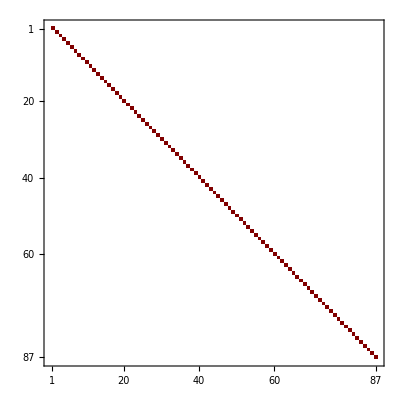

```mathematica
LorenzoScalingRelation=DEqMatrices*KinematicVarsSymmetric//Total//FermatTogether;
LorenzoScalingRelation//MatrixPlot
```

Integrability Condition (True)

```mathematica
IntegrabilityConditionSatisfiedQ=Table[MapThread[IntegrabilityConditionQ[{DEqMatrices[[i]],#1},{KinematicVarsSymmetric[[i]],#2}]&,{DEqMatrices[[i+1;;]],KinematicVarsSymmetric[[i+1;;]]}],{i,Length[KinematicVarsSymmetric]-1}];

IntegrabilityConditionSatisfiedQ=And@@Flatten[IntegrabilityConditionSatisfiedQ];
Print["DEq matrices satisfy Integrability condition ", IntegrabilityConditionSatisfiedQ]
```

DEq matrices satisfy Integrability condition True

### Transform Lorenzo’s basis to mine

Load + Cross IBP reductions of bubbles (CHECK TADPOLE REDUCTION)

```mathematica
(*DumpGet[MathematicaInputPath<>"DEqMatricesDottedBubbles.mx" ]
DumpGet[MathematicaInputPath<>"LorenzosPreCanonicalMI.mx"]*)
```

```mathematica
RReductionBubbles=Get[$KiraReductionsFolder<>"DottedBubbles.m"]/.RKinematicLorenzoSymmetricVars/.mh2->mH2//Simplify;
RReductionBubblesX12=CrossRuleXIJ[RReductionBubbles,"x12",RMandelstams->RKinematicLorenzoSymmetricVars,IntegralSymbol->Penta];
RReductionBubblesX34=CrossRuleXIJ[RReductionBubbles,"x34",RMandelstams->RKinematicLorenzoSymmetricVars,IntegralSymbol->Penta];
RReductionBubblesX12X34=CrossRuleXIJ[RReductionBubblesX12,"x34",RMandelstams->RKinematicLorenzoSymmetricVars,IntegralSymbol->Penta];

(*Dont put mt2 = 1 because I need the derivative with respect to mt2. *)
RReductionBubbles={RReductionBubbles,RReductionBubblesX12,RReductionBubblesX34,RReductionBubblesX12X34}/.ReduzeShiftsCrossings//Flatten;
Clear[RReductionBubblesX12,RReductionBubblesX12X34,RReductionBubblesX34];

AppendTo[RReductionBubbles,PentaboxGGtoTTHTopologyA[2,0,0,0,0]->-PentaboxGGtoTTHTopologyA[1,0,0,0,0](2-d)/2/mt2];
RReductionLorenzosMI={RReductionBubbles,ReduzeShiftsCrossings}//Flatten;
```

Compute Transformation matrices

```mathematica
(*This is to see which pre canonical master integrals differ between Lorenzo an me.*)
SameVariablesQ[{LorenzosPreCanonicalMI/.ReduzeShiftsCrossings,MasterIntegralsReduze},DebugModus->True];
BubblesLorenzo=Complement[LorenzosPreCanonicalMI/.ReduzeShiftsCrossings,MasterIntegralsReduze];
```

The following variables are in Expression1 but not in Expression2: {PentaboxGGtoTTHTopologyA(0,0,1,0,2),PentaboxGGtoTTHTopologyA(0,1,0,0,2),PentaboxGGtoTTHTopologyA(0,2,0,1,0),PentaboxGGtoTTHTopologyA(2,0,0,0,0),PentaboxGGtoTTHTopologyA(2,0,0,0,1),PentaboxGGtoTTHTopologyA(2,0,0,1,0),PentaboxGGtoTTHTopologyA(2,0,1,0,0),PentaboxGGtoTTHTopologyAx12(0,0,1,0,2),PentaboxGGtoTTHTopologyAx12(2,0,1,0,0),PentaboxGGtoTTHTopologyB(0,2,0,0,1),PentaboxGGtoTTHTopologyBx12(0,2,0,0,1),PentaboxGGtoTTHTopologyC(0,0,2,0,1),PentaboxGGtoTTHTopologyC(2,0,1,0,0)}

The following variables are in Expression2 but not in Expression1: {PentaboxGGtoTTHTopologyA(0,1,0,1,0),PentaboxGGtoTTHTopologyA(1,0,0,0,0),PentaboxGGtoTTHTopologyA(1,0,0,0,1),PentaboxGGtoTTHTopologyA(1,0,0,1,0),PentaboxGGtoTTHTopologyA(1,0,1,0,0),PentaboxGGtoTTHTopologyAx12(1,0,1,0,0),PentaboxGGtoTTHTopologyAx12x34(1,0,0,1,0),PentaboxGGtoTTHTopologyAx12x34(1,0,1,0,0),PentaboxGGtoTTHTopologyAx34(1,0,1,0,0),PentaboxGGtoTTHTopologyB(0,1,0,0,1),PentaboxGGtoTTHTopologyBx12(0,1,0,0,1),PentaboxGGtoTTHTopologyC(0,0,1,0,1),PentaboxGGtoTTHTopologyC(1,0,1,0,0)}

```mathematica
TransformedDEQ=MapThread[DEqOldToNewBasis[LorenzosPreCanonicalMI,MasterIntegralsReduze,RReductionLorenzosMI,#1,#2,InverseReductionsQ->True]&,{DEqMatrices,KinematicVarsSymmetric}];
```

```mathematica
TTHDumpSafe["RReductionLorenzosMI"]
```

Check scaling relation + integrability

```mathematica
ScalingRelationTransformedDEQ=(TransformedDEQ*KinematicVarsSymmetric)//Total//FermatTogether;
```

FLink created! You can read information on FInit, FEval, FAddVars and FClose

```mathematica
ScalingRelationTransformedDEQ//MatrixPlot
```

-Graphics-

```mathematica
IntegrabilityConditionSatisfiedQ=Table[MapThread[IntegrabilityConditionQ[{TransformedDEQ[[i]],#1},{KinematicVarsSymmetric[[i]],#2}]&,{TransformedDEQ[[i+1;;]],KinematicVarsSymmetric[[i+1;;]]}],{i,Length[KinematicVarsSymmetric]-1}];

IntegrabilityConditionSatisfiedQ=And@@Flatten[IntegrabilityConditionSatisfiedQ];
Print["DEq matrices satisfy Integrability condition ", IntegrabilityConditionSatisfiedQ]
```

DEq matrices satisfy Integrability condition True

### Change to canonical basis

Derivative square roots

```mathematica
SquareRootSet=CanonicalBasisSquareRootEuclideanCrossedISym;

RSquaredRoots={#[[1]]^2->#[[2]]^2,#[[1]]^(-2)->#[[2]]^(-2)}&/@SquareRootSet/.RKinematicLorenzoSymmetricVars//Flatten;

SquareRootSet=SquareRootSet/.RReconstructMass/.RKinematicLorenzoSymmetricVars/.{√x__->√Factor[Together[x]]};
SquareRootSymbols=SquareRootSet[[;;,1]];

RootsToRootFunctions=#->#@@KinematicVarsSymmetric&/@SquareRootSymbols;
RootFunctionsToRoots=Reverse/@RootsToRootFunctions;

(*CanonicalBasisSquareRootsCrossedISym=Assuming[mt2>0,Refine[Together[CanonicalBasisSquareRootsCrossedI/.RReconstructMass]]]/.RKinematicLorenzoSymmetricVars;*)
RDerivativeSquareRoots=Table[D[#/.RootsToRootFunctions,KinVar]->DRootSymbol[#,KinVar,SquareRootSet]&/@SquareRootSymbols,{KinVar,KinematicVarsSymmetric}]//Flatten;

RSquareRootsToFermat=#->ToExpression[ToLowerCase[ToString[#]]]&/@SquareRootSymbols;
RSquareRootsToFermatI=Reverse/@RSquareRootsToFermat;
```

DRoot

```mathematica
DRoot::usage"Takes derivative of expression keeping the square root as symbol. 
Input: expression with symbolic square roots, var to take derivative, RRootExpressions RootSymbol -> √(...) (analytic expression)
Return: derivative with root symbol
"
```

```mathematica
DRoot[expr_,Var_,RRootExpressions_]:=Module[
{SquareRoots,RootsToRootFunctions,RootFunctionsToRoots,RDerivativeSquareRoots,DExpr},

SquareRoots=RRootExpressions[[;;,1]];
RootsToRootFunctions=#->#@Var&/@SquareRoots;
RootFunctionsToRoots=Reverse/@RootsToRootFunctions;

RDerivativeSquareRoots=D[#/.RootsToRootFunctions,Var]->DRootSymbol[#,Var,RRootExpressions]&/@SquareRoots//Flatten;

DExpr=D[expr/.RootsToRootFunctions,Var]/.RDerivativeSquareRoots/.RootFunctionsToRoots;

Return[DExpr];

]
```

```mathematica
CanonicalBasisSquareRootEuclideanCrossedISym/.FivePointMandelstamReplacementsLorenzoForm;
DRoot[R1,mH2,%]
```

(mH2-2)/R1

```mathematica
{RootSymbols,RootExpressions}={CanonicalBasisSquareRootEuclideanCrossedISym[[;;,1]],CanonicalBasisSquareRootEuclideanCrossedISym[[;;,2]]};

RootPairs=Times@@@Select[Tuples[RootSymbols[[;;-2]],2],Not[#[[1]]===#[[2]]]&]//Union;
AnalyticRootPairs=RootPairs/.CanonicalBasisSquareRootEuclideanCrossedISym//PhySquareRootProduct;
RRootProducts=MapThread[Rule,{RootPairs,AnalyticRootPairs}];
RRootProductsI=Reverse/@RRootProducts;
```

Redefine Canonical basis obtained by Nicolas

```mathematica
DumpGet[MathematicaInputPath<>"CanonicalBasisMICrossed.mx"];

RedefinedCanonicalBasisCrossed=CanonicalBasisMICrossed;
RedefinedCanonicalBasisCrossed[[1]]=CanonicalBasisMICrossed[[1]]*ϵ;
```

Transformation matrices

```mathematica
DumpGet[MathematicaInputPath<>"TransformedDEQ.mx"];
TransformationPreCanonicalToCanonical=(Coefficient[#/.RKinematicLorenzoSymmetricVars,MasterIntegralsReduze]&/@RedefinedCanonicalBasisCrossed)/.{ϵ->(4-d)/2,mt2->1};
(*TransformationPreCanonicalToCanonical=T3/.{ϵ->(4-d)/2,mt2->1}/.RKinematicLorenzoSymmetricVars;*)
TransformationCanonicalToPreCanoical=TransformationPreCanonicalToCanonical//Inverse;
DTransformationPreCanonicalToCanonical=D[TransformationPreCanonicalToCanonical/.RootsToRootFunctions,#]/.RDerivativeSquareRoots/.RootFunctionsToRoots/.mt2->1&/@KinematicVarsSymmetric;
```

Perform basis transformation (Fermat)

```mathematica
(*Change to canonical basis*)
{Start,Stop}={1,87};
CanonicalDEq=Table[BasisTransformDEq[TransformedDEQ[[i,;;Stop,;;Stop]]/.mt2->1,TransformationPreCanonicalToCanonical[[;;Stop,;;Stop]],TransformationCanonicalToPreCanoical[[;;Stop,;;Stop]],DTransformationPreCanonicalToCanonical[[i,;;Stop,;;Stop]]]/.RSquareRootsToFermat/.mt2->1,{i,2,7}]//FermatTogether;

(*Remove √(...)^2 (stored in symbols) *)
RSquaredRootsFermat=RSquaredRoots/.RSquareRootsToFermat;
CanonicalDEq=CanonicalDEq/.RSquaredRootsFermat/.mt2->1//FermatTogether;
CanonicalDEq=CanonicalDEq/.d->4-2ϵ//Factor;
```

FLink created! You can read information on FInit, FEval, FAddVars and FClose

FLink created! You can read information on FInit, FEval, FAddVars and FClose

Perform basis transformation (Mathematica, slow)

```mathematica
RSquareRootsToFermat=#->ToExpression[ToLowerCase[ToString[#]]]&/@SquareRootSymbols;
RSquareRootsToFermatI=Reverse/@RSquareRootsToFermat;

(*Change to canonical basis*)
CanonicalDEq=BasisTransformDEq[TransformedDEQ[[3]],TransformationPreCanonicalToCanonical,TransformationCanonicalToPreCanoical,DTransformationPreCanonicalToCanonical[[3]]][[16;;17,;;]]/.RSquareRootsToFermat/.mt2->1//Together;

(*Remove √(...)^2 (stored in symbols) *)
RSquaredRootsFermat=RSquaredRoots/.RSquareRootsToFermat;
CanonicalDEq=CanonicalDEq/.RSquaredRootsFermat/.mt2->1//Together;
CanonicalDEq=CanonicalDEq/.d->4-2ϵ/.RSquareRootsToFermatI//Factor;
```

Check epsilon factorization

Analytic check

```mathematica
NonEpsilonFactorizedEntries=NonZeroPostions/@((Coefficient[CanonicalDEq/.d->4-2ϵ,ϵ,1]*ϵ-(CanonicalDEq/.d->4-2ϵ))//Together);
EpsilonFactorizedQ=And@@(#=={}&/@NonEpsilonFactorizedEntries);
Print["DEq is in ϵ form: ", EpsilonFactorizedQ]
If[EpsilonFactorizedQ,TTHDumpSafe["CanonicalDEq",FileNameExtension->"_Crossed"]; Clear[NonEpsilonFactorizedEntries,EpsilonFactorizedQ]]
```

DEq is in ϵ form: True

Numeric check (including transformation)

```mathematica
AllRealQ=False;
While[Not[AllRealQ],

TestPoint=NRandomEvaluation[KinematicVarsSymmetric[[2;;]],OutputStyle->"Rules",MinNumber->-1000000,MaxNumber->-100];
AppendTo[TestPoint,mt2->1];

TestPoint={CanonicalBasisSquareRootEuclideanCrossedISym/.TestPoint,TestPoint}//Flatten;
AllRealQ=And@@Internal`RealValuedNumericQ/@Flatten[TransformationCanonicalToPreCanoical/.TestPoint/.d->17];
]

Clear[AllRealQ]

(*Change to canonical basis*)
NCanonicalDEq=Table[NBasisTransformDEq[TransformedDEQ[[i]],TransformationPreCanonicalToCanonical,TransformationCanonicalToPreCanoical,DTransformationPreCanonicalToCanonical[[i]],NReplacement->TestPoint][[;;,;;]],{i,2,7}]//Together;

(*Check if DEq is in ϵ form*)
NonEpsilonFactorizedEntries=NonZeroPostions/@((Coefficient[NCanonicalDEq/.d->4-2ϵ,ϵ,1]*ϵ-(NCanonicalDEq/.d->4-2ϵ))//Together);
EpsilonFactorizedQ=And@@(#=={}&/@NonEpsilonFactorizedEntries);
Print["DEq is in ϵ form: ", EpsilonFactorizedQ]

If[EpsilonFactorizedQ,Clear[NCanonicalDEq,NonEpsilonFactorizedEntries,EpsilonFactorizedQ]];
```

DEq is in ϵ form: True

## Find Dlog form

### Functions for dlog form

ListToMatrixPosition

```mathematica
ListToMatrixPosition[ListPosition_,DimMatrix_]:=Module[
{RowIndex,ColumnIndex},

RowIndex=ListPosition/DimMatrix[[2]];
If[Not[IntegerQ[RowIndex]],RowIndex=Floor[RowIndex]+1];

ColumnIndex=ListPosition-(RowIndex-1)*DimMatrix[[2]];

Return[{RowIndex,ColumnIndex}]

]


ArrayReshape[Range[50],{5,10}][[ListToMatrixPosition[#,{5,10}][[1]],ListToMatrixPosition[#,{5,10}][[2]]]]-#&/@Range[50]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

ToSymbolicMatrix

```mathematica
Options[ToSymbolicMatrix]={Symbolname->Symb};
ToSymbolicMatrix[Matrix_,optn:OptionsPattern[{Symbolname->Symb}]]:=Module[

{FlattenedMatrix,MatrixDim,ProportionalityList,SymbolicMatrix,row,column,position},

FlattenedMatrix=Matrix//Flatten;
MatrixDim=Matrix//Dimensions;
SymbolicMatrix=ConstantArray[0,MatrixDim];

(*Check proportionality between matrix entries*)
ProportionalityList=
Table[
If[ZeroQ[FlattenedMatrix[[i1]]],{i1,{}},{i1,PropToListElements[FlattenedMatrix[[i1]],FlattenedMatrix[[i1+1;;]]]}],{i1,Length[FlattenedMatrix]}
];

(*Reverse is convenient for later to avoid the problem of double counting. *)
ProportionalityList=ProportionalityList//Reverse;


(*Replace entries with symbol, or symbol*proportionality constant*)
Do[
If[ZeroQ[FlattenedMatrix[[elem[[1]]]]],

Nothing[],

{row,column}=ListToMatrixPosition[elem[[1]],MatrixDim];
SymbolicMatrix[[row,column]]=OptionValue[Symbolname][row,column];


If[Not[EmptyListQ[elem[[2]]]],
position=ListToMatrixPosition[#,MatrixDim]&/@(elem[[2,;;,1]]+elem[[1]]);

Do[
SymbolicMatrix[[position[[j,1]],position[[j,2]]]]=OptionValue[Symbolname][row,column]*elem[[2,j,2]],
{j,Range[Length[position]]}]

]

]

,{elem,ProportionalityList}];


Return[SymbolicMatrix]
]
```

ToSymbolicMatrixCrossing

```mathematica
Options[ToSymbolicMatrixCrossing]={Symbolname->Symb,SymmetryRelations->{}};
ToSymbolicMatrixCrossing[Matrix_,CrossingString_,optn:OptionsPattern[{Symbolname->Symb,SymmetryRelations->{}}]]:=Module[

{FlattenedMatrix,CrossedFlattenedMatrix,MatrixDim,ProportionalityList,SymbolicMatrix,row,column,position},

FlattenedMatrix=Matrix//Flatten;
MatrixDim=Matrix//Dimensions;
SymbolicMatrix=ConstantArray[0,MatrixDim];



CrossedFlattenedMatrix=CrossXIJ[FlattenedMatrix,CrossingString]/.OptionValue[SymmetryRelations];

(*Check proportionality between matrix entries*)
ProportionalityList=
Table[
If[ZeroQ[FlattenedMatrix[[i1]]],{i1,{}},{i1,PropToListElements[FlattenedMatrix[[i1]],CrossedFlattenedMatrix[[i1+1;;]]]}],{i1,Length[FlattenedMatrix]}
];

(*Reverse is convenient for later to avoid the problem of double counting. *)
ProportionalityList=ProportionalityList//Reverse;


(*Replace entries with symbol, or symbol*proportionality constant*)
Do[
If[ZeroQ[FlattenedMatrix[[elem[[1]]]]],

Nothing[],

{row,column}=ListToMatrixPosition[elem[[1]],MatrixDim];
SymbolicMatrix[[row,column]]=OptionValue[Symbolname][row,column];


If[Not[EmptyListQ[elem[[2]]]],
position=ListToMatrixPosition[#,MatrixDim]&/@(elem[[2,;;,1]]+elem[[1]]);

Do[
CrossedSymbolName=ToString[OptionValue[Symbolname]]<>CrossingString//ToExpression;
SymbolicMatrix[[position[[j,1]],position[[j,2]]]]=CrossedSymbolName[row,column]*elem[[2,j,2]],
{j,Range[Length[position]]}]

]

]

,{elem,ProportionalityList}];


Return[SymbolicMatrix]
]
```

DLogEntryAnsatz (this function is currently out of use)

```mathematica
Option[DLogEntryAnsatz]={CoeffList->False};
DLogEntryAnsatz[DLogList_,optn:OptionsPattern[{CoeffList->False}]]:=Module[
{Coeffs,Ansatz},

Coeffs=MatchingCoeff/@Range[Length[DLogList]];
Ansatz=MapThread[Times,{Coeffs,DLogList}]//Total;

If[OptionValue[CoeffList],Return[{Ansatz,Coeffs}]];
Return[Ansatz]
]
```

GetMatchEq (this function is currently out of use)

```mathematica
Option[GetMatchEq]={DimRegVar->ϵ};
GetMatchEq[DEqEntry_,DLogAnsatz_,KinVar_,optn:OptionsPattern[{DimRegVar->ϵ}]]:=Module[
{MatchEq},

MatchEq=DEqEntry-D[DLogAnsatz,KinVar]/.OptionValue[DimRegVar]->1;

Return[MatchEq];

]
```

MatchCoefficients (this function is currently out of use)

```mathematica
Options[MatchCoefficients]->{Iter->1,MaxIter->30};
MatchCoefficients[MatchEq_,CoefficientSymbols_,optn:OptionsPattern[{Iter->1,MaxIter->10}]]:=Module[
{NMatchEq,CoeffsTo0,CoefficientGuess,RCoefficientGuess,MatchEqQ},


If[OptionValue[Iter]>OptionValue[MaxIter], Print["Max iteration reached. Try with larger iteration."]; Return[$Failed]];

CoeffsTo0=#->0&/@CoefficientSymbols;
NMatchEq=NRandomEvaluation[MatchEq,IgnoreVariables->CoefficientSymbols];

CoefficientGuess=Flatten[{Coefficient[NMatchEq,CoefficientSymbols],(NMatchEq/.CoeffsTo0)}]//N//FindIntegerNullVector;
RCoefficientGuess=MapThread[Rule,{CoefficientSymbols,CoefficientGuess[[;;-2]]}];

(*Numeric check *)
MatchEqQ=0==Simplify[NRandomEvaluation[MatchEq/.RCoefficientGuess]];

If[MatchEqQ,

(*Analytic check: *)
MatchEqQ=0===Simplify[MatchEq/.RCoefficientGuess];

If[MatchEqQ,
Return[RCoefficientGuess],

(*Else if 2*)
Return[MatchCoefficients[MatchEq,CoefficientSymbols,Iter->OptionValue[Iter]+1,MaxIter->OptionValue[MaxIter]]]
],

(*Else if 1*)
Return[MatchCoefficients[MatchEq,CoefficientSymbols,Iter->OptionValue[Iter]+1,MaxIter->OptionValue[MaxIter]]]

];
]
```

EntryGuessToDLogEntry  (this function is currently out of use)

```mathematica
EntryGuessToDLogEntry[DEqEntry_,LetterAnsatz_,KinVar_]:=Module[

{AnsatzDLogForm,Coeffs,MatchEq,RCoefficients,DLogEntry},

If[MatchQ[LetterAnsatz,{Log[x_String]}],Print["No dLog ansatz possible -> bad functions, integration timeout"]; Return[$Failed]];

{AnsatzDLogForm,Coeffs}=DLogEntryAnsatz[LetterAnsatz,CoeffList->True];
MatchEq=GetMatchEq[DEqEntry,AnsatzDLogForm,KinVar];
RCoefficients=MatchCoefficients[MatchEq,Coeffs];

If[FailureQ[RCoefficients],Return[$Failed]];

DLogEntry=AnsatzDLogForm/.RCoefficients;
Return[DLogEntry]

]
```

### Pick Topology A

```mathematica
DumpGet[MathematicaInputPath<>"CanonicalDEq_Crossed.mx"];
CanonicalDEqTopoA=CanonicalDEq[[;;,;;18,;;18]]/.ϵ->1/.RSquareRootsToFermatI;
DimTopoA=CanonicalDEqTopoA[[1]]//Dimensions;
Clear[CanonicalDEq]
```

### Entries modulo constant prefactor and crossings

```mathematica
SymbolicCanonicalDEq=ToSymbolicMatrix[CanonicalDEqTopoA[[6]],Symbolname->DEqS34];
IndependentEntries=List@@@Variables[SymbolicCanonicalDEq];

(*Keep only independent entries*)
DummyMatrix=ConstantArray[0,DimTopoA];
Do[DummyMatrix[[entry[[1]],entry[[2]]]]=CanonicalDEqTopoA[[6,entry[[1]],entry[[2]]]],{entry,IndependentEntries}];

SymbolicDummyMatrixX12=ToSymbolicMatrixCrossing[DummyMatrix,"x12",SymmetryRelations->SymmetryRelationsCanonicalSquareRoots];
IndependentEntriesX12=List@@@Select[Variables[SymbolicDummyMatrixX12],Not[InvolvesVarQ[#,x12]]&]//EchoLength;

(*Keep only independent entries*)
DummyMatrix=ConstantArray[0,DimTopoA];
Do[DummyMatrix[[entry[[1]],entry[[2]]]]=CanonicalDEqTopoA[[6,entry[[1]],entry[[2]]]],{entry,IndependentEntriesX12}];

SymbolicDummyMatrixX12X34=ToSymbolicMatrixCrossing[DummyMatrix,"x12x34",SymmetryRelations->SymmetryRelationsCanonicalSquareRoots];
IndependentEntriesX12X34=List@@@Select[Variables[SymbolicDummyMatrixX12X34],Not[InvolvesVarQ[#,x12x34]]&]//EchoLength;

(*Keep only independent entries*)
DummyMatrix=ConstantArray[0,DimTopoA];
Do[DummyMatrix[[entry[[1]],entry[[2]]]]=CanonicalDEqTopoA[[6,entry[[1]],entry[[2]]]],{entry,IndependentEntriesX12X34}];

SymbolicDummyMatrixX34=ToSymbolicMatrixCrossing[DummyMatrix,"x34",SymmetryRelations->SymmetryRelationsCanonicalSquareRoots];
IndependentEntriesX34=List@@@Select[Variables[SymbolicDummyMatrixX34],Not[InvolvesVarQ[#,x12x34]]&]//EchoLength;

(*Keep only independent entries*)
DummyMatrix=ConstantArray[0,DimTopoA];
Do[DummyMatrix[[entry[[1]],entry[[2]]]]=CanonicalDEqTopoA[[6,entry[[1]],entry[[2]]]],{entry,IndependentEntriesX34}];
```

Length:   23

Length:   19

Length:   19

### Guess Ansatz

```mathematica
DLogGuess=GuessDLogLetterAnsatz[DummyMatrix/.CanonicalBasisSquareRootEuclideanCrossedISym,s34,MaxIntegrateTime->60];
```

Maximal iteration reached -> Try with larger iteration number. Current Value: 200

Use random variables.

Warning Unaibled option ForceNumberQ. Nb. might not be rational!

Maximal iteration reached -> Try with larger iteration number. Current Value: 200

Use random variables.

Warning Unaibled option ForceNumberQ. Nb. might not be rational!

Maximal iteration reached -> Try with larger iteration number. Current Value: 200

Use random variables.

Warning Unaibled option ForceNumberQ. Nb. might not be rational!

Warning Unaibled option ForceNumberQ. Nb. might not be rational!

Warning Unaibled option ForceNumberQ. Nb. might not be rational!

Maximal iteration reached -> Try with larger iteration number. Current Value: 200

Use random variables.

Warning Unaibled option ForceNumberQ. Nb. might not be rational!

Simplify::time: Time spent on a transformation exceeded 300. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

Maximal iteration reached -> Try with larger iteration number. Current Value: 200

Use random variables.

Warning Unaibled option ForceNumberQ. Nb. might not be rational!

```mathematica
KinVarI=1;
Var=KinematicVarsSymmetric[[KinVarI+1]];
GuessName = "DLogGuess_Part_Var_" <> ToString[Var] <> "_" <> ToString[KinVarI];
DumpGet[MathematicaInputPath<>"DLogGuess/"<>GuessName];
```

```mathematica
DLogGuess//Length
RemovedBadFunctions=If[InvolvesVarQ[#,"Bad function unable to guess"]||InvolvesVarQ[#,"Integration timeout"],Nothing[],#]&/@DLogGuess//Echo[#,"Nb. of guessed entries:",Length]&;
RemovedBadFunctions=If[InvolvesVarQ[#,"No rational prefactor"],Nothing[],#]&/@RemovedBadFunctions//Echo[#,"Nb. of guessed entries:",Length]&;
RemovedBadFunctions=If[InvolvesVarQ[#,"Unknown function"],Nothing[],#]&/@RemovedBadFunctions//Echo[#,"Nb. of guessed entries:",Length]&;
```

19

Nb. of guessed entries:  15

Nb. of guessed entries:  15

Nb. of guessed entries:  15

```mathematica
IntegrationTimeouts=DLogGuess[[Position[DLogGuess,"Integration timeout"][[;;,1]]]][[;;,1]]//EchoLength;
BadFunctionPositions=DLogGuess[[Position[DLogGuess,"Bad function unable to guess"][[;;,1]]]][[;;,1]]//Union//EchoLength;
```

Length:   1

Length:   3

### Change variables for DEq

```mathematica
DEqMatrixChangeVar[OldVar_,NewVar_,ROldToNewVar_]:=Module[
{DerivativeChangeMatrix,DerivativeVector,DEqNewVar},

DerivativeChangeMatrix=D[OldVar/.ROldToNewVar,{NewVar}]//Transpose;
DerivativeVector=Global`DEqMatrix/@OldVar;

DEqNewVar=DerivativeChangeMatrix.DerivativeVector;
Return[DEqNewVar]

]
```

```mathematica
(*This is a function from Max*)
vartransform[sys_List,vartrans_List,oldvar_List,newvar_List]:=
Module[{ii,jj,l=Length[sys]},
If[(l===Length[vartrans]&&l===Length[oldvar]&&l===Length[newvar]),Nothing[],Return[sys]];
Return[
Table[
Sum[(sys[[ii]]/.vartrans)*D[oldvar[[ii]]/.vartrans,newvar[[jj]]],{ii,1,l}],
{jj,1,l}]];
];
```

```mathematica
(*The idea is that I use a different set of variables for the DEq entries for which I get bad functions. In this variables the DEq should be simpler. The motivation for this is that some of the square roots are very simple in a specific choice of variables. *)


(*Linear combination of old derivative matrix giving the new derivative matrices: *)
DEqMatrixChangeVar[KinematicVarsSymmetric[[2;;]],KinematicVarsLorenzo,FivePointMandelstamReplacementsLorenzoForm]//TableForm
```

DEqMatrix(s12)-DEqMatrix(s13)-DEqMatrix(s24)+DEqMatrix(s34)
DEqMatrix(s14)-DEqMatrix(s24)
DEqMatrix(s23)-DEqMatrix(s13)
DEqMatrix(s24)-DEqMatrix(s34)
DEqMatrix(s13)-DEqMatrix(s34)
DEqMatrix(s34)

Works for BadFunctions Entry 1 and 3

```mathematica
(*Test example: *)
TestPosition=BadFunctionPositions[[3]]

(*Take new DEq in s12*)
TestEntryNewVar=CanonicalDEqTopoA[[1,TestPosition[[1]],TestPosition[[2]]]]-CanonicalDEqTopoA[[2,TestPosition[[1]],TestPosition[[2]]]]-CanonicalDEqTopoA[[5,TestPosition[[1]],TestPosition[[2]]]]+CanonicalDEqTopoA[[6,TestPosition[[1]],TestPosition[[2]]]]/.FivePointMandelstamReplacementsLorenzoForm//Together//Factor//FullSimplify;

IntegratedDEqEntry=Integrate[TestEntryNewVar/.CanonicalBasisSquareRootEuclideanCrossedISym/.FivePointMandelstamReplacementsLorenzoForm,s12];
DLogLetterAnsatz=FunctionBasedLetterGuess/@(FunctionSplit[IntegratedDEqEntry])//ThirdBinomicRootSimplify//PhySquareRootProduct;

roots=RootList[DLogLetterAnsatz]/.RKinematicLorenzoSymmetricVars/.mt2->1;

RRootsToSymbol=Table[MapThread[RootToSymbolRule[root,#1,#2]&,{RootSymbols,RootExpressions}],{root,roots}];

roots=roots/.RRootsToSymbol//RootList;
RRootsToSymbol={RRootsToSymbol,Table[MapThread[RootToSymbolRule[root,#1,#2]&,{RootPairs,AnalyticRootPairs}],{root,roots}]}//Flatten//Union;

DLogLetterAnsatz=DLogLetterAnsatz/.RKinematicLorenzoSymmetricVars/.mt2->1/.RRootsToSymbol/.FivePointMandelstamReplacementsLorenzoForm//FullSimplify;
```

Works for BadFunctions Entry 2

```mathematica
(*Test example: *)
TestPosition=BadFunctionPositions[[2]]

(*Take new DEq in s45*)
TestEntryNewVar=CanonicalDEqTopoA[[2,TestPosition[[1]],TestPosition[[2]]]]-CanonicalDEqTopoA[[6,TestPosition[[1]],TestPosition[[2]]]]/.FivePointMandelstamReplacementsLorenzoForm//Together//FullSimplify//Echo;

IntegratedDEqEntry=Integrate[TestEntryNewVar/.CanonicalBasisSquareRootEuclideanCrossedISym/.FivePointMandelstamReplacementsLorenzoForm,s45];
DLogLetterAnsatz=FunctionBasedLetterGuess/@(FunctionSplit[IntegratedDEqEntry])//ThirdBinomicRootSimplify//PhySquareRootProduct;

roots=RootList[DLogLetterAnsatz]/.RKinematicLorenzoSymmetricVars/.mt2->1;

RRootsToSymbol=Table[MapThread[RootToSymbolRule[root,#1,#2]&,{RootSymbols,RootExpressions}],{root,roots}];

roots=roots/.RRootsToSymbol//RootList;
RRootsToSymbol={RRootsToSymbol,Table[MapThread[RootToSymbolRule[root,#1,#2]&,{RootPairs,AnalyticRootPairs}],{root,roots}]}//Flatten//Union;

DLogLetterAnsatz=DLogLetterAnsatz/.RKinematicLorenzoSymmetricVars/.mt2->1/.RRootsToSymbol/.FivePointMandelstamReplacementsLorenzoForm//FullSimplify;
```

{7,3}

-(2 (mH2-4) mH2 R3x34)/(R1 (s45-1) (mH2^2-2 mH2 (s45+1)+(s45-1)^2))

IntegrationTimeout Entry (works needs simplification of letters)

```mathematica
(*Test example: *)
TestPosition=IntegrationTimeouts[[1]]

(*Take new DEq in s35*)
TestEntryNewVar=CanonicalDEqTopoA[[5,TestPosition[[1]],TestPosition[[2]]]]-CanonicalDEqTopoA[[6,TestPosition[[1]],TestPosition[[2]]]]//Together//Factor//FullSimplify//Echo;

IntegratedDEqEntry=Integrate[TestEntryNewVar/.CanonicalBasisSquareRootEuclideanCrossedISym/.FivePointMandelstamReplacementsLorenzoForm,s35];
DLogLetterAnsatz=FunctionBasedLetterGuess/@(FunctionSplit[IntegratedDEqEntry])//ThirdBinomicRootSimplify//PhySquareRootProduct;

roots=RootList[DLogLetterAnsatz]/.RKinematicLorenzoSymmetricVars/.mt2->1;

RRootsToSymbol=Table[MapThread[RootToSymbolRule[root,#1,#2]&,{RootSymbols,RootExpressions}],{root,roots}];

roots=roots/.RRootsToSymbol//RootList;
RRootsToSymbol={RRootsToSymbol,Table[MapThread[RootToSymbolRule[root,#1,#2]&,{RootPairs,AnalyticRootPairs}],{root,roots}]}//Flatten//Union;

DLogLetterAnsatz=DLogLetterAnsatz/.RKinematicLorenzoSymmetricVars/.mt2->1/.RRootsToSymbol/.FivePointMandelstamReplacementsLorenzoForm//FullSimplify;
```

{9,7}

-((R11 (2 s13 (s12+(s23-2) (s14+s24-2))-s12 s13 s34-2 s12 (s14-s23+s24)-s12 (s23-2) s34+s13^2 (s14+s24-2)+s23 (s14 (s23-4)+s23 (s24-2)-4 s24)+4 (s14+2 s23+s24-2)) (4 s12+4 s13-s14^2-2 s14 (s24+s34-4)+4 (s23+2 s24+2 s34-5)-(s24+s34)^2))/(R3x34 ((s13+s23-2) (s14+s24-2)-s12 (s34-4)) ((s13+s23-2) (s14+s24-2)-s12 s34) (-s34 (4 s12+(s13+s23-2) (s14+s24-2))+s12 s34^2+(s13+s14+s23+s24-4)^2)))

```mathematica
TestExpr=GuessToAnsatz[DLogLetterAnsatz[[;;,1]],DLogLetterAnsatz[[;;,2]]];
RRoot=CanonicalBasisSquareRootEuclideanCrossedISym/.FivePointMandelstamReplacementsLorenzoForm;
RRootSquare=MapThread[#1^2->#2^2&,{RRoot[[;;,1]],RRoot[[;;,2]]}];
(*RRootSquare={RRootSquare,1/#[[1]]->1/#[[2]]&/@RRootSquare}//Flatten;*)
DExpr=PowerSymbolSimplifyRoot[Together[DRoot[TestExpr,s12,RRoot]],RRootSquare]//FullSimplify;
```

```mathematica
PowerSymbolSimplifyRoot[DExpr/TestEntryNewVar,RRootSquare]//Factor
```

-1

### Functions for semi analytic simplifications

DoubleRootQ

```mathematica
DoubleRootQ::usage"Checks if given expression contains double roots √(...+SqrtBox[...])"
```

```mathematica
DoubleRootQ[AlgebraicPolynomial_]:=FreeQ[RootList[AlgebraicPolynomial]^2,Power[x_,Rational[1,2]]]//Not
```

NFullSimplify

```mathematica
NFullSimplify::usage"Input: expression, Rules Vars -> Numbers. Inserts numeric values and simplifies expression. "
```

Input: expression, Rules Vars -> Numbers. Inserts numeric values and simplifies expression.  NFullSimplify::usage

```mathematica
NFullSimplify[expr_,NTestPoint_]:=expr/.NTestPoint//FullSimplify
```

NGuessRoot

```mathematica
NGuessRoot::usage"Input: √Number, List of RootSymbols, List of analytic expressions corresponding to root symbols, NumericTest point for which √number was obtained.
Output: Matches input against analytic expressions. If successful returns corresponding symbol.
"
```

```mathematica
Options[NGuessRoot]={PrintOut->False};
NGuessRoot[NValueRoot_,PossibleRootSymbols_,PossibleRootExpr_,NTestPoint_,optn:OptionsPattern[{PrintOut->False}]]:=Module[
{RootCandidatesPos,RootCandidates},

(*Use replacement rule to remove prefactor in front of root*)
RootCandidatesPos=Flatten[Position[PossibleRootExpr/.NTestPoint/.{x_*√y_->√y},NValueRoot]];
If[EmptyListQ[RootCandidatesPos],
If[OptionValue[PrintOut],Print["No match found"]];
Return[$Failed]
];

RootCandidates=PossibleRootSymbols[[RootCandidatesPos]];
Return[RootCandidates]

]
```

### Main bulk Simplify Guessed letters

```mathematica
RootsSimplified=RemovedBadFunctions//ThirdBinomicRootSimplify;
roots=RootsSimplified//RootList;

RRoots=Table[MapThread[RootToSymbolRule[root,#1,#2]&,{RootSymbols,RootExpressions}],{root,roots}]//Flatten//Union;

RootsSimplified=RootsSimplified/.RRoots;
roots=RootsSimplified//RootList;

RRoots=Table[MapThread[RootToSymbolRule[root,#1,#2]&,{RootPairs,AnalyticRootPairs}],{root,roots}]//Flatten//Union;
RootsSimplified=RootsSimplified/.RRoots;
```

#### Exceptions

```mathematica
ProblematicPositions=Position[RootsSimplified,#][[;;,1]]&/@RootList[RootsSimplified]
Print["These are the problematic candidates: ",ProblematicPositions];

ProblematicLetters=RootsSimplified[[ProblematicPositions[[1,1]]]][[2,3;;4,2]];

RDummyRoots=Thread[Rule[RootList[ProblematicLetters],{DummyR1,DummyR2}]];
RDummyRootsI=Reverse/@RDummyRoots;

ProblematicLetters=ProblematicLetters/.RDummyRoots//FullSimplify
```

```mathematica
(*The product of the two roots is rational:*)
DummyR1^2*DummyR2^2/.RDummyRootsI//Expand//FullSimplify;
RDummyRootsProduct=DummyR1*DummyR2->4 s12 (s13-s14+s23-s24) (s13+s14+s23+s24-4) (s12^2 (s34-4) s34-2 s12 (s34-2) (s13+s23-2) (s14+s24-2)+(s13+s23-2)^2 (s14+s24-2)^2);

(*Check: must be 1*)
(DummyR1*DummyR2/.RDummyRootsProduct)^2/%%
```

1

```mathematica
RRootSquare=MapThread[#1^2->#2^2&,{RootSymbols,RootExpressions}];
(*From the coefficents in front of the Dlogs it follows that the arguments must be multiplied*)
SimplifiedLetter=Expand[Times@@ProblematicLetters]/.RRootSquare/.RDummyRootsProduct;
```

```mathematica
DummyRDependentPart1=Coefficient[SimplifiedLetter,{DummyR1 R4 R4x34,DummyR2  R4 R4x34}];
DummyRDependentPart2=Coefficient[SimplifiedLetter,{DummyR1 ,DummyR2 }]/.{R4*R4x34->0};
DummyRFreePart=SimplifiedLetter/.{DummyR1->0,DummyR2->0};

Print["Crosscheck: ", 0===Expand[SimplifiedLetter-(DummyRDependentPart1.{DummyR1 R4 R4x34,DummyR2  R4 R4x34}+DummyRDependentPart2.{DummyR1 ,DummyR2}+DummyRFreePart)]];
Divide@@DummyRDependentPart1//Cancel
Divide@@DummyRDependentPart2//Cancel

(*From the coefficents we know that Part 1 comes in the combination (DummyR1 - DummyR2) and Part 2 (DummyR1 + DummyR2) -> Simplify sum and differenc of dummy roots. *)
```

Crosscheck: True

-1

1

```mathematica
testPoint=DummyR1+DummyR2/.RDummyRootsI//NRandomEvaluation[#,OutputStyle->"Rules"]&;

NumericRootSum=NFullSimplify[DummyR1+DummyR2/.RDummyRootsI,testPoint]//RootList;
NumericRootDiff=NFullSimplify[DummyR1-DummyR2/.RDummyRootsI,testPoint]//RootList;

(*Numeric based root guess: *)
RSymb={RootSymbols,RootPairs}//Flatten;
RExpr={RootExpressions,AnalyticRootPairs}//Flatten;

RootAnsatz=NGuessRoot[#,RSymb,RExpr,testPoint]&/@Flatten[{NumericRootSum,NumericRootDiff}]//Flatten

EQRHS={C[1],C[2]}*(RootAnsatz^2)/.CanonicalBasisSquareRootEuclideanCrossedISym;
```

{R11 R4x34,R11 R4}

```mathematica
NumericRootSum
```

{√11439619671432057232534}

```mathematica
NFullSimplify[DummyR1+DummyR2/.RDummyI,testPoint]//RootList;
RootAnsatz=NGuessRoot[%[[1]],RSymb,RExpr,testPoint];

If[Length[RootAnsatz]==1,RootAnsatz=RootAnsatz[[1]],Abort[]];

(*Assumes that DummyR1*DummyR2 = rational*)
EQLHS=Expand[(DummyR1+DummyR2)^2]/.DummyRoots/.RDummyI//Expand;
EQRHS=C[1]RootAnsatz^2/.CanonicalBasisSquareRootEuclideanCrossedISym//Expand;

Sol=Solve[EQLHS==EQRHS,C[1]]//Simplify//Flatten;

If[EmptyListQ[Sol],Abort[]]
Sol=C[1]->PhySquareRootProduct[Sqrt[Sol[[1,2]]]]
SimplifiedResult=C[1]*RootAnsatz/.Sol
```

C[1]→2 (-2+s14+s24)

2 R11 R4x34 (-2+s14+s24)

```mathematica
NFullSimplify[DummyR1-DummyR2/.RDummyI,testPoint]//RootList;
RootAnsatz=NGuessRoot[%[[1]],RSymb,RExpr,testPoint];

If[Length[RootAnsatz]==1,RootAnsatz=RootAnsatz[[1]],Abort[]];

(*Assumes that DummyR1*DummyR2 = rational*)
EQLHS=Expand[(DummyR1-DummyR2)^2]/.DummyRoots/.RDummyI//Expand;
EQRHS=C[1]RootAnsatz^2/.CanonicalBasisSquareRootEuclideanCrossedISym//Expand;

Sol=Solve[EQLHS==EQRHS,C[1]]//Simplify//Flatten;

If[EmptyListQ[Sol],Abort[]]
Sol=C[1]->PhySquareRootProduct[Sqrt[Sol[[1,2]]]];

SimplifiedResult=C[1]*RootAnsatz/.Sol
```

2 R11 R4 (-2+s13+s23)

```mathematica
Options[PowerSymbolSimplifyRoot]={ReductionRules->{},TogetherQ->True};
PowerSymbolSimplifyRoot[expr_,SquaredRootReplacements_,optn:OptionsPattern[{ReductionRules->{},TogetherQ->True}]]:=Module[
{roots,RReductionRules,ReductionPossibleQ,SimplifiedExpression,SimplifiedExpressionN,SimplifiedExpressionD},

roots=SquaredRootReplacements[[;;,1]]//Variables;

If[OptionValue[ReductionRules]==={},
RReductionRules=RReducePowerByTwo[SquaredRootReplacements,roots],
RReductionRules=OptionValue[ReductionRules]
];

If[OptionValue[TogetherQ],
SimplifiedExpression=expr//Together;
SimplifiedExpressionN=(Expand[Numerator[SimplifiedExpression]]/.RReductionRules);
SimplifiedExpressionD=(Expand[Denominator[SimplifiedExpression]]/.RReductionRules);
SimplifiedExpression=SimplifiedExpressionN/SimplifiedExpressionD,

SimplifiedExpression=expr/.RReductionRules;

];


If[OptionValue[TogetherQ],
ReductionPossibleQ=And@@(FreeQ[{SimplifiedExpressionN,SimplifiedExpressionD},#^n_?IntegerQ]&/@roots)//Not,
ReductionPossibleQ=And@@(FreeQ[SimplifiedExpression,#^n_?IntegerQ]&/@roots)//Not;
];



If[ReductionPossibleQ, Return[PowerSymbolSimplifyRoot[SimplifiedExpression,SquaredRootReplacements,ReductionRules->RReductionRules,TogetherQ->OptionValue[TogetherQ]]]];
Return[SimplifiedExpression]

]
```

```mathematica
test=PowerSymbolSimplifyRoot[DExpr,RRootSquare];
```

```mathematica
test//FullSimplify
```

((mH2 (2 s12+s14+s23-s35-s45)+(s14-s23-s35+s45)^2) (mH2^2 (s14-s23-s35+s45) (2 s12+s14+s23-s35-s45)-mH2 (R1 (2 s12^2+2 s12 (s14+s23-s35-s45)+(s14-s35)^2+(s23-s45)^2)+4 (s14-s23-s35+s45) (2 s12+s14+s23-s35-s45))+2 R1 (s14-s23-s35+s45)^2))/(R7x12 (mH2 (s12+s14-s35) (s12+s23-s45)+(s14-s23-s35+s45)^2) (mH2 (2 s12^2+2 s12 (s14+s23-s35-s45)+(s14-s35)^2+(s23-s45)^2)-(s14-s23-s35+s45) (R1 (2 s12+s14+s23-s35-s45)+2 (s14-s23-s35+s45))))

```mathematica
Coefficient[Numerator[test],R7x12,5]
```

```mathematica
PowerSymbolSimplifyRoot[R7x12^4,RRootSquare]//FullSimplify
```

True

False

(mH2^2+2 mH2 (2 s12+s14+s23-s35-s45-2)+(s14-s23-s35+s45)^2)^2

```mathematica
ClearAll[PowerSymbolSimplifyRoot]
```

```mathematica
i=1
GuessToAnsatz[RootsSimplified[[i,2,;;,1]],RootsSimplified[[i,2,;;,2]]];
Together[D[%/.RootsToRootFunctions,s34]/.RootFunctionsToRoots/.RDerivativeSquareRoots/.mt2->1]/.RSquaredRoots//Together;
%//PowerSymbolSimplifyRoot
```

1

{R1}

```mathematica
RReducePowerByTwo[SquaredRootReplacements_,Roots_]:=Module[
{RReductionRule,RReductionRule1,RReductionRule2},

If[ListQ[Roots],
RReductionRule1=#^n_?IntegerLarger1Q->HoldForm[#^(n-2)*#^2]&/@Roots;
RReductionRule2=#^n_?IntegerSmaller1Q->HoldForm[#^(n+2)/#^2]&/@Roots;
,
RReductionRule1=Roots^n_?IntegerLarger1Q->HoldForm[Roots^(n-2)*Roots^2];
RReductionRule2=Roots^n_?IntegerSmaller1Q->HoldForm[Roots^(n+2)/Roots^2];
];

RReductionRule=Flatten[{RReductionRule1,RReductionRule2}]/.SquaredRootReplacements//ReleaseHold;

Return[RReductionRule]

]
```

```mathematica
IntegerLarger1Q[number_]:=IntegerQ[number]&&number>1;
IntegerSmaller1Q[number_]:=IntegerQ[number]&&number<1;
```

```mathematica
IntegerLarger1Q[-3]
IntegerSmaller1Q[-3]
```

False

True

```mathematica
{Start,Stop}={1,Length[RemovedBadFunctions]};

{Positions,Prefactors,Letters}={RemovedBadFunctions[[Start;;Stop,1]],RemovedBadFunctions[[Start;;Stop,2,;;,1]],RemovedBadFunctions[[Start;;Stop,2,;;,2]]};
```

```mathematica
CheckedAnsatz=MapThread[NCheckDLogAnsatz[CanonicalDEq[[KinVarI,#1[[1]],#1[[2]]]], GuessToAnsatz[#2,#3],Var]&,{Positions,Prefactors,Letters}];
```

Maximal iteration reached -> Try with larger iteration number. Current Value: 200

Use random variables.

Maximal iteration reached -> Try with larger iteration number. Current Value: 200

Use random variables.

Maximal iteration reached -> Try with larger iteration number. Current Value: 200

Use random variables.

$Aborted

```mathematica
MultipleCheckMatrix=Table[
TestPoint=RealSquareRootsTestPoint[CanonicalBasisSquareRootEuclideanCrossedISym[[;;,2]]];
MapThread[NCheckDLogAnsatz[CanonicalDEq[[KinVarI,#1[[1]],#1[[2]]]], GuessToAnsatz[#2,#3],Var]&,{Positions,Prefactors,Letters}],{i,5}
];

(*Check if each entry passed at least once the check: *)
Or@@@Transpose[MultipleCheckMatrix];
Print["Passed all checks: ",And@@%]
```

```mathematica
CanonicalDEq//Dimensions
```

{7,87,87}

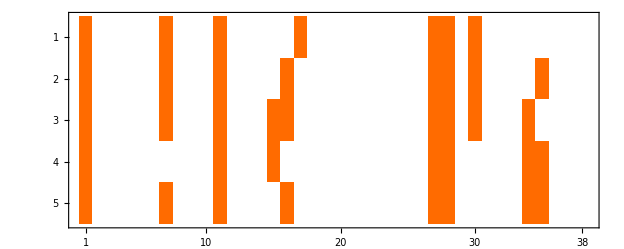

```mathematica
MultipleCheckMatrix[[;;,119;;]]/.{True->0,False->1}//MatrixPlot
```

```mathematica
MultipleCheckMatrix[[;;,119]]
{Pos,Coef,Let}={RemovedBadFunctions[[119,1]],RemovedBadFunctions[[119,2,;;,1]],RemovedBadFunctions[[119,2,;;,2]]};
Coef=-Coef*I;

NCheckDLogAnsatz[CanonicalDEq[[KinVarI,Pos[[1]],Pos[[2]]]],GuessToAnsatz[Coef,Let],Var]
```

{False,False,False,False,False}

Maximal iteration reached -> Try with larger iteration number. Current Value: 200

Use random variables.

False

```mathematica
{}
```

```mathematica
CanonicalDEq[[KinVarI,Pos[[1]],Pos[[2]]]]//RootList
test=D[GuessToAnsatz[Coef,Let],Var]//Together;
```

{√(-s12^2 (s12+s13+s14+s23+s24+s34-4)^2+2 s12^2 s14 (s12+s13+s14+s23+s24+s34-4)+2 s12^2 s23 (s12+s13+s14+s23+s24+s34-4)+s12^2 (-s14^2)+2 s12^2 s14 s23-s12^2 s23^2+2 s12 s14^2 (s12+s13+s23-1)-s14^2 (s12+s13+s23-1)^2+2 s14^2 (s12+s13+s23-1)-2 s12 s14 (s12+s13+s14+s23+s24+s34-4)+4 s12 s14 s23 (s12+s13+s14+s23+s24+s34-4)-2 s12 s23 (s12+s13+s14+s23+s24+s34-4)-2 s12 s14 (s12+s13+s23-1) (s12+s13+s14+s23+s24+s34-4)-2 s12 s23 (s12+s14+s24-1) (s12+s13+s14+s23+s24+s34-4)+2 s12 (s12+s13+s23-1) (s12+s14+s24-1) (s12+s13+s14+s23+s24+s34-4)+2 s12 (s12+s13+s14+s23+s24+s34-4)-2 s12 s14 (s12+s13+s23-1) (s12+s14+s24-1)-2 s12 s23 (s12+s13+s23-1) (s12+s14+s24-1)-(s12+s13+s23-1)^2 (s12+s14+s24-1)^2+2 s23 (s12+s13+s23-1) (s12+s14+s24-1)^2+2 s14 (s12+s13+s23-1)^2 (s12+s14+s24-1)-2 s14 (s12+s13+s23-1) (s12+s14+s24-1)-2 s14 s23 (s12+s13+s23-1) (s12+s14+s24-1)-2 s23 (s12+s13+s23-1) (s12+s14+s24-1)+2 (s12+s13+s23-1) (s12+s14+s24-1)+4 s12 s14 (s12+s13+s23-1)-2 s12 s14 s23 (s12+s13+s23-1)-2 s14 (s12+s13+s23-1)+2 s14 s23 (s12+s13+s23-1)+2 s12 s14^2+2 s12 s23^2 (s12+s14+s24-1)-s23^2 (s12+s14+s24-1)^2+2 s23^2 (s12+s14+s24-1)-2 s12 s14 s23 (s12+s14+s24-1)+4 s12 s23 (s12+s14+s24-1)+2 s14 s23 (s12+s14+s24-1)-2 s23 (s12+s14+s24-1)-4 s12 s14 s23-2 s12 s14+2 s12 s23^2-2 s12 s23-s14^2-2 s14 s23+2 s14-s23^2+2 s23-1)}

$Aborted

```mathematica
DLogMatrix=ConstantArray[0,{87,87}];
WriteDLogEntry[Coefficients_,LetterList_]:=Coefficients*(Log/@LetterList)//Total;
Do[

Coeffs=ValidEntry[[2,;;,1]];
LetterList=ValidEntry[[2,;;,2]];
{RowI,ColumnJ}=ValidEntry[[1]];


DLogMatrix[[RowI,ColumnJ]]=WriteDLogEntry[Coeffs,LetterList];


,{ValidEntry,ValidEntries}]
```

### GetDeq with Kira

```mathematica
$DEIdentitiesDir=KiraReductionsPath<>"DifferentialEquationIdentities/";
InitKiraWeight[MinWeight_,MaxWeight_]:=KiraWeight/@Range[MinWeight,MaxWeight];

DumpGet[MathematicaInputPath<>"DEqReduze_uncrossed.mx"];
DumpGet[$KiraReductionsFolder<>"RReductionDEq_uncrossed.mx"];

(*Reduze has derivatives with respect to mt and not mt2 -> adjust (must check!!!!).*)
DEqReduze[[1;;;;8,2]]=DEqReduze[[1;;;;8,2]]*2mt;

DEqReduze=DEqReduze/.mt->1;
RReductionDEq=RReductionDEq/.mt2->1;
```

```mathematica
DumpSave[$KiraReductionsFolder<>"RReductionDEq_uncrossed.mx",RReductionDEq];
DumpSave[MathematicaInputPath<>"DEqReduze_uncrossed.mx",DEqReduze];
```

Initialize weights

```mathematica
PreCanonicalMI=SelectIntegrals[CanonicalBasisRootSymbol,IntegralSymbol->Penta];
UnreducedIntegralsDE=SelectIntegrals[DEqReduze[[;;,2]]];
(*I need the conversion later for saving the identities*)
CToKira=ToKira[UnreducedIntegralsDE,OutputStyle->"Rules"];
{NbMI,NbUnreducedFI}=Length/@{PreCanonicalMI,UnreducedIntegralsDE};
(*Must have smallest weight because I want express everything through them.*)
CanonicalMIWeights=InitKiraWeight[1, NbMI];

PreCanonicalMIWeights=InitKiraWeight[100+1,100+NbMI];
UnreducedIntegralsDEWeights=InitKiraWeight[1000+1,1000+NbUnreducedFI];
(*Derivatives must have highest weights because these I want to reduce*)
(*Do everything derivative Var by derivative Var*)
DerivativesPreCanonicalWeights=InitKiraWeight[10000+1,10000+NbMI];
DerivativesCanonicalWeights=InitKiraWeight[10000+1+NbMI,10000+2*NbMI];

RPreCanonicalFIToWeight=MapThread[Rule,{PreCanonicalMI,PreCanonicalMIWeights}];
RUnreducedIntegralsDEToWeight=MapThread[Rule,{UnreducedIntegralsDE,UnreducedIntegralsDEWeights}];
RUnreducedIntegralsDEToWeight={RUnreducedIntegralsDEToWeight,RUnreducedIntegralsDEToWeight/.CToKira}//Flatten;
```

Initialize Weights for derivatives

```mathematica
(*There are 7 derivatives, sij, mt, mh2 + scaling relation -> regroup (7, NbMi) array*)
DerivativesMI=Table[DEqReduze[[i;;;;8]],{i,7}];

(*I used a redundant set of MI to compute the derivatives -> remove redundant entries: *)
RequiredDerivativesPosition=Position[DEqReduze[[1;;;;8,1]]/.der[Int_,Var_]->Int/.CToKira,#]&/@PreCanonicalMI//Flatten;
(*There is some bug with the conversion. The Tadpole is not converted -> find reason*)
AppendTo[RequiredDerivativesPosition,6];
RequiredDerivativesPosition=RequiredDerivativesPosition//Union;

DerivativesMI=DerivativesMI[[;;,RequiredDerivativesPosition]];

CrossCheckDimension={7,NbMI}==Dimensions[DerivativesMI];
Print["Correct dimension of final array: ", CrossCheckDimension];
```

Correct dimension of final array: True

Inverse Weights to Integrals :

```mathematica
WeightsToIntegrals={RPreCanonicalFIToWeight,RUnreducedIntegralsDEToWeight,RDerivativesMIToWeight}//Flatten;

(*In the unreduced integrals there are a few integrals which are MI, like Int(1,1,1,1,0) and similar*)
WeightsToIntegrals=Reverse/@WeightsToIntegrals;

AppendTo[WeightsToIntegrals,#->(#/.{KiraWeight[x_]->CanonicalI[x]})]&/@CanonicalMIWeights;
AppendTo[WeightsToIntegrals,#->(#/.{KiraWeight[x_]->der[CanonicalI[x-10000-NbMI],VarNb]})]&/@DerivativesCanonicalWeights;
```

Specify Var

```mathematica
(*mt2=1, mH2=2, s12=3, s14=4, s23=5, s35=6, s45=7 *)
VarNb=1;
DerivativesMIVar=DerivativesMI[[VarNb]]//Flatten;
RDerivativesMIToWeight=MapThread[Rule,{DerivativesMIVar[[;;,1]],DerivativesPreCanonicalWeights}];

(*Check consistent ordering: *)
CorrectOrderQ=0==Total[PreCanonicalMI-ToKira[DerivativesMIVar[[;;,1]]/.der[x__,y_]->x]];
Print["Derivatives and PreCanonicalMI have same ordering: ", CorrectOrderQ]
Clear[CorrectOrderQ]
```

Derivatives and PreCanonicalMI have same ordering: True

Generate relations

```mathematica
$BasisTransformationsPath=MathematicaInputPath<>"Basis_Transformations/";
DumpGet[$BasisTransformationsPath<>"RationalPartTransformationPreCanonicalToCanonical.mx"];
DumpGet[$BasisTransformationsPath<>"DRationalPartTransformationCanonicalToPreCanonical_uncrossed.mx"]

RelationPreToCanonicalLH0=CanonicalMIWeights-RationalPartTransformationPreCanonicalToCanonical.PreCanonicalMIWeights;
RelationPreToCanonicalLH0=RelationToKira/@(RelationPreToCanonicalLH0/.ϵ->eps);
(*These are different because here I have rules instead of Matrix multiplications*)
RelationIBPToPreLH0=RReductionDEq/.RPreCanonicalFIToWeight/.RUnreducedIntegralsDEToWeight/.Rule[x_,y_]->x-y;
RelationIBPToPreLH0=RelationToKira/@(RelationIBPToPreLH0/.ϵ->eps);
RelationDerivativeLH0=DerivativesMIVar/.RDerivativesMIToWeight/.RPreCanonicalFIToWeight/.RUnreducedIntegralsDEToWeight/.Rule[x_,y_]->x-y;
RelationDerivativeLH0=RelationToKira/@(RelationDerivativeLH0/.ϵ->eps);
(*Ordering in derivative of transformation matrix*).
(*mt2=7, mH2=6, s12=1, s14=2, s23=4, s35=5, s45=3 *)
VarNb2={7,6,1,2,4,5,3}[[VarNb]];

RelationTransformDerivative=RationalPartTransformationPreCanonicalToCanonical.(DerivativesMIVar[[;;,1]]-DRationalPartTransformationCanonicalToPreCanonical[[VarNb2]].CanonicalMIWeights);RelationTransformDerivativeLH0=DerivativesCanonicalWeights-RelationTransformDerivative /.RDerivativesMIToWeight;
RelationTransformDerivativeLH0=RelationToKira/@(RelationTransformDerivativeLH0/.ϵ->eps);
```

$Aborted

Error: Equation is not linear. Check input.

$Aborted

$Aborted

Error: Equation is not linear. Check input.

$Aborted

$Aborted

Error: Equation is not linear. Check input.

$Aborted

Write relations

```mathematica
MapThread[WriteFile[#1<>".kira",#2,PathToFile->$DEIdentitiesDir]&,{{"RelationPreToCanonical","RelationIBPToPre","RelationDerivative","RelationTransformDerivative_VarNb_"<>ToString[VarNb]},{RelationPreToCanonicalLH0,RelationIBPToPreLH0,RelationDerivativeLH0,RelationTransformDerivativeLH0}}];

SolutionWeightsString=ToString/@(DerivativesCanonicalWeights/.KiraWeight[x_]->x);
WriteFile["SolutionWeightsDEq.kira",SolutionWeightsString,StandardPath->"Kira"];
```

Write files to: /home/philipp/Programs/TTHProject/Kira_Reductions/DifferentialEquationIdentities/RelationPreToCanonical.kira

Write files to: /home/philipp/Programs/TTHProject/Kira_Reductions/DifferentialEquationIdentities/RelationIBPToPre.kira

Write files to: /home/philipp/Programs/TTHProject/Kira_Reductions/DifferentialEquationIdentities/RelationDerivative.kira

Write files to: /home/philipp/Programs/TTHProject/Kira_Reductions/DifferentialEquationIdentities/RelationTransformDerivative.kira

Write files to: /home/philipp/Programs/TTHProject/Kira_Reductions/SolutionWeightsDEq.kira

```mathematica
PreCanonicalLaTeX=MapThread["I_{"<>ToString[#1]<>"} &= "<>ToString[#2,TeXForm]<>"\\\\"&,{Range[NbMI],PreCanonicalMI}];
WriteFile["Dummy.tex",PreCanonicalLaTeX];
```

Write files to: /home/philipp/Programs/TTHProject/Dummy.tex

## Transform matrices in Fermat notation (use FLink instead)

```mathematica
MatrixToFermat[MathematicaMatrix_,MatrixNameFermat_String]:=Module[
{VarsFermatCompatibleQ,MatrixDimensions,MatrixInitializationLine,MatrixToString,FermatInsertDataInMatrix},

(*Check variable names: *)
VarsFermatCompatibleQ=And@@ValidFermatVarNameQ/@Flatten[{MatrixNameFermat,ToString/@Variables[MathematicaMatrix]}];
If[Not[VarsFermatCompatibleQ],Print[MatrixNameFermat<>" or its variables are not in a valid Fermat format."]; Abort[]];

MatrixDimensions=StringReplace[ToString[Dimensions[MathematicaMatrix]],{"{"->"[","}"->"]"}];

MatrixInitializationLine="Array " <>MatrixNameFermat<>MatrixDimensions<> "; \n";
MatrixToString=StringReplace[ToString[MathematicaMatrix,InputForm],{"{"->"","}"->""}];

FermatInsertDataInMatrix="["<>MatrixNameFermat<>"] := [[ " <> MatrixToString <> "]];";

Return[MatrixInitializationLine<>FermatInsertDataInMatrix]

]

ValidFermatVarNameQ[FermatVariable_String]:=Module[
{NbCharactersQ,StartLowerCaseLetterQ,ListOfSymbols,ValidSymbolsQ,ValidFermatNameQ},

(*Variable names rules on p. 28 Fermat manual 2021.*)
NbCharactersQ=StringLength[FermatVariable]<=10;
StartLowerCaseLetterQ=LowerCaseQ[StringTake[FermatVariable,1]];

ListOfSymbols=StringPart[FermatVariable,#]&/@Range[StringLength[FermatVariable]];
ValidSymbolsQ=And@@(LetterQ[#]||NumberQ[#]||StringMatchQ[#,"_"]&/@ListOfSymbols);

ValidFermatNameQ=StartLowerCaseLetterQ&&NbCharactersQ&&ValidSymbolsQ;

Return[ValidFermatNameQ];

]
```

```mathematica
InitializeInputInDependentMatrices[]
```

True

```mathematica
MMatrixIFermatFormat=MatrixToFermat[MMatrixI/.{},"mMatrixI"];
```

mMatrixI or its variables are not in a valid Fermat format.

$Aborted

```mathematica
And@@ValidFermatVarNameQ/@Flatten[{"a",ToString/@Variables[MMatrixI]}]
```

False

```mathematica
FermatFiles=MathematicaOutputPath<>"FermatFiles/";
FermatFileName="TestMatrix.txt";
(*DeleteFile[FermatFiles<>FermatFileName];*)
WriteString[FermatFiles<>FermatFileName,MMatrixIFermatFormat];
```

```mathematica
ValidFermatVarNameQ/@{"a","b","d","e"}
```

{True,True,True,True}

```mathematica
StringPart["123",#]&/@Range[3]
```

{1,2,3}

## Reduction via KIRA

## Set up Kira files (Amplitude reduction)

### Including D dependence

```mathematica
{ColFactorNb,SUNPower,NfPower,ParityOdd}={3,2,1,True};

InitializeInputInDependentMatrices[]
InitializePhysicalCombinationFormFactors[ParityOdd]
InitializeIBPMatrix[dummy, IncludeDimShift->False,NoApart->True]

InitializeKinematicMatrix[{ColFactorNb,SUNPower,NfPower}]
```

True

True

True

«1 more identical outputs»

```mathematica
KinematicMatrix//MatrixPlot
```

-Graphics-

```mathematica
{NbIntegrals,NbMasterIntegrals}=IBPMatrix//Dimensions;
{NbHelicityAmplitudes,NbFormFactors}=PhysicalCombinationFormFactors//Dimensions;

FolderName="ColFactorNb_"<>ToString[ColFactorNb]<>"_SUNPower_"<>ToString[SUNPower]<>"_NfPower_"<>ToString[NfPower]<>"_ParityOdd_"<>ToString[ParityOdd];

$PathToKiraAmplitudeRelations=MathematicaKiraPath<>"Amplitude_Relations/"<>FolderName<>"/";
$RatracerAmplitudes="RaTracer/example/Amplitude_Reduction_Ratracer/";
$RatracerAmplitudesFolder=$RatracerAmplitudes<>"input_kira/"<>FolderName<>"/";

If[Not[DirectoryQ[$PathToKiraAmplitudeRelations]],CreateDirectory[$PathToKiraAmplitudeRelations]];
If[Not[DirectoryQ[$RatracerAmplitudesFolder]],CreateDirectory[$RatracerAmplitudesFolder]];
```

```mathematica
(*The master integrals must have the smalles weight, such that kira expresses everything through the masters*)
KiraWeightsMaster=KiraWeight/@Range[NbMasterIntegrals];
KiraWeightsFI=KiraWeight/@Range[NbMasterIntegrals+1,NbMasterIntegrals+NbIntegrals];
KiraWeightsFormFactors=KiraWeight/@Range[NbMasterIntegrals+NbIntegrals+1,NbMasterIntegrals+NbIntegrals+NbFormFactors];
KiraWeightsProjectors=KiraWeight/@Range[NbMasterIntegrals+NbIntegrals+NbFormFactors+1,NbMasterIntegrals+NbIntegrals+2NbFormFactors];
KiraWeightsHelicityAmplitudes=KiraWeight/@Range[NbMasterIntegrals+NbIntegrals+2NbFormFactors+1,NbMasterIntegrals+NbIntegrals+2NbFormFactors+NbHelicityAmplitudes];

KiraWeightsHelicityAmplitudesString=ToString/@KiraWeightsHelicityAmplitudes[[;;,1]];

WriteFile["WantedSolutions",KiraWeightsHelicityAmplitudesString,PathToFile->MathematicaKiraPath];
Clear[KiraWeightsHelicityAmplitudesString];

KiraWeightsToMaster=MapThread[Rule,{KiraWeightsMaster,MasterIntegralsReduze}];
```

Write files to: /scratch/ge45leb/Cluster_Scratch/TTHProject/Kira_Reductions/WantedSolutions

Generate relations

```mathematica
(*The rule D -> d is important for compability with fermat*)
IBPRelationsLHS0=KiraWeightsFI-IBPMatrix.KiraWeightsMaster/.D->d/.mH2->mh2/.RKinematicLorenzoSymmetricVars/.mt2->1;
KinematicRelationsLH0=KiraWeightsFormFactors-KinematicMatrix.KiraWeightsFI/.D->d/.mH2->mh2/.RKinematicLorenzoSymmetricVars/.mt2->1;
MMatrixIRelationsLH0=KiraWeightsProjectors-MMatrixI.KiraWeightsFormFactors/.D->d/.mH2->mh2/.RKinematicLorenzoSymmetricVars/.mt2->1;
PhysicalCombinationFormFactorsRelationsLH0=KiraWeightsHelicityAmplitudes-PhysicalCombinationFormFactors.KiraWeightsProjectors/.D->d/.FivePointMandelstamReplacementsLorenzoForm/.RKinematicLorenzoSymmetricVars/.mt2->1;
```

Write relations to Kira

```mathematica
IBPRelationsLHS0Kira=RelationToKira/@IBPRelationsLHS0;
KinematicRelationsLH0Kira=RelationToKira/@KinematicRelationsLH0;
MMatrixIRelationsLH0Kira=RelationToKira/@MMatrixIRelationsLH0;
PhysicalCombinationFormFactorsRelationsLH0Kira=RelationToKira/@PhysicalCombinationFormFactorsRelationsLH0;

KiraRelations={IBPRelationsLHS0Kira,KinematicRelationsLH0Kira,MMatrixIRelationsLH0Kira,PhysicalCombinationFormFactorsRelationsLH0Kira};
KiraRelationsFileNames={"IBPRelations.kira","KinematicRelations.kira","MMatrixIRelations.kira","PhysicalCombinationFormFactorsRelations.kira"};
MapThread[WriteFile[#1,#2,PathToFile->$PathToKiraAmplitudeRelations]&,{KiraRelationsFileNames,KiraRelations}];

Clear[KiraRelationsFileNames,IBPRelationsLHS0Kira,KinematicRelationsLH0Kira,MMatrixIRelationsLH0Kira,PhysicalCombinationFormFactorsRelationsLH0Kira];
```

Write files to: /scratch/ge45leb/Cluster_Scratch/TTHProject/Kira_Reductions/Amplitude_Relations/ColFactorNb_2_SUNPower_2_NfPower_2_ParityOdd_True/IBPRelations.kira

Write files to: /scratch/ge45leb/Cluster_Scratch/TTHProject/Kira_Reductions/Amplitude_Relations/ColFactorNb_2_SUNPower_2_NfPower_2_ParityOdd_True/KinematicRelations.kira

Write files to: /scratch/ge45leb/Cluster_Scratch/TTHProject/Kira_Reductions/Amplitude_Relations/ColFactorNb_2_SUNPower_2_NfPower_2_ParityOdd_True/MMatrixIRelations.kira

Write files to: /scratch/ge45leb/Cluster_Scratch/TTHProject/Kira_Reductions/Amplitude_Relations/ColFactorNb_2_SUNPower_2_NfPower_2_ParityOdd_True/PhysicalCombinationFormFactorsRelations.kira

Write files to Ratracer

Write relations

```mathematica
IBPRelationsLHS0Ratracer=RelationToKira[#,Ratracer->True]&/@IBPRelationsLHS0;
KinematicRelationsLH0Ratracer=RelationToKira[#,Ratracer->True]&/@KinematicRelationsLH0;
MMatrixIRelationsLH0Ratracer=RelationToKira[#,Ratracer->True]&/@MMatrixIRelationsLH0;
PhysicalCombinationFormFactorsRelationsLH0Ratracer=RelationToKira[#,Ratracer->True]&/@PhysicalCombinationFormFactorsRelationsLH0;

RatracerRelations={IBPRelationsLHS0Ratracer,KinematicRelationsLH0Ratracer,MMatrixIRelationsLH0Ratracer,PhysicalCombinationFormFactorsRelationsLH0Ratracer};
RatracerRelationsFileNames={"IBPRelations.ratracer","KinematicRelations.ratracer","MMatrixIRelations.ratracer","PhysicalCombinationFormFactorsRelations.ratracer"};
MapThread[WriteFile[#1,#2,PathToFile->$RatracerAmplitudesFolder]&,{RatracerRelationsFileNames,RatracerRelations}];

Clear[IBPRelationsLHS0Ratracer,KinematicRelationsLH0Ratracer,MMatrixIRelationsLH0Ratracer,PhysicalCombinationFormFactorsRelationsLH0Ratracer,RatracerRelationsFileNames,RatracerRelations]
```

Write files to: RaTracer/example/Amplitude_Reduction_Ratracer/input_kira/ColFactorNb_3_SUNPower_2_NfPower_1_ParityOdd_True/IBPRelations.ratracer

Write files to: RaTracer/example/Amplitude_Reduction_Ratracer/input_kira/ColFactorNb_3_SUNPower_2_NfPower_1_ParityOdd_True/KinematicRelations.ratracer

Write files to: RaTracer/example/Amplitude_Reduction_Ratracer/input_kira/ColFactorNb_3_SUNPower_2_NfPower_1_ParityOdd_True/MMatrixIRelations.ratracer

Write files to: RaTracer/example/Amplitude_Reduction_Ratracer/input_kira/ColFactorNb_3_SUNPower_2_NfPower_1_ParityOdd_True/PhysicalCombinationFormFactorsRelations.ratracer

Write list of preferred Master integrals

```mathematica
(*The weights of the master integrals are 1 to 87. For syntax to set preferred masters see Sec. 4.3.1 in Ratracer paper.*)
PreferredMasterLines="master@"<>ToString[#]<>"*1\n"<>CoefficientToRatracer[-1,#]&/@Range[NbMasterIntegrals];
WriteFile["master-equations.txt",PreferredMasterLines,PathToFile->$RatracerAmplitudes]
```

Write files to: RaTracer/example/Amplitude_Reduction_Ratracer/master-equations.txt

### Partial Fraction in D

```mathematica
InitializePhysicalCombinationFormFactors[True]
InitializeInputInDependentMatrices[]
HelicityProjectorOdd=PhysicalCombinationFormFactors.MMatrixI//Together//Factor;
DumpSave[MathematicaInputPath<>"HelicityProjectorOdd.mx",HelicityProjectorOdd];

InitializePhysicalCombinationFormFactors[False]
HelicityProjectorEven=PhysicalCombinationFormFactors.MMatrixI//Together//Factor;
DumpSave[MathematicaInputPath<>"HelicityProjectorEven.mx",HelicityProjectorEven];
```

True

True

True

```mathematica
{ColFactorNb,SUNPower,NfPower,ParityOdd}={3,2,1,False};

InitializeInputInDependentMatrices[]


IBPTensor={0,0,0,0,0,0};
For[DimComponent=1,DimComponent<=6,DimComponent++,
InitializeIBPMatrix[DimComponent];
IBPTensor[[DimComponent]]=IBPMatrix;
]

InitializeKinematicMatrix[{ColFactorNb,SUNPower,NfPower},DecomposedD->True]
```

True

True

```mathematica
{NbIntegrals,NbMasterIntegrals}=IBPMatrix//Dimensions;
{NbHelicityAmplitudes,NbFormFactors}=PhysicalCombinationFormFactors//Dimensions;
NbDimComponentsFinal=7;
```

```mathematica
(*The master integrals must have the smalles weight, such that kira expresses everything through the masters*)
KiraWeightsMaster=KiraWeight/@Range[NbMasterIntegrals];
KiraWeightsIBPSplit=KiraWeight/@Range[1000,1000+6NbIntegrals-1];

KiraWeightsFI=KiraWeight/@Range[10000,10000+NbIntegrals-1];
KiraWeightsKinematicSplit=KiraWeight/@Range[10000+NbIntegrals,10000+3NbIntegrals-1];


KiraWeightsProjections=KiraWeight/@Range[100000,100000+NbFormFactors*NbDimComponentsFinal];
KiraWeightsHelicityAmplitudes=KiraWeight/@Range[1000000,1000000+NbDimComponentsFinal*NbHelicityAmplitudes];

KiraWeightsToMaster=MapThread[Rule,{KiraWeightsMaster,MasterIntegralsReduze}];
```

KiraWeightsHelicityAmplitudes reads as follows : 
1 - 7 : (+, +, R, L); {D^0, D^1, D^2, 1/(D - 1), 1/(D - 2), 1/(D - 3), 1/(D - 4)}
14 - 21 : (+, +, R, L); {D^0, D^1, D^2, 1/(D - 1), 1/(D - 2), 1/(D - 3), 1/(D - 4)}
21 - 28 : (+, +, R, L); {D^0, D^1, D^2, 1/(D - 1), 1/(D - 2), 1/(D - 3), 1/(D - 4)}
35 - 42 : (+, +, R, L); {D^0, D^1, D^2, 1/(D - 1), 1/(D - 2), 1/(D - 3), 1/(D - 4)}

Write IBP relations to Kira

```mathematica
(*The rule D -> d is important for compability with fermat*)
IBPRelationsLHS0=KiraWeightsIBPSplit-ArrayReshape[IBPTensor,{6*405,87}].KiraWeightsMaster;
KiraIBPFileName=MathematicaKiraPath<>"Amplitude_Relations/"<>"IBPRelations.kira";
CreateFile[KiraIBPFileName,OverwriteTarget->True];
WriteLine[KiraIBPFileName,#]&/@RelationToKira/@IBPRelationsLHS0;
```

Write Kinematic relations to Kira

```mathematica
KiraKinematicFileName=MathematicaKiraPath<>"Amplitude_Relations/"<>"KinematicRelations.kira";
CreateFile[KiraKinematicFileName,OverwriteTarget->True];
KinematicRelationsLH0=DummyHolderWeight-ArrayReshape[Transpose[KinematicMatrixDecomposedD[[;;]]],{16,405*2}].KiraWeightsKinematicSplit;
WriteLine[KiraKinematicFileName,#]&/@RelationToKira/@KinematicRelationsLH0;
```

Write dim split projections  to Kira

```mathematica
PartialFractionMatrix=ConstantArray[0,{Length[KiraWeightsFI],...}]
"Projector4,11,..: 0 = KiraWeightssKinematicSplit[[1;;405]] - KiraWeightsKinematicSplit[[406;;811]]"
"Projector4,11,..: 0 = KiraWeightssKinematicSplit[[1;;405]] - KiraWeightsKinematicSplit[[406;;811]]"
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Write Helicity projector to Kira I HAVE PUT MANIFESTLY PARITY EVEN MUST BE CHANGED !!!

```mathematica
KiraCominationFormFactorsFileName=MathematicaKiraPath<>"Amplitude_Relations/"<>"HelicityAmplitudeRelations.kira";
CreateFile[KiraCominationFormFactorsFileName,OverwriteTarget->True];

(*The first 7 entries are the dim components of the helicity amplitude 1, the next 7 belong to helicity amplitude 2 and so on.*)
HelicityAmplitudeRelationsLH0=Table[KiraWeightsHelicityAmplitudes[[1+DimComponentI*8;;8(DimComponentI+1)]]-HelicityProjectorEven.(KiraWeightsProjections[[1+DimComponentI*16;;16(DimComponentI+1)]]),{DimComponentI,0,NbDimComponentsFinal-1}]//Flatten;

WriteLine[KiraCominationFormFactorsFileName,#]&/@RelationToKira/@HelicityAmplitudeRelationsLH0;
Clear[KiraCominationFormFactorsFileName,HelicityAmplitudeRelationsLH0];
```

Write requested solutions file

```mathematica
KiraWantedSolutionsFileName=MathematicaKiraPath<>"WantedSolutions";
If[FileExistsQ[KiraWantedSolutionsFileName],DeleteFile[KiraWantedSolutionsFileName]];
CreateFile[KiraWantedSolutionsFileName];

WriteLine[KiraWantedSolutionsFileName,#]&/@ToString/@KiraWeightsMaster[[;;,1]];
WriteLine[KiraWantedSolutionsFileName,#]&/@ToString/@KiraWeightsHelicityAmplitudes[[;;,1]];
```

## Load and Convert Kira Result

```mathematica
KiraOutputPath=NotebookDirectory[]<>"Mathematica_Modules/"<>"Kira_Output/";
KiraPhysicalAmplitudes=Get[KiraOutputPath<>"Reduced_Amplitudes/"<>"kira_WantedSolutions.m"];
```

```mathematica
KiraPhysicalAmplitudes=KiraPhysicalAmplitudes[[;;,2]]/.Tuserweight[x_]->KiraWeight[x]/.KiraWeightsToMaster/.d->D;
PhysicalFormFactorsKira=Table[Coefficient[FormFactorI,MasterIntegralsReduze],{FormFactorI,KiraPhysicalAmplitudes}];
```

```mathematica
KiraFormFactorsFileName="PhysicalFormFactors_ColFactorNb_"<>ToString[ColFactorNb]<>"_Nc_"<>ToString[SUNPower]<>"_Nf_"<>ToString[NfPower]<>"_ParityOdd_"<>ToString[ParityOdd]<>".mx";
DumpSave[MathematicaOutputPath<>"Form_Factor_Matrices_Kira/"<>KiraFormFactorsFileName,PhysicalFormFactorsKira];
```

### Comparison with previous results :

```mathematica
{ColFactorNb,SUNPower,NfPower,ParityOdd}={2,2,1,False};

DumpGet[MathematicaOutputPath<>"Form_Factor_Matrices/OldFormFactorFiles/"<>"PhysicalFormFactors_ColFactorNb_"<>ToString[ColFactorNb]<>"_Nf_"<>ToString[NfPower]<>"_SUN_"<>ToString[SUNPower]<>"_Parity_False.mx"];

(*Load Kira result: *)
KiraFormFactorsFileName="PhysicalFormFactors_ColFactorNb_"<>ToString[ColFactorNb]<>"_Nc_"<>ToString[SUNPower]<>"_Nf_"<>ToString[NfPower]<>"_ParityOdd_"<>ToString[ParityOdd]<>".mx";
DumpGet[MathematicaOutputPath<>"Form_Factor_Matrices_Kira/"<>KiraFormFactorsFileName];
```

```mathematica
SameVariablesQ[{PhysicalFormFactors,PhysicalFormFactorsKira}]
SameZeroQ[PhysicalFormFactors,PhysicalFormFactorsKira]
PhysicalFormFactors-PhysicalFormFactorsKira//NRandomEvaluation//Total//Total
```

### Find structure in ugly denominators

```mathematica
InitializeIBPMatrix[dummy,NoApart->True];
DenominatorListIBPsStandard=AbbreviateDenominatorsList[IBPMatrix];

UglyDenominators=If[MaxDegreeVar[#,dummy,IncludeAll->True]>=4,#,Nothing[]]&/@DenominatorListIBPsStandard;
UglyDenomsSymbol=UglyDenom/@Range[Length[UglyDenominators]];

RUglyDenominatorsStandard=MapThread[Rule,{UglyDenominators,UglyDenomsSymbol}];
RUglyDenominatorsIStandard=Reverse/@RUglyDenominators;


Clear[UglyDeniminators,UglyDenomsSymbol,UglyDenominators,DenominatorListIBPs];


IBPMatrixDenoms=Factor[Denominator[IBPMatrix]]/.RUglyDenominators;
{NbIntegrals,NbMasters}=IBPMatrix//Dimensions;

IBPMatrixDenomsUglyStandard=Table[If[MemberQ [Variables[IBPMatrixDenoms[[RowI,ColumnJ]]],UglyDenom[x_]],IBPMatrixDenoms[[RowI,ColumnJ]],0],{RowI,NbIntegrals},{ColumnJ,NbMasters}];
ClearAll[IBPMatrixDenoms];

If[Total[Total[IBPMatrixDenomsUglyStandard]]===0,Print["No high degree denominators in standard IBP matrix."]; Clear[RUglyDenominatorsStandard,RUglyDenominatorsIStandard]];
```

```mathematica
InitializeIBPMatrix[dummy,IncludeDimShift->True];
DenominatorListIBPDimShifts=AbbreviateDenominatorsList[IBPMatrix];
(*I choose >= 4 because the maximum degree in the standard IBP is 3. *)
UglyDenominators=If[MaxDegreeVar[#,dummy,IncludeAll->True]>=4,#,Nothing[]]&/@DenominatorListIBPDimShifts;
UglyDenomsSymbol=UglyDenom/@Range[Length[UglyDenominators]];


RUglyDenominatorsDimShift=MapThread[Rule,{UglyDenominators,UglyDenomsSymbol}];
RUglyDenominatorsIDimShift=Reverse/@RUglyDenominators;

Clear[UglyDeniminators,UglyDenomsSymbol,UglyDenominators,DenominatorListIBPs];
IBPMatrixDenoms=Factor[Denominator[IBPMatrix]]/.RUglyDenominatorsDimShift;
{NbIntegrals,NbMasters}=IBPMatrix//Dimensions;

IBPMatrixDenomsUglyDimShift=Table[If[MemberQ [Variables[IBPMatrixDenoms[[RowI,ColumnJ]]],UglyDenom[x_]],IBPMatrixDenoms[[RowI,ColumnJ]],0],{RowI,NbIntegrals},{ColumnJ,NbMasters}];
ClearAll[IBPMatrixDenoms];
```

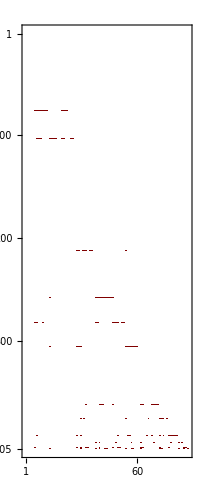

CoefficientArrays::poly: … is not a polynomial.

CoefficientArrays::poly: der(INT(PentaboxGGtoTTHTopologyA,2,20,2,0,{0,0,1,0,1}),s12)+«15»+«1» is not a polynomial.

CoefficientArrays::poly: der(INT(PentaboxGGtoTTHTopologyA,2,20,2,0,{0,0,1,0,1}),s14)+(s12 (-1+s23) INT(PentaboxGGtoTTHTopologyA,1,4,2,0,{0,0,2,0,0}))/(-1+mh2 s12+(1-s12) s14-(-2+Plus[«2»] s12+2 Power[«2»]+Plus[«2»] s14) s23-(1+s12) s23^2-(Plus[«2»] s23-Power[«2»]) s35+(-2 s12-s14+Plus[«2»] s23-Plus[«2»] s35) s45)+«12»+«1» is not a polynomial.

General::stop: Further output of CoefficientArrays::poly will be suppressed during this calculation.

$Aborted

$Aborted

```mathematica
PositionIntegralReductionInvolvesUglyDenoms=NonZeroPostions[IBPMatrixDenomsUglyDimShift][[;;,1]]//Union;
IBPMatrixDenomsUglyDimShift[[PositionIntegralReductionInvolvesUglyDenoms]]//MatrixPlot;

NbUglyDenoms=Length[RUglyDenominatorsDimShift];
UglyDenomsSymbol=UglyDenom/@Range[NbUglyDenoms];

MatrixPlot[IBPMatrixDenomsUglyDimShift/.{#->1,UglyDenom[x_]->0}]&/@UglyDenomsSymbol;
VectorOfIntegralsKiraNotation[[PositionIntegralReductionInvolvesUglyDenoms]];

PositionIntegralReductionInvolvesUglyDenoms=NonZeroPostions[IBPMatrixDenomsUglyDimShift][[;;,2]]//Union;

IBPMatrixDenomsUglyDimShift//MatrixPlot
Export["/home/philipp/Programs/Zettlr/Zettelkasten/Pictures/UglyDenominatorPosition.jpeg",%,"JPEG"];
```